```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory["/Volumes/GoogleDrive/My Drive/GoodNotes/ALP DUNE/constraints"]
<<MaTeX`
<<CustomTicks`
SetOptions[LogTicks,LogPlot->True,MajorTickLength->0.02,MinorTickLength->0.01];
SetOptions[LinTicks,MajorTickLength->0.02,MinorTickLength->0.01];
```

/Volumes/GoogleDrive/My Drive/GoodNotes/ALP DUNE/constraints

#### Various input params

```mathematica
mu=2.2/1000;
md=4.7/1000;
ms=20*md;
mc=1.275;
mb=4.18;
mt = 172.4;

mPi=135/1000;
mEta=0.548;
mEtap=0.958;

mK=497/1000;
Mz=91.1876;
Mz=91.18;
GammaZ=2.495;
Mw=80.379;

GF=1.166 10^(-5);
ThetawatMz = ArcSin[Sqrt[0.231]];
v=Sqrt[1/(Sqrt[2]GF)];

g2atMz=2 Mz Cos[ThetawatMz]/v;
gpatMz = g2atMz Tan[ThetawatMz];
g1atMz=Sqrt[5/3]gpatMz;
alpha1atMz = g1atMz^2/4/Pi;
alpha2atMz = g2atMz^2/4/Pi;

b1=41/10;
b2=-19/6;

alpha1[μ_]:=1/(1/alpha1atMz-b1/(2Pi)Log[μ/Mz]);
alpha2[μ_]:=1/(1/alpha2atMz-b2/(2Pi)Log[μ/Mz]);
alphaEM[mu_]:=3/5alpha1[mu]alpha2[mu]/(alpha2[mu]+3/5alpha1[mu]);

LambdaQCD=0.48;
Nf[μ_]:=4(*using 4 quark flavors*)
beta0[μ_]=11-2/3Nf[μ];
beta1[μ_] = 102-38/3Nf[μ];
z[mu_]:=-beta0[mu]^2/E/beta1[mu](LambdaQCD^2/mu^2)^(beta0[mu]^2/beta1[mu]);

alphas[μ_]:=-4Pi beta0[μ]/beta1[μ]/ProductLog[-1,z[μ]];(* using the expression in 1604.08082v3 eq. 3.21 *)
nflav=3;
EA=(97/4-7/6nflav);
KggNNLO[ma_,c3_,fa_]:=1+alphas[ma]/Pi EA+(alphas[ma]/Pi)^2EA(3/4 EA+(51/8-19/24nflav)/(11/4-nflav/6));
KggNLO[ma_]:=1+alphas[ma]/Pi EA;
GammaaglugluNLO[ma_,c3_,fa_]:=1/(32Pi^3)alphas[ma]^2ma^3/fa^2c3^2KggNLO[ma];
GammaaglugluNNLO[ma_,c3_,fa_]:=1/(32Pi^3)alphas[ma]^2ma^3/fa^2c3^2KggNNLO[ma,c3,fa];
(*This is in GeV*)
LifetimeinmmNLO[ma_,c3_,fa_]:=1/GammaaglugluNLO[ma,c3,fa]*0.198*10^(-12);(*this is in mm*)
LifetimeinmmNNLO[ma_,c3_,fa_]:=1/GammaaglugluNNLO[ma,c3,fa]*0.198*10^(-12);(*this is in mm*)
```

#### Details of meson mixing

```mathematica
(*c2=1;c1=1;*)
c2=0;c1=0;
c3=1;
cgamma[ma_,c1_,c2_,c3_]:=(c2+5/3 c1)+c3(-1.92+1/3 ma^2/(ma^2-mPi^2)+8/9 (ma^2-4/9 mPi^2)/(ma^2-mEta^2)+7/9(ma^2-16/9 mPi^2)/(ma^2-mEtap^2));
GammaPhoton[ma_,fa_,c1_,c2_,c3_]:=alphaEM[ma]^2/(256 Pi^3)cgamma[ma,c1,c2,c3]^2 ma^3/fa^2;
LifetimePhoton[ma_,fa_,c1_,c2_,c3_]:=1/GammaPhoton[ma,fa,c1,c2,c3]*0.198*10^(-15); (*in meter*)

fpi=0.093; 

mixingAPi[ma_,fa_]:=(1/6)ma^2/(ma^2-mPi^2)fpi/fa;
mixingAEta[ma_,fa_]:=(ma^2/Sqrt[6]-Sqrt[2/3](2 mPi^2)/9)1/(ma^2-mEta^2)fpi/fa;
mixingAEtap[ma_,fa_]:=(ma^2/(2Sqrt[3])-4Sqrt[1/3](2 mPi^2)/9)1/(ma^2-mEtap^2)fpi/fa; 


NPOT=1.47*10^22;
Naxions[ma_,fa_,seleff_]:=NPOT*(2.89*Abs[mixingAPi[ma,fa]]^2+0.33*Abs[mixingAEta[ma,fa]]^2+0.03*Abs[mixingAEtap[ma,fa]]^2)*seleff;
```

```mathematica
LifetimePhoton[0.1,1/(4 Pi^2),0,0,1]//ScientificForm
```

3.33635×10^-9

#### Width data from 1811.03474

```mathematica
SetDirectory[NotebookDirectory[]];
widthdata=Import["./decay\ width.csv","Data"]; 

width=widthdata;
width[[All,2]]=widthdata[[All,2]]/(32 Pi^2)^2/10^9; (* width is now in units of GeV for Subscript[f, a]=TeV *)
```

#### a > 3pi width

```mathematica
a3piwidthdata=Import["./a3pi.csv","Data"]; 

a3piwidth=a3piwidthdata;
a3piwidth[[All,2]]=a3piwidthdata[[All,2]]/(32 Pi^2)^2/10^9;(* width is now in units of GeV for Subscript[f, a]=TeV *)
a3piWidthFunc=Interpolation[a3piwidth,InterpolationOrder->1];
```

#### a > 2pi gamma width

```mathematica
a2pigwidthdata=Import["./a2pig.csv","Data"]; 

a2pigwidth=a2pigwidthdata;
a2pigwidth[[All,2]]=a2pigwidthdata[[All,2]]/(32 Pi^2)^2/10^9;(* width is now in units of GeV for Subscript[f, a]=TeV *)
a2pigWidthFunc=Interpolation[a2pigwidth,InterpolationOrder->1];
```

#### Numerical width function and comparison with a > γγ

InterpolatingFunction::dmval: Input value {0.015061} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

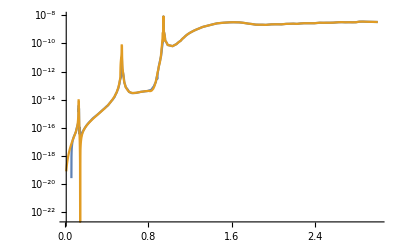

```mathematica
WidthFunc=Interpolation[width,InterpolationOrder->1];
CombinedWidthFunc[ma_,c1_,c2_,c3_]:=Piecewise[{{GammaPhoton[ma,1000,c1,c2,c3],ma<3mPi},{GammaPhoton[ma,1000,c1,c2,c3]+a2pigWidthFunc[ma]+a3piWidthFunc[ma],0.94≥ ma≥ 3mPi},{WidthFunc[ma],ma>0.94}}];
LogPlot[{WidthFunc[ma],CombinedWidthFunc[ma,0,0,1]},{ma,0.015,3}]
```

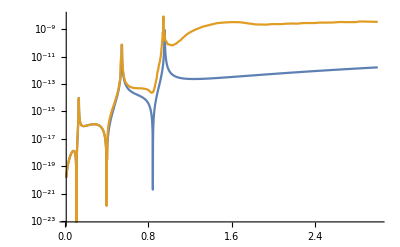

```mathematica
LogPlot[{GammaPhoton[ma,1000,1,1,1],CombinedWidthFunc[ma,1,1,1]},{ma,0.015,3}]
```

#### Width function for f_a=1 TeV

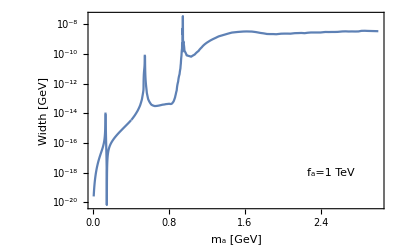

```mathematica
WidthFinal[ma_,c1_,c2_,c3_]:=CombinedWidthFunc[ma,c1,c2,c3];

LifetimeFinal[ma_,c1_,c2_,c3_]:=1/WidthFinal[ma,c1,c2,c3]*0.198*10^(-15); (*in meter*);

LogPlot[WidthFinal[ma,0,0,1],{ma,10^-2,3},Frame->True,FrameLabel->{"m_a [GeV]","Width [GeV]"},Epilog->Inset[Framed["f_a=1 TeV"],{2.5,Log[10^-18]}]]
```

#### Lifetime calculation

```mathematica
LifetimeFinal[0.4,0,0,1] 1/((1000*4 Pi^2)^2)
```

3.95786×10^-11

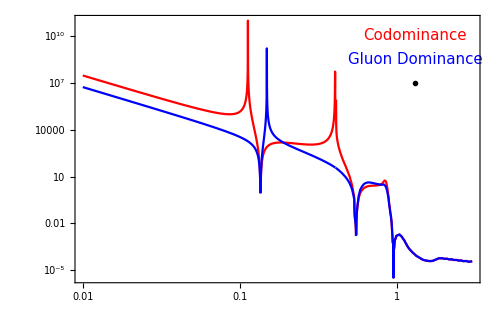

```mathematica
LogLogPlot[{LifetimeFinal[ma,1,1,1] 10^6/((4 Pi^2)^2),LifetimeFinal[ma,0,0,1] 10^6/((4 Pi^2)^2)},{ma,0.01,3},PlotStyle->{Red,Blue},Frame->True,FrameTicksStyle->Directive[Black,15,AbsoluteThickness[0.5]],LabelStyle->{FontFamily->"CMU Serif",FontSize->12},FrameLabel->{{Style[MaTeX["\\text{Lifetime [m]}",Magnification->1.5],FontSize->15,Black],None},{Style[MaTeX["m_a[\\text{GeV}]",Magnification->1.5],FontSize->15,Black],None}},Epilog->{Style[Text[Style["Codominance",{15,Red},FontFamily->"CMU Serif"],{Log[1.3],Log[10^10]}],20],Style[Text[Style["Gluon Dominance",{15,Blue},FontFamily->"CMU Serif"],{Log[1.3],Log[10^8.5]}],20],Style[Text[Style[MaTeX["f_G= 1\\text{ PeV}",Magnification->1.4],{15,Black},FontFamily->"CMU Serif"],{Log[1.3],Log[10^7]}],20]},ImageSize->500,FrameTicks->{{LogTicks[10,10^-6,10^12,TickLabelStep->3,ShowMinorTicks->False],LogTicks[10,10^-6,10^12,TickLabelStep->3,ShowMinorTicks->False]},{LogTicks[10,10^-2,3],LogTicks[10,10^-2,3,ShowTickLabels-> False]}}]
```

#### The low mass scaling (away from resonances) can be obtained just by looking at c_i:

```mathematica
LifetimeFinal[0.01,1,1,1]/LifetimeFinal[0.01,0,0,1]
```

5.52504

```mathematica
(1.92/(8/3-1.92))^2(*the ratio of effective cγ's *)
```

6.61224

#### Explaining the large lifetime peaks

```mathematica
NSolve[cgamma[ma,1,1,1]==0,ma](*codominance*)
```

{{ma→0.845108},{ma→-0.845108},{ma→-0.402472},{ma→0.402472},{ma→-0.11232},{ma→0.11232}}

Hence at m_a=0.11 and 0.40 we will have very large lifetime. The one at m_a=0.84 is not important since hadronic modes dominate there. Note in reality, there will be smoothing out due to a non-zero width.

```mathematica
NSolve[cgamma[ma,0,0,1]==0,ma] (*Gluon dominance*)
```

{{ma→0.-3.34561 ⅈ},{ma→0.+3.34561 ⅈ},{ma→0.690706},{ma→-0.690706},{ma→0.148225},{ma→-0.148225}}

Hence at m_a=0.15 we will have very large lifetime. The one at m_a=0.69 is not important since hadronic modes dominate there. Note in reality, there will be smoothing out due to a non-zero width.

#### Importing Pythia data

```mathematica
(*pi0=Import["/Users/soubhik/Documents/pythia8244/examples/mesons-pn-1M.txt","Data"];*)
pi0=Import["./mesons-pn-100K.txt","Data"];
(* I am not copying the simulation files, but here is the order of various quantities in pi0:
part.id(); part.px(); part.py(); part.pz(); part.e(); part.eta(); part.pT(); part.m()
*)
```

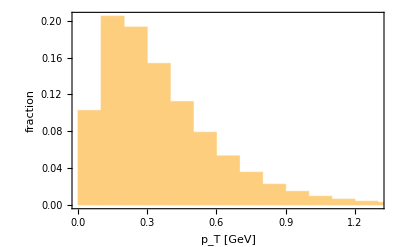

```mathematica
Histogram[pi0[[All,7]],{0.1},"Probability",Frame->True,FrameLabel->{"p_T [GeV]","fraction"}]
```

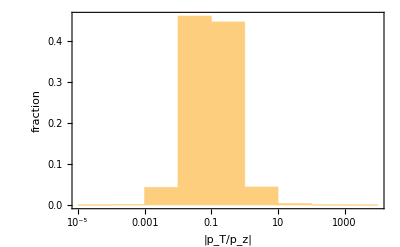

```mathematica
Histogram[Abs[pi0[[All,7]]/pi0[[All,4]]],(*{0.01},"Probability",*){"Log",10},"Probability",Frame-> True,FrameLabel->{"|p_T/p_z|","fraction"}]
```

#### Boost of axions, m_a=input

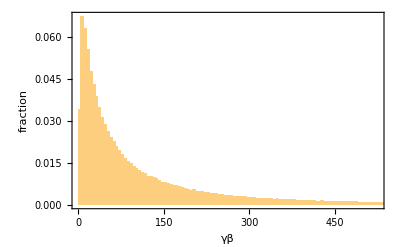

```mathematica
ma=0.05;
Histogram[Sqrt[pi0[[All,7]]^2+pi0[[All,4]]^2]/ma,{5.0},"Probability",FrameLabel->{"γβ","fraction"},Frame->True]
```

#### Energy distribution of axions at ND, m_a= input

```mathematica
ma=0.05;
enlist={};
dist=579; (* distance in m to HPTPC *)
length=10; (* decay length in m of HPTPC *)
radius=2.5; (* radius in m of HPTPC *)
For[i=1,i<Length[pi0]+1,i++,
If[Abs[(pi0[[i]][[7]])/(pi0[[i]][[4]])]<radius/dist ,AppendTo[enlist,pi0[[i]][[5]]],Continue]];
```

```mathematica
Length[enlist]/Length[pi0]//N
```

0.0102782

```mathematica
Naxions[0.05,1/(4 Pi^2),Length[enlist]/Length[pi0]]
```

4.17756×10^18

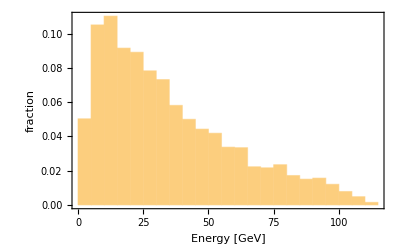

```mathematica
Histogram[enlist,{5.0},"Probability",FrameLabel->{"Energy [GeV]","fraction"},Frame->True]
```

```mathematica
Histogram[enlist,{1.0},NPOT*2.49*mixingAPi[0.05,1/(4 Pi^2)]^2/Length[pi0]#2&,Frame->True,FrameLabel->{"Energy [GeV]","N_a"}]
```

-Graphics-

## Main code

```mathematica
dist=574; (* distance in m to LArTPC and MPD *)
length=10; (* decay length in m of LArTPC and MPD *)
radius=2.5; (* radius in m of MPD *)
lifetime=Table[10^x,{x,-3,6,1/3}];
masslist=(*Table[0.001*y,{y,1,10,1}];*)Flatten[{Table[0.001+y*0.001,{y,0,8,1}],Table[0.01+y*0.01,{y,0,11,1}],Table[0.12+y*0.001,{y,1,50,1}],Table[0.17+y*0.03,{y,1,7,1}],Table[0.40+y*0.01,{y,1,30,1}],Table[0.70+y*0.05,{y,1,2,1}]}];
axions={};
For[nn=1,nn<Length[masslist]+1,nn++,ma=masslist[[nn]];
For[j=1,j<Length[lifetime]+1,j++,
(*fa=(alphaEM[ma]cgamma[ma])/Sqrt[256 Pi^3] ma^(3/2)Sqrt[lifetime[[j]]/(0.198*10^(-15))];*)
fa=Sqrt[lifetime[[j]]/LifetimeFinal[ma,c1,c2,c3]]*1000; (* in GeV, glu dominance*)
decayprob={};
list={};
For[i=1,i<Length[pi0]+1,i++,gabeta=Sqrt[(pi0[[i]][[7]])^2+(pi0[[i]][[4]])^2]/ma;
If[Abs[(pi0[[i]][[7]])/(pi0[[i]][[4]])]<radius/dist ,AppendTo[decayprob,Exp[-dist/(gabeta*lifetime[[j]])]-Exp[-(dist+length)/(gabeta*lifetime[[j]])]],Continue]];

AppendTo[axions,{ma,fa,Sum[decayprob[[i]],{i,Length[decayprob]}]*Naxions[ma,fa,Length[decayprob]/Length[pi0]]/Length[decayprob],lifetime[[j]]}]]]
```

General::munfl: Exp[-1015.23] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1032.92] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1444.48] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.41} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

## Results of Meson-mixing Simulation

```mathematica
axionfinallistglu={{0.001,0.010986534379876343,9.66464683668535*^12,1/1000},{0.001,0.016126027116487186,9.24544631358535*^13,1/(100 10^(2/3))},{0.001,0.023669770791233523,1.8991459210891066*^14,1/(100 10^(1/3))},{0.001,0.03474247223215481,1.7675854103767478*^14,1/100},{0.001,0.05099497529773694,1.0326799930359031*^14,1/(10 10^(2/3))},{0.001,0.0748503873944238,4.416090817882673*^13,1/(10 10^(1/3))},{0.001,0.10986534379876343,1.5057122223639977*^13,1/10},{0.001,0.16126027116487185,4.3691540636350864*^12,1/10^(2/3)},{0.001,0.23669770791233524,1.1311433139089446*^12,1/10^(1/3)},{0.001,0.3474247223215482,2.715749835968101*^11,1},{0.001,0.5099497529773692,6.222741088028334*^10,10^(1/3)},{0.001,0.7485038739442379,1.3856226373495678*^10,10^(2/3)},{0.001,1.0986534379876343,3.035284067445896*^9,10},{0.001,1.6126027116487185,6.592174241380981*^8,10 10^(1/3)},{0.001,2.366977079123352,1.4256676472640803*^8,10 10^(2/3)},{0.001,3.4742472232154817,3.0770029198350053*^7,100},{0.001,5.099497529773693,6.634729224595741*^6,100 10^(1/3)},{0.001,7.485038739442379,1.4299633320167433*^6,100 10^(2/3)},{0.001,10.986534379876343,308131.7564918884,1000},{0.001,16.126027116487183,66390.52737646109,1000 10^(1/3)},{0.001,23.66977079123352,14303.960963993633,1000 10^(2/3)},{0.001,34.74247223215482,3081.750521317152,10000},{0.001,50.99497529773693,663.9485783284724,10000 10^(1/3)},{0.001,74.85038739442379,143.04394052530728,10000 10^(2/3)},{0.001,109.86534379876343,30.81793831985563,100000},{0.001,161.26027116487185,6.639529094783694,100000 10^(1/3)},{0.001,236.6977079123352,1.430443735994221,100000 10^(2/3)},{0.001,347.4247223215482,0.30817981689634877,1000000},{0.002,0.031168639793455265,5.229778757660854*^9,1/1000},{0.002,0.04574930666160974,8.286467394660759*^11,1/(100 10^(2/3))},{0.002,0.06715079881212824,6.472211951832637*^12,1/(100 10^(1/3))},{0.002,0.09856389331667877,1.2035196990284633*^13,1/100},{0.002,0.14467201042420091,1.059582325747916*^13,1/(10 10^(2/3))},{0.002,0.21234947094605447,5.976473595600672*^12,1/(10 10^(1/3))},{0.002,0.3116863979345527,2.491942534479823*^12,1/10},{0.002,0.45749306661609734,8.343543312732863*^11,1/10^(2/3)},{0.002,0.6715079881212824,2.3900170272565186*^11,1/10^(1/3)},{0.002,0.9856389331667876,6.1327490540389786*^10,1},{0.002,1.4467201042420088,1.4642253011850183*^10,10^(1/3)},{0.002,2.1234947094605445,3.3435125052587523*^9,10^(2/3)},{0.002,3.1168639793455273,7.42980402050124*^8,10},{0.002,4.574930666160974,1.6257395857689366*^8,10 10^(1/3)},{0.002,6.715079881212824,3.528893149716908*^7,10 10^(2/3)},{0.002,9.856389331667877,7.629768943525242*^6,100},{0.002,14.46720104242009,1.64651538280574*^6,100 10^(1/3)},{0.002,21.234947094605445,355005.6266684146,100 10^(2/3)},{0.002,31.168639793455267,76511.17759417152,1000},{0.002,45.74930666160974,16486.590156643848,1000 10^(1/3)},{0.002,67.15079881212824,3552.203990385964,1000 10^(2/3)},{0.002,98.56389331667877,765.3267388173055,10000},{0.002,144.6720104242009,164.88740671251608,10000 10^(1/3)},{0.002,212.34947094605448,35.52419082930215,10000 10^(2/3)},{0.002,311.6863979345527,7.653482500579802,100000},{0.002,457.4930666160974,1.6488955792460565,100000 10^(1/3)},{0.002,671.5079881212824,0.35524405960970906,100000 10^(2/3)},{0.002,985.6389331667876,0.07653504006899095,1000000},{0.003,0.057364166016379774,7.4420881965080965*^6,1/1000},{0.003,0.08419908086659304,1.909973937542646*^10,1/(100 10^(2/3))},{0.003,0.12358734923043668,5.518179596132435*^11,1/(100 10^(1/3))},{0.003,0.1814014206877879,1.9292677240408699*^12,1/100},{0.003,0.266260872431138,2.3893456390807485*^12,1/(10 10^(2/3))},{0.003,0.39081751355083766,1.662525458465275*^12,1/(10 10^(1/3))},{0.003,0.5736416601637977,8.033294053645923*^11,1/10},{0.003,0.8419908086659303,2.992898277374527*^11,1/10^(2/3)},{0.003,1.2358734923043668,9.248092306726335*^10,1/10^(1/3)},{0.003,1.8140142068778788,2.5023163274015156*^10,1},{0.003,2.66260872431138,6.17991100513626*^9,10^(1/3)},{0.003,3.908175135508376,1.4409527862001674*^9,10^(2/3)},{0.003,5.736416601637978,3.2426469013949037*^8,10},{0.003,8.419908086659303,7.144939933726925*^7,10 10^(1/3)},{0.003,12.358734923043666,1.5564290116403406*^7,10 10^(2/3)},{0.003,18.14014206877879,3.370954009646849*^6,100},{0.003,26.6260872431138,728053.9037591765,100 10^(1/3)},{0.003,39.08175135508376,157036.32026753397,100 10^(2/3)},{0.003,57.36416601637978,33850.704998242036,1000},{0.003,84.19908086659304,7294.742084907551,1000 10^(1/3)},{0.003,123.58734923043667,1571.787567837734,1000 10^(2/3)},{0.003,181.4014206877879,338.6496759006323,10000},{0.003,266.260872431138,72.96169225175515,10000 10^(1/3)},{0.003,390.81751355083765,15.719303228088066,10000 10^(2/3)},{0.003,573.6416601637977,3.386639533012648,100000},{0.003,841.9908086659304,0.7296312006991074,100000 10^(1/3)},{0.003,1235.8734923043667,0.15719446014217814,100000 10^(2/3)},{0.003,1814.014206877879,0.03386653812910438,1000000},{0.004,0.08843514748745654,15901.661564630502,1/1000},{0.004,0.1298050447141384,6.510420040835414*^8,1/(100 10^(2/3))},{0.004,0.19052774956506235,6.90889645039053*^10,1/(100 10^(1/3))},{0.004,0.2796564912732796,4.4685770392543713*^11,1/100},{0.004,0.41047959307667753,7.567891244470529*^11,1/(10 10^(2/3))},{0.004,0.6025016460917524,6.319526097530889*^11,1/(10 10^(1/3))},{0.004,0.8843514748745653,3.445640389298237*^11,1/10},{0.004,1.298050447141384,1.4018752907229114*^11,1/10^(2/3)},{0.004,1.9052774956506233,4.612017731230194*^10,1/10^(1/3)},{0.004,2.7965649127327956,1.3047226536092314*^10,1},{0.004,4.104795930766775,3.319435982505936*^9,10^(1/3)},{0.004,6.025016460917522,7.883316357513148*^8,10^(2/3)},{0.004,8.843514748745653,1.794221420072769*^8,10},{0.004,12.980504471413841,3.97932645923827*^7,10 10^(1/3)},{0.004,19.052774956506234,8.698257067555876*^6,10 10^(2/3)},{0.004,27.965649127327957,1.8870965698819293*^6,100},{0.004,41.047959307667746,407904.37406055577,100 10^(1/3)},{0.004,60.25016460917522,88015.96570948222,100 10^(2/3)},{0.004,88.43514748745653,18976.09698692235,1000},{0.004,129.8050447141384,4089.642579792804,1000 10^(1/3)},{0.004,190.52774956506232,881.2235758502775,1000 10^(2/3)},{0.004,279.6564912732796,189.86755026037798,10000},{0.004,410.4795930766774,40.907092614062115,10000 10^(1/3)},{0.004,602.5016460917523,8.813302848258282,10000 10^(2/3)},{0.004,884.3514748745654,1.8987822305895303,100000},{0.004,1298.050447141384,0.40908159979706843,100000 10^(1/3)},{0.004,1905.2774956506232,0.08813409589585879,100000 10^(2/3)},{0.004,2796.5649127327956,0.01898792904210054,1000000},{0.005,0.12372445553391126,42.63328243669575,1/1000},{0.005,0.18160266521961427,2.7583253146579333*^7,1/(100 10^(2/3))},{0.005,0.26655625900756563,1.0700363147653883*^10,1/(100 10^(1/3))},{0.005,0.39125108175138357,1.2729940307046002*^11,1/100},{0.005,0.5742780512510233,2.907744667207283*^11,1/(10 10^(2/3))},{0.005,0.8429249030376813,2.869280587158373*^11,1/(10 10^(1/3))},{0.005,1.2372445553391125,1.7387136182472333*^11,1/10},{0.005,1.8160266521961426,7.631540986050415*^10,1/10^(2/3)},{0.005,2.6655625900756563,2.6514081938774586*^10,1/10^(1/3)},{0.005,3.9125108175138354,7.796932477848091*^9,1},{0.005,5.742780512510232,2.0373706237414072*^9,10^(1/3)},{0.005,8.429249030376813,4.920153118784414*^8,10^(2/3)},{0.005,12.372445553391126,1.1314598657933621*^8,10},{0.005,18.16026652196142,2.5248816827931263*^7,10 10^(1/3)},{0.005,26.655625900756565,5.537421330414796*^6,10 10^(2/3)},{0.005,39.12510817513835,1.2033610216901284*^6,100},{0.005,57.427805125102324,260322.06108201115,100 10^(1/3)},{0.005,84.29249030376812,56192.71088828474,100 10^(2/3)},{0.005,123.72445553391124,12117.223254791666,1000},{0.005,181.60266521961424,2611.666885662567,1000 10^(1/3)},{0.005,266.55625900756564,562.7757503935721,1000 10^(2/3)},{0.005,391.25108175138354,121.25728454955696,10000},{0.005,574.2780512510233,26.125182809196993,10000 10^(1/3)},{0.005,842.9249030376811,5.628609306163571,10000 10^(2/3)},{0.005,1237.2445553391126,1.2126580446013344,100000},{0.005,1816.0266521961425,0.26126034888839156,100000 10^(1/3)},{0.005,2665.5625900756563,0.05628694518837156,100000 10^(2/3)},{0.005,3912.5108175138353,0.012126665660597974,1000000},{0.006,0.16278968311938016,0.1321929180943549,1/1000},{0.006,0.238942577659055,1.3444782334019411*^6,1/(100 10^(2/3))},{0.006,0.3507197404916904,1.8986708890643866*^9,1/(100 10^(1/3))},{0.006,0.5147861782343054,4.1436727713942505*^10,1/100},{0.006,0.7556027753942776,1.2673426911006242*^11,1/(10 10^(2/3))},{0.006,1.109073200336924,1.4630968202336746*^11,1/(10 10^(1/3))},{0.006,1.6278968311938018,9.760039329822598*^10,1/10},{0.006,2.3894257765905498,4.581757383335582*^10,1/10^(2/3)},{0.006,3.507197404916904,1.6714166755231546*^10,1/10^(1/3)},{0.006,5.147861782343054,5.088128890622801*^9,1},{0.006,7.556027753942777,1.3622563689213495*^9,10^(1/3)},{0.006,11.090732003369238,3.3412992979379725*^8,10^(2/3)},{0.006,16.27896831193802,7.757875033696224*^7,10},{0.006,23.8942577659055,1.7412767075697068*^7,10 10^(1/3)},{0.006,35.071974049169036,3.8311850646917582*^6,10 10^(2/3)},{0.006,51.47861782343055,833943.1504894461,100},{0.006,75.56027753942777,180550.8685745716,100 10^(1/3)},{0.006,110.90732003369237,38988.26446596425,100 10^(2/3)},{0.006,162.78968311938016,8408.810962150901,1000},{0.006,238.942577659055,1812.5310025906506,1000 10^(1/3)},{0.006,350.71974049169035,390.58887592052866,1000 10^(2/3)},{0.006,514.7861782343053,84.15892022796311,10000},{0.006,755.6027753942776,18.13239982853823,10000 10^(1/3)},{0.006,1109.0732003369237,3.906598146091071,10000 10^(2/3)},{0.006,1627.8968311938015,0.841660159858319,100000},{0.006,2389.42577659055,0.18133109492093363,100000 10^(1/3)},{0.006,3507.197404916904,0.039066691164855484,100000 10^(2/3)},{0.006,5147.861782343054,0.00841667256872329,1000000},{0.007,0.20530712801797468,0.00045371881964640395,1/1000},{0.007,0.3013496521423737,72349.27676389011,1/(100 10^(2/3))},{0.007,0.44232079871274155,3.7061262147172594*^8,1/(100 10^(1/3))},{0.007,0.6492381444045708,1.4813668997337866*^10,1/100},{0.007,0.9529512728693406,6.042186485682036*^10,1/(10 10^(2/3))},{0.007,1.398741180397137,8.104997439422467*^10,1/(10 10^(1/3))},{0.007,2.0530712801797466,5.912973122749952*^10,1/10},{0.007,3.013496521423737,2.9500100433526516*^10,1/10^(2/3)},{0.007,4.423207987127416,1.1250276466426558*^10,1/10^(1/3)},{0.007,6.492381444045709,3.5344596641762314*^9,1},{0.007,9.529512728693406,9.676536709334284*^8,10^(1/3)},{0.007,13.98741180397137,2.4083330442001796*^8,10^(2/3)},{0.007,20.530712801797467,5.642276085508278*^7,10},{0.007,30.134965214237372,1.273430918841973*^7,10 10^(1/3)},{0.007,44.23207987127415,2.8105885326379533*^6,10 10^(2/3)},{0.007,64.92381444045708,612779.6454430652,100},{0.007,95.29512728693405,132773.96098475214,100 10^(1/3)},{0.007,139.8741180397137,28682.166017068525,100 10^(2/3)},{0.007,205.3071280179747,6187.141662259735,1000},{0.007,301.3496521423737,1333.758091924909,1000 10^(1/3)},{0.007,442.3207987127415,287.4275023441249,1000 10^(2/3)},{0.007,649.2381444045708,61.93218836277224,10000},{0.007,952.9512728693405,13.343666843910952,10000 10^(1/3)},{0.007,1398.7411803971368,2.8748840231138484,10000 10^(2/3)},{0.007,2053.0712801797467,0.6193828025214333,100000},{0.007,3013.4965214237372,0.1334427612081687,100000 10^(1/3)},{0.007,4423.207987127415,0.028749449546637953,100000 10^(2/3)},{0.007,6492.381444045709,0.006193888961023806,1000000},{0.008,0.2510270847807118,1.6795589153157782*^-6,1/1000},{0.008,0.3684573711944319,4194.31285889756,1/(100 10^(2/3))},{0.008,0.5408214595891402,7.770688665343674*^7,1/(100 10^(1/3))},{0.008,0.7938173422992386,5.681678279998674*^9,1/100},{0.008,1.16516451365252,3.08312308103281*^10,1/(10 10^(2/3))},{0.008,1.7102276197983939,4.7821348743462555*^10,1/(10 10^(1/3))},{0.008,2.5102708478071176,3.79708066274018*^10,1/10},{0.008,3.684573711944319,2.0036419891352444*^10,1/10^(2/3)},{0.008,5.408214595891402,7.960231433947618*^9,1/10^(1/3)},{0.008,7.938173422992386,2.5747098843459277*^9,1},{0.008,11.651645136525202,7.196304653246958*^8,10^(1/3)},{0.008,17.102276197983937,1.815946702121323*^8,10^(2/3)},{0.008,25.10270847807118,4.290871706628912*^7,10},{0.008,36.845737119443186,9.735340345287556*^6,10 10^(1/3)},{0.008,54.08214595891401,2.155211582164906*^6,10 10^(2/3)},{0.008,79.38173422992385,470641.10218855366,100},{0.008,116.516451365252,102056.63787389964,100 10^(1/3)},{0.008,171.02276197983937,22054.86521753904,100 10^(2/3)},{0.008,251.0270847807118,4758.3876532987315,1000},{0.008,368.4573711944319,1025.8478481435961,1000 10^(1/3)},{0.008,540.8214595891402,221.0807994925617,1000 10^(2/3)},{0.008,793.8173422992386,47.6372793944134,10000},{0.008,1165.16451365252,10.263827553281258,10000 10^(1/3)},{0.008,1710.2276197983936,2.2113433110960137,10000 10^(2/3)},{0.008,2510.2708478071177,0.4764263445698069,100000},{0.008,3684.573711944319,0.10264363147474034,100000 10^(1/3)},{0.008,5408.214595891402,0.022113968745598813,100000 10^(2/3)},{0.008,7938.173422992386,0.004764317011975765,1000000},{0.009000000000000001,0.29974974723925984,6.596264324319142*^-9,1/1000},{0.009000000000000001,0.4399724594676861,257.91328737357384,1/(100 10^(2/3))},{0.009000000000000001,0.6457912537805502,1.7241212840771403*^7,1/(100 10^(1/3))},{0.009000000000000001,0.9478919293358298,2.3035349571144023*^9,1/100},{0.009000000000000001,1.3913150796640015,1.66050139456483*^10,1/(10 10^(2/3))},{0.009000000000000001,2.0421712549623625,2.967732563071088*^10,1/(10 10^(1/3))},{0.009000000000000001,2.997497472392598,2.5550608338234985*^10,1/10},{0.009000000000000001,4.399724594676861,1.4207389414937088*^10,1/10^(2/3)},{0.009000000000000001,6.457912537805503,5.863149081399858*^9,1/10^(1/3)},{0.009000000000000001,9.478919293358297,1.9486508673695989*^9,1},{0.009000000000000001,13.913150796640014,5.552696736822941*^8,10^(1/3)},{0.009000000000000001,20.421712549623624,1.4196937845413178*^8,10^(2/3)},{0.009000000000000001,29.974974723925982,3.381994460858577*^7,10},{0.009000000000000001,43.99724594676861,7.711963490333596*^6,10 10^(1/3)},{0.009000000000000001,64.57912537805502,1.7123140908195914*^6,10 10^(2/3)},{0.009000000000000001,94.78919293358297,374511.97090623033,100},{0.009000000000000001,139.13150796640014,81275.06926939626,100 10^(1/3)},{0.009000000000000001,204.21712549623624,17570.49617196576,100 10^(2/3)},{0.009000000000000001,299.7497472392598,3791.548397763004,1000},{0.009000000000000001,439.97245946768606,817.4775441851605,1000 10^(1/3)},{0.009000000000000001,645.7912537805503,176.1816694717258,1000 10^(2/3)},{0.009000000000000001,947.8919293358297,37.963344235387986,10000},{0.009000000000000001,1391.3150796640014,8.17957032322769,10000 10^(1/3)},{0.009000000000000001,2042.1712549623626,1.7622965952168208,10000 10^(2/3)},{0.009000000000000001,2997.4974723925984,0.37968145157488226,100000},{0.009000000000000001,4399.724594676861,0.08180050504346696,100000 10^(1/3)},{0.009000000000000001,6457.912537805501,0.017623446174936268,100000 10^(2/3)},{0.009000000000000001,9478.919293358296,0.003796862539676709,1000000},{0.01,0.35131089466155196,2.7188222400718148*^-11,1/1000},{0.01,0.5156538738918799,16.648105945211135,1/(100 10^(2/3))},{0.01,0.7568763784449845,4.0083325218091477*^6,1/(100 10^(1/3))},{0.01,1.1109425939619924,9.776164068366897*^8,1/100},{0.01,1.6306407257875748,9.352126526113935*^9,1/(10 10^(2/3))},{0.01,2.393453263065722,1.9210595511738853*^10,1/(10 10^(1/3))},{0.01,3.513108946615519,1.7879810063107525*^10,1/10},{0.01,5.156538738918799,1.044595753226865*^10,1/10^(2/3)},{0.01,7.568763784449843,4.467046660469203*^9,1/10^(1/3)},{0.01,11.109425939619923,1.523086148342309*^9,1},{0.01,16.306407257875748,4.419568318206431*^8,10^(1/3)},{0.01,23.934532630657216,1.1441952104897277*^8,10^(2/3)},{0.01,35.131089466155196,2.747085994315574*^7,10},{0.01,51.56538738918799,6.294543283321578*^6,10 10^(1/3)},{0.01,75.68763784449843,1.401610888475929*^6,10 10^(2/3)},{0.01,111.09425939619922,307030.7227866396,100},{0.01,163.06407257875748,66682.3920625592,100 10^(1/3)},{0.01,239.3453263065722,14421.179647984269,100 10^(2/3)},{0.01,351.3108946615519,3112.5074605900145,1000},{0.01,515.6538738918799,671.1285217648176,1000 10^(1/3)},{0.01,756.8763784449843,144.64632160670658,1000 10^(2/3)},{0.01,1110.9425939619923,31.168718909670062,10000},{0.01,1630.6407257875746,6.715658618316235,10000 10^(1/3)},{0.01,2393.453263065722,1.4469009739778234,10000 10^(2/3)},{0.01,3513.108946615519,0.31173098431090185,100000},{0.01,5156.538738918799,0.0671609666072831,100000 10^(1/3)},{0.01,7568.763784449843,0.014469447825583771,100000 10^(2/3)},{0.01,11109.425939619923,0.003117353653525214,1000000},{0.02,1.000255674233741,2.0471773176489833*^-34,1/1000},{0.02,1.4681745460751043,1.1471112253671778*^-10,1/(100 10^(2/3))},{0.02,2.154985523470403,9.7748067345662,1/(100 10^(1/3))},{0.02,3.1630861730860187,939427.694331934,1/100},{0.02,4.642775568281154,1.4885021564860094*^8,1/(10 10^(2/3))},{0.02,6.814662578856715,1.1626065714981081*^9,1/(10 10^(1/3))},{0.02,10.00255674233741,2.16188827163134*^9,1/10},{0.02,14.681745460751044,1.9033328700073931*^9,1/10^(2/3)},{0.02,21.549855234704026,1.0735568501681756*^9,1/10^(1/3)},{0.02,31.63086173086019,4.4762884589426214*^8,1},{0.02,46.42775568281153,1.4987547313273075*^8,10^(1/3)},{0.02,68.14662578856715,4.2931991760467805*^7,10^(2/3)},{0.02,100.0255674233741,1.1016286865506062*^7,10},{0.02,146.81745460751046,2.6301950090331645*^6,10 10^(1/3)},{0.02,215.49855234704023,600596.7726998266,10 10^(2/3)},{0.02,316.30861730860187,133461.92991612264,100},{0.02,464.27755682811534,29203.239016676358,100 10^(1/3)},{0.02,681.4662578856714,6338.9678776107385,100 10^(2/3)},{0.02,1000.2556742337409,1370.5390952536666,1000},{0.02,1468.1745460751044,295.76435666335965,1000 10^(1/3)},{0.02,2154.9855234704023,63.769832872460356,1000 10^(2/3)},{0.02,3163.0861730860192,13.743739934050717,10000},{0.02,4642.775568281154,2.9614941847327496,10000 10^(1/3)},{0.02,6814.662578856714,0.6380841253746563,10000 10^(2/3)},{0.02,10002.556742337409,0.13747601322609218,100000},{0.02,14681.745460751044,0.029618804827145982,100000 10^(1/3)},{0.02,21549.855234704028,0.006381227625526854,100000 10^(2/3)},{0.02,31630.86173086019,0.0013747987730068614,1000000},{0.03,1.8523026194778736,7.15918742614853*^-57,1/1000},{0.03,2.7188084282840643,3.801264134806213*^-21,1/(100 10^(2/3))},{0.03,3.9906650198400593,0.00011444471292887222,1/(100 10^(1/3))},{0.03,5.85749519344625,4166.998625117571,1/100},{0.03,8.597627155040199,1.0694389211196098*^7,1/(10 10^(2/3))},{0.03,12.61959084145562,3.0897573615191513*^8,1/(10 10^(1/3))},{0.03,18.523026194778737,1.0802419618372836*^9,1/10},{0.03,27.188084282840638,1.337850308956534*^9,1/10^(2/3)},{0.03,39.90665019840059,9.308867506969779*^8,1/10^(1/3)},{0.03,58.5749519344625,4.4980285630603456*^8,1},{0.03,85.97627155040198,1.6757934974202645*^8,10^(1/3)},{0.03,126.19590841455619,5.178222416817208*^7,10^(2/3)},{0.03,185.23026194778737,1.4011052302207163*^7,10},{0.03,271.8808428284064,3.4602761996068023*^6,10 10^(1/3)},{0.03,399.06650198400587,806823.0475651663,10 10^(2/3)},{0.03,585.7495193446249,181563.3572603224,100},{0.03,859.7627155040199,40006.18387505457,100 10^(1/3)},{0.03,1261.959084145562,8714.808774560754,100 10^(2/3)},{0.03,1852.3026194778736,1887.4757128145723,1000},{0.03,2718.8084282840637,407.65434860063107,1000 10^(1/3)},{0.03,3990.665019840059,87.92829557641873,1000 10^(2/3)},{0.03,5857.495193446251,18.953798646611,10000},{0.03,8597.627155040198,4.0844961032119524,10000 10^(1/3)},{0.03,12619.590841455618,0.8800804910145199,10000 10^(2/3)},{0.03,18523.026194778737,0.18961784604172938,100000},{0.03,27188.084282840642,0.040852951923086474,100000 10^(1/3)},{0.03,39906.65019840059,0.008801604228499123,100000 10^(2/3)},{0.03,58574.9519344625,0.0018962584029108987,1000000},{0.04,2.8816471159220076,3.5992285209413473*^-79,1/1000},{0.04,4.2296795262955715,1.8268218418054406*^-31,1/(100 10^(2/3))},{0.04,6.208320510972701,1.9677176646481953*^-9,1/(100 10^(1/3))},{0.04,9.112568299168805,26.88091085690928,1/100},{0.04,13.375421075676059,1.100551788550147*^6,1/(10 10^(2/3))},{0.04,19.63243325901411,1.1679121005546333*^8,1/(10 10^(1/3))},{0.04,28.81647115922007,7.553891180567294*^8,1/10},{0.04,42.29679526295571,1.279311656147194*^9,1/10^(2/3)},{0.04,62.08320510972702,1.068282185450894*^9,1/10^(1/3)},{0.04,91.12568299168804,5.82467132590142*^8,1},{0.04,133.75421075676059,2.3697954185017252*^8,10^(1/3)},{0.04,196.3243325901411,7.796370020818296*^7,10^(2/3)},{0.04,288.1647115922007,2.2055640665041886*^7,10},{0.04,422.9679526295571,5.6113295065610595*^6,10 10^(1/3)},{0.04,620.83205109727,1.3326325893796622*^6,10 10^(2/3)},{0.04,911.2568299168804,303303.5626780677,100},{0.04,1337.5421075676056,67268.39166244697,100 10^(1/3)},{0.04,1963.243325901411,14703.939704233338,100 10^(2/3)},{0.04,2881.6471159220073,3190.036114603606,1000},{0.04,4229.679526295571,689.5405912583274,1000 10^(1/3)},{0.04,6208.320510972701,148.7862962373612,1000 10^(2/3)},{0.04,9112.568299168803,32.07807998203848,10000},{0.04,13375.421075676059,6.913322685004915,10000 10^(1/3)},{0.04,19632.43325901411,1.4896614602920935,10000 10^(2/3)},{0.04,28816.471159220073,0.3209609682878164,100000},{0.04,42296.79526295571,0.06915125853387426,100000 10^(1/3)},{0.04,62083.20510972701,0.0148984184612459,100000 10^(2/3)},{0.04,91125.68299168802,0.0032097901008463926,1000000},{0.05,4.082493807768916,1.9280433000040322*^-101,1/1000},{0.05,5.99228142111485,9.368041808142593*^-42,1/(100 10^(2/3))},{0.05,8.795466281297712,3.6412698780016916*^-14,1/(100 10^(1/3))},{0.05,12.909978966083386,0.18662682580372522,1/100},{0.05,18.949257671433518,120745.45251659694,1/(10 10^(2/3))},{0.05,27.813706532112,4.684074730016429*^7,1/(10 10^(1/3))},{0.05,40.82493807768917,5.572520379359795*^8,1/10},{0.05,59.9228142111485,1.2728627177472904*^9,1/10^(2/3)},{0.05,87.9546628129771,1.2560250999128032*^9,1/10^(1/3)},{0.05,129.09978966083386,7.6112038531636*^8,1},{0.05,189.49257671433517,3.3407004781591153*^8,10^(1/3)},{0.05,278.13706532111996,1.1606516478483212*^8,10^(2/3)},{0.05,408.24938077689166,3.413100460907266*^7,10},{0.05,599.228142111485,8.91857231633988*^6,10 10^(1/3)},{0.05,879.5466281297711,2.1537927800667826*^6,10 10^(2/3)},{0.05,1290.9978966083386,495295.5794357778,100},{0.05,1894.9257671433518,110526.47768543944,100 10^(1/3)},{0.05,2781.3706532111996,24240.014068061715,100 10^(2/3)},{0.05,4082.493807768916,5267.702483556691,1000},{0.05,5992.28142111485,1139.5575749664074,1000 10^(1/3)},{0.05,8795.46628129771,245.98310678889956,1000 10^(2/3)},{0.05,12909.978966083387,53.04304018708208,10000},{0.05,18949.25767143352,11.432549244868344,10000 10^(1/3)},{0.05,27813.706532111995,2.4635459887756657,10000 10^(2/3)},{0.05,40824.93807768916,0.5308027162737221,100000},{0.05,59922.81421114849,0.11436276220256157,100000 10^(1/3)},{0.05,87954.6628129771,0.024639188644655252,100000 10^(2/3)},{0.05,129099.78966083386,0.005308400121087165,1000000},{0.060000000000000005,5.463198615032009,1.051105388191305*^-123,1/1000},{0.060000000000000005,8.018878926017887,4.891802179074628*^-52,1/(100 10^(2/3))},{0.060000000000000005,11.770104614759102,6.893848448633178*^-19,1/(100 10^(1/3))},{0.060000000000000005,17.276150933378553,0.0013290098984912548,1/100},{0.060000000000000005,25.357921687341374,13516.797316039612,1/(10 10^(2/3))},{0.060000000000000005,37.220338881097454,1.9088408380112194*^7,1/(10 10^(1/3))},{0.060000000000000005,54.63198615032009,4.1658677398746616*^8,1/10},{0.060000000000000005,80.18878926017888,1.2741310242134705*^9,1/10^(2/3)},{0.060000000000000005,117.70104614759103,1.470933681298829*^9,1/10^(1/3)},{0.060000000000000005,172.7615093337855,9.812317532577529*^8,1},{0.060000000000000005,253.5792168734137,4.606298887049397*^8,10^(1/3)},{0.060000000000000005,372.2033888109746,1.6803693709886277*^8,10^(2/3)},{0.060000000000000005,546.3198615032009,5.115382698194495*^7,10},{0.060000000000000005,801.8878926017887,1.369553093068869*^7,10 10^(1/3)},{0.060000000000000005,1177.0104614759102,3.359196471941028*^6,10 10^(2/3)},{0.060000000000000005,1727.6150933378551,779942.8940422776,100},{0.060000000000000005,2535.7921687341372,175060.35979330115,100 10^(1/3)},{0.060000000000000005,3722.0338881097455,38517.06239129225,100 10^(2/3)},{0.060000000000000005,5463.198615032009,8384.100432584333,1000},{0.060000000000000005,8018.878926017887,1815.1796251712074,1000 10^(1/3)},{0.060000000000000005,11770.104614759102,391.9709932061347,1000 10^(2/3)},{0.060000000000000005,17276.15093337855,84.53851510610981,10000},{0.060000000000000005,25357.92168734137,18.22239556014559,10000 10^(1/3)},{0.060000000000000005,37220.33888109746,3.9268100728999937,10000 10^(2/3)},{0.060000000000000005,54631.98615032009,0.8460970499907248,100000},{0.060000000000000005,80188.78926017886,0.18229523338256637,100000 10^(1/3)},{0.060000000000000005,117701.04614759101,0.039275232595113944,100000 10^(2/3)},{0.060000000000000005,172761.5093337855,0.008461683876431566,1000000},{0.06999999999999999,7.048486996983842,5.820320693767612*^-146,1/1000},{0.06999999999999999,10.345764052016563,2.597240905663157*^-62,1/(100 10^(2/3))},{0.06999999999999999,15.185504898540646,1.3301516887402066*^-23,1/(100 10^(1/3))},{0.06999999999999999,22.28927296854931,9.673352454926725*^-6,1/100},{0.06999999999999999,32.71617853906507,1542.4972994101752,1/(10 10^(2/3))},{0.06999999999999999,48.020782899032575,7.90151599736219*^6,1/(10 10^(1/3))},{0.06999999999999999,70.48486996983841,3.158296177212712*^8,1/10},{0.06999999999999999,103.45764052016563,1.2882031104627252*^9,1/10^(2/3)},{0.06999999999999999,151.85504898540646,1.7279974619283683*^9,1/10^(1/3)},{0.06999999999999999,222.8927296854931,1.2606546300513873*^9,1},{0.06999999999999999,327.16178539065066,6.28946511788142*^8,10^(1/3)},{0.06999999999999999,480.2078289903257,2.3985756103289795*^8,10^(2/3)},{0.06999999999999999,704.8486996983842,7.535520368307388*^7,10},{0.06999999999999999,1034.5764052016561,2.0630519625651866*^7,10 10^(1/3)},{0.06999999999999999,1518.5504898540644,5.134601730549928*^6,10 10^(2/3)},{0.06999999999999999,2228.927296854931,1.2029416206641234*^6,100},{0.06999999999999999,3271.6178539065068,271497.3585305462,100 10^(1/3)},{0.06999999999999999,4802.078289903257,59922.163914581375,100 10^(2/3)},{0.06999999999999999,7048.486996983841,13064.552826341584,1000},{0.06999999999999999,10345.764052016562,2830.7605191319785,1000 10^(1/3)},{0.06999999999999999,15185.504898540645,611.5080288493488,1000 10^(2/3)},{0.06999999999999999,22289.27296854931,131.91077688653678,10000},{0.06999999999999999,32716.17853906507,28.435920120869632,10000 10^(1/3)},{0.06999999999999999,48020.78289903257,6.127996933388904,10000 10^(2/3)},{0.06999999999999999,70484.86996983842,1.3204034313694462,100000},{0.06999999999999999,103457.64052016563,0.28448895402413443,100000 10^(1/3)},{0.06999999999999999,151855.04898540647,0.06129295329713428,100000 10^(2/3)},{0.06999999999999999,222892.7296854931,0.013205333113533738,1000000},{0.08,8.889185868413776,3.297707164113172*^-168,1/1000},{0.08,13.04754050741419,1.4131132796382687*^-72,1/(100 10^(2/3))},{0.08,19.151170401051836,2.6327671770518183*^-28,1/(100 10^(1/3))},{0.08,28.11007388876934,7.24153422607763*^-8,1/100},{0.08,41.259945866737894,180.84069481345713,1/(10 10^(2/3))},{0.08,60.561318325324116,3.3503860696485247*^6,1/(10 10^(1/3))},{0.08,88.89185868413774,2.4496948187397552*^8,1/10},{0.08,130.47540507414192,1.3293098033605628*^9,1/10^(2/3)},{0.08,191.51170401051834,2.0618504686265755*^9,1/10^(1/3)},{0.08,281.10073888769335,1.6371375441296034*^9,1},{0.08,412.59945866737894,8.638840774693016*^8,10^(1/3)},{0.08,605.6131832532411,3.432108743002496*^8,10^(2/3)},{0.08,888.9185868413776,1.1101039433443117*^8,10},{0.08,1304.754050741419,3.102736437082453*^7,10 10^(1/3)},{0.08,1915.1170401051834,7.829579585585377*^6,10 10^(2/3)},{0.08,2811.007388876934,1.8500389620104148*^6,100},{0.08,4125.99458667379,419745.9206107066,100 10^(1/3)},{0.08,6056.131832532412,92923.4353994171,100 10^(2/3)},{0.08,8889.185868413775,20292.016068138488,1000},{0.08,13047.54050741419,4400.24240544908,1000 10^(1/3)},{0.08,19151.170401051833,950.9107413139461,1000 10^(2/3)},{0.08,28110.07388876934,205.1611690312715,10000},{0.08,41259.94586673789,44.230138254383526,10000 10^(1/3)},{0.08,60561.31832532411,9.532051312133241,10000 10^(2/3)},{0.08,88891.85868413775,2.0539141915543264,100000},{0.08,130475.40507414189,0.4425320114696339,100000 10^(1/3)},{0.08,191511.70401051833,0.09534359364761462,100000 10^(2/3)},{0.08,281100.7388876933,0.02054145078774241,1000000},{0.09,11.087553731095946,1.9346964559072*^-190,1/1000},{0.09,16.274303246222978,7.974923287771005*^-83,1/(100 10^(2/3))},{0.09,23.887410385865554,5.4074380865934445*^-33,1/(100 10^(1/3))},{0.09,35.061923469761275,5.637414575459496*^-10,1/100},{0.09,51.46386559033665,22.042235634554153,1/(10 10^(2/3))},{0.09,75.53862422249675,1.4734986317758923*^6,1/(10 10^(1/3))},{0.09,110.87553731095946,1.9686872605211368*^8,1/10},{0.09,162.74303246222976,1.419126691114941*^9,1/10^(2/3)},{0.09,238.8741038586555,2.53633541418908*^9,1/10^(1/3)},{0.09,350.61923469761274,2.18365069645219*^9,1},{0.09,514.6386559033664,1.2142167176610548*^9,10^(1/3)},{0.09,755.3862422249675,5.0108668277157164*^8,10^(2/3)},{0.09,1108.7553731095945,1.6653900241217238*^8,10},{0.09,1627.4303246222973,4.745542625068003*^7,10 10^(1/3)},{0.09,2388.7410385865546,1.2133234873798897*^7,10 10^(2/3)},{0.09,3506.1923469761273,2.8903791495249458*^6,100},{0.09,5146.386559033665,659093.2874768551,100 10^(1/3)},{0.09,7553.862422249675,146340.77621423022,100 10^(2/3)},{0.09,11087.553731095946,32007.19588641954,1000},{0.09,16274.303246222975,6946.071861182827,1000 10^(1/3)},{0.09,23887.41038586555,1501.64041869439,1000 10^(2/3)},{0.09,35061.92346976128,324.03992851385885,10000},{0.09,51463.86559033665,69.86469304618072,10000 10^(1/3)},{0.09,75538.62422249676,15.05714541709497,10000 10^(2/3)},{0.09,110875.53731095947,3.2444896020423184,100000},{0.09,162743.03246222975,0.6990567189849402,100000 10^(1/3)},{0.09,238874.1038586555,0.15061246826526112,100000 10^(2/3)},{0.09,350619.23469761276,0.03244899906828374,1000000},{0.09999999999999999,13.867693651724633,1.1965041151074794*^-212,1/1000},{0.09999999999999999,20.35499058560864,4.752470494716276*^-93,1/(100 10^(2/3))},{0.09999999999999999,29.877040274010483,1.1729695577819914*^-37,1/(100 10^(1/3))},{0.09999999999999999,43.85349783290766,4.642685694282376*^-12,1/100},{0.09999999999999999,64.36813200180788,2.8428457796743425,1/(10 10^(2/3))},{0.09999999999999999,94.4794970104543,684466.523138289,1/(10 10^(1/3))},{0.09999999999999999,138.67693651724633,1.6693867070899588*^8,1/10},{0.09999999999999999,203.5499058560864,1.5969776690057142*^9,1/10^(2/3)},{0.09999999999999999,298.7704027401049,3.2804188389542937*^9,1/10^(1/3)},{0.09999999999999999,438.53497832907664,3.0531727000395064*^9,1},{0.09999999999999999,643.6813200180787,1.7837612508592598*^9,10^(1/3)},{0.09999999999999999,944.7949701045429,7.627969685029643*^8,10^(2/3)},{0.09999999999999999,1386.7693651724633,2.6008358206903934*^8,10},{0.09999999999999999,2035.499058560864,7.546895234054948*^7,10 10^(1/3)},{0.09999999999999999,2987.704027401048,1.9538381939478133*^7,10 10^(2/3)},{0.09999999999999999,4385.349783290766,4.690949139225631*^6,100},{0.09999999999999999,6436.813200180788,1.0748619612860873*^6,100 10^(1/3)},{0.09999999999999999,9447.949701045429,239340.3557235026,100 10^(2/3)},{0.09999999999999999,13867.693651724632,52428.84670345549,1000},{0.09999999999999999,20354.99058560864,11386.74618467128,1000 10^(1/3)},{0.09999999999999999,29877.04027401048,2462.573810805822,1000 10^(2/3)},{0.09999999999999999,43853.497832907655,531.4946173254363,10000},{0.09999999999999999,64368.13200180788,114.60251946961135,10000 10^(1/3)},{0.09999999999999999,94479.4970104543,24.699938015671833,10000 10^(2/3)},{0.09999999999999999,138676.93651724633,5.322398914436244,100000},{0.09999999999999999,203549.90585608638,1.146772000589392,100000 10^(1/3)},{0.09999999999999999,298770.40274010476,0.24707413209745657,100000 10^(2/3)},{0.09999999999999999,438534.9783290766,0.05323146765514747,1000000},{0.11,17.816219097738166,8.031896322555038*^-235,1/1000},{0.11,26.15063334345441,3.0788515528111687*^-103,1/(100 10^(2/3))},{0.11,38.383880469375654,2.7663115528021307*^-42,1/(100 10^(1/3))},{0.11,56.33983164144264,4.162211149916495*^-14,1/100},{0.11,82.6955636212602,0.399321657685113,1/(10 10^(2/3))},{0.11,121.38048771888,345799.57600009575,1/(10 10^(1/3))},{0.11,178.16219097738167,1.538149252621386*^8,1/10},{0.11,261.5063334345441,1.9513470549993434*^9,1/10^(2/3)},{0.11,383.8388046937565,4.598194082964382*^9,1/10^(1/3)},{0.11,563.3983164144264,4.615175063433183*^9,1},{0.11,826.955636212602,2.8263259336432395*^9,10^(1/3)},{0.11,1213.8048771887998,1.249828652581518*^9,10^(2/3)},{0.11,1781.6219097738165,4.365766709229955*^8,10},{0.11,2615.0633343454406,1.2887594384278835*^8,10 10^(1/3)},{0.11,3838.3880469375645,3.37660293869201*^7,10 10^(2/3)},{0.11,5633.983164144264,8.168158331899188*^6,100},{0.11,8269.55636212602,1.880352824733924*^6,100 10^(1/3)},{0.11,12138.048771887998,419869.7319890213,100 10^(2/3)},{0.11,17816.219097738165,92115.15900825956,1000},{0.11,26150.63334345441,20021.45430095794,1000 10^(1/3)},{0.11,38383.880469375654,4331.5924891461245,1000 10^(2/3)},{0.11,56339.83164144264,935.0484437678729,10000},{0.11,82695.56362126021,201.63477982108265,10000 10^(1/3)},{0.11,121380.48771887997,43.45942196574377,10000 10^(2/3)},{0.11,178162.19097738163,9.364903773749761,100000},{0.11,261506.3334345441,2.017792990909835,100000 10^(1/3)},{0.11,383838.80469375645,0.4347388907896828,100000 10^(2/3)},{0.11,563398.3164144264,0.09366351191265378,1000000},{0.12,25.08679662912092,6.182510502797836*^-257,1/1000},{0.12,36.82238171920749,2.2902091411076663*^-113,1/(100 10^(2/3))},{0.12,54.04786491955304,7.491749430688615*^-47,1/(100 10^(1/3))},{0.12,79.33141654545649,4.288929462599347*^-16,1/100},{0.12,116.44259510484237,0.06450895860816862,1/(10 10^(2/3))},{0.12,170.9143558149008,200712.5098835329,1/(10 10^(1/3))},{0.12,250.86796629120923,1.6267943661111248*^8,1/10},{0.12,368.22381719207493,2.735508302852868*^9,1/10^(2/3)},{0.12,540.4786491955304,7.384058871218812*^9,1/10^(1/3)},{0.12,793.3141654545649,7.976063706527937*^9,1},{0.12,1164.4259510484237,5.110107484623759*^9,10^(1/3)},{0.12,1709.143558149008,2.3326006634921536*^9,10^(2/3)},{0.12,2508.6796629120918,8.337602920212437*^8,10},{0.12,3682.238171920749,2.5017162926197836*^8,10 10^(1/3)},{0.12,5404.786491955303,6.630013491253948*^7,10 10^(2/3)},{0.12,7933.141654545649,1.6155620793009164*^7,100},{0.12,11644.259510484237,3.735888627662573*^6,100 10^(1/3)},{0.12,17091.435581490077,836469.9065020004,100 10^(2/3)},{0.12,25086.79662912092,183788.9449174793,1000},{0.12,36822.381719207486,39977.58901282375,1000 10^(1/3)},{0.12,54047.86491955303,8652.275638615416,1000 10^(2/3)},{0.12,79331.4165454565,1868.0721338686274,10000},{0.12,116442.59510484237,402.8663427191881,10000 10^(1/3)},{0.12,170914.3558149008,86.83529469268102,10000 10^(2/3)},{0.12,250867.9662912092,18.71214050840718,100000},{0.12,368223.81719207496,4.0318130890067225,100000 10^(1/3)},{0.12,540478.6491955303,0.8686682741239146,100000 10^(2/3)},{0.12,793314.1654545648,0.18715295459636053,1000000},{0.121,26.263088138622685,3.843136661030649*^-259,1/1000},{0.121,38.548941535364236,2.24873078292665*^-114,1/(100 10^(2/3))},{0.121,56.5821081532136,2.6470903441754293*^-47,1/(100 10^(1/3))},{0.121,83.05117690779966,2.7452773585514835*^-16,1/100},{0.121,121.90245664041926,0.05437504955847394,1/(10 10^(2/3))},{0.121,178.92833657813847,192255.82666334527,1/(10 10^(1/3))},{0.121,262.6308813862268,1.6545348708986968*^8,1/10},{0.121,385.48941535364236,2.8615934147513795*^9,1/10^(2/3)},{0.121,565.8210815321361,7.82956365308559*^9,1/10^(1/3)},{0.121,830.5117690779965,8.518777873569327*^9,1},{0.121,1219.0245664041925,5.481996583428489*^9,10^(1/3)},{0.121,1789.2833657813846,2.510087796997878*^9,10^(2/3)},{0.121,2626.308813862268,8.992138152171302*^8,10},{0.121,3854.894153536424,2.702401774657158*^8,10 10^(1/3)},{0.121,5658.21081532136,7.169878192887291*^7,10 10^(2/3)},{0.121,8305.117690779965,1.7483650094616093*^7,100},{0.121,12190.245664041926,4.044775535702463*^6,100 10^(1/3)},{0.121,17892.833657813848,905873.0135140558,100 10^(2/3)},{0.121,26263.088138622683,199067.84671787004,1000},{0.121,38548.94153536423,43304.3444128443,1000 10^(1/3)},{0.121,56582.108153213594,9372.627597067123,1000 10^(2/3)},{0.121,83051.17690779966,2023.6356777028054,10000},{0.121,121902.45664041926,436.4186192866805,10000 10^(1/3)},{0.121,178928.33657813846,94.06763963831119,10000 10^(2/3)},{0.121,262630.88138622686,20.270675226043046,100000},{0.121,385489.41535364237,4.36762656752931,100000 10^(1/3)},{0.121,565821.081532136,0.9410208314632991,100000 10^(2/3)},{0.121,830511.7690779965,0.20274121425785285,1000000},{0.122,27.59560560184159,2.3953116061903586*^-261,1/1000},{0.122,40.504809691970564,2.2139079223199357*^-115,1/(100 10^(2/3))},{0.122,59.45293000104571,9.37809903578757*^-48,1/(100 10^(1/3))},{0.122,87.26496711352105,1.7619227485850108*^-16,1/100},{0.122,128.0874548182902,0.045956335418940175,1/(10 10^(2/3))},{0.122,188.00667237386125,184649.2319992607,1/(10 10^(1/3))},{0.122,275.95605601841595,1.687246526452848*^8,1/10},{0.122,405.04809691970564,3.001480040819872*^9,1/10^(2/3)},{0.122,594.5293000104571,8.324018953121295*^9,1/10^(1/3)},{0.122,872.6496711352105,9.122456028358429*^9,1},{0.122,1280.874548182902,5.896392543713115*^9,10^(1/3)},{0.122,1880.0667237386124,2.708131408164568*^9,10^(2/3)},{0.122,2759.560560184159,9.723275014234532*^8,10},{0.122,4050.480969197057,2.9267554536669505*^8,10 10^(1/3)},{0.122,5945.29300010457,7.773772340203618*^7,10 10^(2/3)},{0.122,8726.496711352105,1.8969779935471177*^7,100},{0.122,12808.745481829017,4.390521016482276*^6,100 10^(1/3)},{0.122,18800.667237386122,983569.7545450493,100 10^(2/3)},{0.122,27595.60560184159,216174.07146990858,1000},{0.122,40504.809691970564,47029.14272777152,1000 10^(1/3)},{0.122,59452.930001045694,10179.187068369021,1000 10^(2/3)},{0.122,87264.96711352105,2197.8180256228015,10000},{0.122,128087.45481829018,473.9868286671205,10000 10^(1/3)},{0.122,188006.67237386125,102.16565613606744,10000 10^(2/3)},{0.122,275956.0560184159,22.01575981306833,100000},{0.122,405048.0969197057,4.743635659592756,100000 10^(1/3)},{0.122,594529.3000104569,1.022033737657484,100000 10^(2/3)},{0.122,872649.6711352105,0.22019533617495948,1000000},{0.123,29.123174464343972,1.4972176700292525*^-263,1/1000},{0.123,42.74697414959385,2.1859126982762119*^-116,1/(100 10^(2/3))},{0.123,62.74397734983338,3.332060084140259*^-48,1/(100 10^(1/3))},{0.123,92.09556400178116,1.1340759539738931*^-16,1/100},{0.123,135.17780139305583,0.038953684594585126,1/(10 10^(2/3))},{0.123,198.41387788348888,177856.55142576995,1/(10 10^(1/3))},{0.123,291.2317446434397,1.7255676131863117*^8,1/10},{0.123,427.4697414959384,3.157272999460249*^9,1/10^(2/3)},{0.123,627.4397734983338,8.875100403195408*^9,1/10^(1/3)},{0.123,920.9556400178114,9.79679028143401*^9,1},{0.123,1351.7780139305582,6.360112177572942*^9,10^(1/3)},{0.123,1984.1387788348889,2.930048494306387*^9,10^(2/3)},{0.123,2912.3174464343974,1.0543432118157554*^9,10},{0.123,4274.697414959384,3.178627647081949*^8,10 10^(1/3)},{0.123,6274.397734983337,8.45213828201401*^7,10 10^(2/3)},{0.123,9209.556400178115,2.0639837829761483*^7,100},{0.123,13517.78013930558,4.779152648501087*^6,100 10^(1/3)},{0.123,19841.387788348886,1.0709172894580592*^6,100 10^(2/3)},{0.123,29123.17446434397,235406.75127723019,1000},{0.123,42746.974149593836,51217.156122505556,1000 10^(1/3)},{0.123,62743.977349833374,11086.070292953324,1000 10^(2/3)},{0.123,92095.56400178114,2393.668094839865,10000},{0.123,135177.8013930558,516.2286130412177,10000 10^(1/3)},{0.123,198413.87788348887,111.27110648482576,10000 10^(2/3)},{0.123,291231.7446434397,23.977943803413403,100000},{0.123,427469.7414959384,5.166422840648118,100000 10^(1/3)},{0.123,627439.7734983336,1.1131252218611776,100000 10^(2/3)},{0.123,920955.6400178114,0.23982087633587457,1000000},{0.124,30.898738029140507,9.387656242886149*^-266,1/1000},{0.124,45.35314504961863,2.1650090094807075*^-117,1/(100 10^(2/3))},{0.124,66.56931308818771,1.187586592828891*^-48,1/(100 10^(1/3))},{0.124,97.71038899694618,7.322417198391357*^-17,1/100},{0.124,143.4192374087851,0.03312161693410163,1/(10 10^(2/3))},{0.124,210.51065163153052,171849.82768995792,1/(10 10^(1/3))},{0.124,308.9873802914051,1.7702669924422145*^8,1/10},{0.124,453.53145049618627,3.331505394247558*^9,1/10^(2/3)},{0.124,665.6931308818771,9.492068924472437*^9,1/10^(1/3)},{0.124,977.1038899694618,1.0553492182480839*^10,1},{0.124,1434.192374087851,6.881400487012571*^9,10^(1/3)},{0.124,2105.106516315305,3.1798536763565254*^9,10^(2/3)},{0.124,3089.8738029140513,1.1467647468172746*^9,10},{0.124,4535.314504961863,3.46268249563504*^8,10 10^(1/3)},{0.124,6656.931308818771,9.217628832207297*^7,10 10^(2/3)},{0.124,9771.038899694617,2.2525123996217463*^7,100},{0.124,14341.923740878512,5.217976012795839*^6,100 10^(1/3)},{0.124,21051.065163153053,1.1695606412754352*^6,100 10^(2/3)},{0.124,30898.73802914051,257128.4801529494,1000},{0.124,45353.14504961863,55947.3848423265,1000 10^(1/3)},{0.124,66569.3130881877,12110.388831430328,1000 10^(2/3)},{0.124,97710.38899694617,2614.88176865411,10000},{0.124,143419.23740878512,563.9411649778018,10000 10^(1/3)},{0.124,210510.6516315305,121.55583484455427,10000 10^(2/3)},{0.124,308987.3802914051,26.19425933868256,100000},{0.124,453531.45049618627,5.64396738846363,100000 10^(1/3)},{0.124,665693.130881877,1.216014461870418,100000 10^(2/3)},{0.124,977103.8899694617,0.2619882298263357,1000000},{0.125,32.99641634850684,5.906010703842391*^-268,1/1000},{0.125,48.43211575049122,2.151570796450454*^-118,1/(100 10^(2/3))},{0.125,71.08862402795832,4.247052495222044*^-49,1/(100 10^(1/3))},{0.125,104.34383028449787,4.7439399726967584*^-17,1/100},{0.125,153.15579767246751,0.02825853812464172,1/(10 10^(2/3))},{0.125,224.80196765572165,166609.83925629596,1/(10 10^(1/3))},{0.125,329.9641634850684,1.8222769443104896*^8,1/10},{0.125,484.3211575049122,3.527248946828548*^9,1/10^(2/3)},{0.125,710.8862402795831,1.0186183451079782*^10,1/10^(1/3)},{0.125,1043.4383028449788,1.1406821607377413*^10,1},{0.125,1531.557976724675,7.470306089566353*^9,10^(1/3)},{0.125,2248.0196765572164,3.462443053565608*^9,10^(2/3)},{0.125,3299.6416348506837,1.251427011278312*^9,10},{0.125,4843.211575049122,3.7846131516624635*^8,10 10^(1/3)},{0.125,7108.86240279583,1.0085692334937172*^8,10 10^(2/3)},{0.125,10434.383028449787,2.4663860829972025*^7,100},{0.125,15315.57976724675,5.715913316813795*^6,100 10^(1/3)},{0.125,22480.196765572164,1.2815089886633172*^6,100 10^(2/3)},{0.125,32996.41634850684,281782.1357843355,1000},{0.125,48432.11575049122,61316.322880524305,1000 10^(1/3)},{0.125,71088.62402795831,13273.043619586571,1000 10^(2/3)},{0.125,104343.83028449788,2865.973409273121,10000},{0.125,153155.79767246748,618.0982230020933,10000 10^(1/3)},{0.125,224801.96765572164,133.2297421326131,10000 10^(2/3)},{0.125,329964.1634850684,28.709939752602754,100000},{0.125,484321.15750491223,6.186015685571741,100000 10^(1/3)},{0.125,710886.240279583,1.3328013678301318,100000 10^(2/3)},{0.125,1.0434383028449786*^6,0.2871498201266978,1000000},{0.126,35.5232710439796,3.729295694439698*^-270,1/1000},{0.126,52.14103122189353,2.1461062891739898*^-119,1/(100 10^(2/3))},{0.126,76.53256744055479,1.5244405610784392*^-49,1/(100 10^(1/3))},{0.126,112.33444643848294,3.0847988182257377*^-17,1/100},{0.126,164.88441821113588,0.024198786194384644,1/(10 10^(2/3))},{0.126,242.01722829259626,162126.92711220426,1/(10 10^(1/3))},{0.126,355.232710439796,1.8827362522040564*^8,1/10},{0.126,521.4103122189352,3.748259228991143*^9,1/10^(2/3)},{0.126,765.3256744055478,1.0971245226072803*^10,1/10^(1/3)},{0.126,1123.3444643848295,1.237428498264532*^10,1},{0.126,1648.8441821113588,8.139177168231021*^9,10^(1/3)},{0.126,2420.1722829259625,3.783837190818739*^9,10^(2/3)},{0.126,3552.3271043979603,1.3705874555968306*^9,10},{0.126,5214.103122189353,4.151426341341854*^8,10 10^(1/3)},{0.126,7653.256744055478,1.1075346480876297*^8,10 10^(2/3)},{0.126,11233.444643848294,2.710311021625406*^7,100},{0.126,16488.44182111359,6.283951346758895*^6,100 10^(1/3)},{0.126,24201.722829259623,1.4092365947109547*^6,100 10^(2/3)},{0.126,35523.2710439796,309913.1339223854,1000},{0.126,52141.03122189353,67442.80754454213,1000 10^(1/3)},{0.126,76532.56744055478,14599.77548560992,1000 10^(2/3)},{0.126,112334.44643848295,3152.5027661622694,10000},{0.126,164884.41821113587,679.8990161397214,10000 10^(1/3)},{0.126,242017.22829259624,146.55133669146127,10000 10^(2/3)},{0.126,355232.710439796,31.580693233096458,100000},{0.126,521410.3122189352,6.80457112378324,100000 10^(1/3)},{0.126,765325.6744055477,1.466072134771597,100000 10^(2/3)},{0.126,1.1233444643848294*^6,0.31586284035740164,1000000},{0.127,38.63989374165657,2.3643060165135276*^-272,1/1000},{0.127,56.7156077349981,2.1492904109818995*^-120,1/(100 10^(2/3))},{0.127,83.24712749617079,5.493922725122172*^-50,1/(100 10^(1/3))},{0.127,122.19007277052053,2.0140304369220025*^-17,1/100},{0.127,179.35049932325742,0.02080615260055603,1/(10 10^(2/3))},{0.127,263.2505315543297,158402.2284855986,1/(10 10^(1/3))},{0.127,386.3989374165657,1.953047388404689*^8,1/10},{0.127,567.1560773499809,3.99916906954084*^9,1/10^(2/3)},{0.127,832.4712749617079,1.1864324021283722*^10,1/10^(1/3)},{0.127,1221.9007277052053,1.3477567865634928*^10,1},{0.127,1793.5049932325744,8.903324315566734*^9,10^(1/3)},{0.127,2632.505315543297,4.1515060205946913*^9,10^(2/3)},{0.127,3863.989374165657,1.5070483838905292*^9,10},{0.127,5671.560773499809,4.571823075982745*^8,10 10^(1/3)},{0.127,8324.71274961708,1.2210213762321033*^8,10 10^(2/3)},{0.127,12219.007277052053,2.990133941043726*^7,100},{0.127,17935.049932325743,6.935740990541317*^6,100 10^(1/3)},{0.127,26325.053155432972,1.5558178922072907*^6,100 10^(2/3)},{0.127,38639.89374165657,342199.2148858171,1000},{0.127,56715.6077349981,74474.51046783234,1000 10^(1/3)},{0.127,83247.1274961708,16122.571247755588,1000 10^(2/3)},{0.127,122190.07277052054,3481.3786895771595,10000},{0.127,179350.49932325742,750.8337755652502,10000 10^(1/3)},{0.127,263250.53155432973,161.84185623188293,10000 10^(2/3)},{0.127,386398.93741656566,34.87574609248778,100000},{0.127,567156.077349981,7.514549836058833,100000 10^(1/3)},{0.127,832471.2749617079,1.6190405238652816,100000 10^(2/3)},{0.127,1.2219007277052053*^6,0.3488196921229401,1000000},{0.128,42.59864173807676,1.5055496121259698*^-274,1/1000},{0.128,62.52625514484399,2.162008500629682*^-121,1/(100 10^(2/3))},{0.128,91.77599150875267,1.9887213828458167*^-50,1/(100 10^(1/3))},{0.128,134.70873312183642,1.3207688472643572*^-17,1/100},{0.128,197.72537981852832,0.017968604896442978,1/(10 10^(2/3))},{0.128,290.2211676879314,155449.46099852145,1/(10 10^(1/3))},{0.128,425.98641738076753,2.034953376522213*^8,1/10},{0.128,625.2625514484399,4.285749395840772*^9,1/10^(2/3)},{0.128,917.7599150875267,1.2886739438037416*^10,1/10^(1/3)},{0.128,1347.0873312183642,1.474379642377995*^10,1},{0.128,1977.2537981852834,9.781917731895363*^9,10^(1/3)},{0.128,2902.2116768793144,4.574808814645796*^9,10^(2/3)},{0.128,4259.864173807675,1.6643226351614747*^9,10},{0.128,6252.625514484398,5.056714495517742*^8,10 10^(1/3)},{0.128,9177.599150875267,1.3519924701590753*^8,10 10^(2/3)},{0.128,13470.873312183643,3.313189866623994*^7,100},{0.128,19772.537981852834,7.68840985009744*^6,100 10^(1/3)},{0.128,29022.11676879314,1.7251105904867302*^6,100 10^(2/3)},{0.128,42598.64173807676,379490.8198999408,1000},{0.128,62526.255144843984,82596.73645074204,1000 10^(1/3)},{0.128,91775.99150875266,17881.56975140925,1000 10^(2/3)},{0.128,134708.7331218364,3861.2708309860604,10000},{0.128,197725.37981852837,832.7725393879558,10000 10^(1/3)},{0.128,290221.1676879314,179.50441094694955,10000 10^(2/3)},{0.128,425986.4173807675,38.68196809910212,100000},{0.128,625262.5514484398,8.334669579506993,100000 10^(1/3)},{0.128,917759.9150875265,1.7957393769520786,100000 10^(2/3)},{0.128,1.3470873312183642*^6,0.38688924722848117,1000000},{0.129,47.820109332325345,9.633787789554407*^-277,1/1000},{0.129,70.19032145559444,2.1854159910282805*^-122,1/(100 10^(2/3))},{0.129,103.02530242667916,7.234036795106914*^-51,1/(100 10^(1/3))},{0.129,151.2204634484219,8.703724917876857*^-18,1/100},{0.129,221.9612854990636,0.015593990532053617,1/(10 10^(2/3))},{0.129,325.7946122959786,153297.4687877631,1/(10 10^(1/3))},{0.129,478.2010933232535,2.1306425316780835*^8,1/10},{0.129,701.9032145559444,4.615265916576824*^9,1/10^(2/3)},{0.129,1030.2530242667915,1.406540534999183*^10,1/10^(1/3)},{0.129,1512.2046344842188,1.620726757804697*^10,1},{0.129,2219.6128549906357,1.0799218554339611*^10,10^(1/3)},{0.129,3257.946122959786,5.065598280179685*^9,10^(2/3)},{0.129,4782.010933232535,1.846861145350388*^9,10},{0.129,7019.032145559444,5.619930546886691*^8,10 10^(1/3)},{0.129,10302.530242667915,1.504204597277056*^8,10 10^(2/3)},{0.129,15122.046344842189,3.688780025631996*^7,100},{0.129,22196.12854990636,8.56367902727103*^6,100 10^(1/3)},{0.129,32579.461229597862,1.9220073330278136*^6,100 10^(2/3)},{0.129,47820.10933232535,422866.5847391597,1000},{0.129,70190.32145559444,92044.51683249195,1000 10^(1/3)},{0.129,103025.30242667915,19927.681596243772,1000 10^(2/3)},{0.129,151220.46344842188,4303.175500958218,10000},{0.129,221961.28549906358,928.087209745382,10000 10^(1/3)},{0.129,325794.6122959786,200.0502946456538,10000 10^(2/3)},{0.129,478201.0933232535,43.109542514774354,100000},{0.129,701903.2145559443,9.288671455556392,100000 10^(1/3)},{0.129,1.0302530242667915*^6,2.001283843164477,100000 10^(2/3)},{0.129,1.512204634484219*^6,0.4311735595124401,1000000},{0.13,55.061364757041346,6.197794925851112*^-279,1/1000},{0.13,80.81903086465692,2.2210209712073564*^-123,1/(100 10^(2/3))},{0.13,118.62611431306888,2.645637167259471*^-51,1/(100 10^(1/3))},{0.13,174.1193237095744,5.7667138180653596*^-18,1/100},{0.13,255.57221581976336,0.013606544439780151,1/(10 10^(2/3))},{0.13,375.12871120479815,151993.84719118537,1/(10 10^(1/3))},{0.13,550.6136475704135,2.2428933589869472*^8,1/10},{0.13,808.1903086465693,4.996974305704464*^9,1/10^(2/3)},{0.13,1186.2611431306887,1.543470001464403*^10,1/10^(1/3)},{0.13,1741.1932370957438,1.791185819233078*^10,1},{0.13,2555.7221581976337,1.1986294580586758*^10,10^(1/3)},{0.13,3751.2871120479813,5.6390626822865095*^9,10^(2/3)},{0.13,5506.136475704136,2.0603702797292185*^9,10},{0.13,8081.903086465693,6.279208464904323*^8,10 10^(1/3)},{0.13,11862.611431306887,1.6824770253528783*^8,10 10^(2/3)},{0.13,17411.93237095744,4.128838627030404*^7,100},{0.13,25557.221581976333,9.589421399090208*^6,100 10^(1/3)},{0.13,37512.87112047982,2.1527868560049054*^6,100 10^(2/3)},{0.13,55061.36475704135,473710.77649984846,1000},{0.13,80819.03086465693,103119.48500759921,1000 10^(1/3)},{0.13,118626.11431306887,22326.244819086194,1000 10^(2/3)},{0.13,174119.32370957438,4821.205294636942,10000},{0.13,255572.21581976334,1039.8218774267746,10000 10^(1/3)},{0.13,375128.7112047981,224.13570065811277,10000 10^(2/3)},{0.13,550613.6475704135,48.2998783577934,100000},{0.13,808190.3086465693,10.407024761937361,100000 10^(1/3)},{0.13,1.1862611431306887*^6,2.24223869867999,100000 10^(2/3)},{0.13,1.7411932370957439*^6,0.48308700364769286,1000000},{0.131,65.83654250636239,4.011265852858152*^-281,1/1000},{0.131,96.63482887360797,2.27080018001243*^-124,1/(100 10^(2/3))},{0.131,141.8405310474658,9.733937943336377*^-52,1/(100 10^(1/3))},{0.131,208.1934275905957,3.843814245078358*^-18,1/100},{0.131,305.5861605412047,0.011944058828746438,1/(10 10^(2/3))},{0.131,448.5391426378205,151610.12847746222,1/(10 10^(1/3))},{0.131,658.3654250636239,2.375278367670882*^8,1/10},{0.131,966.3482887360797,5.4428192346242485*^9,1/10^(2/3)},{0.131,1418.4053104746579,1.703911119027617*^10,1/10^(1/3)},{0.131,2081.9342759059573,1.991443632657434*^10,1},{0.131,3055.8616054120475,1.3383451215940392*^10,10^(1/3)},{0.131,4485.391426378204,6.31491955588862*^9,10^(2/3)},{0.131,6583.654250636239,2.312261803589117*^9,10},{0.131,9663.482887360797,7.057594754823754*^8,10 10^(1/3)},{0.131,14184.053104746577,1.8930731953878745*^8,10 10^(2/3)},{0.131,20819.34275905957,4.648878839780326*^7,100},{0.131,30558.616054120474,1.0801872540803978*^7,100 10^(1/3)},{0.131,44853.91426378205,2.4256122432250166*^6,100 10^(2/3)},{0.131,65836.5425063624,533823.1705039048,1000},{0.131,96634.82887360797,116213.82181380023,1000 10^(1/3)},{0.131,141840.53104746577,25162.212130928543,1000 10^(2/3)},{0.131,208193.4275905957,5433.709535480117,10000},{0.131,305586.16054120474,1171.9345053547595,10000 10^(1/3)},{0.131,448539.14263782045,252.61382019800465,10000 10^(2/3)},{0.131,658365.4250636239,54.43683758463027,100000},{0.131,966348.2887360797,11.729346108549654,100000 10^(1/3)},{0.131,1.418405310474658*^6,2.52713955870073,100000 10^(2/3)},{0.131,2.0819342759059572*^6,0.5444685697252608,1000000},{0.132,83.67862032026983,2.613626458503741*^-283,1/1000},{0.132,122.8234176217173,2.3373648483175015*^-125,1/(100 10^(2/3))},{0.132,180.28012243199623,3.605530873975242*^-52,1/(100 10^(1/3))},{0.132,264.6150316725011,2.5794118922768593*^-18,1/100},{0.132,388.40174969068784,0.01055560401820817,1/(10 10^(2/3))},{0.132,570.095803739122,152249.27923618007,1/(10 10^(1/3))},{0.132,836.7862032026984,2.5324560828701234*^8,1/10},{0.132,1228.234176217173,5.968439563770605*^9,1/10^(2/3)},{0.132,1802.8012243199623,1.893704722898296*^10,1/10^(1/3)},{0.132,2646.150316725011,2.2289781476579433*^10,1},{0.132,3884.0174969068785,1.5043740072069798*^10,10^(1/3)},{0.132,5700.9580373912195,7.119139376126736*^9,10^(2/3)},{0.132,8367.862032026984,2.612302839082821*^9,10},{0.132,12282.341762171729,7.985470763253145*^8,10 10^(1/3)},{0.132,18028.012243199624,2.1442521093676302*^8,10 10^(2/3)},{0.132,26461.503167250106,5.269359924576412*^7,100},{0.132,38840.17496906879,1.2248826186713088*^7,100 10^(1/3)},{0.132,57009.58037391219,2.751251088433117*^6,100 10^(2/3)},{0.132,83678.62032026982,605577.8669303494,1000},{0.132,122823.4176217173,131844.8667658452,1000 10^(1/3)},{0.132,180280.1224319962,28547.648720730376,1000 10^(2/3)},{0.132,264615.0316725011,6164.893806611104,10000},{0.132,388401.74969068787,1329.646267438853,10000 10^(1/3)},{0.132,570095.803739122,286.6101474447877,10000 10^(2/3)},{0.132,836786.2032026984,61.76296331601941,100000},{0.132,1.228234176217173*^6,13.307896107062902,100000 10^(1/3)},{0.132,1.8028012243199623*^6,2.867246259074204,100000 10^(2/3)},{0.132,2.6461503167250105*^6,0.6177441786632424,1000000},{0.133,119.18652712264765,1.7159198437230433*^-285,1/1000},{0.133,174.9418972210401,2.4242025628053053*^-126,1/(100 10^(2/3))},{0.133,256.7795886174581,1.345692174082386*^-52,1/(100 10^(1/3))},{0.133,376.9008921130012,1.744121575085816*^-18,1/100},{0.133,553.2148534095679,0.009399716185853264,1/(10 10^(2/3))},{0.133,812.0083566722144,154056.70488469262,1/(10 10^(1/3))},{0.133,1191.8652712264764,2.7205980873812306*^8,1/10},{0.133,1749.4189722104015,6.5946438080973215*^9,1/10^(2/3)},{0.133,2567.7958861745806,2.120644225173473*^10,1/10^(1/3)},{0.133,3769.008921130013,2.5137828861219303*^10,1},{0.133,5532.148534095679,1.703812824354926*^10,10^(1/3)},{0.133,8120.083566722143,8.086486221475577*^9,10^(2/3)},{0.133,11918.652712264762,2.9735742129748163*^9,10},{0.133,17494.189722104013,9.10354005930181*^8,10 10^(1/3)},{0.133,25677.958861745803,2.4470816757555628*^8,10 10^(2/3)},{0.133,37690.089211300125,6.017704103672419*^7,100},{0.133,55321.48534095678,1.3994348687054345*^7,100 10^(1/3)},{0.133,81200.83566722143,3.1441380405853926*^6,100 10^(2/3)},{0.133,119186.52712264763,692157.6186204684,1000},{0.133,174941.89722104013,150706.18625598587,1000 10^(1/3)},{0.133,256779.58861745804,32632.795189332523,1000 10^(2/3)},{0.133,376900.89211300126,7047.209560307846,10000},{0.133,553214.853409568,1519.9569968558512,10000 10^(1/3)},{0.133,812008.3566722143,327.63359200802824,10000 10^(2/3)},{0.133,1.1918652712264764*^6,70.60342455307456,100000},{0.133,1.7494189722104012*^6,15.212738730259842,100000 10^(1/3)},{0.133,2.5677958861745805*^6,3.2776544688952782,100000 10^(2/3)},{0.133,3.7690089211300123*^6,0.7061661782100329,1000000},{0.134,225.3548985888836,1.1362963891166018*^-287,1/1000},{0.134,330.77575510380916,2.5360380172716086*^-127,1/(100 10^(2/3))},{0.134,485.5124110885081,5.066030135933355*^-53,1/(100 10^(1/3))},{0.134,712.6347614171373,1.189543056029803*^-18,1/100},{0.134,1046.0047808901024,0.008442994008505546,1/(10 10^(2/3))},{0.134,1535.3250513196756,157236.71629951562,1/(10 10^(1/3))},{0.134,2253.5489858888363,2.9480280448501575*^8,1/10},{0.134,3307.757551038091,7.349626343603624*^9,1/10^(2/3)},{0.134,4855.124110885081,2.3953192145890907*^10,1/10^(1/3)},{0.134,7126.347614171373,2.8594584199825527*^10,1},{0.134,10460.047808901023,1.9463291879011086*^10,10^(1/3)},{0.134,15353.250513196755,9.264349998592136*^9,10^(2/3)},{0.134,22535.489858888363,3.4139164720625596*^9,10},{0.134,33077.57551038091,1.0467337069359912*^9,10 10^(1/3)},{0.134,48551.2411088508,2.8166664434238017*^8,10 10^(2/3)},{0.134,71263.47614171372,6.931341345683464*^7,100},{0.134,104600.47808901024,1.6125896730566168*^7,100 10^(1/3)},{0.134,153532.50513196754,3.6239790673759617*^6,100 10^(2/3)},{0.134,225354.8985888836,797907.6351845547,1000},{0.134,330775.7551038091,173744.68080612578,1000 10^(1/3)},{0.134,485512.41108850803,37622.771444880855,1000 10^(2/3)},{0.134,712634.7614171372,8124.962194174052,10000},{0.134,1.0460047808901024*^6,1752.4234635476764,10000 10^(1/3)},{0.134,1.5353250513196755*^6,377.7442482115093,10000 10^(2/3)},{0.134,2.253548985888836*^6,81.40217043999208,100000},{0.134,3.307757551038091*^6,17.539531459264722,100000 10^(1/3)},{0.134,4.855124110885081*^6,3.778974122031197,100000 10^(2/3)},{0.134,7.126347614171373*^6,0.814174959456356,1000000},{0.135,ComplexInfinity,Indeterminate,1/1000},{0.135,ComplexInfinity,Indeterminate,1/(100 10^(2/3))},{0.135,ComplexInfinity,Indeterminate,1/(100 10^(1/3))},{0.135,ComplexInfinity,Indeterminate,1/100},{0.135,ComplexInfinity,Indeterminate,1/(10 10^(2/3))},{0.135,ComplexInfinity,Indeterminate,1/(10 10^(1/3))},{0.135,ComplexInfinity,Indeterminate,1/10},{0.135,ComplexInfinity,Indeterminate,1/10^(2/3)},{0.135,ComplexInfinity,Indeterminate,1/10^(1/3)},{0.135,ComplexInfinity,Indeterminate,1},{0.135,ComplexInfinity,Indeterminate,10^(1/3)},{0.135,ComplexInfinity,Indeterminate,10^(2/3)},{0.135,ComplexInfinity,Indeterminate,10},{0.135,ComplexInfinity,Indeterminate,10 10^(1/3)},{0.135,ComplexInfinity,Indeterminate,10 10^(2/3)},{0.135,ComplexInfinity,Indeterminate,100},{0.135,ComplexInfinity,Indeterminate,100 10^(1/3)},{0.135,ComplexInfinity,Indeterminate,100 10^(2/3)},{0.135,ComplexInfinity,Indeterminate,1000},{0.135,ComplexInfinity,Indeterminate,1000 10^(1/3)},{0.135,ComplexInfinity,Indeterminate,1000 10^(2/3)},{0.135,ComplexInfinity,Indeterminate,10000},{0.135,ComplexInfinity,Indeterminate,10000 10^(1/3)},{0.135,ComplexInfinity,Indeterminate,10000 10^(2/3)},{0.135,ComplexInfinity,Indeterminate,100000},{0.135,ComplexInfinity,Indeterminate,100000 10^(1/3)},{0.135,ComplexInfinity,Indeterminate,100000 10^(2/3)},{0.135,ComplexInfinity,Indeterminate,1000000},{0.136,198.24108846871673,5.140748458833667*^-292,1/1000},{0.136,290.9781244669843,2.8634161235592155*^-129,1/(100 10^(2/3))},{0.136,427.097477986683,7.407474826482221*^-54,1/(100 10^(1/3))},{0.136,626.8933653920861,5.70887487142877*^-19,1/100},{0.136,920.1536225996385,0.0070279984158272725,1/(10 10^(2/3))},{0.136,1350.6008133515436,168992.10649021284,1/(10 10^(1/3))},{0.136,1982.410884687167,3.5712657030819255*^8,1/10},{0.136,2909.781244669843,9.418139814991386*^9,1/10^(2/3)},{0.136,4270.9747798668295,3.152803519835428*^10,1/10^(1/3)},{0.136,6268.933653920862,3.8169867576726364*^10,1},{0.136,9201.536225996386,2.6200714528048706*^10,10^(1/3)},{0.136,13506.008133515435,1.254344005606513*^10,10^(2/3)},{0.136,19824.10884687167,4.641742882281872*^9,10},{0.136,29097.81244669843,1.4274467616257212*^9,10 10^(1/3)},{0.136,42709.747798668286,3.849248514474386*^8,10 10^(2/3)},{0.136,62689.33653920862,9.485371005677615*^7,100},{0.136,92015.36225996385,2.208659664738589*^7,100 10^(1/3)},{0.136,135060.08133515436,4.966101536065232*^6,100 10^(2/3)},{0.136,198241.0884687167,1.0937280495568162*^6,1000},{0.136,290978.1244669843,238195.64440573537,1000 10^(1/3)},{0.136,427097.4779866829,51582.83507879815,1000 10^(2/3)},{0.136,626893.3653920861,11140.150962582577,10000},{0.136,920153.6225996385,2402.7908935700475,10000 10^(1/3)},{0.136,1.3506008133515436*^6,517.938428685314,10000 10^(2/3)},{0.136,1.9824108846871674*^6,111.6137813089663,100000},{0.136,2.909781244669843*^6,24.04919537928946,100000 10^(1/3)},{0.136,4.2709747798668295*^6,5.181515695808246,100000 10^(2/3)},{0.136,6.268933653920862*^6,1.116351082587838,1000000},{0.137,92.06984177552498,3.5244816556883525*^-294,1/1000},{0.137,135.14004632819538,3.10137965568287*^-130,1/(100 10^(2/3))},{0.137,198.3584610269377,2.8872156291397713*^-54,1/(100 10^(1/3))},{0.137,291.15040382198,4.031308258890516*^-19,1/100},{0.137,427.3503494977721,0.006536023458484478,1/(10 10^(2/3))},{0.137,627.2645300108653,178580.55656394633,1/(10 10^(1/3))},{0.137,920.6984177552497,4.006583597095156*^8,1/10},{0.137,1351.4004632819538,1.0867254632132214*^10,1/10^(2/3)},{0.137,1983.5846102693772,3.686920229715919*^10,1/10^(1/3)},{0.137,2911.5040382198,4.4950093364753334*^10,1},{0.137,4273.503494977721,3.0984523512756855*^10,10^(1/3)},{0.137,6272.645300108652,1.4876222457939323*^10,10^(2/3)},{0.137,9206.984177552498,5.51651298322462*^9,10},{0.137,13514.004632819539,1.6989761251353073*^9,10 10^(1/3)},{0.137,19835.846102693773,4.586264584266477*^8,10 10^(2/3)},{0.137,29115.040382198,1.1309267917694654*^8,100},{0.137,42735.034949777204,2.6344632561303552*^7,100 10^(1/3)},{0.137,62726.45300108652,5.925036642248088*^6,100 10^(2/3)},{0.137,92069.84177552498,1.3051128606767803*^6,1000},{0.137,135140.04632819537,284253.1483780292,1000 10^(1/3)},{0.137,198358.46102693773,61559.16636865663,1000 10^(2/3)},{0.137,291150.40382198006,13294.935904181715,10000},{0.137,427350.34949777205,2867.574726553618,10000 10^(1/3)},{0.137,627264.5300108653,618.1282322639383,10000 10^(2/3)},{0.137,920698.4177552497,133.20454633204335,100000},{0.137,1.3514004632819537*^6,28.701337775716983,100000 10^(1/3)},{0.137,1.9835846102693772*^6,6.183844721632069,100000 10^(2/3)},{0.137,2.9115040382197998*^6,1.3323018589722246,1000000},{0.138,56.55714269554695,2.455116803931173*^-296,1/1000},{0.138,83.01453262732069,3.4130003563642375*^-131,1/(100 10^(2/3))},{0.138,121.84867019236971,1.1434057227695628*^-54,1/(100 10^(1/3))},{0.138,178.84938886908336,2.892378800095626*^-19,1/100},{0.138,262.51500199669533,0.00617606578207458,1/(10 10^(2/3))},{0.138,385.3193276705555,191741.66431355325,1/(10 10^(1/3))},{0.138,565.5714269554696,4.5670702172822785*^8,1/10},{0.138,830.145326273207,1.2740447429933249*^10,1/10^(2/3)},{0.138,1218.4867019236972,4.380641119958335*^10,1/10^(1/3)},{0.138,1788.4938886908337,5.378263201184368*^10,1},{0.138,2625.1500199669526,3.722825034308135*^10,10^(1/3)},{0.138,3853.193276705554,1.79250126886635*^10,10^(2/3)},{0.138,5655.714269554695,6.66093622146747*^9,10},{0.138,8301.45326273207,2.0544666413760142*^9,10 10^(1/3)},{0.138,12184.867019236972,5.551687364467849*^8,10 10^(2/3)},{0.138,17884.938886908338,1.3699243593147215*^8,100},{0.138,26251.50019966953,3.192544138169313*^7,100 10^(1/3)},{0.138,38531.93276705554,7.182037102837955*^6,100 10^(2/3)},{0.138,56557.14269554695,1.5822235986800103*^6,1000},{0.138,83014.5326273207,344633.74297208403,1000 10^(1/3)},{0.138,121848.67019236971,74638.22310125288,1000 10^(2/3)},{0.138,178849.38886908337,16119.904261064223,10000},{0.138,262515.0019966953,3476.918805102615,10000 10^(1/3)},{0.138,385319.32767055545,749.4800256984697,10000 10^(2/3)},{0.138,565571.4269554695,161.51070465508116,100000},{0.138,830145.326273207,34.800442559744035,100000 10^(1/3)},{0.138,1.2184867019236973*^6,7.497929826667047,100000 10^(2/3)},{0.138,1.7884938886908335*^6,1.6154201951402802,1000000},{0.13899999999999998,38.70835520430849,1.7433482732711296*^-298,1/1000},{0.13899999999999998,56.81609541973892,3.828738135820359*^-132,1/(100 10^(2/3))},{0.13899999999999998,83.39462324623841,4.615945045165683*^-55,1/(100 10^(1/3))},{0.13899999999999998,122.40656692444715,2.1154607482869356*^-19,1/100},{0.13899999999999998,179.66826928383537,0.005949131062927067,1/(10 10^(2/3))},{0.13899999999999998,263.71695406973834,209865.1852399705,1/(10 10^(1/3))},{0.13899999999999998,387.08355204308486,5.306884664634846*^8,1/10},{0.13899999999999998,568.1609541973892,1.5226030905412731*^10,1/10^(2/3)},{0.13899999999999998,833.946232462384,5.3057385396617645*^10,1/10^(1/3)},{0.13899999999999998,1224.0656692444716,6.559673742417308*^10,1},{0.13899999999999998,1796.6826928383537,4.5595695840564644*^10,10^(1/3)},{0.13899999999999998,2637.169540697383,2.2016305950757908*^10,10^(2/3)},{0.13899999999999998,3870.8355204308486,8.198235337790988*^9,10},{0.13899999999999998,5681.609541973892,2.532344651311563*^9,10 10^(1/3)},{0.13899999999999998,8339.46232462384,6.850165935327569*^8,10 10^(2/3)},{0.13899999999999998,12240.656692444714,1.6914846826779306*^8,100},{0.13899999999999998,17966.826928383536,3.943579130017232*^7,100 10^(1/3)},{0.13899999999999998,26371.69540697383,8.873866153621024*^6,100 10^(2/3)},{0.13899999999999998,38708.355204308486,1.9552224851874162*^6,1000},{0.13899999999999998,56816.09541973892,425910.9670111174,1000 10^(1/3)},{0.13899999999999998,83394.62324623839,92244.04962706739,1000 10^(2/3)},{0.13899999999999998,122406.56692444715,19922.653168947534,10000},{0.13899999999999998,179668.26928383537,4297.173210622626,10000 10^(1/3)},{0.13899999999999998,263716.9540697383,926.2965613686338,10000 10^(2/3)},{0.13899999999999998,387083.55204308487,199.61449842645015,100000},{0.13899999999999998,568160.9541973892,43.01063949735172,100000 10^(1/3)},{0.13899999999999998,833946.232462384,9.266861517205397,100000 10^(2/3)},{0.13899999999999998,1.2240656692444715*^6,1.9965348148787265,1000000},{0.13999999999999999,27.924549889055314,1.2675083207831512*^-300,1/1000},{0.13999999999999999,40.98763387583133,4.397768951699945*^-133,1/(100 10^(2/3))},{0.13999999999999999,60.16161898450675,1.9080050968266927*^-55,1/(100 10^(1/3))},{0.13999999999999999,88.305180284417,1.5842177102395328*^-19,1/100},{0.13999999999999999,129.61427894870212,0.005867564997184323,1/(10 10^(2/3))},{0.13999999999999999,190.24774371426759,235193.54238641565,1/(10 10^(1/3))},{0.13999999999999999,279.2454988905531,6.313927926494113*^8,1/10},{0.13999999999999999,409.8763387583133,1.8631399147627197*^10,1/10^(2/3)},{0.13999999999999999,601.6161898450675,6.579726871860409*^10,1/10^(1/3)},{0.13999999999999999,883.0518028441701,8.191640148278812*^10,1},{0.13999999999999999,1296.142789487021,5.71765922930471*^10,10^(1/3)},{0.13999999999999999,1902.4774371426756,2.7686461360136143*^10,10^(2/3)},{0.13999999999999999,2792.454988905531,1.033094018308558*^10,10},{0.13999999999999999,4098.7633875831325,3.1957908371458664*^9,10 10^(1/3)},{0.13999999999999999,6016.161898450675,8.653809019855038*^8,10 10^(2/3)},{0.13999999999999999,8830.518028441702,2.1383011647677445*^8,100},{0.13999999999999999,12961.42789487021,4.987386610316666*^7,100 10^(1/3)},{0.13999999999999999,19024.774371426756,1.1225525269930193*^7,100 10^(2/3)},{0.13999999999999999,27924.54988905531,2.473733944052983*^6,1000},{0.13999999999999999,40987.63387583133,538900.1514553267,1000 10^(1/3)},{0.13999999999999999,60161.61898450675,116719.62415279644,1000 10^(2/3)},{0.13999999999999999,88305.180284417,25209.274082126976,10000},{0.13999999999999999,129614.2789487021,5437.504373565868,10000 10^(1/3)},{0.13999999999999999,190247.74371426756,1172.110319669707,10000 10^(2/3)},{0.13999999999999999,279245.49889055314,252.58717790992043,100000},{0.13999999999999999,409876.3387583133,54.42462955751393,100000 10^(1/3)},{0.13999999999999999,601616.1898450676,11.726068407962263,100000 10^(2/3)},{0.13999999999999999,883051.8028441701,2.526368608642387,1000000},{0.141,20.672748381001195,9.493813016641296*^-303,1/1000},{0.141,30.343444933368882,5.203972652864218*^-134,1/(100 10^(2/3))},{0.141,44.53808625032944,8.12504029033927*^-56,1/(100 10^(1/3))},{0.141,65.37297037952213,1.2222308810111916*^-19,1/100},{0.141,95.95439804534182,0.005962019887357714,1/(10 10^(2/3))},{0.141,140.84179517606927,271543.8248231418,1/(10 10^(1/3))},{0.141,206.727483810012,7.73902206584988*^8,1/10},{0.141,303.43444933368886,2.3487103837131382*^10,1/10^(2/3)},{0.141,445.3808625032944,8.40605655003388*^10,1/10^(1/3)},{0.141,653.7297037952212,1.0538446243263716*^11,1},{0.141,959.5439804534182,7.386260359404192*^10,10^(1/3)},{0.141,1408.4179517606924,3.5867182630074356*^10,10^(2/3)},{0.141,2067.2748381001197,1.3411041408884356*^10,10},{0.141,3034.3444933368883,4.1546510855341587*^9,10 10^(1/3)},{0.141,4453.808625032944,1.1261922122286222*^9,10 10^(2/3)},{0.141,6537.297037952212,2.784632438066734*^8,100},{0.141,9595.43980453418,6.497603735111296*^7,100 10^(1/3)},{0.141,14084.179517606924,1.4628436985106016*^7,100 10^(2/3)},{0.141,20672.748381001198,3.22409003315438*^6,1000},{0.141,30343.444933368883,702417.1905063973,1000 10^(1/3)},{0.141,44538.086250329434,152141.16513245026,1000 10^(2/3)},{0.141,65372.970379522114,32860.248407433486,10000},{0.141,95954.39804534182,7087.836897445945,10000 10^(1/3)},{0.141,140841.79517606925,1527.8624715782778,10000 10^(2/3)},{0.141,206727.48381001197,329.251570858909,100000},{0.141,303434.4493336888,70.94346554302912,100000 10^(1/3)},{0.141,445380.86250329437,15.285143137321914,100000 10^(2/3)},{0.141,653729.7037952212,3.2931679585690943,1000000},{0.142,15.43881541707374,7.391279685135688*^-305,1/1000},{0.142,22.661081962133157,6.400731396948058*^-135,1/(100 10^(2/3))},{0.142,33.261919507542736,3.5963734024420917*^-56,1/(100 10^(1/3))},{0.142,48.82182109287545,9.801358029998354*^-20,1/100},{0.142,71.66063324409829,0.006296890942992093,1/(10 10^(2/3))},{0.142,105.18342499302122,325874.3488772442,1/(10 10^(1/3))},{0.142,154.38815417073744,9.859734854913452*^8,1/10},{0.142,226.61081962133153,3.077548513005531*^10,1/10^(2/3)},{0.142,332.61919507542734,1.1162602043299246*^11,1/10^(1/3)},{0.142,488.2182109287545,1.4091776741412958*^11,1},{0.142,716.6063324409829,9.917662152893732*^10,10^(1/3)},{0.142,1051.834249930212,4.8294801431417046*^10,10^(2/3)},{0.142,1543.881541707374,1.809484562974939*^10,10},{0.142,2266.1081962133153,5.61381377942471*^9,10 10^(1/3)},{0.142,3326.1919507542734,1.5232925093069732*^9,10 10^(2/3)},{0.142,4882.182109287545,3.769047985232362*^8,100},{0.142,7166.06332440983,8.79827852271843*^7,100 10^(1/3)},{0.142,10518.34249930212,1.9813136048197087*^7,100 10^(2/3)},{0.142,15438.815417073742,4.367423321081714*^6,1000},{0.142,22661.081962133158,951581.2785026862,1000 10^(1/3)},{0.142,33261.919507542734,206116.86154740068,1000 10^(2/3)},{0.142,48821.821092875456,44518.98648980644,10000},{0.142,71660.6332440983,9602.664048495557,10000 10^(1/3)},{0.142,105183.42499302121,2069.969572621285,10000 10^(2/3)},{0.142,154388.1541707374,446.075462789197,100000},{0.142,226610.81962133152,96.11545843759781,100000 10^(1/3)},{0.142,332619.1950754273,20.708589564794092,100000 10^(2/3)},{0.142,488218.21092875453,4.4616445720186535,1000000},{0.143,11.465681855333244,6.062572658049978*^-307,1/1000},{0.143,16.829319430045786,8.295167073976536*^-136,1/(100 10^(2/3))},{0.143,24.70206273399907,1.6772826339908285*^-56,1/(100 10^(1/3))},{0.143,36.257669589718255,8.281762565794253*^-20,1/100},{0.143,53.21898086947144,0.007007531438044623,1/(10 10^(2/3))},{0.143,78.1147811438031,412064.3879922519,1/(10 10^(1/3))},{0.143,114.65681855333243,1.3235673794059634*^9,1/10},{0.143,168.29319430045786,4.248941823533586*^10,1/10^(2/3)},{0.143,247.02062733999068,1.561839241748847*^11,1/10^(1/3)},{0.143,362.5766958971825,1.985397712569616*^11,1},{0.143,532.1898086947143,1.40307722090981*^11,10^(1/3)},{0.143,781.1478114380309,6.851506760229339*^10,10^(2/3)},{0.143,1146.5681855333244,2.57232771449116*^10,10},{0.143,1682.9319430045787,7.992046909095922*^9,10 10^(1/3)},{0.143,2470.206273399907,2.1708460318412986*^9,10 10^(2/3)},{0.143,3625.7669589718253,5.374890243510363*^8,100},{0.143,5321.8980869471425,1.2552084502560002*^8,100 10^(1/3)},{0.143,7811.478114380309,2.8273653354226723*^7,100 10^(2/3)},{0.143,11465.681855333243,6.233281493010819*^6,1000},{0.143,16829.319430045787,1.3582194525574932*^6,1000 10^(1/3)},{0.143,24702.062733999068,294207.4041484112,1000 10^(2/3)},{0.143,36257.66958971825,63546.697882967375,10000},{0.143,53218.98086947143,13707.020039173207,10000 10^(1/3)},{0.143,78114.78114380309,2954.724219278111,10000 10^(2/3)},{0.143,114656.81855333243,636.739960454886,100000},{0.143,168293.19430045786,137.19787224786938,100000 10^(1/3)},{0.143,247020.6273399907,29.56002681189136,100000 10^(2/3)},{0.143,362576.6958971825,6.368678877502964,1000000},{0.144,8.332752346746108,5.51495344806049*^-309,1/1000},{0.144,12.230807791830019,1.1583151902314603*^-136,1/(100 10^(2/3))},{0.144,17.952370719274402,8.428593413933354*^-57,1/(100 10^(1/3))},{0.144,26.350476593830855,7.539940688508833*^-20,1/100},{0.144,38.677210245917415,0.008402628545268968,1/(10 10^(2/3))},{0.144,56.77038087262238,561422.4900702344,1/(10 10^(1/3))},{0.144,83.32752346746108,1.9144045816757677*^9,1/10},{0.144,122.30807791830019,6.32065805927139*^10,1/10^(2/3)},{0.144,179.523707192744,2.354562551607616*^11,1/10^(1/3)},{0.144,263.50476593830854,3.01388873736513*^11,1},{0.144,386.7721024591741,2.138684950655294*^11,10^(1/3)},{0.144,567.7038087262239,1.0472728732306711*^11,10^(2/3)},{0.144,833.2752346746107,3.939873293136508*^10,10},{0.144,1223.0807791830018,1.2258579813480967*^10,10 10^(1/3)},{0.144,1795.2370719274402,3.333152747453944*^9,10 10^(2/3)},{0.144,2635.0476593830854,8.258234951601619*^8,100},{0.144,3867.721024591741,1.9293598079686823*^8,100 10^(1/3)},{0.144,5677.038087262238,4.346999694877045*^7,100 10^(2/3)},{0.144,8332.752346746109,9.584888759267502*^6,1000},{0.144,12230.807791830019,2.0886846036439892*^6,1000 10^(1/3)},{0.144,17952.3707192744,452452.0203207406,1000 10^(2/3)},{0.144,26350.476593830852,97728.12407130099,10000},{0.144,38677.21024591741,21080.126614979497,10000 10^(1/3)},{0.144,56770.38087262237,4544.109595929539,10000 10^(2/3)},{0.144,83327.52346746108,979.2525978640047,100000},{0.144,122308.07791830019,210.99898460318036,100000 10^(1/3)},{0.144,179523.707192744,45.46089499151765,100000 10^(2/3)},{0.144,263504.76593830856,9.794507146824179,1000000},{0.145,5.7876684038526385,0.,1/1000},{0.145,8.495135444414295,1.8150928627218474*^-137,1/(100 10^(2/3))},{0.145,12.469153583661587,4.7530869875982144*^-57,1/(100 10^(1/3))},{0.145,18.30221449796558,7.703464622348961*^-20,1/100},{0.145,26.8639770359759,0.011306829975205853,1/(10 10^(2/3))},{0.145,39.43092581882152,858398.1308839954,1/(10 10^(1/3))},{0.145,57.87668403852638,3.1073680175321436*^9,1/10},{0.145,84.95135444414294,1.0551492628350069*^11,1/10^(2/3)},{0.145,124.69153583661586,3.983379348860044*^11,1/10^(1/3)},{0.145,183.02214497965576,5.134160587225193*^11,1},{0.145,268.639770359759,3.65821894365975*^11,10^(1/3)},{0.145,394.30925818821515,1.7963311652601822*^11,10^(2/3)},{0.145,578.7668403852638,6.771541119513602*^10,10},{0.145,849.5135444414294,2.1099355832232437*^10,10 10^(1/3)},{0.145,1246.9153583661584,5.74283969611856*^9,10 10^(2/3)},{0.145,1830.2214497965579,1.4238012819346278*^9,100},{0.145,2686.39770359759,3.327780244486295*^8,100 10^(1/3)},{0.145,3943.092581882152,7.499651448026583*^7,100 10^(2/3)},{0.145,5787.668403852637,1.6538690349928847*^7,1000},{0.145,8495.135444414293,3.604287812096377*^6,1000 10^(1/3)},{0.145,12469.153583661584,780791.6106955744,1000 10^(2/3)},{0.145,18302.21449796558,168651.34478319134,10000},{0.145,26863.9770359759,36378.68981598467,10000 10^(1/3)},{0.145,39430.92581882152,7841.954421492728,10000 10^(2/3)},{0.145,57876.68403852638,1689.9390049942308,100000},{0.145,84951.35444414294,364.13047348348096,100000 10^(1/3)},{0.145,124691.53583661585,78.45394931702943,100000 10^(2/3)},{0.145,183022.1449796558,16.902832773514312,1000000},{0.146,3.669837068292267,0.,1/1000},{0.146,5.3865841611317125,3.4816022745289095*^-138,1/(100 10^(2/3))},{0.146,7.906424286693766,3.280998042863995*^-57,1/(100 10^(1/3))},{0.146,11.605043777518455,9.634184624770008*^-20,1/100},{0.146,17.033874757363645,0.018624294375030364,1/(10 10^(2/3))},{0.146,25.002308893624416,1.606570155012949*^6,1/(10 10^(1/3))},{0.146,36.69837068292267,6.173916089182585*^9,1/10},{0.146,53.86584161131713,2.1561222262740347*^11,1/10^(2/3)},{0.146,79.06424286693768,8.248946283367877*^11,1/10^(1/3)},{0.146,116.05043777518455,1.0705627651720809*^12,1},{0.146,170.33874757363645,7.659284475001964*^11,10^(1/3)},{0.146,250.02308893624414,3.771410329160735*^11,10^(2/3)},{0.146,366.9837068292267,1.424558113909276*^11,10},{0.146,538.6584161131713,4.445117465586799*^10,10 10^(1/3)},{0.146,790.6424286693766,1.2111043758486168*^10,10 10^(2/3)},{0.146,1160.5043777518456,3.0046518701909676*^9,100},{0.146,1703.3874757363644,7.025515888509773*^8,100 10^(1/3)},{0.146,2500.2308893624413,1.5837056654752925*^8,100 10^(2/3)},{0.146,3669.8370682922673,3.492987158929258*^7,1000},{0.146,5386.584161131713,7.612860492605714*^6,1000 10^(1/3)},{0.146,7906.424286693767,1.6492236327454401*^6,1000 10^(2/3)},{0.146,11605.043777518455,356239.323855975,10000},{0.146,17033.874757363643,76842.71404856499,10000 10^(1/3)},{0.146,25002.308893624413,16564.625943257397,10000 10^(2/3)},{0.146,36698.37068292267,3569.6787202641535,100000},{0.146,53865.84161131713,769.1578720508844,100000 10^(1/3)},{0.146,79064.24286693768,165.71943445950777,100000 10^(2/3)},{0.146,116050.43777518455,35.70410944510957,1000000},{0.147,1.8721952445093641,0.,1/1000},{0.147,2.748006808736366,1.0487713057411766*^-138,1/(100 10^(2/3))},{0.147,4.033522381283698,3.5567952793896497*^-57,1/(100 10^(1/3))},{0.147,5.920401197185439,1.892202621961719*^-19,1/100},{0.147,8.68996054125761,0.04817759745372765,1/(10 10^(2/3))},{0.147,12.755117718122605,4.722106004311779*^6,1/(10 10^(1/3))},{0.147,18.72195244509364,1.9264199961274876*^10,1/10},{0.147,27.48006808736366,6.919168340069923*^11,1/10^(2/3)},{0.147,40.33522381283698,2.6826491987821943*^12,1/10^(1/3)},{0.147,59.204011971854385,3.5056501952120347*^12,1},{0.147,86.89960541257611,2.518347747956809*^12,10^(1/3)},{0.147,127.55117718122602,1.2434417025620073*^12,10^(2/3)},{0.147,187.2195244509364,4.706235662015952*^11,10},{0.147,274.8006808736366,1.4706041435343918*^11,10 10^(1/3)},{0.147,403.35223812836983,4.0108217218092926*^10,10 10^(2/3)},{0.147,592.0401197185439,9.957150821634768*^9,100},{0.147,868.9960541257611,2.329150135256478*^9,100 10^(1/3)},{0.147,1275.5117718122603,5.2517409592023915*^8,100 10^(2/3)},{0.147,1872.1952445093639,1.1584791207859442*^8,1000},{0.147,2748.006808736366,2.525059432935907*^7,1000 10^(1/3)},{0.147,4033.5223812836985,5.470402477979758*^6,1000 10^(2/3)},{0.147,5920.401197185439,1.1816509964281605*^6,10000},{0.147,8689.960541257611,254890.50357928092,10000 10^(1/3)},{0.147,12755.117718122603,54945.77086143745,10000 10^(2/3)},{0.147,18721.952445093637,11840.840981695708,100000},{0.147,27480.06808736366,2551.3454790753144,100000 10^(1/3)},{0.147,40335.22381283698,549.7020954874162,100000 10^(2/3)},{0.147,59204.01197185439,118.43286444361783,1000000},{0.148,0.32062126399365226,0.,1/1000},{0.148,0.470607656473945,2.8424846586806104*^-138,1/(100 10^(2/3))},{0.148,0.6907575735097948,3.4691959909660963*^-56,1/(100 10^(1/3))},{0.148,1.0138934605020746,3.3437858510846063*^-18,1/100},{0.148,1.4881920787717513,1.12132399111449,1/(10 10^(2/3))},{0.148,2.1843672433021415,1.2487952793107063*^8,1/(10 10^(1/3))},{0.148,3.2062126399365223,5.4082636787847003*^11,1/10},{0.148,4.706076564739449,1.9977901771686156*^13,1/10^(2/3)},{0.148,6.907575735097948,7.84950670628281*^13,1/10^(1/3)},{0.148,10.138934605020747,1.0328406580977208*^14,1},{0.148,14.881920787717512,7.449837503696947*^13,10^(1/3)},{0.148,21.84367243302141,3.6884678127267914*^13,10^(2/3)},{0.148,32.062126399365226,1.3988228503457816*^13,10},{0.148,47.06076564739449,4.3772520088732666*^12,10 10^(1/3)},{0.148,69.07575735097949,1.1950244386788816*^12,10 10^(2/3)},{0.148,101.38934605020748,2.968704006233576*^11,100},{0.148,148.81920787717513,6.947158022100807*^10,100 10^(1/3)},{0.148,218.43672433021413,1.5668315487036776*^10,100 10^(2/3)},{0.148,320.6212639936522,3.4567624163269033*^9,1000},{0.148,470.6076564739449,7.535037415392514*^8,1000 10^(1/3)},{0.148,690.7575735097948,1.6324845523604593*^8,1000 10^(2/3)},{0.148,1013.8934605020746,3.526360120271977*^7,10000},{0.148,1488.192078771751,7.606671880038405*^6,10000 10^(1/3)},{0.148,2184.367243302141,1.639747494575558*^6,10000 10^(2/3)},{0.148,3206.2126399365225,353367.03703928477,100000},{0.148,4706.076564739449,76140.04337244743,100000 10^(1/3)},{0.148,6907.575735097948,16404.81776467684,100000 10^(2/3)},{0.148,10138.934605020748,3534.40513445843,1000000},{0.149,1.0378299352210154,0.,1/1000},{0.149,1.5233260188336661,2.1818369571476546*^-140,1/(100 10^(2/3))},{0.149,2.2359368147936984,9.583122219705026*^-58,1/(100 10^(1/3))},{0.149,3.281906419203413,1.673472290577258*^-19,1/100},{0.149,4.817179838510938,0.07391436480257184,1/(10 10^(2/3))},{0.149,7.070653038970155,9.353139054622272*^6,1/(10 10^(1/3))},{0.149,10.378299352210153,4.300040414855207*^10,1/10},{0.149,15.233260188336661,1.633625455822154*^12,1/10^(2/3)},{0.149,22.35936814793698,6.50466830462351*^12,1/10^(1/3)},{0.149,32.819064192034126,8.617825390807149*^12,1},{0.149,48.17179838510938,6.241268644853934*^12,10^(1/3)},{0.149,70.70653038970154,3.0985387262332383*^12,10^(2/3)},{0.149,103.78299352210153,1.1774399859860847*^12,10},{0.149,152.3326018833666,3.6897082747559686*^11,10 10^(1/3)},{0.149,223.59368147936982,1.0083315686904477*^11,10 10^(2/3)},{0.149,328.1906419203413,2.506577346250199*^10,100},{0.149,481.71798385109383,5.868117712313844*^9,100 10^(1/3)},{0.149,707.0653038970154,1.323801962276219*^9,100 10^(2/3)},{0.149,1037.8299352210151,2.921006124818195*^8,1000},{0.149,1523.3260188336662,6.3676738920619704*^7,1000 10^(1/3)},{0.149,2235.936814793698,1.3796231305084247*^7,1000 10^(2/3)},{0.149,3281.9064192034125,2.9802018671987406*^6,10000},{0.149,4817.179838510939,642861.3198571564,10000 10^(1/3)},{0.149,7070.653038970154,138580.22628287578,10000 10^(2/3)},{0.149,10378.299352210153,29864.215174331726,100000},{0.149,15233.26018833666,6434.851869985913,100000 10^(1/3)},{0.149,22359.368147936977,1386.42701752069,100000 10^(2/3)},{0.149,32819.06419203413,298.70466851404353,1000000},{0.15,2.2419857009286592,0.,1/1000},{0.15,3.2907849698422384,3.798237263711944*^-142,1/(100 10^(2/3))},{0.15,4.830211768636151,6.00374529712857*^-59,1/(100 10^(1/3))},{0.15,7.089781296463644,1.8994883162328033*^-20,1/100},{0.15,10.406375794549984,0.011050122721535898,1/(10 10^(2/3))},{0.15,15.274470769840496,1.5887770935191908*^6,1/(10 10^(1/3))},{0.15,22.41985700928659,7.753965323579602*^9,1/10},{0.15,32.90784969842238,3.029637029098581*^11,1/10^(2/3)},{0.15,48.30211768636151,1.222478294174034*^12,1/10^(1/3)},{0.15,70.89781296463644,1.6307622361974458*^12,1},{0.15,104.06375794549983,1.1858314435952236*^12,10^(1/3)},{0.15,152.74470769840497,5.903197459018024*^11,10^(2/3)},{0.15,224.1985700928659,2.247661878073767*^11,10},{0.15,329.0784969842238,7.053365200124428*^10,10 10^(1/3)},{0.15,483.02117686361504,1.9294887498579453*^10,10 10^(2/3)},{0.15,708.9781296463643,4.799620352827978*^9,100},{0.15,1040.6375794549983,1.1240912625093806*^9,100 10^(1/3)},{0.15,1527.4470769840495,2.536498480581594*^8,100 10^(2/3)},{0.15,2241.9857009286593,5.5976558111914925*^7,1000},{0.15,3290.784969842238,1.220357229162461*^7,1000 10^(1/3)},{0.15,4830.211768636151,2.644128832479842*^6,1000 10^(2/3)},{0.15,7089.781296463644,571183.2463037729,10000},{0.15,10406.375794549984,123211.3354502702,10000 10^(1/3)},{0.15,15274.470769840498,26560.50406509023,10000 10^(2/3)},{0.15,22419.857009286592,5723.832729340058,100000},{0.15,32907.84969842238,1233.3170756280285,100000 10^(1/3)},{0.15,48302.11768636151,265.7255851595185,100000 10^(2/3)},{0.15,70897.81296463644,57.250389766417385,1000000},{0.151,3.3209674745581763,0.,1/1000},{0.151,4.874513626953205,1.4187299900173694*^-143,1/(100 10^(2/3))},{0.151,7.154807531655712,8.070431943759422*^-60,1/(100 10^(1/3))},{0.151,10.501821254941122,4.626099462476293*^-21,1/100},{0.151,15.414565546700462,0.003544606741950833,1/(10 10^(2/3))},{0.151,22.625488020159324,579068.8752356754,1/(10 10^(1/3))},{0.151,33.209674745581765,3.0000885572225466*^9,1/10},{0.151,48.745136269532054,1.2055534589123773*^11,1/10^(2/3)},{0.151,71.54807531655713,4.9296115264451025*^11,1/10^(1/3)},{0.151,105.01821254941122,6.62116775009452*^11,1},{0.151,154.14565546700462,4.834143229247456*^11,10^(1/3)},{0.151,226.2548802015932,2.4130129788738538*^11,10^(2/3)},{0.151,332.09674745581765,9.205806908656834*^10,10},{0.151,487.45136269532054,2.89292478366055*^10,10 10^(1/3)},{0.151,715.4807531655713,7.921656911552397*^9,10 10^(2/3)},{0.151,1050.1821254941121,1.9718179439779963*^9,100},{0.151,1541.4565546700462,4.619958081020155*^8,100 10^(1/3)},{0.151,2262.548802015933,1.0427487055957392*^8,100 10^(2/3)},{0.151,3320.9674745581765,2.3015122764595106*^7,1000},{0.151,4874.513626953205,5.01795197444258*^6,1000 10^(1/3)},{0.151,7154.807531655712,1.0872717620618746*^6,1000 10^(2/3)},{0.151,10501.821254941122,234875.9714296889,10000},{0.151,15414.565546700462,50666.08934717386,10000 10^(1/3)},{0.151,22625.488020159322,10922.063825395308,10000 10^(2/3)},{0.151,33209.67474558177,2353.7271225321883,100000},{0.151,48745.13626953206,507.1591737530237,100000 10^(1/3)},{0.151,71548.07531655712,109.27053812083881,100000 10^(2/3)},{0.151,105018.21254941121,23.542264554814356,1000000},{0.152,4.29704549042001,0.,1/1000},{0.152,6.307200223777208,6.998579356888437*^-145,1/(100 10^(2/3))},{0.152,9.257703869205939,1.4327328654235413*^-60,1/(100 10^(1/3))},{0.152,13.588450959082477,1.4879493311699606*^-21,1/100},{0.152,19.94511836585967,0.0015016416371594016,1/(10 10^(2/3))},{0.152,29.27543013004431,278736.4579007313,1/(10 10^(1/3))},{0.152,42.97045490420011,1.532984813810445*^9,1/10},{0.152,63.07200223777208,6.3354107388090576*^10,1/10^(2/3)},{0.152,92.57703869205939,2.6252731040116525*^11,1/10^(1/3)},{0.152,135.88450959082476,3.550293939006797*^11,1},{0.152,199.45118365859668,2.602539767299389*^11,10^(1/3)},{0.152,292.75430130044305,1.302593386169121*^11,10^(2/3)},{0.152,429.7045490420011,4.979277770515006*^10,10},{0.152,630.7200223777209,1.5669289225389324*^10,10 10^(1/3)},{0.152,925.7703869205939,4.294965356411664*^9,10 10^(2/3)},{0.152,1358.8450959082477,1.069783427193728*^9,100},{0.152,1994.5118365859669,2.5075129288220564*^8,100 10^(1/3)},{0.152,2927.543013004431,5.661000011302187*^7,100 10^(2/3)},{0.152,4297.045490420011,1.2496510506273882*^7,1000},{0.152,6307.2002237772085,2.7247982862472716*^6,1000 10^(1/3)},{0.152,9257.703869205938,590421.1890580832,1000 10^(2/3)},{0.152,13588.450959082478,127546.94063123163,10000},{0.152,19945.118365859667,27513.917580052803,10000 10^(1/3)},{0.152,29275.430130044308,5931.184514500031,10000 10^(2/3)},{0.152,42970.4549042001,1278.184708086935,100000},{0.152,63072.00223777208,275.41155303174276,100000 10^(1/3)},{0.152,92577.03869205939,59.339122397413625,100000 10^(2/3)},{0.152,135884.50959082477,12.784576645543657,1000000},{0.153,5.187541908617196,0.,1/1000},{0.153,7.614270214227114,3.992996408872966*^-146,1/(100 10^(2/3))},{0.153,11.176220243919095,2.941805855676164*^-61,1/(100 10^(1/3))},{0.153,16.404447888807393,5.535317510560338*^-22,1/100},{0.153,24.0784365969359,0.0007357803591444096,1/(10 10^(2/3))},{0.153,35.34231160246695,155181.53449817433,1/(10 10^(1/3))},{0.153,51.875419086171966,9.059862888902935*^8,1/10},{0.153,76.14270214227113,3.85072012299164*^10,1/10^(2/3)},{0.153,111.76220243919096,1.6170112043431522*^11,1/10^(1/3)},{0.153,164.04447888807394,2.201741705767671*^11,1},{0.153,240.78436596935902,1.620478086987521*^11,10^(1/3)},{0.153,353.42311602466947,8.13245403033345*^10,10^(2/3)},{0.153,518.7541908617196,3.1148071480922886*^10,10},{0.153,761.4270214227113,9.815661273386679*^9,10 10^(1/3)},{0.153,1117.6220243919095,2.6931460098771806*^9,10 10^(2/3)},{0.153,1640.4447888807397,6.712445699466083*^8,100},{0.153,2407.8436596935903,1.5739964907004473*^8,100 10^(1/3)},{0.153,3534.231160246695,3.554363552571012*^7,100 10^(2/3)},{0.153,5187.541908617196,7.847283292146909*^6,1000},{0.153,7614.270214227113,1.711186324608534*^6,1000 10^(1/3)},{0.153,11176.220243919093,370800.9531885855,1000 10^(2/3)},{0.153,16404.447888807397,80104.43878198363,10000},{0.153,24078.436596935902,17279.953061762466,10000 10^(1/3)},{0.153,35342.31160246695,3725.0597101031126,10000 10^(2/3)},{0.153,51875.41908617196,802.7608831906044,100000},{0.153,76142.70214227114,172.97171913270006,100000 10^(1/3)},{0.153,111762.20243919094,37.267841105562326,100000 10^(2/3)},{0.153,164044.47888807394,8.029334402757796,1000000},{0.154,6.0061329586983065,0.,1/1000},{0.154,8.815797558018147,2.491903913928689*^-147,1/(100 10^(2/3))},{0.154,12.939821199163468,6.6070502005076675*^-62,1/(100 10^(1/3))},{0.154,18.993060079292665,2.2523848025371458*^-22,1/100},{0.154,27.877999674287743,0.00039434663868778095,1/(10 10^(2/3))},{0.154,40.91930750468784,94500.36407458651,1/(10 10^(1/3))},{0.154,60.061329586983064,5.856658256956517*^8,1/10},{0.154,88.15797558018149,2.5600739322143173*^10,1/10^(2/3)},{0.154,129.39821199163467,1.089413777634932*^11,1/10^(1/3)},{0.154,189.93060079292664,1.4935005260881873*^11,1},{0.154,278.7799967428774,1.1036250476958318*^11,10^(1/3)},{0.154,409.19307504687833,5.5534469377714935*^10,10^(2/3)},{0.154,600.6132958698306,2.131184458920948*^10,10},{0.154,881.5797558018148,6.725316341177875*^9,10 10^(1/3)},{0.154,1293.9821199163466,1.8470622046036544*^9,10 10^(2/3)},{0.154,1899.3060079292666,4.606662212712921*^8,100},{0.154,2787.799967428774,1.0806487862372099*^8,100 10^(1/3)},{0.154,4091.9307504687836,2.4409030653087508*^7,100 10^(2/3)},{0.154,6006.1329586983065,5.389764799654853*^6,1000},{0.154,8815.797558018148,1.1753849639718488*^6,1000 10^(1/3)},{0.154,12939.821199163467,254706.26631113733,1000 10^(2/3)},{0.154,18993.060079292663,55025.373335060736,10000},{0.154,27877.999674287745,11870.050437138309,10000 10^(1/3)},{0.154,40919.30750468784,2558.850550517731,10000 10^(2/3)},{0.154,60061.32958698306,551.4405086434443,100000},{0.154,88157.97558018149,118.8195569721601,100000 10^(1/3)},{0.154,129398.21199163467,25.60042826967412,100000 10^(2/3)},{0.154,189930.60079292668,5.51559817748503,1000000},{0.155,6.763760440298582,0.,1/1000},{0.155,9.927842620641387,1.6527062190435482*^-148,1/(100 10^(2/3))},{0.155,14.572080127644593,1.577010861084763*^-62,1/(100 10^(1/3))},{0.155,21.38888853908685,9.740403032195659*^-23,1/100},{0.155,31.39459493292176,0.00022461811155054703,1/(10 10^(2/3))},{0.155,46.08096344983409,61159.33469185709,1/(10 10^(1/3))},{0.155,67.63760440298583,4.023567675201881*^8,1/10},{0.155,99.27842620641385,1.808819067337147*^10,1/10^(2/3)},{0.155,145.72080127644597,7.800145972812256*^10,1/10^(1/3)},{0.155,213.88888539086847,1.0766391019515593*^11,1},{0.155,313.94594932921757,7.987693478466284*^10,10^(1/3)},{0.155,460.8096344983408,4.03014627347321*^10,10^(2/3)},{0.155,676.3760440298583,1.5496189865571531*^10,10},{0.155,992.7842620641386,4.896860400350759*^9,10 10^(1/3)},{0.155,1457.2080127644592,1.346212156768305*^9,10 10^(2/3)},{0.155,2138.8888539086847,3.3597084806188565*^8,100},{0.155,3139.4594932921755,7.884507978902853*^7,100 10^(1/3)},{0.155,4608.096344983409,1.7813456605205256*^7,100 10^(2/3)},{0.155,6763.760440298582,3.9339532365409187*^6,1000},{0.155,9927.842620641386,857969.4701120968,1000 10^(1/3)},{0.155,14572.080127644593,185929.0650204299,1000 10^(2/3)},{0.155,21388.88853908685,40167.82166828044,10000},{0.155,31394.594932921755,8665.057252535073,10000 10^(1/3)},{0.155,46080.96344983409,1867.9509632866416,10000 10^(2/3)},{0.155,67637.60440298583,402.5501532883167,100000},{0.155,99278.42620641387,86.7380435365748,100000 10^(1/3)},{0.155,145720.80127644594,18.68826967838815,100000 10^(2/3)},{0.155,213888.8853908685,4.0263781398067975,1000000},{0.156,7.469282795112363,0.,1/1000},{0.156,10.963407816328052,1.14546730742103*^-149,1/(100 10^(2/3))},{0.156,16.09208196344839,3.9335613318895927*^-63,1/(100 10^(1/3))},{0.156,23.619946120463858,4.40185979912474*^-23,1/100},{0.156,34.669339616889594,0.00013370224733034422,1/(10 10^(2/3))},{0.156,50.88763129861134,41363.61903202577,1/(10 10^(1/3))},{0.156,74.69282795112363,2.8886612088626164*^8,1/10},{0.156,109.6340781632805,1.3355511473825977*^10,1/10^(2/3)},{0.156,160.92081963448388,5.836243252032814*^10,1/10^(1/3)},{0.156,236.19946120463857,8.110572225570775*^10,1},{0.156,346.6933961688959,6.0413439597030136*^10,10^(1/3)},{0.156,508.87631298611336,3.056237428786016*^10,10^(2/3)},{0.156,746.9282795112363,1.177426435829208*^10,10},{0.156,1096.340781632805,3.7258516447290454*^9,10 10^(1/3)},{0.156,1609.2081963448386,1.0252902985426311*^9,10 10^(2/3)},{0.156,2361.994612046385,2.5604568493036175*^8,100},{0.156,3466.933961688959,6.01125067529632*^7,100 10^(1/3)},{0.156,5088.763129861133,1.3584568514497757*^7,100 10^(2/3)},{0.156,7469.282795112364,3.0004643367887004*^6,1000},{0.156,10963.40781632805,654430.3184844163,1000 10^(1/3)},{0.156,16092.081963448383,141825.65855684385,1000 10^(2/3)},{0.156,23619.946120463854,30640.329349022973,10000},{0.156,34669.33961688959,6609.828251754768,10000 10^(1/3)},{0.156,50887.63129861134,1424.9049221682274,10000 10^(2/3)},{0.156,74692.82795112363,307.07268949358087,100000},{0.156,109634.0781632805,66.16543641085174,100000 10^(1/3)},{0.156,160920.81963448384,14.255774612846194,100000 10^(2/3)},{0.156,236199.46120463853,3.071399899469691,1000000},{0.157,8.12994861386957,0.,1/1000},{0.157,11.933132621242814,8.208224344804459*^-151,1/(100 10^(2/3))},{0.157,17.51544332189723,1.0144208289423345*^-63,1/(100 10^(1/3))},{0.157,25.70915487995662,2.056729700623092*^-23,1/100},{0.157,37.73587870398269,0.00008228425174119991,1/(10 10^(2/3))},{0.157,55.388695124781044,28923.951856884054,1/(10 10^(1/3))},{0.157,81.2994861386957,2.1441868294238082*^8,1/10},{0.157,119.33132621242815,1.0195430092550653*^10,1/10^(2/3)},{0.157,175.15443321897231,4.51483332870351*^10,1/10^(1/3)},{0.157,257.0915487995662,6.316934613559329*^10,1},{0.157,377.3587870398269,4.724056414742969*^10,10^(1/3)},{0.157,553.8869512478104,2.396174996781308*^10,10^(2/3)},{0.157,812.9948613869569,9.249211112130789*^9,10},{0.157,1193.3132621242814,2.930848265256571*^9,10 10^(1/3)},{0.157,1751.5443321897228,8.073069044904597*^8,10 10^(2/3)},{0.157,2570.9154879956623,2.0173957194883478*^8,100},{0.157,3773.5878703982685,4.73818953814161*^7,100 10^(1/3)},{0.157,5538.869512478103,1.071027478103121*^7,100 10^(2/3)},{0.157,8129.948613869571,2.3659457236622106*^6,1000},{0.157,11933.132621242816,516074.02056787966,1000 10^(1/3)},{0.157,17515.44332189723,111845.71126064938,1000 10^(2/3)},{0.157,25709.154879956626,24163.81934233845,10000},{0.157,37735.878703982686,5212.738216767215,10000 10^(1/3)},{0.157,55388.695124781036,1123.7334379340202,10000 10^(2/3)},{0.157,81299.4861386957,242.1694697636675,100000},{0.157,119331.32621242815,52.180680964142404,100000 10^(1/3)},{0.157,175154.4332189723,11.242672247907334,100000 10^(2/3)},{0.157,257091.54879956623,2.4222288563000642,1000000},{0.158,8.751746619841898,0.,1/1000},{0.158,12.845807279017862,6.037553287092347*^-152,1/(100 10^(2/3))},{0.158,18.855066516156665,2.6853268186833314*^-64,1/(100 10^(1/3))},{0.158,27.67545282338016,9.86428717057263*^-24,1/100},{0.158,40.62200938526654,0.000051980989331682604,1/(10 10^(2/3))},{0.158,59.62495562503106,20760.88263975928,1/(10 10^(1/3))},{0.158,87.51746619841897,1.6337106522840285*^8,1/10},{0.158,128.4580727901786,7.9890658403022175*^9,1/10^(2/3)},{0.158,188.55066516156666,3.585036479353038*^10,1/10^(1/3)},{0.158,276.7545282338016,5.050108449102267*^10,1},{0.158,406.22009385266534,3.79168175459212*^10,10^(1/3)},{0.158,596.2495562503105,1.9283290144812824*^10,10^(2/3)},{0.158,875.1746619841897,7.457679017164859*^9,10},{0.158,1284.580727901786,2.3663942618015523*^9,10 10^(1/3)},{0.158,1885.5066516156662,6.524617052605824*^8,10 10^(2/3)},{0.158,2767.5452823380156,1.6315055824172682*^8,100},{0.158,4062.2009385266533,3.833393832566582*^7,100 10^(1/3)},{0.158,5962.495562503105,8.66719497451571*^6,100 10^(2/3)},{0.158,8751.746619841897,1.9148915841239332*^6,1000},{0.158,12845.80727901786,417718.4563705332,1000 10^(1/3)},{0.158,18855.066516156665,90533.0055391756,1000 10^(2/3)},{0.158,27675.452823380157,19559.637681827204,10000},{0.158,40622.00938526654,4219.536323828499,10000 10^(1/3)},{0.158,59624.95562503105,909.6279483049171,10000 10^(2/3)},{0.158,87517.46619841897,196.02915294119623,100000},{0.158,128458.07279017859,42.238781163123676,100000 10^(1/3)},{0.158,188550.66516156663,9.100627824837309,100000 10^(2/3)},{0.158,276754.5282338016,1.960726668388658,1000000},{0.159,9.339668156562619,0.,1/1000},{0.159,13.708758080035775,4.5352610625853305*^-153,1/(100 10^(2/3))},{0.159,20.121705069884637,7.259508652772568*^-65,1/(100 10^(1/3))},{0.159,29.534623964883952,4.831544303642399*^-24,1/100},{0.159,43.35089942514989,0.00003353562732014372,1/(10 10^(2/3))},{0.159,63.630418426993,15218.34401801108,1/(10 10^(1/3))},{0.159,93.39668156562617,1.2712135222471876*^8,1/10},{0.159,137.08758080035773,6.393169570326562*^9,1/10^(2/3)},{0.159,201.21705069884638,2.9071895429296535*^10,1/10^(1/3)},{0.159,295.34623964883957,4.123053021080617*^10,1},{0.159,433.5089942514989,3.1079103110800785*^10,10^(1/3)},{0.159,636.3041842699299,1.5847452378413054*^10,10^(2/3)},{0.159,933.9668156562617,6.140664200947484*^9,10},{0.159,1370.8758080035775,1.951153634091988*^9,10 10^(1/3)},{0.159,2012.1705069884636,5.384935963791378*^8,10 10^(2/3)},{0.159,2953.4623964883954,1.3473936244165087*^8,100},{0.159,4335.089942514988,3.167105227945997*^7,100 10^(1/3)},{0.159,6363.041842699299,7.162495020510147*^6,100 10^(2/3)},{0.159,9339.668156562617,1.5826735094049496*^6,1000},{0.159,13708.758080035775,345273.33406253654,1000 10^(1/3)},{0.159,20121.705069884636,74834.56562851007,1000 10^(2/3)},{0.159,29534.62396488395,16168.27662927562,10000},{0.159,43350.89942514989,3487.9579767960067,10000 10^(1/3)},{0.159,63630.418426993005,751.9206058681748,10000 10^(2/3)},{0.159,93396.68156562616,162.04276124512026,100000},{0.159,137087.58080035774,34.91569671449315,100000 10^(1/3)},{0.159,201217.05069884635,7.522823235748582,100000 10^(2/3)},{0.159,295346.2396488395,1.620789585301894,1000000},{0.16,9.897906678584878,0.,1/1000},{0.16,14.528140173818473,3.4661618294696996*^-154,1/(100 10^(2/3))},{0.16,21.324393507041524,1.9967517625695685*^-65,1/(100 10^(1/3))},{0.16,31.299929172120365,2.4077625410467887*^-24,1/100},{0.16,45.942013115460924,0.000022012939536241675,1/(10 10^(2/3))},{0.16,67.43365320395705,11350.05735935666,1/(10 10^(1/3))},{0.16,98.97906678584877,1.0063948709180784*^8,1/10},{0.16,145.28140173818474,5.205254031379502*^9,1/10^(2/3)},{0.16,213.24393507041523,2.3985941851782627*^10,1/10^(1/3)},{0.16,312.99929172120363,3.424812786771831*^10,1},{0.16,459.4201311546092,2.591795484008638*^10,10^(1/3)},{0.16,674.3365320395704,1.3250412467155687*^10,10^(2/3)},{0.16,989.7906678584877,5.144173544372114*^9,10},{0.16,1452.8140173818474,1.6367501167921429*^9,10 10^(1/3)},{0.16,2132.4393507041523,4.5215900299148667*^8,10 10^(2/3)},{0.16,3129.992917212036,1.1321001240353245*^8,100},{0.16,4594.201311546092,2.6621073509414144*^7,100 10^(1/3)},{0.16,6743.365320395705,6.021904854787054*^6,100 10^(2/3)},{0.16,9897.906678584875,1.3308287748198437*^6,1000},{0.16,14528.140173818472,290352.851693226,1000 10^(1/3)},{0.16,21324.39350704152,62933.40409909305,1000 10^(2/3)},{0.16,31299.929172120363,13597.226525113896,10000},{0.16,45942.01311546092,2933.3334453270186,10000 10^(1/3)},{0.16,67433.65320395704,632.3592177360457,10000 10^(2/3)},{0.16,98979.06678584877,136.276911635886,100000},{0.16,145281.40173818474,29.363899107406667,100000 10^(1/3)},{0.16,213243.9350704152,6.32665331149442,100000 10^(2/3)},{0.16,312999.29172120366,1.3630754470514657,1000000},{0.161,10.430011206003542,0.,1/1000},{0.161,15.309162809461977,2.6876597678100045*^-155,1/(100 10^(2/3))},{0.161,22.470777959635317,5.572131902979163*^-66,1/(100 10^(1/3))},{0.161,32.98259143205086,1.217369546968754*^-24,1/100},{0.161,48.411823548242204,0.000014659967321665017,1/(10 10^(2/3))},{0.161,71.05883914835877,8588.384350006923,1/(10 10^(1/3))},{0.161,104.30011206003543,8.083483964909571*^7,1/10},{0.161,153.09162809461978,4.299785901248761*^9,1/10^(2/3)},{0.161,224.70777959635316,2.0077869113435017*^10,1/10^(1/3)},{0.161,329.82591432050856,2.8862122640143177*^10,1},{0.161,484.118235482422,2.1928175300603638*^10,10^(1/3)},{0.161,710.5883914835875,1.1239962739944979*^10,10^(2/3)},{0.161,1043.0011206003542,4.371982466743339*^9,10},{0.161,1530.9162809461977,1.3929444606649215*^9,10 10^(1/3)},{0.161,2247.0777959635316,3.8517750316366065*^8,10 10^(2/3)},{0.161,3298.259143205086,9.650139398666354*^7,100},{0.161,4841.18235482422,2.270108584202383*^7,100 10^(1/3)},{0.161,7105.883914835875,5.136428105050417*^6,100 10^(2/3)},{0.161,10430.011206003543,1.1353002054622492*^6,1000},{0.161,15309.16280946198,247711.86821248164,1000 10^(1/3)},{0.161,22470.777959635318,53693.023604212714,1000 10^(2/3)},{0.161,32982.59143205086,11600.977627017492,10000},{0.161,48411.823548242195,2502.702794662147,10000 10^(1/3)},{0.161,71058.83914835875,539.5272380092559,10000 10^(2/3)},{0.161,104300.11206003543,116.2713151961908,100000},{0.161,153091.62809461978,25.05326823683883,100000 10^(1/3)},{0.161,224707.77959635315,5.397900442287246,100000 10^(2/3)},{0.161,329825.9143205086,1.162976145881823,1000000},{0.162,10.939005678065492,0.,1/1000},{0.162,16.05626452277819,2.1097455530745686*^-156,1/(100 10^(2/3))},{0.162,23.56737330728004,1.5741662490365625*^-66,1/(100 10^(1/3))},{0.162,34.59217328020155,6.23108553876815*^-25,1/100},{0.162,50.774366606135565,9.883771701735307*^-6,1/(10 10^(2/3))},{0.162,74.52657811846025,6578.987591738042,1/(10 10^(1/3))},{0.162,109.39005678065492,6.572951879917846*^7,1/10},{0.162,160.56264522778187,3.595691190432677*^9,1/10^(2/3)},{0.162,235.6737330728004,1.701403682871553*^10,1/10^(1/3)},{0.162,345.9217328020155,2.462321555091909*^10,1},{0.162,507.74366606135567,1.8781288062553062*^10,10^(1/3)},{0.162,745.2657811846024,9.652004701288095*^9,10^(2/3)},{0.162,1093.9005678065491,3.76145112044984*^9,10},{0.162,1605.6264522778188,1.2000446938173196*^9,10 10^(1/3)},{0.162,2356.7373307280045,3.3215549510954*^8,10 10^(2/3)},{0.162,3459.2173280201555,8.32707438932955*^7,100},{0.162,5077.436660613556,1.9596450073042452*^7,100 10^(1/3)},{0.162,7452.657811846025,4.435044894012366*^6,100 10^(2/3)},{0.162,10939.00567806549,980412.0718079003,1000},{0.162,16056.264522778189,213932.570887183,1000 10^(1/3)},{0.162,23567.37330728004,46372.85871547616,1000 10^(2/3)},{0.162,34592.173280201554,10019.549965981283,10000},{0.162,50774.366606135576,2161.5560057725334,10000 10^(1/3)},{0.162,74526.57811846025,465.98535259423056,10000 10^(2/3)},{0.162,109390.05678065491,100.42278386655619,100000},{0.162,160562.64522778188,21.638364024442318,100000 10^(1/3)},{0.162,235673.73307280042,4.662137449332795,100000 10^(2/3)},{0.162,345921.73280201555,1.0044563951291918,1000000},{0.163,11.427482731100596,0.,1/1000},{0.163,16.773250783473305,1.6736604678191238*^-157,1/(100 10^(2/3))},{0.163,24.619765215623417,4.4943083257936306*^-67,1/(100 10^(1/3))},{0.163,36.13687335251935,3.2232102069919615*^-25,1/100},{0.163,53.04167624097939,6.734390036670835*^-6,1/(10 10^(2/3))},{0.163,77.85453353995648,5093.2148244809305,1/(10 10^(1/3))},{0.163,114.27482731100595,5.401385919847913*^7,1/10},{0.163,167.732507834733,3.0387836249232454*^9,1/10^(2/3)},{0.163,246.19765215623414,1.4570593664217503*^10,1/10^(1/3)},{0.163,361.3687335251935,2.122939475999667*^10,1},{0.163,530.4167624097938,1.6256262069731249*^10,10^(1/3)},{0.163,778.5453353995646,8.376039732319682*^9,10^(2/3)},{0.163,1142.7482731100595,3.270378675957608*^9,10},{0.163,1677.3250783473302,1.0447795400505939*^9,10 10^(1/3)},{0.163,2461.976521562341,2.894570928538867*^8,10 10^(2/3)},{0.163,3613.687335251935,7.261274317682436*^7,100},{0.163,5304.16762409794,1.7095008652620666*^7,100 10^(1/3)},{0.163,7785.4533539956465,3.8698644027967565*^6,100 10^(2/3)},{0.163,11427.482731100596,855593.3924275553,1000},{0.163,16773.2507834733,186710.10403643613,1000 10^(1/3)},{0.163,24619.765215623418,40473.49302271373,1000 10^(2/3)},{0.163,36136.87335251935,8745.057106330943,10000},{0.163,53041.67624097939,1886.6203496904973,10000 10^(1/3)},{0.163,77854.53353995646,406.716661802948,10000 10^(2/3)},{0.163,114274.82731100595,87.65016458536486,100000},{0.163,167732.50783473303,18.886229598817863,100000 10^(1/3)},{0.163,246197.65215623414,4.069172344401153,100000 10^(2/3)},{0.163,361368.73352519353,0.8767023635199596,1000000},{0.16399999999999998,11.897678074217197,0.,1/1000},{0.16399999999999998,17.46340316373916,1.3399376681742733*^-158,1/(100 10^(2/3))},{0.16399999999999998,25.63277037392527,1.2949609389451215*^-67,1/(100 10^(1/3))},{0.16399999999999998,37.62376158197219,1.6826571643197286*^-25,1/100},{0.16399999999999998,55.22412969520614,4.6308223253225*^-6,1/(10 10^(2/3))},{0.16399999999999998,81.05793712168975,3979.3187047433407,1/(10 10^(1/3))},{0.16399999999999998,118.97678074217198,4.479518582742099*^7,1/10},{0.16399999999999998,174.6340316373916,2.591776258825046*^9,1/10^(2/3)},{0.16399999999999998,256.3277037392527,1.2592901082650528*^10,1/10^(1/3)},{0.16399999999999998,376.2376158197219,1.8471637628870155*^10,1},{0.16399999999999998,552.2412969520614,1.4199958941176935*^10,10^(1/3)},{0.16399999999999998,810.5793712168975,7.335456893362608*^9,10^(2/3)},{0.16399999999999998,1189.7678074217197,2.8694917630141735*^9,10},{0.16399999999999998,1746.340316373916,9.179398968987182*^8,10 10^(1/3)},{0.16399999999999998,2563.277037392527,2.5455868495735413*^8,10 10^(2/3)},{0.16399999999999998,3762.3761581972185,6.389892205682013*^7,100},{0.16399999999999998,5522.412969520613,1.5049467719390368*^7,100 10^(1/3)},{0.16399999999999998,8105.793712168975,3.4076356079938454*^6,100 10^(2/3)},{0.16399999999999998,11897.678074217198,753504.3844483965,1000},{0.16399999999999998,17463.40316373916,164444.10084779668,1000 10^(1/3)},{0.16399999999999998,25632.770373925265,35648.155746411176,1000 10^(2/3)},{0.16399999999999998,37623.76158197219,7702.587566407123,10000},{0.16399999999999998,55224.12969520614,1661.7362591588285,10000 10^(1/3)},{0.16399999999999998,81057.93712168974,358.2376461856793,10000 10^(2/3)},{0.16399999999999998,118976.78074217198,77.20275082140796,100000},{0.16399999999999998,174634.0316373916,16.63510962064691,100000 10^(1/3)},{0.16399999999999998,256327.70373925264,3.58415394321817,100000 10^(2/3)},{0.16399999999999998,376237.6158197219,0.7722053856593525,1000000},{0.16499999999999998,12.351529989954582,0.,1/1000},{0.16499999999999998,18.129566673267366,1.0814123172686585*^-159,1/(100 10^(2/3))},{0.16499999999999998,26.610564685327315,3.761330869223594*^-68,1/(100 10^(1/3))},{0.16499999999999998,39.058967356133145,8.855115767033707*^-26,1/100},{0.16499999999999998,57.330723679406546,3.2100496054567*^-6,1/(10 10^(2/3))},{0.16499999999999998,84.14999422887617,3134.1427182423117,1/(10 10^(1/3))},{0.16499999999999998,123.51529989954582,3.744970470488194*^7,1/10},{0.16499999999999998,181.29566673267365,2.228358810548607*^9,1/10^(2/3)},{0.16499999999999998,266.10564685327313,1.0971413543128178*^10,1/10^(1/3)},{0.16499999999999998,390.5896735613314,1.6201594805236734*^10,1},{0.16499999999999998,573.3072367940655,1.250357621276297*^10,10^(1/3)},{0.16499999999999998,841.4999422887616,6.475787266345752*^9,10^(2/3)},{0.16499999999999998,1235.1529989954581,2.5379671425010386*^9,10},{0.16499999999999998,1812.9566673267364,8.1297268429177*^8,10 10^(1/3)},{0.16499999999999998,2661.0564685327317,2.2566405767312324*^8,10 10^(2/3)},{0.16499999999999998,3905.896735613314,5.668188639613698*^7,100},{0.16499999999999998,5733.072367940655,1.3354961498616137*^7,100 10^(1/3)},{0.16499999999999998,8414.999422887617,3.024684018603531*^6,100 10^(2/3)},{0.16499999999999998,12351.52998995458,668918.993239885,1000},{0.16499999999999998,18129.566673267364,145995.05132523546,1000 10^(1/3)},{0.16499999999999998,26610.56468532731,31649.93330978139,1000 10^(2/3)},{0.16499999999999998,39058.96735613314,6838.801382929373,10000},{0.16499999999999998,57330.72367940655,1475.3974546134987,10000 10^(1/3)},{0.16499999999999998,84149.99422887617,318.06789364080896,10000 10^(2/3)},{0.16499999999999998,123515.29989954582,68.54600777365499,100000},{0.16499999999999998,181295.66673267362,14.769827423590579,100000 10^(1/3)},{0.16499999999999998,266105.64685327315,3.182266721166559,100000 10^(2/3)},{0.16499999999999998,390589.6735613314,0.6856189724299524,1000000},{0.16599999999999998,12.790727318776678,0.,1/1000},{0.16599999999999998,18.774220190854006,8.789867238324857*^-161,1/(100 10^(2/3))},{0.16599999999999998,27.556786646310982,1.100302981411141*^-68,1/(100 10^(1/3))},{0.16599999999999998,40.44783125747288,4.6933099649111007*^-26,1/100},{0.16599999999999998,59.36929709661975,2.2410622257601546*^-6,1/(10 10^(2/3))},{0.16599999999999998,87.14221079765554,2486.0905236487265,1/(10 10^(1/3))},{0.16599999999999998,127.90727318776679,3.1531977344994023*^7,1/10},{0.16599999999999998,187.74220190854007,1.9295563248373554*^9,1/10^(2/3)},{0.16599999999999998,275.5678664631098,9.626812178785776*^9,1/10^(1/3)},{0.16599999999999998,404.4783125747288,1.4311647766218702*^10,1},{0.16599999999999998,593.6929709661975,1.108809998555442*^10,10^(1/3)},{0.16599999999999998,871.4221079765551,5.757447101321569*^9,10^(2/3)},{0.16599999999999998,1279.0727318776678,2.260664534225819*^9,10},{0.16599999999999998,1877.4220190854005,7.251115792851709*^8,10 10^(1/3)},{0.16599999999999998,2755.678664631098,2.014664290477913*^8,10 10^(2/3)},{0.16599999999999998,4044.783125747289,5.063609528242046*^7,100},{0.16599999999999998,5936.929709661976,1.1935178108043725*^7,100 10^(1/3)},{0.16599999999999998,8714.221079765553,2.703780420161256*^6,100 10^(2/3)},{0.16599999999999998,12790.727318776679,598033.8028556121,1000},{0.16599999999999998,18774.220190854005,130533.62835998935,1000 10^(1/3)},{0.16599999999999998,27556.786646310982,28299.122205284322,1000 10^(2/3)},{0.16599999999999998,40447.831257472884,6114.877607696828,10000},{0.16599999999999998,59369.29709661975,1319.229622552826,10000 10^(1/3)},{0.16599999999999998,87142.21079765553,284.4021492381983,10000 10^(2/3)},{0.16599999999999998,127907.2731877668,61.290898474012636,100000},{0.16599999999999998,187742.20190854007,13.206556865723169,100000 10^(1/3)},{0.16599999999999998,275567.8664631098,2.845449816197388,100000 10^(2/3)},{0.16599999999999998,404478.3125747288,0.6130519223040197,1000000},{0.16699999999999998,13.216748446570774,0.,1/1000},{0.16699999999999998,19.39953369022171,7.18983650584766*^-162,1/(100 10^(2/3))},{0.16699999999999998,28.47462134271709,3.239144611356408*^-69,1/(100 10^(1/3))},{0.16699999999999998,41.79502835265589,2.5032949022191425*^-26,1/100},{0.16699999999999998,61.34671200627195,1.5745121084229238*^-6,1/(10 10^(2/3))},{0.16699999999999998,90.044658953828,1984.5618333361977,1/(10 10^(1/3))},{0.16699999999999998,132.16748446570776,2.6717830897026654*^7,1/10},{0.16699999999999998,193.99533690221708,1.6814190217926128*^9,1/10^(2/3)},{0.16699999999999998,284.74621342717086,8.500549497747464*^9,1/10^(1/3)},{0.16699999999999998,417.9502835265589,1.2722209398670744*^10,1},{0.16699999999999998,613.4671200627196,9.895034590751095*^9,10^(1/3)},{0.16699999999999998,900.4465895382798,5.151111213140316*^9,10^(2/3)},{0.16699999999999998,1321.6748446570773,2.0263618145275757*^9,10},{0.16699999999999998,1939.9533690221708,6.508224989008781*^8,10 10^(1/3)},{0.16699999999999998,2847.4621342717087,1.809966216216474*^8,10 10^(2/3)},{0.16699999999999998,4179.502835265589,4.552007172623433*^7,100},{0.16699999999999998,6134.671200627195,1.0733505960463341*^7,100 10^(1/3)},{0.16699999999999998,9004.465895382798,2.432142630701834*^6,100 10^(2/3)},{0.16699999999999998,13216.748446570775,538026.9995324494,1000},{0.16699999999999998,19399.53369022171,117444.53012230564,1000 10^(1/3)},{0.16699999999999998,28474.621342717084,25462.39400828044,1000 10^(2/3)},{0.16699999999999998,41795.02835265589,5502.013476426388,10000},{0.16699999999999998,61346.71200627195,1187.0195232412736,10000 10^(1/3)},{0.16699999999999998,90044.65895382798,255.90102055030644,10000 10^(2/3)},{0.16699999999999998,132167.48446570776,55.14878036764955,100000},{0.16699999999999998,193995.33690221707,11.883103866364914,100000 10^(1/3)},{0.16699999999999998,284746.2134271709,2.560303126744818,100000 10^(2/3)},{0.16699999999999998,417950.2835265589,0.5516171915842256,1000000},{0.16799999999999998,13.630893203608249,0.,1/1000},{0.16799999999999998,20.007415061290832,5.91446650584908*^-163,1/(100 10^(2/3))},{0.16799999999999998,29.36686917397345,9.589806735648323*^-70,1/(100 10^(1/3))},{0.16799999999999998,43.10466906591135,1.3427857620021766*^-26,1/100},{0.16799999999999998,63.26900168603637,1.1125054392679164*^-6,1/(10 10^(2/3))},{0.16799999999999998,92.86619433794365,1593.220998044708,1/(10 10^(1/3))},{0.16799999999999998,136.3089320360825,2.2767353907574534*^7,1/10},{0.16799999999999998,200.0741506129083,1.4735158202791538*^9,1/10^(2/3)},{0.16799999999999998,293.66869173973447,7.548667846499467*^9,1/10^(1/3)},{0.16799999999999998,431.04669065911355,1.137341134214774*^10,1},{0.16799999999999998,632.6900168603636,8.880330224871498*^9,10^(1/3)},{0.16799999999999998,928.6619433794364,4.634680996961352*^9,10^(2/3)},{0.16799999999999998,1363.0893203608248,1.8265980876473198*^9,10},{0.16799999999999998,2000.7415061290833,5.874399966493669*^8,10 10^(1/3)},{0.16799999999999998,2936.686917397344,1.6352349089125478*^8,10 10^(2/3)},{0.16799999999999998,4310.466906591136,4.115161693340839*^7,100},{0.16799999999999998,6326.900168603636,9.707226363376494*^6,100 10^(1/3)},{0.16799999999999998,9286.619433794363,2.2001247249142504*^6,100 10^(2/3)},{0.16799999999999998,13630.893203608248,486769.0608933958,1000},{0.16799999999999998,20007.41506129083,106263.40189211114,1000 10^(1/3)},{0.16799999999999998,29366.869173973442,23039.127808303485,1000 10^(2/3)},{0.16799999999999998,43104.66906591135,4978.471894429878,10000},{0.16799999999999998,63269.00168603636,1074.0780911747845,10000 10^(1/3)},{0.16799999999999998,92866.19433794366,231.55368151518343,10000 10^(2/3)},{0.16799999999999998,136308.93203608246,49.90181771340192,100000},{0.16799999999999998,200074.1506129083,10.752531145425015,100000 10^(1/3)},{0.16799999999999998,293668.69173973444,2.3167137228914503,100000 10^(2/3)},{0.16799999999999998,431046.6906591135,0.49913595561669205,1000000},{0.16899999999999998,14.03430913437577,0.,1/1000},{0.16899999999999998,20.599548669018475,4.89022123488004*^-164,1/(100 10^(2/3))},{0.16899999999999998,30.236002449730496,2.8536936814194475*^-70,1/(100 10^(1/3))},{0.16899999999999998,44.38038225153352,7.239688285349353*^-27,1/100},{0.16899999999999998,65.14149256558841,7.900940662263979*^-7,1/(10 10^(2/3))},{0.16899999999999998,95.61463507957914,1285.6051377764657,1/(10 10^(1/3))},{0.16899999999999998,140.3430913437577,1.950032355200046*^7,1/10},{0.16899999999999998,205.99548669018478,1.2979277911611154*^9,1/10^(2/3)},{0.16899999999999998,302.360024497305,6.737658704788908*^9,1/10^(1/3)},{0.16899999999999998,443.80382251533524,1.0219528872103193*^10,1},{0.16899999999999998,651.414925655884,8.010307470996475*^9,10^(1/3)},{0.16899999999999998,956.1463507957914,4.1912485586627407*^9,10^(2/3)},{0.16899999999999998,1403.4309134375771,1.654896588882652*^9,10},{0.16899999999999998,2059.9548669018477,5.329229763043478*^8,10 10^(1/3)},{0.16899999999999998,3023.6002449730495,1.4848701726908118*^8,10 10^(2/3)},{0.16899999999999998,4438.038225153353,3.73911534842317*^7,100},{0.16899999999999998,6514.14925655884,8.823610494130759*^6,100 10^(1/3)},{0.16899999999999998,9561.463507957913,2.000336054558188*^6,100 10^(2/3)},{0.16899999999999998,14034.30913437577,442628.30402950157,1000},{0.16899999999999998,20599.548669018477,96634.4393668147,1000 10^(1/3)},{0.16899999999999998,30236.002449730495,20952.223779022563,1000 10^(2/3)},{0.16899999999999998,44380.38225153353,4527.596947283517,10000},{0.16899999999999998,65141.49256558841,976.8123517909228,10000 10^(1/3)},{0.16899999999999998,95614.63507957914,210.5855906645299,10000 10^(2/3)},{0.16899999999999998,140343.0913437577,45.38309466483259,100000},{0.16899999999999998,205995.48669018477,9.778873175348032,100000 10^(1/3)},{0.16899999999999998,302360.0244973049,2.1069326065397957,100000 10^(2/3)},{0.16899999999999998,443803.8225153352,0.453938697355908,1000000},{0.16999999999999998,14.428013264106403,0.,1/1000},{0.16999999999999998,21.17742730229688,4.0620819662545125*^-165,1/(100 10^(2/3))},{0.16999999999999998,31.08421228443098,8.531270559532185*^-71,1/(100 10^(1/3))},{0.16999999999999998,45.625384025696725,3.921410404248791*^-27,1/100},{0.16999999999999998,66.96890525789334,5.637243793088961*^-7,1/(10 10^(2/3))},{0.16999999999999998,98.2969100909876,1042.1980081567117,1/(10 10^(1/3))},{0.16999999999999998,144.280132641064,1.6779532980293497*^7,1/10},{0.16999999999999998,211.7742730229688,1.1485609397489202*^9,1/10^(2/3)},{0.16999999999999998,310.84212284430987,6.041628369496534*^9,1/10^(1/3)},{0.16999999999999998,456.2538402569673,9.225159999086771*^9,1},{0.16999999999999998,669.6890525789333,7.258862198536446*^9,10^(1/3)},{0.16999999999999998,982.9691009098759,3.8076997970001216*^9,10^(2/3)},{0.16999999999999998,1442.80132641064,1.506231298722906*^9,10},{0.16999999999999998,2117.7427302296883,4.8568697858742*^8,10 10^(1/3)},{0.16999999999999998,3108.4212284430982,1.3545236313342103*^8,10 10^(2/3)},{0.16999999999999998,4562.538402569673,3.413028654792183*^7,100},{0.16999999999999998,6696.890525789334,8.057238885407597*^6,100 10^(1/3)},{0.16999999999999998,9829.69100909876,1.8270361855928614*^6,100 10^(2/3)},{0.16999999999999998,14428.013264106401,404337.33145677217,1000},{0.16999999999999998,21177.42730229688,88281.26928471243,1000 10^(1/3)},{0.16999999999999998,31084.212284430978,19141.793612446098,1000 10^(2/3)},{0.16999999999999998,45625.38402569672,4136.450879300979,10000},{0.16999999999999998,66968.90525789332,892.4313974531183,10000 10^(1/3)},{0.16999999999999998,98296.91009098759,192.39510842299373,10000 10^(2/3)},{0.16999999999999998,144280.132641064,41.46295616002753,100000},{0.16999999999999998,211774.2730229688,8.934193042021759,100000 10^(1/3)},{0.16999999999999998,310842.12284430984,1.9249405941060418,100000 10^(2/3)},{0.16999999999999998,456253.8402569673,0.414728587205631,1000000},{0.2,24.22223542238517,0.,1/1000},{0.2,35.5533794131463,4.5796593918265315*^-197,1/(100 10^(2/3))},{0.2,52.18522426410571,4.671367757245694*^-86,1/(100 10^(1/3))},{0.2,76.59743395554781,1.1898275651000691*^-34,1/100},{0.2,112.42965746168294,6.667055874500508*^-11,1/(10 10^(2/3))},{0.2,165.02416888125833,5.681156388382181,1/(10 10^(1/3))},{0.2,242.2223542238517,545999.0966577259,1/10},{0.2,355.533794131463,8.6512334873457*^7,1/10^(2/3)},{0.2,521.8522426410572,6.757115439924545*^8,1/10^(1/3)},{0.2,765.9743395554781,1.2564980258806064*^9,1},{0.2,1124.2965746168293,1.1062246024182017*^9,10^(1/3)},{0.2,1650.2416888125833,6.239554932637804*^8,10^(2/3)},{0.2,2422.223542238517,2.60163658119547*^8,10},{0.2,3555.3379413146304,8.7108218583884*^7,10 10^(1/3)},{0.2,5218.522426410571,2.4952243648301326*^7,10 10^(2/3)},{0.2,7659.74339555478,6.402709557510034*^6,100},{0.2,11242.965746168291,1.5286797564415275*^6,100 10^(1/3)},{0.2,16502.416888125834,349069.22302610165,100 10^(2/3)},{0.2,24222.235422385173,77568.60225865572,1000},{0.2,35553.3794131463,16973.038179297015,1000 10^(1/3)},{0.2,52185.22426410571,3684.2332366825785,1000 10^(2/3)},{0.2,76597.4339555478,796.56275033998,10000},{0.2,112429.65746168292,171.89941550167646,10000 10^(1/3)},{0.2,165024.16888125835,37.06327943327005,10000 10^(2/3)},{0.2,242222.3542238517,7.9879160833414256,100000},{0.2,355533.79413146304,1.7212321495068204,100000 10^(1/3)},{0.2,521852.24264105706,0.37085702087370803,100000 10^(2/3)},{0.2,765974.3395554781,0.07990160337665099,1000000},{0.23,33.408088728168515,0.,1/1000},{0.23,49.03636816785887,1.155937029947764*^-228,1/(100 10^(2/3))},{0.23,71.97554528362942,5.745061666254792*^-101,1/(100 10^(1/3))},{0.23,105.64565265401035,8.11089805566701*^-42,1/100},{0.23,155.06661159301194,1.7768429503144777*^-14,1/(10 10^(2/3))},{0.23,227.60665892885885,0.06982699275170028,1/(10 10^(1/3))},{0.23,334.0808872816852,39927.88133234442,1/10},{0.23,490.3636816785887,1.4616701814186722*^7,1/10^(2/3)},{0.23,719.7554528362941,1.6921942703139877*^8,1/10^(1/3)},{0.23,1056.4565265401036,3.814529850261112*^8,1},{0.23,1550.6661159301193,3.736931860745913*^8,10^(1/3)},{0.23,2276.066589288588,2.254326038759217*^8,10^(2/3)},{0.23,3340.808872816852,9.863116184065919*^7,10},{0.23,4903.636816785886,3.418822044774733*^7,10 10^(1/3)},{0.23,7197.55452836294,1.0037203136780923*^7,10 10^(2/3)},{0.23,10564.565265401034,2.619770565550932*^6,100},{0.23,15506.661159301193,632205.8379207379,100 10^(1/3)},{0.23,22760.66589288588,145319.97996196593,100 10^(2/3)},{0.23,33408.08872816851,32419.843760788248,1000},{0.23,49036.36816785887,7109.085793904042,1000 10^(1/3)},{0.23,71975.5452836294,1544.7913502666756,1000 10^(2/3)},{0.23,105645.65265401035,334.17134391696493,10000},{0.23,155066.61159301194,72.13246857629657,10000 10^(1/3)},{0.23,227606.65892885881,15.554298992708286,10000 10^(2/3)},{0.23,334080.8872816852,3.3524591462748607,100000},{0.23,490363.6816785887,0.7224043178262297,100000 10^(1/3)},{0.23,719755.452836294,0.15565118997943386,100000 10^(2/3)},{0.23,1.0564565265401034*^6,0.033535422502984504,1000000},{0.26,43.514563022853615,0.,1/1000},{0.26,63.870643735838925,3.8602368812163275*^-260,1/(100 10^(2/3))},{0.26,93.74928409801448,9.373495143299101*^-116,1/(100 10^(1/3))},{0.26,137.60513053915898,7.33671573473476*^-49,1/100},{0.26,201.97670982641688,6.296224963394885*^-18,1/(10 10^(2/3))},{0.26,296.46126675992997,0.001142342658672292,1/(10 10^(1/3))},{0.26,435.14563022853616,3877.7621719497065,1/10},{0.26,638.7064373583893,3.274008870175168*^6,1/10^(2/3)},{0.26,937.4928409801449,5.61197250921213*^7,1/10^(1/3)},{0.26,1376.0513053915902,1.5288826466186723*^8,1},{0.26,2019.7670982641687,1.6596327533587268*^8,10^(1/3)},{0.26,2964.612667599299,1.0665035820134804*^8,10^(2/3)},{0.26,4351.456302285361,4.8784989089342065*^7,10},{0.26,6387.064373583892,1.7464276324319366*^7,10 10^(1/3)},{0.26,9374.928409801449,5.245875273971472*^6,10 10^(2/3)},{0.26,13760.5130539159,1.391314499833391*^6,100},{0.26,20197.670982641685,339192.7815953258,100 10^(1/3)},{0.26,29646.126675992993,78459.90572844708,100 10^(2/3)},{0.26,43514.56302285362,17570.478284124252,1000},{0.26,63870.64373583892,3860.972964844778,1000 10^(1/3)},{0.26,93749.2840980145,839.8786719765126,1000 10^(2/3)},{0.26,137605.130539159,181.7779918357436,10000},{0.26,201976.70982641686,39.24730343682004,10000 10^(1/3)},{0.26,296461.2667599299,8.464077267106065,10000 10^(2/3)},{0.26,435145.63022853615,1.8243831814864355,100000},{0.26,638706.4373583893,0.3931368736305119,100000 10^(1/3)},{0.26,937492.8409801448,0.08470732116010765,100000 10^(2/3)},{0.26,1.37605130539159*^6,0.01825049433478449,1000000},{0.29000000000000004,55.21342282234659,0.,1/1000},{0.29000000000000004,81.04222158154798,1.489118435020351*^-291,1/(100 10^(2/3))},{0.29000000000000004,118.95371348386159,1.7702440001040166*^-130,1/(100 10^(1/3))},{0.29000000000000004,174.60017353253755,7.684329220899799*^-56,1/100},{0.29000000000000004,256.2780068377449,2.5866411846253203*^-21,1/(10 10^(2/3))},{0.29000000000000004,376.16467074408564,0.0000216933890666367,1/(10 10^(1/3))},{0.29000000000000004,552.1342282234658,436.531969731314,1/10},{0.29000000000000004,810.4222158154797,848684.7385530745,1/10^(2/3)},{0.29000000000000004,1189.5371348386159,2.15217491089907*^7,1/10^(1/3)},{0.29000000000000004,1746.0017353253754,7.071352463958995*^7,1},{0.29000000000000004,2562.7800683774485,8.477637980387904*^7,10^(1/3)},{0.29000000000000004,3761.646707440856,5.785206113242265*^7,10^(2/3)},{0.29000000000000004,5521.342282234657,2.758537380283926*^7,10},{0.29000000000000004,8104.222158154796,1.0178221990047917*^7,10 10^(1/3)},{0.29000000000000004,11895.371348386157,3.123553563057856*^6,10 10^(2/3)},{0.29000000000000004,17460.017353253756,841059.5379211779,100},{0.29000000000000004,25627.800683774483,207056.90664311513,100 10^(1/3)},{0.29000000000000004,37616.46707440856,48184.57272612238,100 10^(2/3)},{0.29000000000000004,55213.422822346576,10830.240732328537,1000},{0.29000000000000004,81042.22158154796,2384.7536275709313,1000 10^(1/3)},{0.29000000000000004,118953.71348386157,519.3047497040383,1000 10^(2/3)},{0.29000000000000004,174600.17353253756,112.45306556753607,10000},{0.29000000000000004,256278.00683774485,24.285469384946502,10000 10^(1/3)},{0.29000000000000004,376164.6707440856,5.238010824394784,10000 10^(2/3)},{0.29000000000000004,552134.2282234658,1.1290838868107822,100000},{0.29000000000000004,810422.2158154798,0.24331271652855838,100000 10^(1/3)},{0.29000000000000004,1.1895371348386158*^6,0.05242603710528564,100000 10^(2/3)},{0.29000000000000004,1.7460017353253753*^6,0.0112954376583388,1000000},{0.32,69.19248389164365,0.,1/1000},{0.32,101.56067718110639,0.,1/(100 10^(2/3))},{0.32,149.07068758562937,3.671497027109895*^-145,1/(100 10^(1/3))},{0.32,218.80584606210516,8.843089173675781*^-63,1/100},{0.32,321.1630606013852,1.1684899746926058*^-24,1/(10 10^(2/3))},{0.32,471.40290513797555,4.535398995717232*^-7,1/(10 10^(1/3))},{0.32,691.9248389164364,54.05312032961984,1/10},{0.32,1015.6067718110639,241636.3793841932,1/10^(2/3)},{0.32,1490.706875856294,9.059919885071535*^6,1/10^(1/3)},{0.32,2188.0584606210514,3.584969766771335*^7,1},{0.32,3211.630606013852,4.734343718145751*^7,10^(1/3)},{0.32,4714.029051379755,3.4222286687137306*^7,10^(2/3)},{0.32,6919.248389164363,1.6968277779658508*^7,10},{0.32,10156.067718110638,6.441902522841462*^6,10 10^(1/3)},{0.32,14907.068758562937,2.0173415117322598*^6,10 10^(2/3)},{0.32,21880.584606210512,551044.097559284,100},{0.32,32116.30606013852,136939.66094527714,100 10^(1/3)},{0.32,47140.290513797554,32052.637329967172,100 10^(2/3)},{0.32,69192.48389164364,7229.9755855862795,1000},{0.32,101560.67718110638,1595.2071812251424,1000 10^(1/3)},{0.32,149070.68758562938,347.73644843529496,1000 10^(2/3)},{0.32,218805.84606210512,75.33943661031991,10000},{0.32,321163.0606013852,16.274363125549687,10000 10^(1/3)},{0.32,471402.9051379755,3.5105400353547394,10000 10^(2/3)},{0.32,691924.8389164364,0.7567581620325944,100000},{0.32,1.0156067718110639*^6,0.16308220967939915,100000 10^(1/3)},{0.32,1.4907068758562936*^6,0.03513936141668616,100000 10^(2/3)},{0.32,2.1880584606210515*^6,0.007570982542974788,1000000},{0.35,86.43061737673948,0.,1/1000},{0.35,126.86279688570154,0.,1/(100 10^(2/3))},{0.35,186.20912035732007,8.193487826381979*^-160,1/(100 10^(1/3))},{0.35,273.3176104850242,1.0956896583042755*^-69,1/100},{0.35,401.17538849813263,5.685898472922603*^-28,1/(10 10^(2/3))},{0.35,588.8449414255582,1.0225198559458933*^-8,1/(10 10^(1/3))},{0.35,864.3061737673949,7.213982098569604,1/10},{0.35,1268.6279688570153,74059.77946807096,1/10^(2/3)},{0.35,1862.0912035732006,4.1034622449674145*^6,1/10^(1/3)},{0.35,2733.176104850242,1.953424003338039*^7,1},{0.35,4011.7538849813263,2.8357380764809135*^7,10^(1/3)},{0.35,5888.449414255582,2.166820149519986*^7,10^(2/3)},{0.35,8643.061737673948,1.1148808601831988*^7,10},{0.35,12686.279688570154,4.348514929111797*^6,10 10^(1/3)},{0.35,18620.912035732006,1.388192095170293*^6,10 10^(2/3)},{0.35,27331.76104850242,384399.7288133101,100},{0.35,40117.53884981326,96396.3650400572,100 10^(1/3)},{0.35,58884.49414255581,22689.4419091161,100 10^(2/3)},{0.35,86430.61737673948,5135.617422397429,1000},{0.35,126862.79688570152,1135.3535331868702,1000 10^(1/3)},{0.35,186209.12035732006,247.75020446240572,1000 10^(2/3)},{0.35,273317.6104850242,53.704197200357,10000},{0.35,401175.3884981326,11.603688059300577,10000 10^(1/3)},{0.35,588844.9414255582,2.5033176241141297,10000 10^(2/3)},{0.35,864306.1737673949,0.5396628144260469,100000},{0.35,1.2686279688570153*^6,0.1163008370566868,100000 10^(1/3)},{0.35,1.8620912035732006*^6,0.025059659868558366,100000 10^(2/3)},{0.35,2.733176104850242*^6,0.005399280614306288,1000000},{0.38,108.53290280368522,0.,1/1000},{0.38,159.30451524814643,0.,1/(100 10^(2/3))},{0.38,233.82705081011812,1.963657941689488*^-174,1/(100 10^(1/3))},{0.38,343.21117392931984,1.4589689685946783*^-76,1/100},{0.38,503.76510973316635,2.9741372637830597*^-31,1/(10 10^(2/3))},{0.38,739.4260591198931,2.4805287491865203*^-10,1/(10 10^(1/3))},{0.38,1085.3290280368522,1.0357235124266433,1/10},{0.38,1593.0451524814644,24391.816354021495,1/10^(2/3)},{0.38,2338.2705081011813,1.9962503427601024*^6,1/10^(1/3)},{0.38,3432.1117392931983,1.1423915896499563*^7,1},{0.38,5037.651097331664,1.819904232006118*^7,10^(1/3)},{0.38,7394.26059119893,1.467426595154095*^7,10^(2/3)},{0.38,10853.290280368521,7.821441034204312*^6,10},{0.38,15930.451524814642,3.1301566766878604*^6,10 10^(1/3)},{0.38,23382.70508101181,1.0177302417445362*^6,10 10^(2/3)},{0.38,34321.117392931985,285511.45802297164,100},{0.38,50376.51097331663,72227.62275845258,100 10^(1/3)},{0.38,73942.6059119893,17093.001141770656,100 10^(2/3)},{0.38,108532.90280368523,3881.857216698353,1000},{0.38,159304.51524814643,859.8450563345519,1000 10^(1/3)},{0.38,233827.0508101181,187.82284978236243,1000 10^(2/3)},{0.38,343211.17392931983,40.734613487734705,10000},{0.38,503765.10973316635,8.80354018378188,10000 10^(1/3)},{0.38,739426.059119893,1.8994470500570244,10000 10^(2/3)},{0.38,1.0853290280368521*^6,0.4095029832909254,100000},{0.38,1.5930451524814642*^6,0.08825275810620692,100000 10^(1/3)},{0.38,2.338270508101181*^6,0.019016284755182696,100000 10^(2/3)},{0.38,3.432111739293198*^6,0.004097214930828294,1000000},{0.41000000000000003,138.55681848003,0.,1/1000},{0.41000000000000003,203.37359668903204,0.,1/(100 10^(2/3))},{0.41000000000000003,298.51161627382737,5.103731488751974*^-189,1/(100 10^(1/3))},{0.41000000000000003,438.155131743404,2.1083687209761394*^-83,1/100},{0.41000000000000003,643.1237814778199,1.6885981732965469*^-34,1/(10 10^(2/3))},{0.41000000000000003,943.97661544348,6.537190519887039*^-12,1/(10 10^(1/3))},{0.41000000000000003,1385.5681848002998,0.1615344581278932,1/10},{0.41000000000000003,2033.7359668903202,8718.727315462495,1/10^(2/3)},{0.41000000000000003,2985.1161627382735,1.0535042111682557*^6,1/10^(1/3)},{0.41000000000000003,4381.55131743404,7.243386356040283*^6,1},{0.41000000000000003,6431.237814778199,1.264576654402467*^7,10^(1/3)},{0.41000000000000003,9439.766154434797,1.0743758256184148*^7,10^(2/3)},{0.41000000000000003,13855.681848002996,5.923406096141902*^6,10},{0.41000000000000003,20337.359668903206,2.4294721673421143*^6,10 10^(1/3)},{0.41000000000000003,29851.161627382735,803893.3112055047,10 10^(2/3)},{0.41000000000000003,43815.513174340405,228352.70827848586,100},{0.41000000000000003,64312.37814778199,58259.382438248074,100 10^(1/3)},{0.41000000000000003,94397.66154434798,13860.048351051886,100 10^(2/3)},{0.41000000000000003,138556.81848002996,3157.9000724627886,1000},{0.41000000000000003,203373.596689032,700.818987724667,1000 10^(1/3)},{0.41000000000000003,298511.6162738273,153.24101773467913,1000 10^(2/3)},{0.41000000000000003,438155.1317434041,33.25141198883907,10000},{0.41000000000000003,643123.7814778199,7.1880242088968975,10000 10^(1/3)},{0.41000000000000003,943976.6154434799,1.551062313325166,10000 10^(2/3)},{0.41000000000000003,1.3855681848002998*^6,0.3344124625735924,100000},{0.41000000000000003,2.0337359668903202*^6,0.07207166226741211,100000 10^(1/3)},{0.41000000000000003,2.9851161627382734*^6,0.015529839834305876,100000 10^(2/3)},{0.41000000000000003,4.38155131743404*^6,0.0033460497857929674,1000000},{0.42000000000000004,152.22353512649238,0.,1/1000},{0.42000000000000004,223.43359337350793,0.,1/(100 10^(2/3))},{0.42000000000000004,327.95566471580224,7.075968255050711*^-194,1/(100 10^(1/3))},{0.42000000000000004,481.3730844823635,1.1158551852405596*^-85,1/100},{0.42000000000000004,706.5590608561898,1.410211154293994*^-35,1/(10 10^(2/3))},{0.42000000000000004,1037.0868720564526,1.9623759912392038*^-12,1/(10 10^(1/3))},{0.42000000000000004,1522.235351264924,0.08771075095129963,1/10},{0.42000000000000004,2234.3359337350794,6240.5658891265775,1/10^(2/3)},{0.42000000000000004,3279.5566471580223,858559.5687821114,1/10^(1/3)},{0.42000000000000004,4813.7308448236345,6.2747949214732*^6,1},{0.42000000000000004,7065.590608561897,1.1291383948498458*^7,10^(1/3)},{0.42000000000000004,10370.868720564526,9.758821492891245*^6,10^(2/3)},{0.42000000000000004,15222.353512649239,5.439783290606462*^6,10},{0.42000000000000004,22343.35933735079,2.2489137493416076*^6,10 10^(1/3)},{0.42000000000000004,32795.56647158021,748395.0336812774,10 10^(2/3)},{0.42000000000000004,48137.30844823635,213449.543395355,100},{0.42000000000000004,70655.90608561896,54607.95749158035,100 10^(1/3)},{0.42000000000000004,103708.68720564524,13013.744365677801,100 10^(2/3)},{0.42000000000000004,152223.5351264924,2968.2356004343974,1000},{0.42000000000000004,223433.59337350793,659.1407368369186,1000 10^(1/3)},{0.42000000000000004,327955.6647158022,144.17612277591914,1000 10^(2/3)},{0.42000000000000004,481373.0844823635,31.28970477988413,10000},{0.42000000000000004,706559.0608561897,6.764505893903214,10000 10^(1/3)},{0.42000000000000004,1.0370868720564524*^6,1.4597295735444968,10000 10^(2/3)},{0.42000000000000004,1.5222353512649238*^6,0.3147265556005476,100000},{0.42000000000000004,2.234335933735079*^6,0.06782957496364933,100000 10^(1/3)},{0.42000000000000004,3.279556647158022*^6,0.014615821073719818,100000 10^(2/3)},{0.42000000000000004,4.813730844823634*^6,0.0031491215360450074,1000000},{0.43000000000000005,167.95722453556837,0.,1/1000},{0.43000000000000005,246.52749116514278,0.,1/(100 10^(2/3))},{0.43000000000000005,361.85287098090276,9.929711305157497*^-199,1/(100 10^(1/3))},{0.43000000000000005,531.1273790127124,5.978006591200798*^-88,1/100},{0.43000000000000005,779.5883779288885,1.1921536395168763*^-36,1/(10 10^(2/3))},{0.43000000000000005,1144.2792501706997,5.963436641726526*^-13,1/(10 10^(1/3))},{0.43000000000000005,1679.572245355684,0.048213539716295856,1/10},{0.43000000000000005,2465.274911651428,4521.5496395977925,1/10^(2/3)},{0.43000000000000005,3618.5287098090275,708234.4807170555,1/10^(1/3)},{0.43000000000000005,5311.273790127123,5.501872083209395*^6,1},{0.43000000000000005,7795.883779288884,1.0203565140603986*^7,10^(1/3)},{0.43000000000000005,11442.792501706996,8.969778313131394*^6,10^(2/3)},{0.43000000000000005,16795.72245355684,5.054484680581693*^6,10},{0.43000000000000005,24652.749116514275,2.1060584440504466*^6,10 10^(1/3)},{0.43000000000000005,36185.28709809027,704803.5090886779,10 10^(2/3)},{0.43000000000000005,53112.737901271226,201820.77421946893,100},{0.43000000000000005,77958.83779288884,51774.418146261036,100 10^(1/3)},{0.43000000000000005,114427.92501706995,12359.546270298544,100 10^(2/3)},{0.43000000000000005,167957.22453556838,2822.000575436226,1000},{0.43000000000000005,246527.49116514274,627.0577979672664,1000 10^(1/3)},{0.43000000000000005,361852.8709809027,137.20448532786494,1000 10^(2/3)},{0.43000000000000005,531127.3790127123,29.781692375933858,10000},{0.43000000000000005,779588.3779288884,6.439010522302792,10000 10^(1/3)},{0.43000000000000005,1.1442792501706996*^6,1.3895432488985056,10000 10^(2/3)},{0.43000000000000005,1.6795722453556836*^6,0.2995993199025015,100000},{0.43000000000000005,2.4652749116514274*^6,0.06456990564678668,100000 10^(1/3)},{0.43000000000000005,3.6185287098090276*^6,0.013913486083966536,100000 10^(2/3)},{0.43000000000000005,5.311273790127123*^6,0.0029978019967337724,1000000},{0.44,186.53365230563253,0.,1/1000},{0.44,273.79395824107723,0.,1/(100 10^(2/3))},{0.44,401.87457138560063,1.4079904856358843*^-203,1/(100 10^(1/3))},{0.44,589.8712015557177,3.2363190695833604*^-90,1/100},{0.44,865.8125176348326,1.0184253880704698*^-37,1/(10 10^(2/3))},{0.44,1270.8389792824275,1.8314331246747534*^-13,1/(10 10^(1/3))},{0.44,1865.3365230563252,0.026783776165644882,1/10},{0.44,2737.939582410772,3310.572959553755,1/10^(2/3)},{0.44,4018.745713856006,590359.4164621128,1/10^(1/3)},{0.44,5898.7120155571765,4.874570072800783*^6,1},{0.44,8658.125176348327,9.315892101005655*^6,10^(1/3)},{0.44,12708.389792824273,8.328691906223009*^6,10^(2/3)},{0.44,18653.365230563253,4.743813864104743*^6,10},{0.44,27379.39582410772,1.9919421970294933*^6,10 10^(1/3)},{0.44,40187.45713856006,670321.2498660082,10 10^(2/3)},{0.44,58987.12015557176,192704.54630900468,100},{0.44,86581.25176348325,49569.88522888948,100 10^(1/3)},{0.44,127083.89792824273,11853.316675776834,100 10^(2/3)},{0.44,186533.65230563254,2709.2497717598662,1000},{0.44,273793.9582410772,602.3773290892586,1000 10^(1/3)},{0.44,401874.5713856006,131.84826834301995,1000 10^(2/3)},{0.44,589871.2015557176,28.623867814333973,10000},{0.44,865812.5176348326,6.189181224106632,10000 10^(1/3)},{0.44,1.2708389792824273*^6,1.3356809550161444,10000 10^(2/3)},{0.44,1.8653365230563255*^6,0.2879912278460385,100000},{0.44,2.737939582410772*^6,0.062068637135873926,100000 10^(1/3)},{0.44,4.0187457138560056*^6,0.013374566047689196,100000 10^(2/3)},{0.44,5.898712015557176*^6,0.0028816913882749114,1000000},{0.45,208.60287707764866,0.,1/1000},{0.45,306.18715019842926,0.,1/(100 10^(2/3))},{0.45,449.4212748165431,2.022429282926257*^-208,1/(100 10^(1/3))},{0.45,659.6602180294988,1.7749665394557108*^-92,1/100},{0.45,968.2487849031131,8.813984757367597*^-39,1/(10 10^(2/3))},{0.45,1421.1948573567481,5.698505211954945*^-14,1/(10 10^(1/3))},{0.45,2086.0287707764865,0.015075012748947778,1/10},{0.45,3061.871501984293,2455.669834428921,1/10^(2/3)},{0.45,4494.212748165431,498525.49009624094,1/10^(1/3)},{0.45,6596.602180294989,4.3749894542673975*^6,1},{0.45,9682.487849031131,8.615245170879528*^6,10^(1/3)},{0.45,14211.94857356748,7.832276114317974*^6,10^(2/3)},{0.45,20860.287707764866,4.508600478365988*^6,10},{0.45,30618.71501984293,1.9076610658605804*^6,10 10^(1/3)},{0.45,44942.12748165431,645485.1215063035,10 10^(2/3)},{0.45,65966.02180294988,186287.97119384783,100},{0.45,96824.87849031133,48048.02706696028,100 10^(1/3)},{0.45,142119.4857356748,11508.696100868356,100 10^(2/3)},{0.45,208602.87707764862,2633.2135719935304,1000},{0.45,306187.15019842924,585.832125930161,1000 10^(1/3)},{0.45,449421.2748165431,128.26955945195252,1000 10^(2/3)},{0.45,659660.2180294988,27.851603001618614,10000},{0.45,968248.7849031131,6.022685301300382,10000 10^(1/3)},{0.45,1.421194857356748*^6,1.2997993023472445,10000 10^(2/3)},{0.45,2.0860287707764865*^6,0.28025966290993104,100000},{0.45,3.061871501984293*^6,0.06040281329128851,100000 10^(1/3)},{0.45,4.4942127481654305*^6,0.0130156643614887,100000 10^(2/3)},{0.45,6.596602180294988*^6,0.0028043672844361277,1000000},{0.46,235.1789786129819,0.,1/1000},{0.46,345.1955325682412,0.,1/(100 10^(2/3))},{0.46,506.6777498900746,2.9475857952803023*^-213,1/(100 10^(1/3))},{0.46,743.7012302090496,9.878274685973101*^-95,1/100},{0.46,1091.6041210304754,7.740507745650577*^-40,1/(10 10^(2/3))},{0.46,1602.2557293817647,1.7993369533288734*^-14,1/(10 10^(1/3))},{0.46,2351.7897861298193,0.008610609014499804,1/10},{0.46,3451.955325682412,1848.4035559615695,1/10^(2/3)},{0.46,5066.777498900747,427168.2568360121,1/10^(1/3)},{0.46,7437.012302090497,3.984217570652028*^6,1},{0.46,10916.041210304753,8.083412411614649*^6,10^(1/3)},{0.46,16022.557293817645,7.471895297667596*^6,10^(2/3)},{0.46,23517.89786129819,4.346473980655786*^6,10},{0.46,34519.55325682412,1.8529480686202617*^6,10 10^(1/3)},{0.46,50667.77498900746,630373.8493440312,10 10^(2/3)},{0.46,74370.12302090497,182627.2276373603,100},{0.46,109160.41210304754,47229.083706295205,100 10^(1/3)},{0.46,160225.57293817645,11331.37936113997,100 10^(2/3)},{0.46,235178.97861298188,2595.3137071365963,1000},{0.46,345195.5325682412,577.7539649856683,1000 10^(1/3)},{0.46,506677.7498900746,126.54281640377751,1000 10^(2/3)},{0.46,743701.2302090497,27.481262310339165,10000},{0.46,1.0916041210304755*^6,5.943081942466586,10000 10^(1/3)},{0.46,1.6022557293817645*^6,1.2826685173913575,10000 10^(2/3)},{0.46,2.3517897861298188*^6,0.2765709106353934,100000},{0.46,3.4519553256824114*^6,0.05960829391564594,100000 10^(1/3)},{0.46,5.066777498900747*^6,0.012844510259148055,100000 10^(2/3)},{0.46,7.437012302090497*^6,0.0027674952457544125,1000000},{0.47000000000000003,266.53461502046156,0.,1/1000},{0.47000000000000003,391.2193127229637,0.,1/(100 10^(2/3))},{0.47000000000000003,574.2314206943755,4.406247309448562*^-218,1/(100 10^(1/3))},{0.47000000000000003,842.8564587407849,5.639142762500121*^-97,1/100},{0.47000000000000003,1237.1440928502552,6.972837471284186*^-41,1/(10 10^(2/3))},{0.47000000000000003,1815.8791934285741,5.828179197151924*^-15,1/(10 10^(1/3))},{0.47000000000000003,2665.3461502046152,0.00504531596964036,1/10},{0.47000000000000003,3912.1931272296374,1427.1624445263794,1/10^(2/3)},{0.47000000000000003,5742.314206943755,375440.66894174746,1/10^(1/3)},{0.47000000000000003,8428.56458740785,3.721564147613765*^6,1},{0.47000000000000003,12371.44092850255,7.77856292026429*^6,10^(1/3)},{0.47000000000000003,18158.791934285742,7.309723196709085*^6,10^(2/3)},{0.47000000000000003,26653.461502046153,4.296468408791744*^6,10},{0.47000000000000003,39121.93127229637,1.8452799370193658*^6,10 10^(1/3)},{0.47000000000000003,57423.142069437556,631130.5827937591,10 10^(2/3)},{0.47000000000000003,84285.64587407849,183541.87615701824,100},{0.47000000000000003,123714.40928502551,47590.59165234348,100 10^(1/3)},{0.47000000000000003,181587.91934285738,11436.979667518402,100 10^(2/3)},{0.47000000000000003,266534.61502046156,2622.176715837703,1000},{0.47000000000000003,391219.3127229637,584.0896032357603,1000 10^(1/3)},{0.47000000000000003,574231.4206943755,127.97281329880254,1000 10^(2/3)},{0.47000000000000003,842856.4587407849,27.796452337740014,10000},{0.47000000000000003,1.2371440928502553*^6,6.01172976269862,10000 10^(1/3)},{0.47000000000000003,1.8158791934285741*^6,1.2975340079546274,10000 10^(2/3)},{0.47000000000000003,2.665346150204615*^6,0.27978123380553743,100000},{0.47000000000000003,3.912193127229637*^6,0.0603007055705458,100000 10^(1/3)},{0.47000000000000003,5.742314206943754*^6,0.012993762839179614,100000 10^(2/3)},{0.47000000000000003,8.42856458740785*^6,0.002799658447993236,1000000},{0.48000000000000004,307.88231276471134,0.,1/1000},{0.48000000000000004,451.9094331898323,0.,1/(100 10^(2/3))},{0.48000000000000004,663.3123350675405,6.617558685116155*^-223,1/(100 10^(1/3))},{0.48000000000000004,973.6093596168207,3.2344649101614647*^-99,1/100},{0.48000000000000004,1429.0631049955616,6.311154965681227*^-42,1/(10 10^(2/3))},{0.48000000000000004,2097.577778898206,1.896866677056382*^-15,1/(10 10^(1/3))},{0.48000000000000004,3078.823127647114,0.002970547950487315,1/10},{0.48000000000000004,4519.094331898323,1107.1765566360366,1/10^(2/3)},{0.48000000000000004,6633.123350675404,331536.7589405301,1/10^(1/3)},{0.48000000000000004,9736.093596168206,3.4925501765054893*^6,1},{0.48000000000000004,14290.631049955615,7.519728520888611*^6,10^(1/3)},{0.48000000000000004,20975.777788982057,7.183251862490703*^6,10^(2/3)},{0.48000000000000004,30788.23127647114,4.265697849929715*^6,10},{0.48000000000000004,45190.94331898323,1.8455437823669782*^6,10 10^(1/3)},{0.48000000000000004,66331.23350675404,634565.3305973323,10 10^(2/3)},{0.48000000000000004,97360.93596168206,185234.28792475298,100},{0.48000000000000004,142906.31049955616,48154.6458889203,100 10^(1/3)},{0.48000000000000004,209757.77788982054,11591.506475345539,100 10^(2/3)},{0.48000000000000004,307882.3127647114,2660.2993965089354,1000},{0.48000000000000004,451909.4331898323,592.9403026781052,1000 10^(1/3)},{0.48000000000000004,663312.3350675404,129.95483224613562,1000 10^(2/3)},{0.48000000000000004,973609.3596168206,28.231661698804068,10000},{0.48000000000000004,1.4290631049955615*^6,6.106347741584471,10000 10^(1/3)},{0.48000000000000004,2.0975777788982056*^6,1.3180060635530324,10000 10^(2/3)},{0.48000000000000004,3.078823127647114*^6,0.2842006100639372,100000},{0.48000000000000004,4.519094331898323*^6,0.0612537157605491,100000 10^(1/3)},{0.48000000000000004,6.633123350675404*^6,0.013199171285434463,100000 10^(2/3)},{0.48000000000000004,9.736093596168207*^6,0.002843921227133109,1000000},{0.49,361.0715166316683,0.,1/1000},{0.49,529.9805076711526,0.,1/(100 10^(2/3))},{0.49,777.9050010136905,1.0166108292610901*^-227,1/(100 10^(1/3))},{0.49,1141.8083907674402,1.8977966380493085*^-101,1/100},{0.49,1675.9455197331824,5.8434307717661354*^-43,1/(10 10^(2/3))},{0.49,2459.951606438854,6.315725557084381*^-16,1/(10 10^(1/3))},{0.49,3610.715166316683,0.001789279077604719,1/10},{0.49,5299.805076711527,878.6753535657023,1/10^(2/3)},{0.49,7779.050010136904,299482.5684791257,1/10^(1/3)},{0.49,11418.083907674401,3.352716313641398*^6,1},{0.49,16759.455197331823,7.435456637531707*^6,10^(1/3)},{0.49,24599.51606438854,7.219343472188393*^6,10^(2/3)},{0.49,36107.151663166835,4.330927092266701*^6,10},{0.49,52998.050767115266,1.8873794888874206*^6,10 10^(1/3)},{0.49,77790.50010136905,652349.1231432318,10 10^(2/3)},{0.49,114180.83907674401,191132.85064155082,100},{0.49,167594.55197331824,49816.38242960496,100 10^(1/3)},{0.49,245995.16064388535,12011.021282876074,100 10^(2/3)},{0.49,361071.5166316683,2759.352501742535,1000},{0.49,529980.5076711527,615.3880879524348,1000 10^(1/3)},{0.49,777905.0010136905,134.91906163407435,1000 10^(2/3)},{0.49,1.1418083907674402*^6,29.31497710757601,10000},{0.49,1.6759455197331824*^6,6.341173494110832,10000 10^(1/3)},{0.49,2.459951606438854*^6,1.3687435367711023,10000 10^(2/3)},{0.49,3.6107151663166834*^6,0.2951463682664296,100000},{0.49,5.299805076711526*^6,0.06361338366125577,100000 10^(1/3)},{0.49,7.779050010136904*^6,0.013707694167243049,100000 10^(2/3)},{0.49,1.1418083907674402*^7,0.0029534939575765603,1000000},{0.5,434.45745649214274,0.,1/1000},{0.5,637.6963364521143,0.,1/(100 10^(2/3))},{0.5,936.0102156096901,1.5894517602974121*^-232,1/(100 10^(1/3))},{0.5,1373.8751089586785,1.133343230130526*^-103,1/100},{0.5,2016.5728787337396,5.50672630786658*^-44,1/(10 10^(2/3))},{0.5,2959.9241945119115,2.1404128036454398*^-16,1/(10 10^(1/3))},{0.5,4344.574564921428,0.0010970305987679791,1/10},{0.5,6376.963364521143,709.766430963692,1/10^(2/3)},{0.5,9360.102156096902,275339.47939231945,1/10^(1/3)},{0.5,13738.751089586787,3.2756412922358196*^6,1},{0.5,20165.728787337393,7.48214702460997*^6,10^(1/3)},{0.5,29599.241945119113,7.38317206806101*^6,10^(2/3)},{0.5,43445.745649214274,4.474021076242588*^6,10},{0.5,63769.63364521142,1.963731971583589*^6,10 10^(1/3)},{0.5,93601.021560969,682254.7437736405,10 10^(2/3)},{0.5,137387.5108958679,200629.0160141396,100},{0.5,201657.28787337395,52425.18960612659,100 10^(1/3)},{0.5,295992.4194511911,12660.433852225166,100 10^(2/3)},{0.5,434457.45649214275,2911.4485751743296,1000},{0.5,637696.3364521143,649.697209781044,1000 10^(1/3)},{0.5,936010.21560969,142.4877534765379,1000 10^(2/3)},{0.5,1.3738751089586786*^6,30.964631074770246,10000},{0.5,2.0165728787337395*^6,6.698552169079564,10000 10^(1/3)},{0.5,2.959924194511911*^6,1.4459389413354435,10000 10^(2/3)},{0.5,4.344574564921427*^6,0.31179782373894127,100000},{0.5,6.376963364521142*^6,0.06720285944708086,100000 10^(1/3)},{0.5,9.3601021560969*^6,0.014481226477062403,100000 10^(2/3)},{0.5,1.3738751089586787*^7,0.003120166777491252,1000000},{0.51,552.5611426029685,0.,1/1000},{0.51,811.0488404290511,0.,1/(100 10^(2/3))},{0.51,1190.45689398749,2.449603503490537*^-237,1/(100 10^(1/3))},{0.51,1747.3517571304815,6.672012864459029*^-106,1/100},{0.51,2564.761629394257,5.115697258550315*^-45,1/(10 10^(2/3))},{0.51,3764.5552412500765,7.15117686530556*^-17,1/(10 10^(1/3))},{0.51,5525.6114260296845,0.0006630966005329698,1/10},{0.51,8110.4884042905105,565.1941204138942,1/10^(2/3)},{0.51,11904.5689398749,249541.31465226982,1/10^(1/3)},{0.51,17473.517571304816,3.154727878862195*^6,1},{0.51,25647.61629394257,7.42130893606599*^6,10^(1/3)},{0.51,37645.552412500765,7.441855566296684*^6,10^(2/3)},{0.51,55256.11426029685,4.554781529060858*^6,10},{0.51,81104.88404290512,2.0133556694974694*^6,10 10^(1/3)},{0.51,119045.68939874899,703078.386338066,10 10^(2/3)},{0.51,174735.17571304814,207503.35737696063,100},{0.51,256476.1629394257,54358.86833581483,100 10^(1/3)},{0.51,376455.5241250076,13148.454963745779,100 10^(2/3)},{0.51,552561.1426029685,3026.671600021281,1000},{0.51,811048.8404290511,675.811701138197,1000 10^(1/3)},{0.51,1.1904568939874899*^6,148.2634511639047,1000 10^(2/3)},{0.51,1.7473517571304815*^6,32.22511559158998,10000},{0.51,2.564761629394257*^6,6.971792434443765,10000 10^(1/3)},{0.51,3.764555241250076*^6,1.5049775341222518,10000 10^(2/3)},{0.51,5.525611426029685*^6,0.324534524439539,100000},{0.51,8.110488404290511*^6,0.06994862739817506,100000 10^(1/3)},{0.51,1.19045689398749*^7,0.015072957464773412,100000 10^(2/3)},{0.51,1.7473517571304817*^7,0.0032476686905262894,1000000},{0.52,759.0491936130359,0.,1/1000},{0.52,1114.1318504743365,0.,1/(100 10^(2/3))},{0.52,1635.3219141606523,3.761438817546464*^-242,1/(100 10^(1/3))},{0.52,2400.324307931326,3.913711452576309*^-108,1/100},{0.52,3523.1942612370517,4.7353815746261915*^-46,1/(10 10^(2/3))},{0.52,5171.341956334023,2.3807561828874508*^-17,1/(10 10^(1/3))},{0.52,7590.491936130359,0.0003993965797731915,1/10},{0.52,11141.318504743365,448.4648952716709,1/10^(2/3)},{0.52,16353.219141606523,225344.60864684856,1/10^(1/3)},{0.52,24003.243079313263,3.027246940563091*^6,1},{0.52,35231.94261237052,7.333758177841301*^6,10^(1/3)},{0.52,51713.41956334023,7.472573507845851*^6,10^(2/3)},{0.52,75904.91936130359,4.619009025316088*^6,10},{0.52,111413.18504743365,2.0560545077801275*^6,10 10^(1/3)},{0.52,163532.1914160652,721627.1531631483,10 10^(2/3)},{0.52,240032.43079313263,213742.68749321107,100},{0.52,352319.42612370517,56133.91853612148,100 10^(1/3)},{0.52,517134.1956334022,13599.422171134082,100 10^(2/3)},{0.52,759049.1936130358,3133.5592734675333,1000},{0.52,1.1141318504743364*^6,700.092485649683,1000 10^(1/3)},{0.52,1.635321914160652*^6,153.6403285608958,1000 10^(2/3)},{0.52,2.400324307931326*^6,33.39931032194056,10000},{0.52,3.523194261237052*^6,7.2264061657684415,10000 10^(1/3)},{0.52,5.171341956334022*^6,1.5599996041803434,10000 10^(2/3)},{0.52,7.590491936130358*^6,0.33640553773691556,100000},{0.52,1.1141318504743366*^7,0.07250785336449463,100000 10^(1/3)},{0.52,1.635321914160652*^7,0.015624495675830635,100000 10^(2/3)},{0.52,2.4003243079313263*^7,0.003366510980123241,1000000},{0.53,1172.816180694513,0.,1/1000},{0.53,1721.4587310787188,0.,1/(100 10^(2/3))},{0.53,2526.7558647189603,6.033559610740832*^-247,1/(100 10^(1/3))},{0.53,3708.7704076942596,2.3983236126451985*^-110,1/100},{0.53,5443.730488192038,4.579253389726519*^-47,1/(10 10^(2/3))},{0.53,7990.303623700205,8.280551301850103*^-18,1/(10 10^(1/3))},{0.53,11728.161806945129,0.00025133394262598835,1/10},{0.53,17214.58731078719,371.75687939725526,1/10^(2/3)},{0.53,25267.55864718961,212585.66525622163,1/10^(1/3)},{0.53,37087.704076942595,3.034632428528429*^6,1},{0.53,54437.30488192038,7.570386324156003*^6,10^(1/3)},{0.53,79903.03623700204,7.837273406048132*^6,10^(2/3)},{0.53,117281.6180694513,4.8921352139611505*^6,10},{0.53,172145.87310787188,2.1927157344416343*^6,10 10^(1/3)},{0.53,252675.58647189607,773450.1966911292,10 10^(2/3)},{0.53,370877.0407694259,229906.42366295902,100},{0.53,544373.0488192039,60529.0727744477,100 10^(1/3)},{0.53,799030.3623700204,14687.404777539297,100 10^(2/3)},{0.53,1.172816180694513*^6,3387.554691272326,1000},{0.53,1.7214587310787188*^6,757.2852591354449,1000 10^(1/3)},{0.53,2.52675586471896*^6,166.24564693934113,1000 10^(2/3)},{0.53,3.7087704076942597*^6,36.14550795635909,10000},{0.53,5.443730488192039*^6,7.821212364859569,10000 10^(1/3)},{0.53,7.990303623700205*^6,1.6884676518844206,10000 10^(2/3)},{0.53,1.1728161806945128*^7,0.36411548780068326,100000},{0.53,1.721458731078719*^7,0.07848102790282072,100000 10^(1/3)},{0.53,2.5267558647189606*^7,0.016911702353969108,100000 10^(2/3)},{0.53,3.708770407694259*^7,0.0036438638016192616,1000000},{0.54,6217.833492554273,0.,1/1000},{0.54,9126.531446567138,0.,1/(100 10^(2/3))},{0.54,13395.916173201033,1.7284937931308484*^-252,1/(100 10^(1/3))},{0.54,19662.51594815111,2.6249795808623246*^-113,1/100},{0.54,28860.626508303463,7.909267513510145*^-49,1/(10 10^(2/3))},{0.54,42361.606452001906,5.14424542983114*^-19,1/(10 10^(1/3))},{0.54,62178.334925542746,0.000028250659525697597,1/10},{0.54,91265.31446567138,55.04298230777135,1/10^(2/3)},{0.54,133959.16173201034,35819.18997789343,1/10^(1/3)},{0.54,196625.1594815111,543312.9355021341,1},{0.54,288606.26508303464,1.39562851557317*^6,10^(1/3)},{0.54,423616.0645200191,1.4678513265498425*^6,10^(2/3)},{0.54,621783.3492554274,925197.2403632695,10},{0.54,912653.1446567138,417525.0613170533,10 10^(1/3)},{0.54,1.339591617320103*^6,148006.8355406507,10 10^(2/3)},{0.54,1.966251594815111*^6,44149.38962418706,100},{0.54,2.886062650830346*^6,11652.165451643412,100 10^(1/3)},{0.54,4.236160645200191*^6,2831.8413450659655,100 10^(2/3)},{0.54,6.217833492554274*^6,653.7789779825467,1000},{0.54,9.126531446567139*^6,146.23739176106847,1000 10^(1/3)},{0.54,1.3395916173201032*^7,32.11365504010028,1000 10^(2/3)},{0.54,1.966251594815111*^7,6.983376414694139,10000},{0.54,2.8860626508303463*^7,1.511193399123344,10000 10^(1/3)},{0.54,4.236160645200191*^7,0.32625355645987114,10000 10^(2/3)},{0.54,6.217833492554274*^7,0.07035734135593778,100000},{0.54,9.126531446567139*^7,0.015164865716856313,100000 10^(1/3)},{0.54,1.339591617320103*^8,0.003267855890909805,100000 10^(2/3)},{0.54,1.9662515948151112*^8,0.0007041067177791488,1000000},{0.55,9325.9112300746,0.,1/1000},{0.55,13688.565673411933,0.,1/(100 10^(2/3))},{0.55,20092.066670230633,1.9634658322453408*^-256,1/(100 10^(1/3))},{0.55,29491.120743578318,1.1392757060848208*^-114,1/100},{0.55,43287.045428778285,5.417084226687526*^-49,1/(10 10^(2/3))},{0.55,63536.69357788401,1.2673218894209849*^-18,1/(10 10^(1/3))},{0.55,93259.11230074601,0.00012592778789110827,1/10},{0.55,136885.65673411931,323.1791739765304,1/10^(2/3)},{0.55,200920.66670230636,239319.9278432408,1/10^(1/3)},{0.55,294911.2074357832,3.8571498101261915*^6,1},{0.55,432870.45428778284,1.0201645111024797*^7,10^(1/3)},{0.55,635366.9357788401,1.0899612763587179*^7,10^(2/3)},{0.55,932591.1230074599,6.936612610925685*^6,10},{0.55,1.368856567341193*^6,3.1515724353340864*^6,10 10^(1/3)},{0.55,2.0092066670230634*^6,1.122674239736691*^6,10 10^(2/3)},{0.55,2.9491120743578323*^6,336050.97913511883,100},{0.55,4.328704542877829*^6,88909.16302295253,100 10^(1/3)},{0.55,6.353669357788402*^6,21641.403766050167,100 10^(2/3)},{0.55,9.3259112300746*^6,5001.097310468417,1000},{0.55,1.3688565673411934*^7,1119.2979403448028,1000 10^(1/3)},{0.55,2.0092066670230635*^7,245.87654234554222,1000 10^(2/3)},{0.55,2.949112074357832*^7,53.47667062923762,10000},{0.55,4.328704542877828*^7,11.57320858452462,10000 10^(1/3)},{0.55,6.3536693577884*^7,2.4986505463509574,10000 10^(2/3)},{0.55,9.3259112300746*^7,0.5388494494740828,100000},{0.55,1.3688565673411933*^8,0.11614491774234435,100000 10^(1/3)},{0.55,2.0092066670230633*^8,0.025028004328169963,100000 10^(2/3)},{0.55,2.9491120743578315*^8,0.005392654482745278,1000000},{0.56,1939.4786927547748,0.,1/1000},{0.56,2846.7654047940673,0.,1/(100 10^(2/3))},{0.56,4178.480176248576,2.0207279901332509*^-261,1/(100 10^(1/3))},{0.56,6133.170142470995,4.4800522965257526*^-117,1/100},{0.56,9002.262643320473,3.361626680018619*^-50,1/(10 10^(2/3))},{0.56,13213.514514807306,2.828920930042762*^-19,1/(10 10^(1/3))},{0.56,19394.78692754775,0.0000508623001800205,1/10},{0.56,28467.654047940672,171.92945249661395,1/10^(2/3)},{0.56,41784.80176248576,144874.04282354598,1/10^(1/3)},{0.56,61331.701424709965,2.4809796197066563*^6,1},{0.56,90022.62643320471,6.75597818773237*^6,10^(1/3)},{0.56,132135.14514807303,7.331999074333399*^6,10^(2/3)},{0.56,193947.86927547748,4.710960495878342*^6,10},{0.56,284676.5404794067,2.154711965747644*^6,10 10^(1/3)},{0.56,417848.01762485754,771296.8274184419,10 10^(2/3)},{0.56,613317.0142470995,231668.0687235809,100},{0.56,900226.2643320472,61440.89509831551,100 10^(1/3)},{0.56,1.3213514514807304*^6,14978.5086201275,100 10^(2/3)},{0.56,1.9394786927547748*^6,3464.6823707073627,1000},{0.56,2.846765404794067*^6,775.8814859128867,1000 10^(1/3)},{0.56,4.178480176248576*^6,170.49295277439143,1000 10^(2/3)},{0.56,6.133170142470996*^6,37.08729274632472,10000},{0.56,9.002262643320471*^6,8.026927651309713,10000 10^(1/3)},{0.56,1.3213514514807304*^7,1.73307603735409,10000 10^(2/3)},{0.56,1.9394786927547745*^7,0.37375524424450046,100000},{0.56,2.846765404794067*^7,0.08056078331437476,100000 10^(1/3)},{0.56,4.178480176248576*^7,0.01736006609384143,100000 10^(2/3)},{0.56,6.133170142470996*^7,0.0037404902772481025,1000000},{0.5700000000000001,1017.278275420228,0.,1/1000},{0.5700000000000001,1493.1603076296528,0.,1/(100 10^(2/3))},{0.5700000000000001,2191.6596059811486,3.510767125871724*^-266,1/(100 10^(1/3))},{0.5700000000000001,3216.916364536003,2.9741868655280357*^-119,1/100},{0.5700000000000001,4721.787483867397,3.521825158332304*^-51,1/(10 10^(2/3))},{0.5700000000000001,6930.636210687619,1.0661103460720778*^-19,1/(10 10^(1/3))},{0.5700000000000001,10172.782754202282,0.00003468412863550334,1/10},{0.5700000000000001,14931.60307629653,154.41969954705124,1/10^(2/3)},{0.5700000000000001,21916.596059811487,148057.76115236132,1/10^(1/3)},{0.5700000000000001,32169.16364536003,2.6940196810225737*^6,1},{0.5700000000000001,47217.87483867396,7.552762457655102*^6,10^(1/3)},{0.5700000000000001,69306.36210687619,8.325287847452002*^6,10^(2/3)},{0.5700000000000001,101727.82754202282,5.400137005456256*^6,10},{0.5700000000000001,149316.0307629653,2.4863007962186993*^6,10 10^(1/3)},{0.5700000000000001,219165.96059811485,894274.8557222276,10 10^(2/3)},{0.5700000000000001,321691.6364536003,269521.89956466114,100},{0.5700000000000001,472178.7483867396,71651.64692935723,100 10^(1/3)},{0.5700000000000001,693063.6210687618,17494.637739067257,100 10^(2/3)},{0.5700000000000001,1.0172782754202281*^6,4050.5311989731813,1000},{0.5700000000000001,1.4931603076296528*^6,907.5993357902522,1000 10^(1/3)},{0.5700000000000001,2.1916596059811483*^6,199.5007030059692,1000 10^(2/3)},{0.5700000000000001,3.216916364536003*^6,43.40446957461038,10000},{0.5700000000000001,4.721787483867396*^6,9.394927638696622,10000 10^(1/3)},{0.5700000000000001,6.930636210687619*^6,2.0285150324171624,10000 10^(2/3)},{0.5700000000000001,1.0172782754202282*^7,0.4374774399965011,100000},{0.5700000000000001,1.4931603076296529*^7,0.09429651991765838,100000 10^(1/3)},{0.5700000000000001,2.1916596059811484*^7,0.02032006263499627,100000 10^(2/3)},{0.5700000000000001,3.2169163645360034*^7,0.0043782744372587975,1000000},{0.5800000000000001,718.2706452755938,0.,1/1000},{0.5800000000000001,1054.277127089948,0.,1/(100 10^(2/3))},{0.5800000000000001,1547.4671950133252,5.35754033054999*^-271,1/(100 10^(1/3))},{0.5800000000000001,2271.371215509737,1.7343744374959998*^-121,1/100},{0.5800000000000001,3333.9170066230417,3.2410020803262962*^-52,1/(10 10^(2/3))},{0.5800000000000001,4893.520940634063,3.529302212848467*^-20,1/(10 10^(1/3))},{0.5800000000000001,7182.706452755938,0.00002077704819649364,1/10},{0.5800000000000001,10542.771270899479,121.83148937265098,1/10^(2/3)},{0.5800000000000001,15474.671950133252,132910.66856036527,1/10^(1/3)},{0.5800000000000001,22713.712155097368,2.569559856592483*^6,1},{0.5800000000000001,33339.170066230414,7.41623836565185*^6,10^(1/3)},{0.5800000000000001,48935.20940634062,8.302398409367009*^6,10^(2/3)},{0.5800000000000001,71827.06452755937,5.436212796286189*^6,10},{0.5800000000000001,105427.71270899479,2.5193273326036553*^6,10 10^(1/3)},{0.5800000000000001,154746.7195013325,910472.1784900187,10 10^(2/3)},{0.5800000000000001,227137.12155097368,275330.11525943974,100},{0.5800000000000001,333391.7006623042,73369.83436822351,100 10^(1/3)},{0.5800000000000001,489352.0940634062,17941.541368845497,100 10^(2/3)},{0.5800000000000001,718270.6452755937,4157.920863265602,1000},{0.5800000000000001,1.0542771270899477*^6,932.1961648774642,1000 10^(1/3)},{0.5800000000000001,1.547467195013325*^6,204.97285943458684,1000 10^(2/3)},{0.5800000000000001,2.2713712155097364*^6,44.602334712592075,10000},{0.5800000000000001,3.3339170066230414*^6,9.654978742001472,10000 10^(1/3)},{0.5800000000000001,4.8935209406340625*^6,2.0847435026320293,10000 10^(2/3)},{0.5800000000000001,7.182706452755937*^6,0.4496119166413973,100000},{0.5800000000000001,1.0542771270899478*^7,0.09691286526268898,100000 10^(1/3)},{0.5800000000000001,1.547467195013325*^7,0.020883942761168398,100000 10^(2/3)},{0.5800000000000001,2.271371215509737*^7,0.004499779309523888,1000000},{0.5900000000000001,587.7820721383644,0.,1/1000},{0.5900000000000001,862.7460950060736,0.,1/(100 10^(2/3))},{0.5900000000000001,1266.3380863937152,7.485284144787786*^-276,1/(100 10^(1/3))},{0.5900000000000001,1858.7301157706281,9.260107197443066*^-124,1/100},{0.5900000000000001,2728.2427026352125,2.7308220371322227*^-53,1/(10 10^(2/3))},{0.5900000000000001,4004.5126408232204,1.0697674273297798*^-20,1/(10 10^(1/3))},{0.5900000000000001,5877.820721383642,0.000011396294493844584,1/10},{0.5900000000000001,8627.460950060735,88.00964878951777,1/10^(2/3)},{0.5900000000000001,12663.380863937151,109241.15920724973,1/10^(1/3)},{0.5900000000000001,18587.301157706283,2.243918916681025*^6,1},{0.5900000000000001,27282.427026352125,6.667038166285586*^6,10^(1/3)},{0.5900000000000001,40045.12640823221,7.5796237495851545*^6,10^(2/3)},{0.5900000000000001,58778.20721383643,5.00954001843355*^6,10},{0.5900000000000001,86274.60950060736,2.3366639753434323*^6,10 10^(1/3)},{0.5900000000000001,126633.8086393715,848444.1905873184,10 10^(2/3)},{0.5900000000000001,185873.0115770628,257430.67938250746,100},{0.5900000000000001,272824.2702635213,68761.75352839642,100 10^(1/3)},{0.5900000000000001,400451.264082322,16840.243968249626,100 10^(2/3)},{0.5900000000000001,587782.0721383642,3906.35418355682,1000},{0.5900000000000001,862746.0950060735,876.2949568482636,1000 10^(1/3)},{0.5900000000000001,1.266338086393715*^6,192.7426026095884,1000 10^(2/3)},{0.5900000000000001,1.8587301157706282*^6,41.94788309787823,10000},{0.5900000000000001,2.7282427026352123*^6,9.081100772621655,10000 10^(1/3)},{0.5900000000000001,4.0045126408232204*^6,1.960903908811014,10000 10^(2/3)},{0.5900000000000001,5.877820721383643*^6,0.42291125968621235,100000},{0.5900000000000001,8.627460950060735*^6,0.09115835629268436,100000 10^(1/3)},{0.5900000000000001,1.266338086393715*^7,0.019643968505961663,100000 10^(2/3)},{0.5900000000000001,1.8587301157706283*^7,0.004232614657227014,1000000},{0.6000000000000001,514.4192856834932,0.,1/1000},{0.6000000000000001,755.0642507768994,0.,1/(100 10^(2/3))},{0.6000000000000001,1108.2827542979396,1.0284229481555252*^-280,1/(100 10^(1/3))},{0.6000000000000001,1626.736615076686,4.862144570406891*^-126,1/100},{0.6000000000000001,2387.7228122235642,2.262822517294856*^-54,1/(10 10^(2/3))},{0.6000000000000001,3504.697795066256,3.1889178935147173*^-21,1/(10 10^(1/3))},{0.6000000000000001,5144.192856834931,6.147659725239854*^-6,1/10},{0.6000000000000001,7550.642507768995,62.52524572494252,1/10^(2/3)},{0.6000000000000001,11082.827542979396,88298.09285135168,1/10^(1/3)},{0.6000000000000001,16267.366150766858,1.927023820829116*^6,1},{0.6000000000000001,23877.22812223564,5.893804095159854*^6,10^(1/3)},{0.6000000000000001,35046.97795066255,6.804162829250056*^6,10^(2/3)},{0.6000000000000001,51441.92856834932,4.538927014371555*^6,10},{0.6000000000000001,75506.42507768994,2.1307559998219986*^6,10 10^(1/3)},{0.6000000000000001,110828.27542979397,777295.8739645821,10 10^(2/3)},{0.6000000000000001,162673.66150766858,236624.5144492873,100},{0.6000000000000001,238772.2812223564,63352.02169220359,100 10^(1/3)},{0.6000000000000001,350469.7795066255,15538.78333273791,100 10^(2/3)},{0.6000000000000001,514419.2856834932,3607.81625715052,1000},{0.6000000000000001,755064.2507768995,809.7844302055473,1000 10^(1/3)},{0.6000000000000001,1.1082827542979396*^6,178.17007493044972,1000 10^(2/3)},{0.6000000000000001,1.6267366150766858*^6,38.78270328932653,10000},{0.6000000000000001,2.387722812223564*^6,8.396556480436477,10000 10^(1/3)},{0.6000000000000001,3.504697795066255*^6,1.8131575175860026,10000 10^(2/3)},{0.6000000000000001,5.144192856834932*^6,0.3910535392847042,100000},{0.6000000000000001,7.550642507768994*^6,0.08429213914032663,100000 10^(1/3)},{0.6000000000000001,1.1082827542979395*^7,0.01816441861060544,100000 10^(2/3)},{0.6000000000000001,1.6267366150766859*^7,0.003913828455135802,1000000},{0.61,461.0722034047822,0.,1/1000},{0.61,676.7614424784333,0.,1/(100 10^(2/3))},{0.61,993.3499496246997,1.4533401457552975*^-285,1/(100 10^(1/3))},{0.61,1458.0383285515538,2.6259643172588823*^-128,1/100},{0.61,2140.1075908128773,1.9286847506275503*^-55,1/(10 10^(2/3))},{0.61,3141.248354427573,9.778238819891636*^-22,1/(10 10^(1/3))},{0.61,4610.7220340478225,3.4113961470975864*^-6,1/10},{0.61,6767.614424784332,45.6925728969827,1/10^(2/3)},{0.61,9933.499496246997,73411.80286833971,1/10^(1/3)},{0.61,14580.383285515538,1.7021966933564146*^6,1},{0.61,21401.075908128772,5.359004757639098*^6,10^(1/3)},{0.61,31412.483544275725,6.282000854597136*^6,10^(2/3)},{0.61,46107.22034047822,4.229380140244345*^6,10},{0.61,67676.14424784333,1.9980760102134258*^6,10 10^(1/3)},{0.61,99334.99496246997,732270.3064768156,10 10^(2/3)},{0.61,145803.83285515537,223649.47140701106,100},{0.61,214010.75908128772,60016.98445430794,100 10^(1/3)},{0.61,314124.83544275723,14742.860432598649,100 10^(2/3)},{0.61,461072.2034047822,3426.1846636127784,1000},{0.61,676761.4424784333,769.4507467157556,1000 10^(1/3)},{0.61,993349.9496246995,169.34940572738603,1000 10^(2/3)},{0.61,1.4580383285515537*^6,36.868703430218055,10000},{0.61,2.140107590812877*^6,7.98280764187262,10000 10^(1/3)},{0.61,3.1412483544275723*^6,1.7238778275301958,10000 10^(2/3)},{0.61,4.610722034047822*^6,0.3718047369221467,100000},{0.61,6.7676144247843325*^6,0.08014370017386685,100000 10^(1/3)},{0.61,9.933499496246995*^6,0.017270523387433758,100000 10^(2/3)},{0.61,1.4580383285515537*^7,0.0037212304476303766,1000000},{0.62,428.0334961126542,0.,1/1000},{0.62,628.2672521118677,0.,1/(100 10^(2/3))},{0.62,922.1702125207295,2.0183827095451333*^-290,1/(100 10^(1/3))},{0.62,1353.560762560815,1.3938195931839288*^-130,1/100},{0.62,1986.7554959687343,1.6155991429756472*^-56,1/(10 10^(2/3))},{0.62,2916.1582619270303,2.946785395229109*^-22,1/(10 10^(1/3))},{0.62,4280.334961126542,1.8605348753618665*^-6,1/10},{0.62,6282.672521118677,32.817755858230186,1/10^(2/3)},{0.62,9221.702125207295,59984.39036085454,1/10^(1/3)},{0.62,13535.60762560815,1.477690973264707*^6,1},{0.62,19867.554959687342,4.788590135029055*^6,10^(1/3)},{0.62,29161.582619270295,5.699384285591887*^6,10^(2/3)},{0.62,42803.34961126542,3.8723957619242645*^6,10},{0.62,62826.72521118677,1.8409551958943093*^6,10 10^(1/3)},{0.62,92217.02125207295,677783.5230540404,10 10^(2/3)},{0.62,135356.07625608152,207681.40492747666,100},{0.62,198675.54959687343,55860.01782045166,100 10^(1/3)},{0.62,291615.8261927029,13742.183271601221,100 10^(2/3)},{0.62,428033.4961126541,3196.567429743431,1000},{0.62,628267.2521118678,718.2865333338461,1000 10^(1/3)},{0.62,922170.2125207295,158.13851897254273,1000 10^(2/3)},{0.62,1.3535607625608149*^6,34.433614771027514,10000},{0.62,1.9867554959687344*^6,7.456157148711932,10000 10^(1/3)},{0.62,2.916158261927029*^6,1.6102094249608663,10000 10^(2/3)},{0.62,4.280334961126541*^6,0.34729501256627987,100000},{0.62,6.282672521118677*^6,0.07486117405479085,100000 10^(1/3)},{0.62,9.221702125207296*^6,0.0161322307879828,100000 10^(2/3)},{0.62,1.353560762560815*^7,0.003475972045411176,1000000},{0.63,411.79253379536345,0.,1/1000},{0.63,604.4287795170709,0.,1/(100 10^(2/3))},{0.63,887.1801199048579,2.713436860764906*^-295,1/(100 10^(1/3))},{0.63,1302.2023302452103,7.161753196777007*^-133,1/100},{0.63,1911.3716266296722,1.3101049615542991*^-57,1/(10 10^(2/3))},{0.63,2805.5098737206367,8.596957241636486*^-23,1/(10 10^(1/3))},{0.63,4117.925337953635,9.82346103320907*^-7,1/10},{0.63,6044.287795170709,22.818322216809886,1/10^(2/3)},{0.63,8871.80119904858,47446.82788884623,1/10^(1/3)},{0.63,13022.023302452104,1.2417887117304776*^6,1},{0.63,19113.71626629672,4.1419619537339695*^6,10^(1/3)},{0.63,28055.09873720636,5.005014834396147*^6,10^(2/3)},{0.63,41179.25337953635,3.431657405731694*^6,10},{0.63,60442.87795170708,1.641609262987425*^6,10 10^(1/3)},{0.63,88718.01199048577,607138.7740431968,10 10^(2/3)},{0.63,130220.23302452103,186634.59029433815,100},{0.63,191137.1626629672,50313.49950423064,100 10^(1/3)},{0.63,280550.9873720636,12396.023160866638,100 10^(2/3)},{0.63,411792.5337953635,2886.072250476667,1000},{0.63,604428.7795170709,648.8788414496497,1000 10^(1/3)},{0.63,887180.1199048578,142.90263280377556,1000 10^(2/3)},{0.63,1.3022023302452103*^6,31.121163810142153,10000},{0.63,1.9113716266296722*^6,6.739425491316344,10000 10^(1/3)},{0.63,2.805509873720636*^6,1.4554814474013464,10000 10^(2/3)},{0.63,4.117925337953635*^6,0.3139283969329489,100000},{0.63,6.044287795170709*^6,0.06766939687574944,100000 10^(1/3)},{0.63,8.871801199048579*^6,0.014582493149419949,100000 10^(2/3)},{0.63,1.3022023302452102*^7,0.003142059550612933,1000000},{0.64,400.3569453277404,0.,1/1000},{0.64,587.6436311394664,0.,1/(100 10^(2/3))},{0.64,862.5428914092822,3.679322097645974*^-300,1/(100 10^(1/3))},{0.64,1266.0398243031668,3.711745238703593*^-135,1/100},{0.64,1858.2923268925617,1.071593083846794*^-58,1/(10 10^(2/3))},{0.64,2727.6001164406134,2.5298804965656367*^-23,1/(10 10^(1/3))},{0.64,4003.5694532774037,5.231940121180626*^-7,1/10},{0.64,5876.436311394663,16.003733518913805,1/10^(2/3)},{0.64,8625.428914092823,37855.08105248884,1/10^(1/3)},{0.64,12660.398243031666,1.0525765412846857*^6,1},{0.64,18582.92326892562,3.613532250033879*^6,10^(1/3)},{0.64,27276.00116440613,4.43285675011783*^6,10^(2/3)},{0.64,40035.69453277404,3.0669275867194505*^6,10},{0.64,58764.36311394663,1.4762050661392852*^6,10 10^(1/3)},{0.64,86254.28914092822,548425.5500697879,10 10^(2/3)},{0.64,126603.98243031667,169124.7384119546,100},{0.64,185829.23268925617,45696.230725398,100 10^(1/3)},{0.64,272760.0116440613,11275.02710207642,100 10^(2/3)},{0.64,400356.9453277404,2627.463671238721,1000},{0.64,587643.6311394663,591.0639529062845,1000 10^(1/3)},{0.64,862542.8914092821,130.21090309179797,1000 10^(2/3)},{0.64,1.2660398243031667*^6,28.36178035927844,10000},{0.64,1.8582923268925615*^6,6.142357927715508,10000 10^(1/3)},{0.64,2.727600116440613*^6,1.3265859641518565,10000 10^(2/3)},{0.64,4.003569453277404*^6,0.286132422092323,100000},{0.64,5.876436311394663*^6,0.061678299324165,100000 10^(1/3)},{0.64,8.625428914092822*^6,0.013291486314157074,100000 10^(2/3)},{0.64,1.2660398243031666*^7,0.0028638941429983728,1000000},{0.65,391.97299488174747,0.,1/1000},{0.65,575.3376748150581,0.,1/(100 10^(2/3))},{0.65,844.4802177289267,5.035492180757697*^-305,1/(100 10^(1/3))},{0.65,1239.5274451038445,1.9416735764323227*^-137,1/100},{0.65,1819.377476120878,8.847050424046509*^-60,1/(10 10^(2/3))},{0.65,2670.480926978314,7.514621262899351*^-24,1/(10 10^(1/3))},{0.65,3919.7299488174745,2.8127119858008123*^-7,1/10},{0.65,5753.376748150581,11.329614136201595,1/10^(2/3)},{0.65,8444.802177289266,30484.77218563897,1/10^(1/3)},{0.65,12395.274451038444,900524.3107714502,1},{0.65,18193.77476120878,3.1818506019523386*^6,10^(1/3)},{0.65,26704.809269783138,3.9624013226715946*^6,10^(2/3)},{0.65,39197.29948817474,2.76614434684413*^6,10},{0.65,57533.76748150582,1.3395869872618439*^6,10 10^(1/3)},{0.65,84448.02177289268,499893.55498551,10 10^(2/3)},{0.65,123952.74451038445,154646.58011342518,100},{0.65,181937.7476120878,41878.05346511668,100 10^(1/3)},{0.65,267048.0926978314,10348.068777787756,100 10^(2/3)},{0.65,391972.99488174747,2413.6284098593565,1000},{0.65,575337.6748150581,543.2607132726943,1000 10^(1/3)},{0.65,844480.2177289266,119.71733061381038,1000 10^(2/3)},{0.65,1.2395274451038444*^6,26.080360575872522,10000},{0.65,1.8193774761208778*^6,5.6487165114833955,10000 10^(1/3)},{0.65,2.670480926978314*^6,1.2200188244361525,10000 10^(2/3)},{0.65,3.9197299488174743*^6,0.2631515597070994,100000},{0.65,5.7533767481505815*^6,0.05672504942905865,100000 10^(1/3)},{0.65,8.444802177289266*^6,0.012224123358876609,100000 10^(2/3)},{0.65,1.2395274451038446*^7,0.0026339159899109437,1000000},{0.66,391.5953029430568,0.,1/1000},{0.66,574.7832988640613,0.,1/(100 10^(2/3))},{0.66,843.6665051140662,6.74355961909195*^-310,1/(100 10^(1/3))},{0.66,1238.3330783236975,9.939384890097255*^-140,1/100},{0.66,1817.6243854357062,7.147564592984755*^-61,1/(10 10^(2/3))},{0.66,2667.9077417545436,2.1842969651698647*^-24,1/(10 10^(1/3))},{0.66,3915.953029430568,1.4797812566279124*^-7,1/10},{0.66,5747.832988640613,7.848945054156158,1/10^(2/3)},{0.66,8436.665051140662,24023.14929800656,1/10^(1/3)},{0.66,12383.330783236976,753910.1100168516,1},{0.66,18176.24385435706,2.741554896014667*^6,10^(1/3)},{0.66,26679.07741754543,3.46559510316131*^6,10^(2/3)},{0.66,39159.53029430568,2.4409943653224763*^6,10},{0.66,57478.32988640613,1.1893017414091239*^6,10 10^(1/3)},{0.66,84366.65051140662,445776.83275883767,10 10^(2/3)},{0.66,123833.30783236974,138338.139472916,100},{0.66,181762.4385435706,37545.098063141806,100 10^(1/3)},{0.66,266790.7741754544,9290.903971419819,100 10^(2/3)},{0.66,391595.3029430568,2168.9961118927913,1000},{0.66,574783.2988640612,488.4674312675187,1000 10^(1/3)},{0.66,843666.5051140662,107.67621384320034,1000 10^(2/3)},{0.66,1.2383330783236974*^6,23.46100765757729,10000},{0.66,1.817624385435706*^6,5.081797795809628,10000 10^(1/3)},{0.66,2.6679077417545435*^6,1.0976164340246533,10000 10^(2/3)},{0.66,3.915953029430568*^6,0.23675423690360906,100000},{0.66,5.747832988640613*^6,0.05103525739876324,100000 10^(1/3)},{0.66,8.436665051140662*^6,0.010998028305670284,100000 10^(2/3)},{0.66,1.2383330783236973*^7,0.0023697351478347514,1000000},{0.67,394.3932667959213,0.,1/1000},{0.67,578.8901481581288,0.,1/(100 10^(2/3))},{0.67,849.6945355001327,9.25479912*^-315,1/(100 10^(1/3))},{0.67,1247.1810169095695,5.083646501152283*^-142,1/100},{0.67,1830.6113832120138,5.769739264887996*^-62,1/(10 10^(2/3))},{0.67,2686.9700475792174,6.343964980666501*^-25,1/(10 10^(1/3))},{0.67,3943.932667959213,7.77904698424561*^-8,1/10},{0.67,5788.901481581288,5.433220102190589,1/10^(2/3)},{0.67,8496.945355001328,18915.28535781504,1/10^(1/3)},{0.67,12471.810169095694,630629.0377451902,1},{0.67,18306.11383212014,2.360108550499355*^6,10^(1/3)},{0.67,26869.700475792175,3.028246148056608*^6,10^(2/3)},{0.67,39439.32667959213,2.15193638419479*^6,10},{0.67,57889.01481581288,1.0547774569275621*^6,10 10^(1/3)},{0.67,84969.45355001328,397089.7306208408,10 10^(2/3)},{0.67,124718.10169095694,123612.77531442829,100},{0.67,183061.1383212014,33622.66852182424,100 10^(1/3)},{0.67,268697.00475792174,8332.305452093882,100 10^(2/3)},{0.67,394393.2667959213,1946.94398125449,1000},{0.67,578890.1481581288,438.7004404849589,1000 10^(1/3)},{0.67,849694.5355001327,96.73580872995544,1000 10^(2/3)},{0.67,1.2471810169095693*^6,21.080667578332914,10000},{0.67,1.8306113832120139*^6,4.566564371219622,10000 10^(1/3)},{0.67,2.6869700475792172*^6,0.9863686636959765,10000 10^(2/3)},{0.67,3.9439326679592133*^6,0.21276205008988405,100000},{0.67,5.788901481581288*^6,0.04586383126012297,100000 10^(1/3)},{0.67,8.496945355001329*^6,0.009883631324735222,100000 10^(2/3)},{0.67,1.2471810169095693*^7,0.002129620879529079,1000000},{0.68,398.3826969725174,0.,1/1000},{0.68,584.7458308495659,0.,1/(100 10^(2/3))},{0.68,858.2895022660514,0.,1/(100 10^(1/3))},{0.68,1259.7967028338207,2.617965075344449*^-144,1/100},{0.68,1849.1286777721803,4.6895710210060003*^-63,1/(10 10^(2/3))},{0.68,2714.1497189729716,1.855214886422272*^-25,1/(10 10^(1/3))},{0.68,3983.8269697251735,4.117670123945951*^-8,1/10},{0.68,5847.4583084956585,3.786983456451281,1/10^(2/3)},{0.68,8582.895022660512,14995.894057457193,1/10^(1/3)},{0.68,12597.967028338207,531128.1265782545,1},{0.68,18491.2867777218,2.045625666613453*^6,10^(1/3)},{0.68,27141.497189729715,2.664039155548591*^6,10^(2/3)},{0.68,39838.26969725173,1.90987766427763*^6,10},{0.68,58474.58308495658,941717.5340120913,10 10^(1/3)},{0.68,85828.95022660513,356069.48253622674,10 10^(2/3)},{0.68,125979.67028338206,111185.61531686927,100},{0.68,184912.867777218,30308.70906603367,100 10^(1/3)},{0.68,271414.9718972972,7521.858192739437,100 10^(2/3)},{0.68,398382.69697251735,1759.1331232623766,1000},{0.68,584745.8308495659,396.5974697417717,1000 10^(1/3)},{0.68,858289.5022660512,87.47899072285085,1000 10^(2/3)},{0.68,1.2597967028338208*^6,19.066499017811594,10000},{0.68,1.84912867777218*^6,4.130576385685033,10000 10^(1/3)},{0.68,2.7141497189729717*^6,0.8922299488366024,10000 10^(2/3)},{0.68,3.9838269697251734*^6,0.19245953678198927,100000},{0.68,5.847458308495658*^6,0.041487686274248016,100000 10^(1/3)},{0.68,8.582895022660514*^6,0.0089406090379558,100000 10^(2/3)},{0.68,1.2597967028338207*^7,0.0019264318287651493,1000000},{0.69,403.2736117511093,0.,1/1000},{0.69,591.9247119795849,0.,1/(100 10^(2/3))},{0.69,868.8266587310393,0.,1/(100 10^(1/3))},{0.69,1275.263133375949,1.3569211749753401*^-146,1/100},{0.69,1871.8302931946437,3.836353841487814*^-64,1/(10 10^(2/3))},{0.69,2747.471133463902,5.46061235011863*^-26,1/(10 10^(1/3))},{0.69,4032.7361175110923,2.193825842408108*^-8,1/10},{0.69,5919.24711979585,2.656741672870054,1/10^(2/3)},{0.69,8688.266587310392,11965.70602781221,1/10^(1/3)},{0.69,12752.631333759493,450220.9343360002,1},{0.69,18718.30293194644,1.7844738651393396*^6,10^(1/3)},{0.69,27474.711334639018,2.358617797646715*^6,10^(2/3)},{0.69,40327.36117511092,1.705796571556899*^6,10},{0.69,59192.4711979585,846065.9339680859,10 10^(1/3)},{0.69,86882.66587310392,321283.7984033962,10 10^(2/3)},{0.69,127526.31333759491,100630.81037114454,100},{0.69,187183.0293194644,27491.121635769625,100 10^(1/3)},{0.69,274747.1133463902,6832.369443597239,100 10^(2/3)},{0.69,403273.61175110925,1599.2930981886866,1000},{0.69,591924.711979585,360.757004348335,1000 10^(1/3)},{0.69,868826.6587310391,79.59812241239729,1000 10^(2/3)},{0.69,1.2752631333759492*^6,17.351619053809156,10000},{0.69,1.871830293194644*^6,3.7593621021578545,10000 10^(1/3)},{0.69,2.747471133463902*^6,0.8120761359643673,10000 10^(2/3)},{0.69,4.032736117511092*^6,0.17517298314965798,100000},{0.69,5.9192471197958505*^6,0.037761611465701936,100000 10^(1/3)},{0.69,8.688266587310392*^6,0.008137670307002015,100000 10^(2/3)},{0.69,1.275263133375949*^7,0.0017534258855036653,1000000},{0.7,409.2357472372236,0.,1/1000},{0.7,600.6759300795673,0.,1/(100 10^(2/3))},{0.7,881.6716902489943,0.,1/(100 10^(1/3))},{0.7,1294.117061230586,7.0626678441921875*^-149,1/100},{0.7,1899.5040746914788,3.151621842365085*^-65,1/(10 10^(2/3))},{0.7,2788.0906896772894,1.614072497761643*^-26,1/(10 10^(1/3))},{0.7,4092.3574723722363,1.1738129035072617*^-8,1/10},{0.7,6006.759300795673,1.8717432680234936,1/10^(2/3)},{0.7,8816.716902489941,9588.094177473078,1/10^(1/3)},{0.7,12941.170612305858,383243.4332548071,1},{0.7,18995.04074691479,1.5631699976249747*^6,10^(1/3)},{0.7,27880.906896772893,2.096838430616948*^6,10^(2/3)},{0.7,40923.57472372236,1.5297412954976426*^6,10},{0.7,60067.59300795672,763195.1121317795,10 10^(1/3)},{0.7,88167.16902489941,291055.1450038413,10 10^(2/3)},{0.7,129411.7061230586,91439.76800365643,100},{0.7,189950.40746914787,25034.10297049225,100 10^(1/3)},{0.7,278809.06896772893,6230.5822038155875,100 10^(2/3)},{0.7,409235.7472372236,1459.7094472478627,1000},{0.7,600675.9300795672,329.4484556375096,1000 10^(1/3)},{0.7,881671.6902489942,72.71254669645512,1000 10^(2/3)},{0.7,1.2941170612305857*^6,15.853180950004152,10000},{0.7,1.8995040746914789*^6,3.434986205225778,10000 10^(1/3)},{0.7,2.788090689677289*^6,0.7420343859135166,10000 10^(2/3)},{0.7,4.0923574723722357*^6,0.1600671253761912,100000},{0.7,6.006759300795672*^6,0.03450556579686918,100000 10^(1/3)},{0.7,8.816716902489942*^6,0.0074360175612143056,100000 10^(2/3)},{0.7,1.294117061230586*^7,0.0016022434753603322,1000000},{0.75,440.62739487102033,0.,1/1000},{0.75,646.7525674859041,0.,1/(100 10^(2/3))},{0.75,949.3029448885031,0.,1/(100 10^(1/3))},{0.75,1393.386167258819,2.980835736362144*^-160,1/100},{0.75,2045.2111958172168,1.3032044674926703*^-70,1/(10 10^(2/3))},{0.75,3001.9594953529677,4.0252242324979905*^-29,1/(10 10^(1/3))},{0.75,4406.2739487102035,5.691251230997378*^-10,1/10},{0.75,6467.525674859041,0.3591667774608391,1/10^(2/3)},{0.75,9493.029448885032,3500.106582295555,1/10^(1/3)},{0.75,13933.861672588186,189243.9726063056,1},{0.75,20452.11195817217,890523.6496304921,10^(1/3)},{0.75,30019.59495352967,1.285173313678831*^6,10^(2/3)},{0.75,44062.73948710204,978657.0827674668,10},{0.75,64675.256748590415,502402.2830330237,10 10^(1/3)},{0.75,94930.29448885031,195634.64914259224,10 10^(2/3)},{0.75,139338.61672588188,62379.68360759024,100},{0.75,204521.11958172166,17258.909112898193,100 10^(1/3)},{0.75,300195.94953529676,4325.618894906712,100 10^(2/3)},{0.75,440627.39487102034,1017.7977939828218,1000},{0.75,646752.5674859041,230.32330823713076,1000 10^(1/3)},{0.75,949302.9448885032,50.912334974769884,1000 10^(2/3)},{0.75,1.3933861672588186*^6,11.109073854928965,10000},{0.75,2.0452111958172168*^6,2.408009366364006,10000 10^(1/3)},{0.75,3.0019594953529676*^6,0.5202826437304101,10000 10^(2/3)},{0.75,4.406273948710203*^6,0.11224218644397688,100000},{0.75,6.467525674859041*^6,0.02419698143370041,100000 10^(1/3)},{0.75,9.493029448885031*^6,0.0052145982697449885,100000 10^(2/3)},{0.75,1.3933861672588188*^7,0.0011236029504412828,1000000},{0.7999999999999999,465.4559402520714,0.,1/1000},{0.7999999999999999,683.1958882123321,0.,1/(100 10^(2/3))},{0.7999999999999999,1002.7944243604705,0.,1/(100 10^(1/3))},{0.7999999999999999,1471.9009216517932,1.4693983797824984*^-171,1/100},{0.7999999999999999,2160.4550948127517,6.296575954790614*^-76,1/(10 10^(2/3))},{0.7999999999999999,3171.114405896525,1.1731132061705475*^-31,1/(10 10^(1/3))},{0.7999999999999999,4654.559402520714,3.226696043461212*^-11,1/10},{0.7999999999999999,6831.958882123321,0.08057932700919077,1/10^(2/3)},{0.7999999999999999,10027.944243604705,1492.8711427023122,1/10^(1/3)},{0.7999999999999999,14719.009216517932,109153.94904646323,1},{0.7999999999999999,21604.550948127515,592316.2894944991,10^(1/3)},{0.7999999999999999,31711.14405896525,918723.096739347,10^(2/3)},{0.7999999999999999,46545.59402520714,729478.7363182936,10},{0.7999999999999999,68319.5888212332,384931.04468680685,10 10^(1/3)},{0.7999999999999999,100279.44243604703,152928.52807205712,10 10^(2/3)},{0.7999999999999999,147190.09216517932,49464.21421196447,100},{0.7999999999999999,216045.50948127513,13825.229672165238,100 10^(1/3)},{0.7999999999999999,317111.4405896525,3488.7183685185705,100 10^(2/3)},{0.7999999999999999,465455.94025207136,824.3437388545567,1000},{0.7999999999999999,683195.888212332,187.03115375968534,1000 10^(1/3)},{0.7999999999999999,1.0027944243604703*^6,41.40499402300387,1000 10^(2/3)},{0.7999999999999999,1.4719009216517932*^6,9.041753572761731,10000},{0.7999999999999999,2.1604550948127513*^6,1.9606680458407697,10000 10^(1/3)},{0.7999999999999999,3.1711144058965244*^6,0.4237085444729631,10000 10^(2/3)},{0.7999999999999999,4.654559402520713*^6,0.09141608832022861,100000},{0.7999999999999999,6.831958882123321*^6,0.019708145767401,100000 10^(1/3)},{0.7999999999999999,1.0027944243604703*^7,0.00424730882913856,100000 10^(2/3)},{0.7999999999999999,1.4719009216517933*^7,0.0009151868359098902,1000000}};
```

## Constraints from Meson-mixing

```mathematica
axions=axionfinallistglu;
masslist=Flatten[{Table[0.001+y*0.001,{y,0,8,1}],Table[0.01+y*0.01,{y,0,11,1}],Table[0.12+y*0.001,{y,1,50,1}],Table[0.17+y*0.03,{y,1,7,1}],Table[0.40+y*0.01,{y,1,30,1}],Table[0.70+y*0.05,{y,1,2,1}]}];
```

```mathematica
falistmin={};
falistmax={};
(*masslist={0.41000000000000003,0.42000000000000004,0.43000000000000005,0.44,0.45,0.46,0.47000000000000003,0.48000000000000004,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.5700000000000001,0.5800000000000001,0.5900000000000001,0.6000000000000001,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09};*)
For[nn=1,nn<Length[masslist]+1,nn++,mass=masslist[[nn]];
falist={};
For[i=1,i<Length[axions]+1,i++,If[axions[[i]][[1]]== mass,AppendTo[falist,{axions[[i]][[2]],axions[[i]][[3]]}],Continue]];
pts={};
pts=Graphics`Mesh`FindIntersections@Show[ListLogLogPlot[{falist},PlotStyle-> Red, Mesh-> All,Joined->True],LogLogPlot[3,{fa,0.1,10^8}]];
If[Head[pts[[1,1]]]== Real,AppendTo[falistmin,{mass,1/(4 Pi^2 Exp[pts[[1,1]]])}],Continue];
If[Head[pts[[2,1]]]== Real,AppendTo[falistmax,{mass,1/(4 Pi^2 Exp[pts[[2,1]]])}],Continue]]
```

Part::partw: Part 2 of {{5.28163,1.09861}} does not exist.

Part::partw: Part 2 of {{5.97613,1.09861}} does not exist.

Part::partw: Part 2 of {{6.38231,1.09861}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
(*AppendTo[falistmin,{mass,1/(4 Pi^2 Exp[pts[[1,1]]])}];
AppendTo[falistmax,{mass,1/(4 Pi^2 Exp[pts[[2,1]]])}]*)
```

```mathematica
pts
```

{{8.97062,1.09861},{14.479,1.09861}}

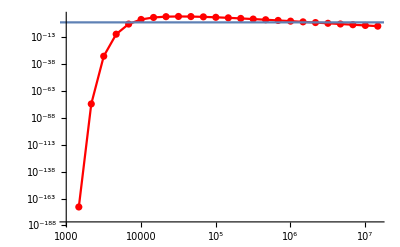

```mathematica
Show[ListLogLogPlot[{falist},PlotStyle-> Red, Mesh-> All,Joined->True],LogLogPlot[3,{fa,0.1,10^8}]]
```

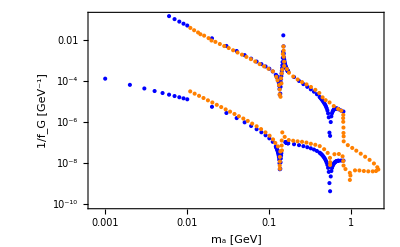

```mathematica
faprimemin=Import["./faprimemin.csv","Data"];
faprimemax=Import["./faprimemax.csv","Data"];
faexisting=Import["./existing.csv","Data"];
ListLogLogPlot[{falistmin,falistmax,faprimemin,faprimemax(*,faexisting*)},PlotStyle-> {Blue,Blue,Orange,Orange,Gray},Frame->True(*,Joined->True*),(*Mesh->Full,*)FrameLabel->{"m_a [GeV]","1/f_G [GeV^-1]"},ImageSize->400]
```

## Combining with GG-fusion

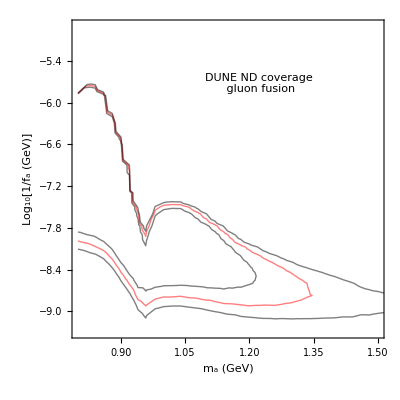

```mathematica
simulationresults=Import[NotebookDirectory[]<>"simulationresult.m"];
ListContourPlot[Flatten[Table[{#[[1]],Log[10,1/(4Pi^2#[[2]]*10^6)],Log[144/300#[[3]]]}&/@simulationresults[[i]],{i,1,Length[simulationresults]}],1],Contours->{0,Log[3],Log[10]},PlotRange->{{0.8,1.5},Automatic},ContourStyle->{Thick,Red},ContourShading->{None},InterpolationOrder->All,FrameLabel->{"m_a (GeV)","Log_10[1/f_a (GeV)]"},BaseStyle->16,ImageSize->400,Epilog->Inset["DUNE ND coverage\n gluon fusion",Scaled[{0.6,0.8}]]]
```

```mathematica
simulationresults
```

{{{0.8,0.0001,0.,0.,10,3.26543,0.172136,1.93533,0.106721,2.02567,0.113401},{0.8,0.0002,0.,0.,10,3.21581,0.233186,1.93172,0.118945,2.02175,0.133286},{0.8,0.0005,0.,0.,10,3.05814,0.22219,1.94363,0.118533,2.03656,0.132701},{0.8,0.001,0.,0.,10,3.06301,0.301535,1.94826,0.16258,2.03368,0.179525},{0.8,0.002,2.83478×10^-89,8.31514×10^-90,10,3.17196,0.221809,1.94924,0.115288,2.03589,0.127708},{0.8,0.005,-1.42505×10^-12,1.45699×10^-13,10,3.18297,0.252255,1.93293,0.138659,2.0253,0.148379},{0.8,0.008,-0.0061602,0.000344238,10,3.09788,0.343425,1.94053,0.180848,2.028,0.197642},{0.8,0.01,-1.62298,0.0871786,10,3.04707,0.231127,1.95722,0.123334,2.03211,0.134957},{0.8,0.02,1165.15,183.9,10,3.06259,0.228633,1.94851,0.116747,2.02996,0.131205},{0.8,0.05,75720.8,4481.95,10,3.08497,0.181867,1.95599,0.10095,2.03503,0.111055},{0.8,0.08,72339.8,4898.33,10,3.23871,0.351965,1.93403,0.179449,2.03288,0.208006},{0.8,0.1,56166.1,3213.29,10,3.00198,0.208422,1.9505,0.124898,2.03896,0.13214},{0.8,0.2,14249.8,1447.35,10,3.00687,0.229924,1.95967,0.12665,2.02765,0.144121},{0.8,0.5,752.049,83.6731,10,3.06664,0.197654,1.94908,0.114769,2.02813,0.12315},{0.8,0.8,128.518,17.9826,10,3.0723,0.274219,1.94687,0.157867,2.03155,0.169278},{0.8,1,53.0669,8.31182,10,3.10468,0.245161,1.94148,0.125214,2.02063,0.14465},{0.8,1.5,10.8766,1.72673,10,3.11446,0.310889,1.93711,0.157309,2.0215,0.176756},{0.8,2,3.7493,0.533064,10,3.25977,0.214242,1.92647,0.104922,2.01843,0.127941},{0.8,3,0.664137,0.0816298,10,3.02803,0.268353,1.95229,0.156518,2.02959,0.161853},{0.8,4,0.235613,0.0545501,10,3.2373,0.4801,1.94225,0.23297,2.02975,0.267668},{0.8,5,0.0892006,0.0139483,10,3.04528,0.300661,1.95111,0.148651,2.03936,0.172984},{0.8,6,0.0460667,0.00529125,10,3.16205,0.285931,1.94247,0.140255,2.02755,0.154218},{0.8,7,0.0250366,0.00224762,10,3.21698,0.208191,1.94386,0.0915099,2.02513,0.0997521},{0.8,8,0.0136539,0.00190315,10,3.10011,0.27206,1.94902,0.156201,2.03207,0.167318},{0.8,9,0.00928019,0.00163933,10,3.20027,0.3391,1.93618,0.177025,2.02624,0.198696},{0.8,10,0.00612465,0.000730117,10,3.21699,0.223599,1.93647,0.113291,2.02707,0.120728},{0.8,15,0.00111374,0.000108925,10,3.04401,0.146014,1.95216,0.0888687,2.03857,0.105763},{0.8,20,0.000351319,0.0000466974,10,3.07806,0.193391,1.95915,0.115916,2.03146,0.121683},{0.8,25,0.00014255,0.000018024,10,3.09432,0.230211,1.94128,0.127676,2.02664,0.137979},{0.8,30,0.0000724295,0.0000146126,10,3.11016,0.343069,1.94794,0.177803,2.03197,0.200396},{0.8,35,0.0000389228,4.36082×10^-6,10,3.23193,0.220726,1.93687,0.109298,2.01841,0.118749},{0.8,40,0.0000240845,3.34179×10^-6,10,3.21649,0.263721,1.93609,0.131944,2.02475,0.149315},{0.8,50,8.54885×10^-6,2.57666×10^-6,10,3.06285,0.411109,1.95001,0.230299,2.0374,0.257205}},{{0.82,0.0001,0.,0.,10,3.49327,0.318155,1.924,0.156147,2.00849,0.169799},{0.82,0.0002,0.,0.,10,3.48857,0.261425,1.92052,0.128726,2.00989,0.142526},{0.82,0.0005,0.,0.,10,3.77374,0.329166,1.89718,0.148787,1.98688,0.161283},{0.82,0.001,0.,0.,10,3.47315,0.3236,1.91684,0.136163,2.00339,0.155809},{0.82,0.002,2.90474×10^-103,7.60046×10^-104,10,3.4969,0.20211,1.91538,0.0979409,1.99785,0.10616},{0.82,0.005,-3.45442×10^-15,3.92129×10^-16,10,3.54816,0.431855,1.91987,0.213651,2.00679,0.230709},{0.82,0.008,-0.000235514,0.0000105617,10,3.52486,0.248671,1.91511,0.115324,2.00731,0.127653},{0.82,0.01,-0.0657712,0.00559602,10,3.39929,0.337159,1.93269,0.160591,2.01594,0.18498},{0.82,0.02,2479.64,89.7773,10,3.3756,0.21834,1.92588,0.104506,2.01133,0.110195},{0.82,0.05,74725.9,2883.04,10,3.53746,0.356442,1.91138,0.167584,1.99802,0.184419},{0.82,0.08,73335.5,4206.78,10,3.41418,0.0960108,1.92502,0.0377177,2.01037,0.0469285},{0.82,0.1,61286.4,4471.95,10,3.4919,0.395647,1.92516,0.185714,2.00744,0.207947},{0.82,0.2,17490.9,1661.03,10,3.58784,0.298162,1.9064,0.120131,2.00212,0.1437},{0.82,0.5,1036.33,146.235,10,3.55455,0.330592,1.91857,0.14654,2.01265,0.165659},{0.82,0.8,170.185,21.8879,10,3.56736,0.160771,1.91506,0.0725748,2.00142,0.0877221},{0.82,1,70.6295,10.1485,10,3.52494,0.294773,1.92055,0.126354,2.00288,0.151375},{0.82,1.5,15.2579,1.4763,10,3.62664,0.255304,1.90928,0.122014,1.99747,0.130868},{0.82,2,4.86373,0.581291,10,3.57588,0.171145,1.91366,0.0688044,1.9982,0.0832823},{0.82,3,0.915361,0.137955,10,3.43605,0.316998,1.93306,0.153839,2.012,0.169904},{0.82,4,0.299506,0.0256757,10,3.41401,0.209395,1.9307,0.105707,2.0224,0.115926},{0.82,5,0.114383,0.0213066,10,3.39585,0.315109,1.92427,0.167907,2.01302,0.181743},{0.82,6,0.0557861,0.00704266,10,3.52218,0.275261,1.91998,0.132356,1.99713,0.143693},{0.82,7,0.0332792,0.0029916,10,3.53961,0.1596,1.92283,0.0718103,2.01354,0.0728175},{0.82,8,0.018731,0.0028822,10,3.45289,0.295408,1.93193,0.136106,2.01868,0.153705},{0.82,9,0.0111442,0.00194972,10,3.44053,0.340256,1.92848,0.151197,2.01044,0.170182},{0.82,10,0.00786721,0.00121505,10,3.5168,0.209923,1.90741,0.0969259,2.00005,0.110865},{0.82,15,0.00161759,0.000194193,10,3.65118,0.284282,1.89809,0.12171,1.99258,0.133854},{0.82,20,0.000510097,0.000082107,10,3.61978,0.315621,1.90667,0.130816,1.99987,0.153026},{0.82,25,0.000182246,0.0000228457,10,3.45589,0.405762,1.92435,0.190967,1.99994,0.20681},{0.82,30,0.0000954579,0.000012993,10,3.47461,0.275578,1.92496,0.128695,2.01041,0.144926},{0.82,35,0.000053083,5.62762×10^-6,10,3.5616,0.303965,1.91539,0.135025,2.00212,0.145868},{0.82,40,0.0000300591,3.82469×10^-6,10,3.50528,0.207496,1.91077,0.0819744,2.00299,0.100115},{0.82,50,0.0000111007,1.73949×10^-6,10,3.28071,0.252878,1.93867,0.116065,2.01788,0.136866}},{{0.84,0.0001,0.,0.,10,3.92056,0.292821,1.89241,0.116514,1.98276,0.129986},{0.84,0.0002,0.,0.,10,3.84077,0.198209,1.89842,0.083779,1.98203,0.0928084},{0.84,0.0005,0.,0.,10,3.83506,0.213721,1.89578,0.0960181,1.98638,0.105802},{0.84,0.001,0.,0.,10,3.83827,0.170078,1.89538,0.0733776,1.97521,0.084203},{0.84,0.002,1.11912×10^-142,2.20296×10^-143,10,3.87021,0.374269,1.88576,0.149585,1.98327,0.168965},{0.84,0.005,-2.16661×10^-22,4.5756×10^-23,10,3.70158,0.448797,1.90123,0.191478,1.99266,0.216883},{0.84,0.008,-4.91569×10^-8,8.80668×10^-9,10,3.95593,0.372897,1.87961,0.154356,1.96685,0.171151},{0.84,0.01,0.000591544,0.0000561958,10,3.92701,0.319489,1.89428,0.134969,1.98163,0.14733},{0.84,0.02,863.368,41.4372,10,3.76084,0.291734,1.90411,0.129602,1.99073,0.145181},{0.84,0.05,50929.,2890.14,10,3.90109,0.200274,1.8978,0.0846375,1.98813,0.0964954},{0.84,0.08,63690.9,3473.05,10,3.74919,0.225184,1.90419,0.105818,1.99379,0.121229},{0.84,0.1,57469.4,2551.02,10,3.93034,0.304348,1.89715,0.116945,1.98798,0.142129},{0.84,0.2,18191.8,1927.97,10,3.68463,0.339319,1.90009,0.138842,1.98288,0.158295},{0.84,0.5,1328.75,169.577,10,3.75958,0.283789,1.90309,0.118872,1.99555,0.136693},{0.84,0.8,254.768,42.7071,10,3.87505,0.449991,1.89567,0.192577,1.98851,0.21485},{0.84,1,96.5783,14.6543,10,3.66908,0.294522,1.90839,0.132949,1.98688,0.149262},{0.84,1.5,20.552,3.44323,10,3.71293,0.312103,1.90189,0.135166,1.98292,0.153792},{0.84,2,6.8875,0.531678,10,3.77281,0.233348,1.90227,0.102702,1.98668,0.109002},{0.84,3,1.43367,0.143147,10,3.77471,0.125658,1.90109,0.0667728,1.99046,0.0754327},{0.84,4,0.460323,0.0642545,10,3.93202,0.255498,1.8925,0.100454,1.98107,0.114461},{0.84,5,0.199341,0.0251154,10,4.03909,0.200038,1.88575,0.0724583,1.98052,0.0832433},{0.84,6,0.0845193,0.0123912,10,3.64219,0.308618,1.91606,0.147733,2.00039,0.16013},{0.84,7,0.0461822,0.0104667,10,3.62305,0.293725,1.90937,0.131691,1.99756,0.154309},{0.84,8,0.0290678,0.00380294,10,3.96592,0.293888,1.89401,0.11773,1.98231,0.133504},{0.84,9,0.0165791,0.00260125,10,3.79503,0.387262,1.89062,0.162095,1.97358,0.183699},{0.84,10,0.0112211,0.000804487,10,3.88121,0.162905,1.89066,0.0646387,1.97271,0.0731859},{0.84,15,0.00212662,0.000178658,10,3.77925,0.165787,1.90642,0.0786126,1.98373,0.0809707},{0.84,20,0.000705313,0.0000969704,10,3.79572,0.355361,1.89394,0.150866,1.98104,0.169971},{0.84,25,0.000292456,0.0000606534,10,3.72619,0.402992,1.90193,0.17406,1.99386,0.200704},{0.84,30,0.000146821,0.0000242859,10,3.84298,0.314271,1.89587,0.138924,1.99393,0.157365},{0.84,35,0.0000740872,8.93848×10^-6,10,3.76253,0.208342,1.90383,0.0886937,1.98712,0.102886},{0.84,40,0.0000458487,5.14541×10^-6,10,3.83181,0.228203,1.90423,0.0949698,1.99124,0.102603},{0.84,50,0.0000195804,3.59977×10^-6,10,4.02143,0.348342,1.87634,0.13796,1.97225,0.160986}},{{0.86,0.0001,0.,0.,10,4.14517,0.305513,1.87514,0.113585,1.96802,0.127582},{0.86,0.0002,0.,0.,10,4.13333,0.216243,1.87995,0.0826094,1.96644,0.0953045},{0.86,0.0005,0.,0.,10,4.17771,0.282325,1.85873,0.115857,1.95497,0.125832},{0.86,0.001,0.,0.,10,4.10644,0.319046,1.87867,0.122399,1.96365,0.141135},{0.86,0.002,-2.21115×10^-256,0.,10,3.94079,0.487675,1.88498,0.198035,1.96671,0.222908},{0.86,0.005,-6.21159×10^-42,9.44397×10^-42,10,4.1414,0.294105,1.86318,0.109614,1.96025,0.132522},{0.86,0.008,2.5398×10^-15,2.07243×10^-16,10,4.11232,0.364722,1.87496,0.138863,1.96426,0.158132},{0.86,0.01,5.06297×10^-9,2.74259×10^-10,10,4.14864,0.218976,1.87968,0.0845402,1.98052,0.0910361},{0.86,0.02,20.3933,1.214,10,4.14712,0.315082,1.85749,0.111842,1.94798,0.127589},{0.86,0.05,17982.,303.772,10,4.22092,0.264322,1.87385,0.090578,1.96797,0.10647},{0.86,0.08,38912.9,2470.91,10,4.20656,0.419136,1.86914,0.150592,1.95494,0.16796},{0.86,0.1,41110.8,2266.25,10,4.03185,0.214204,1.88777,0.0769278,1.96657,0.0857035},{0.86,0.2,20795.4,1450.48,10,4.31848,0.251383,1.85999,0.10403,1.95721,0.114301},{0.86,0.5,2071.39,242.436,10,4.16033,0.300296,1.87123,0.119948,1.95905,0.134635},{0.86,0.8,418.281,61.7438,10,4.22954,0.368409,1.8635,0.129833,1.94792,0.148339},{0.86,1,190.526,28.0605,10,4.18487,0.384432,1.87837,0.134035,1.97136,0.155549},{0.86,1.5,40.674,4.58363,10,4.11358,0.322685,1.86828,0.115869,1.96288,0.130713},{0.86,2,12.3459,1.96423,10,4.14562,0.371308,1.87554,0.126529,1.95785,0.149367},{0.86,3,2.59952,0.294689,10,4.10993,0.276043,1.8836,0.102881,1.9713,0.116863},{0.86,4,0.778516,0.136922,10,4.02484,0.297619,1.88908,0.109609,1.96954,0.125803},{0.86,5,0.351097,0.0377284,10,4.1253,0.236182,1.87002,0.0882217,1.95781,0.101872},{0.86,6,0.172989,0.0249662,10,4.28484,0.301233,1.86691,0.106352,1.9572,0.123436},{0.86,7,0.0887794,0.00995164,10,4.05067,0.335803,1.87687,0.132815,1.96519,0.146438},{0.86,8,0.0526373,0.00661838,10,4.23656,0.305137,1.86127,0.111504,1.95398,0.1289},{0.86,9,0.0328969,0.00392025,10,4.09766,0.314757,1.87758,0.120224,1.96708,0.133181},{0.86,10,0.0219995,0.00272719,10,4.219,0.221139,1.87064,0.0760361,1.96079,0.0857682},{0.86,15,0.00407697,0.00057796,10,4.11714,0.288641,1.88156,0.109733,1.96317,0.127487},{0.86,20,0.00129235,0.000165276,10,4.05226,0.273066,1.8758,0.108457,1.96109,0.127801},{0.86,25,0.000584838,0.000106304,10,4.18896,0.448059,1.86614,0.15933,1.96393,0.188229},{0.86,30,0.000266942,0.0000349064,10,4.10776,0.327986,1.88425,0.12655,1.9759,0.141703},{0.86,35,0.000148103,0.0000210848,10,4.25531,0.313601,1.86225,0.107606,1.95564,0.125063},{0.86,40,0.0000926475,9.23869×10^-6,10,4.4452,0.190774,1.86208,0.071582,1.95537,0.0822845},{0.86,50,0.0000353933,6.30286×10^-6,10,4.16867,0.441157,1.8684,0.167935,1.9604,0.1922}},{{0.88,0.0001,0.,0.,10,4.57067,0.311987,1.8492,0.106579,1.94465,0.121693},{0.88,0.0002,0.,0.,10,4.50782,0.351674,1.84425,0.111403,1.93365,0.131753},{0.88,0.0005,0.,0.,10,4.63076,0.229497,1.83776,0.0712315,1.94255,0.0849338},{0.88,0.001,0.,0.,10,4.47294,0.412193,1.84577,0.134611,1.93729,0.158822},{0.88,0.002,0.,0.,10,4.47282,0.194385,1.84054,0.0760539,1.93096,0.0808926},{0.88,0.005,-1.56854×10^-124,3.98076×10^-125,10,4.44591,0.343408,1.84519,0.121321,1.94127,0.136611},{0.88,0.008,-5.01817×10^-49,1.89363×10^-49,10,4.49622,0.21947,1.85118,0.0736991,1.94232,0.0829988},{0.88,0.01,2.16347×10^-31,5.63364×10^-32,10,4.33034,0.226764,1.86093,0.0878709,1.94677,0.0965511},{0.88,0.02,2.20533×10^-6,1.35108×10^-7,10,4.37365,0.251765,1.85481,0.0838076,1.9462,0.0986549},{0.88,0.05,535.379,20.0274,10,4.58619,0.353387,1.85197,0.123592,1.94205,0.143643},{0.88,0.08,5447.13,209.901,10,4.40708,0.317994,1.85244,0.101085,1.94963,0.125211},{0.88,0.1,9262.27,373.828,10,4.44672,0.287165,1.85522,0.103023,1.94705,0.118096},{0.88,0.2,14420.3,604.527,10,4.71389,0.342688,1.82381,0.107286,1.9239,0.130639},{0.88,0.5,3405.91,274.191,10,4.49142,0.287329,1.84235,0.101424,1.9357,0.106771},{0.88,0.8,925.35,101.104,10,4.4159,0.359416,1.85741,0.116811,1.94493,0.133136},{0.88,1,443.479,55.7533,10,4.42004,0.374932,1.83958,0.127476,1.93523,0.144078},{0.88,1.5,103.791,10.7225,10,4.24008,0.22558,1.86941,0.0901204,1.95608,0.0995086},{0.88,2,39.1124,5.52975,10,4.55477,0.493718,1.83853,0.160896,1.9313,0.18067},{0.88,3,8.30351,1.1872,10,4.46546,0.353712,1.84902,0.13035,1.94308,0.147454},{0.88,4,2.62269,0.23993,10,4.36003,0.276557,1.85672,0.0894257,1.94892,0.105299},{0.88,5,1.13644,0.156758,10,4.54985,0.271621,1.84014,0.0862331,1.9353,0.103779},{0.88,6,0.476743,0.0620418,10,4.16274,0.262302,1.87756,0.0936986,1.96035,0.110537},{0.88,7,0.272306,0.0627417,10,4.36483,0.524116,1.86175,0.18689,1.94636,0.214891},{0.88,8,0.170569,0.0213902,10,4.51256,0.413558,1.85203,0.145073,1.94511,0.162097},{0.88,9,0.100454,0.0157971,10,4.44117,0.412093,1.86177,0.147008,1.94904,0.167377},{0.88,10,0.0725829,0.00947696,10,4.55828,0.310821,1.83634,0.0948597,1.93432,0.113913},{0.88,15,0.0133564,0.0019139,10,4.46615,0.418668,1.8519,0.147756,1.93723,0.164421},{0.88,20,0.00426349,0.000492322,10,4.5148,0.28764,1.84548,0.0906419,1.93273,0.102372},{0.88,25,0.00177574,0.000346535,10,4.40091,0.513828,1.8489,0.189467,1.94329,0.218569},{0.88,30,0.000744962,0.000113253,10,4.23178,0.311419,1.86585,0.105332,1.94428,0.118441},{0.88,35,0.000472272,0.0000572254,10,4.55778,0.420872,1.85191,0.146353,1.9443,0.163519},{0.88,40,0.000238961,0.0000390079,10,4.20544,0.252306,1.86871,0.0981768,1.94638,0.114489},{0.88,50,0.000106922,0.0000173031,10,4.32367,0.41132,1.86216,0.15124,1.94809,0.169999}},{{0.9,0.0001,0.,0.,10,4.88419,0.413374,1.81605,0.129235,1.91475,0.1458},{0.9,0.0002,0.,0.,10,4.81886,0.186054,1.81783,0.0561425,1.91513,0.0694798},{0.9,0.0005,0.,0.,10,4.71148,0.334371,1.83778,0.101214,1.93381,0.119954},{0.9,0.001,0.,0.,10,4.75822,0.387656,1.82172,0.1151,1.9272,0.139365},{0.9,0.002,0.,0.,10,4.7846,0.300389,1.82367,0.0948117,1.91724,0.106807},{0.9,0.005,0.,0.,10,4.74232,0.365367,1.829,0.123977,1.9195,0.136843},{0.9,0.008,-4.02064×10^-280,0.,10,4.70526,0.333495,1.83427,0.106188,1.92206,0.124683},{0.9,0.01,-1.41452×10^-179,0.,10,4.79759,0.404513,1.82035,0.121667,1.91814,0.13966},{0.9,0.02,-6.65475×10^-46,4.13025×10^-46,10,4.69337,0.498905,1.83573,0.156571,1.93537,0.175802},{0.9,0.05,2.89555×10^-6,1.31624×10^-7,10,4.69614,0.376007,1.83542,0.122805,1.93003,0.14651},{0.9,0.08,0.960636,0.0394393,10,4.64336,0.357169,1.82978,0.108213,1.92266,0.124693},{0.9,0.1,20.6682,0.814542,10,4.81089,0.473496,1.82103,0.143578,1.91375,0.166488},{0.9,0.2,1202.83,27.4347,10,4.81936,0.404014,1.81169,0.121488,1.91112,0.138925},{0.9,0.5,2510.63,129.137,10,4.61166,0.419315,1.83408,0.147577,1.92176,0.164479},{0.9,0.8,1417.41,91.7325,10,4.72457,0.307957,1.8296,0.0964875,1.92316,0.115919},{0.9,1,886.668,65.4146,10,4.52724,0.242331,1.84818,0.0827417,1.93351,0.0913836},{0.9,1.5,335.278,19.6229,10,4.65834,0.133782,1.82941,0.0439287,1.91211,0.0520321},{0.9,2,149.707,18.3636,10,4.80685,0.462756,1.8264,0.13633,1.91523,0.15449},{0.9,3,38.2105,3.74236,10,4.73541,0.231561,1.82932,0.0805575,1.9204,0.0920551},{0.9,4,13.733,1.52588,10,4.6482,0.526118,1.83612,0.159448,1.93113,0.178599},{0.9,5,6.55897,0.742772,10,4.89529,0.346698,1.81865,0.11845,1.92286,0.133343},{0.9,6,3.0277,0.276738,10,4.77722,0.183859,1.82417,0.0602607,1.91833,0.0685563},{0.9,7,1.57326,0.21002,10,4.56855,0.29811,1.84572,0.0935651,1.93853,0.112244},{0.9,8,0.970011,0.0916017,10,4.75185,0.301572,1.82537,0.0947073,1.92259,0.101575},{0.9,9,0.616242,0.0862832,10,4.83416,0.417561,1.81026,0.127271,1.91116,0.152503},{0.9,10,0.371127,0.0450979,10,4.58744,0.313916,1.84755,0.105492,1.93206,0.118042},{0.9,15,0.0819864,0.0124717,10,4.8107,0.453924,1.82392,0.14223,1.92241,0.167589},{0.9,20,0.0258775,0.00321291,10,4.81301,0.36456,1.81578,0.109019,1.909,0.119474},{0.9,25,0.0105875,0.000846374,10,4.75363,0.306805,1.82418,0.10087,1.91862,0.110918},{0.9,30,0.00479888,0.00088211,10,4.56172,0.300863,1.83954,0.0961291,1.92884,0.119652},{0.9,35,0.0027157,0.000224425,10,4.8602,0.159366,1.82066,0.0506883,1.90781,0.0554119},{0.9,40,0.00169127,0.000186057,10,4.89051,0.219447,1.81866,0.073342,1.91401,0.076588},{0.9,50,0.000647108,0.0000590548,10,4.67898,0.240716,1.83352,0.0843476,1.92672,0.087243}},{{0.92,0.0001,0.,0.,10,5.13469,0.340954,1.80433,0.100675,1.90417,0.115992},{0.92,0.0002,0.,0.,10,4.89314,0.335048,1.81369,0.0954075,1.91171,0.113967},{0.92,0.0005,0.,0.,10,5.04363,0.371605,1.81085,0.101689,1.90419,0.122748},{0.92,0.001,0.,0.,10,4.89322,0.351625,1.81713,0.103021,1.90887,0.121516},{0.92,0.002,0.,0.,10,5.00413,0.260226,1.81067,0.0735712,1.90664,0.0866631},{0.92,0.005,0.,0.,10,5.02338,0.430501,1.80285,0.130397,1.90258,0.147329},{0.92,0.008,0.,0.,10,4.89258,0.396766,1.82063,0.114154,1.91529,0.1356},{0.92,0.01,0.,0.,10,4.86602,0.321837,1.82017,0.104446,1.9079,0.117001},{0.92,0.02,-1.90534×10^-242,0.,10,4.85466,0.554093,1.81016,0.163251,1.89763,0.190343},{0.92,0.05,2.75803×10^-40,7.61861×10^-41,10,5.06688,0.362011,1.80163,0.10602,1.89779,0.122871},{0.92,0.08,1.49756×10^-15,1.10952×10^-16,10,5.07532,0.406769,1.79451,0.118329,1.89061,0.13093},{0.92,0.1,1.0159×10^-9,4.30424×10^-11,10,4.9518,0.287699,1.81207,0.0919174,1.90563,0.109257},{0.92,0.2,0.656453,0.049377,10,5.04795,0.304893,1.80131,0.0779879,1.89537,0.08827},{0.92,0.5,288.539,8.76022,10,5.0482,0.444107,1.80572,0.128576,1.90406,0.148168},{0.92,0.8,533.93,24.5839,10,5.07129,0.369678,1.80073,0.103922,1.89291,0.124775},{0.92,1,541.387,29.1748,10,4.96685,0.423077,1.80861,0.122972,1.89561,0.139294},{0.92,1.5,375.937,27.403,10,5.01798,0.483824,1.79139,0.135044,1.89144,0.162791},{0.92,2,234.354,16.1213,10,4.90442,0.360523,1.81324,0.103559,1.9114,0.124543},{0.92,3,101.983,8.99254,10,5.07692,0.305854,1.80231,0.0847677,1.89662,0.0956557},{0.92,4,45.6136,6.6478,10,4.95737,0.4594,1.81819,0.13905,1.91271,0.160938},{0.92,5,23.4182,3.06817,10,5.04244,0.421492,1.80325,0.1323,1.91017,0.143933},{0.92,6,12.7399,1.90813,10,5.03505,0.505139,1.80063,0.153137,1.90255,0.175325},{0.92,7,7.50094,0.83,10,5.05335,0.389102,1.80224,0.117048,1.90546,0.131069},{0.92,8,4.14505,0.622821,10,4.71158,0.403159,1.82331,0.132619,1.91073,0.152527},{0.92,9,3.10069,0.393412,10,5.18386,0.347727,1.7886,0.0904062,1.89248,0.109253},{0.92,10,1.8908,0.211859,10,4.91197,0.324418,1.81599,0.101235,1.90555,0.116082},{0.92,15,0.432535,0.0376246,10,4.94257,0.234147,1.80343,0.0689194,1.90407,0.07881},{0.92,20,0.130885,0.0286636,10,4.8958,0.381725,1.80858,0.12059,1.90115,0.149349},{0.92,25,0.0559027,0.00991211,10,4.89474,0.334722,1.8085,0.109296,1.9045,0.132581},{0.92,30,0.0281934,0.00202398,10,5.07321,0.142438,1.80327,0.0426382,1.89918,0.0427872},{0.92,35,0.0154263,0.00229704,10,5.09534,0.37587,1.79878,0.115442,1.89835,0.128894},{0.92,40,0.00856922,0.00132594,10,4.84259,0.465494,1.81598,0.126621,1.9081,0.144199},{0.92,50,0.00347533,0.000345979,10,4.89539,0.248594,1.80716,0.0741659,1.89771,0.0881153}},{{0.94,0.0001,0.,0.,10,5.13362,0.377147,1.793,0.109523,1.89015,0.12869},{0.94,0.0002,0.,0.,10,5.40047,0.27462,1.77102,0.0724732,1.87507,0.0806349},{0.94,0.0005,0.,0.,10,5.30065,0.498381,1.77527,0.131307,1.87591,0.157429},{0.94,0.001,0.,0.,10,5.35452,0.366426,1.77609,0.0992079,1.87556,0.113727},{0.94,0.002,0.,0.,10,5.22387,0.420662,1.78468,0.115524,1.87952,0.133047},{0.94,0.005,0.,0.,10,5.29776,0.329684,1.78127,0.0883769,1.88446,0.103344},{0.94,0.008,0.,0.,10,5.02621,0.413631,1.79282,0.124094,1.87922,0.138691},{0.94,0.01,0.,0.,10,5.20441,0.316613,1.79355,0.0774447,1.88847,0.099808},{0.94,0.02,0.,0.,10,5.26396,0.402093,1.77112,0.104351,1.87458,0.126044},{0.94,0.05,0.,0.,10,5.21143,0.281927,1.77768,0.0785584,1.87049,0.0875438},{0.94,0.08,-4.613×10^-182,0.,10,5.38488,0.349276,1.77605,0.0918207,1.87858,0.106062},{0.94,0.1,-1.80433×10^-117,7.08769×10^-118,10,4.93692,0.299795,1.80565,0.0987866,1.8954,0.108779},{0.94,0.2,8.64685×10^-31,9.2717×10^-32,10,5.23369,0.365072,1.78902,0.096779,1.8791,0.112859},{0.94,0.5,0.0000834394,2.88917×10^-6,10,5.03307,0.401512,1.80087,0.121111,1.89387,0.139374},{0.94,0.8,0.399278,0.0232745,10,5.14877,0.320731,1.78643,0.0875667,1.88749,0.108283},{0.94,1,2.82474,0.159415,10,5.11048,0.387715,1.7912,0.10219,1.89192,0.121159},{0.94,1.5,18.368,0.232659,10,5.33562,0.242999,1.77746,0.0614298,1.86992,0.0700724},{0.94,2,34.2806,1.25104,10,5.15264,0.31768,1.79014,0.0843238,1.8864,0.101538},{0.94,3,47.1146,1.86242,10,5.2373,0.373161,1.79114,0.103224,1.8876,0.117719},{0.94,4,42.8525,2.76226,10,4.97807,0.341386,1.79653,0.0966283,1.88577,0.112786},{0.94,5,34.784,1.91892,10,5.10765,0.397717,1.79032,0.120326,1.8883,0.131451},{0.94,6,26.9358,2.05666,10,5.10609,0.413705,1.79676,0.116291,1.88733,0.133888},{0.94,7,20.4357,0.737881,10,5.13457,0.204048,1.79645,0.054621,1.88301,0.0645361},{0.94,8,15.6021,1.18341,10,5.12321,0.274219,1.79069,0.08292,1.88525,0.0925761},{0.94,9,12.3854,0.822213,10,5.27341,0.278363,1.78355,0.0857763,1.88197,0.0981127},{0.94,10,9.38946,0.853982,10,5.18911,0.430025,1.78338,0.113407,1.88155,0.131265},{0.94,15,2.97389,0.332197,10,5.19335,0.325981,1.7842,0.0895809,1.88128,0.113616},{0.94,20,1.10627,0.101523,10,4.96273,0.318775,1.79638,0.0922411,1.88748,0.101329},{0.94,25,0.532987,0.0656736,10,5.09643,0.35511,1.79088,0.101111,1.88568,0.120919},{0.94,30,0.27394,0.0320408,10,5.14286,0.316896,1.78995,0.0830812,1.88268,0.103838},{0.94,35,0.161571,0.0174178,10,5.23847,0.365358,1.78305,0.0937665,1.88112,0.106574},{0.94,40,0.0982342,0.00614179,10,5.2761,0.175733,1.7828,0.0507388,1.88072,0.0579339},{0.94,50,0.0382512,0.00434651,10,5.04448,0.288106,1.79187,0.0793604,1.88051,0.095327}},{{0.958,0.0001,0.,0.,10,5.41882,0.433919,1.75438,0.110874,1.8638,0.130435},{0.958,0.0002,0.,0.,10,5.38036,0.291994,1.77032,0.073498,1.86481,0.0888934},{0.958,0.0005,0.,0.,10,5.11431,0.360041,1.77949,0.106759,1.87064,0.125591},{0.958,0.001,0.,0.,10,5.5777,0.361577,1.75432,0.0898769,1.8524,0.107885},{0.958,0.002,0.,0.,10,5.216,0.347325,1.77925,0.0978094,1.87549,0.119617},{0.958,0.005,0.,0.,10,5.41894,0.243805,1.76371,0.0679278,1.86787,0.0761339},{0.958,0.008,0.,0.,10,5.15301,0.294043,1.77911,0.0820899,1.87428,0.0957449},{0.958,0.01,0.,0.,10,5.29808,0.474646,1.76635,0.132763,1.85522,0.148122},{0.958,0.02,0.,0.,10,5.49064,0.279915,1.75791,0.0835659,1.85576,0.0906222},{0.958,0.05,0.,0.,10,5.34513,0.291438,1.76942,0.073652,1.85997,0.0919609},{0.958,0.08,0.,0.,10,5.43742,0.257798,1.76364,0.071113,1.8599,0.0800969},{0.958,0.1,0.,0.,10,5.34409,0.401533,1.76661,0.109937,1.86546,0.12546},{0.958,0.2,-1.6496×10^-99,3.45857×10^-100,10,5.2313,0.336925,1.77767,0.0896307,1.87384,0.104606},{0.958,0.5,2.38374×10^-17,1.81209×10^-18,10,5.31535,0.363398,1.77164,0.0957228,1.86452,0.109464},{0.958,0.8,4.63849×10^-7,2.21242×10^-8,10,5.16306,0.17223,1.77578,0.0566643,1.87295,0.0649472},{0.958,1,0.000241501,6.32145×10^-6,10,5.34493,0.402543,1.77603,0.1141,1.87157,0.129066},{0.958,1.5,0.166239,0.00894594,10,5.51376,0.274114,1.74916,0.0739998,1.8556,0.0822293},{0.958,2,1.55193,0.0729641,10,5.37137,0.232323,1.77328,0.0679049,1.86521,0.0762248},{0.958,3,7.43279,0.209771,10,5.34575,0.335167,1.7646,0.0888745,1.85643,0.105363},{0.958,4,12.1521,0.479303,10,5.54709,0.399812,1.76447,0.105481,1.85509,0.119032},{0.958,5,14.4186,0.932747,10,5.39292,0.646237,1.76292,0.165989,1.86309,0.200715},{0.958,6,14.68,0.939186,10,5.21519,0.381143,1.77118,0.0944409,1.86788,0.116853},{0.958,7,14.0631,0.842323,10,5.48978,0.321161,1.75956,0.076799,1.8569,0.0886064},{0.958,8,12.7572,0.927277,10,5.47841,0.301358,1.75356,0.0828161,1.86261,0.10446},{0.958,9,10.711,0.549258,10,5.16281,0.219789,1.77876,0.0631309,1.87473,0.0790064},{0.958,10,9.82881,0.485141,10,5.4122,0.348869,1.75938,0.0906586,1.86122,0.106689},{0.958,15,4.43263,0.24992,10,5.14611,0.278249,1.7918,0.0730061,1.87963,0.0838129},{0.958,20,2.17152,0.203181,10,5.16676,0.324508,1.78183,0.100718,1.86941,0.116193},{0.958,25,1.21872,0.113232,10,5.36052,0.399701,1.76738,0.104166,1.865,0.119383},{0.958,30,0.654979,0.0815285,10,5.16751,0.377522,1.77617,0.101292,1.86724,0.121255},{0.958,35,0.435282,0.0335059,10,5.52047,0.285959,1.75355,0.0669488,1.85837,0.0837968},{0.958,40,0.254629,0.0199046,10,5.26249,0.284174,1.77139,0.0756434,1.86591,0.0860618},{0.958,50,0.119317,0.0127741,10,5.25152,0.511008,1.77589,0.142867,1.87566,0.158142}},{{0.96,0.0001,0.,0.,10,5.32863,0.328523,1.77448,0.0968869,1.87365,0.110862},{0.96,0.0002,0.,0.,10,5.43869,0.318981,1.7583,0.0868065,1.86248,0.0983297},{0.96,0.0005,0.,0.,10,5.23603,0.294025,1.77401,0.0852098,1.86116,0.0913945},{0.96,0.001,0.,0.,10,5.41262,0.288038,1.76567,0.0799342,1.87259,0.0886701},{0.96,0.002,0.,0.,10,5.28267,0.333367,1.77023,0.0854661,1.86999,0.104102},{0.96,0.005,0.,0.,10,5.60162,0.283493,1.75225,0.0698832,1.85912,0.0821328},{0.96,0.008,0.,0.,10,5.38771,0.253838,1.76094,0.066423,1.86346,0.0676634},{0.96,0.01,0.,0.,10,5.5571,0.251517,1.75881,0.0687192,1.85373,0.0775318},{0.96,0.02,0.,0.,10,5.43657,0.41222,1.75767,0.109966,1.86246,0.130868},{0.96,0.05,0.,0.,10,5.36897,0.35059,1.75887,0.0904818,1.8596,0.1043},{0.96,0.08,0.,0.,10,5.45335,0.525614,1.76727,0.141825,1.86449,0.16706},{0.96,0.1,-1.30739×10^-305,0.,10,5.48669,0.354846,1.75308,0.0954185,1.85813,0.107077},{0.96,0.2,-3.24752×10^-79,3.43056×10^-79,10,5.29535,0.362605,1.76851,0.0968328,1.86601,0.115539},{0.96,0.5,9.27401×10^-14,3.90124×10^-15,10,5.23456,0.371242,1.77045,0.0955471,1.86204,0.114215},{0.96,0.8,0.0000231357,8.42946×10^-7,10,5.40516,0.332942,1.7731,0.0898623,1.86929,0.101556},{0.96,1,0.00375397,0.000154804,10,5.43696,0.40065,1.75899,0.103483,1.85687,0.122202},{0.96,1.5,0.641011,0.0284584,10,5.36935,0.285382,1.77835,0.0796782,1.87237,0.0895785},{0.96,2,3.61797,0.130513,10,5.4709,0.374039,1.75452,0.102608,1.8494,0.120911},{0.96,3,12.2927,0.58356,10,5.43701,0.460604,1.76145,0.120687,1.85996,0.135589},{0.96,4,17.1996,0.635082,10,5.61488,0.384622,1.75318,0.102297,1.86162,0.124839},{0.96,5,19.2974,0.617415,10,5.38937,0.242322,1.76883,0.0710847,1.85856,0.0751388},{0.96,6,17.3497,1.06227,10,5.21574,0.399268,1.7784,0.115763,1.87491,0.131234},{0.96,7,16.1258,1.0718,10,5.34551,0.42492,1.75882,0.121271,1.859,0.139306},{0.96,8,14.0974,1.14606,10,5.35697,0.44413,1.7654,0.123194,1.86096,0.140982},{0.96,9,11.8853,0.781308,10,5.34241,0.246264,1.76813,0.0762958,1.86462,0.0817359},{0.96,10,10.5133,0.68761,10,5.49253,0.273709,1.76037,0.0724259,1.85936,0.0834181},{0.96,15,4.34741,0.306179,10,5.30523,0.252713,1.77175,0.0756889,1.86812,0.0905833},{0.96,20,2.06115,0.172586,10,5.3153,0.377144,1.77056,0.0956443,1.86368,0.112898},{0.96,25,1.0572,0.0773958,10,5.31774,0.191825,1.76405,0.052566,1.86761,0.0633974},{0.96,30,0.567431,0.0589777,10,5.25383,0.314079,1.77055,0.0794136,1.8702,0.0989667},{0.96,35,0.343513,0.0366117,10,5.27767,0.356763,1.77535,0.103411,1.86791,0.116263},{0.96,40,0.210748,0.0236434,10,5.28331,0.306228,1.7645,0.0922899,1.86076,0.102827},{0.96,50,0.098538,0.00905956,10,5.39615,0.250308,1.76795,0.064401,1.86857,0.0777307}},{{0.98,0.0001,0.,0.,10,5.62982,0.420672,1.74171,0.105807,1.83993,0.122319},{0.98,0.0002,0.,0.,10,5.6308,0.32743,1.73869,0.0814021,1.84088,0.0983824},{0.98,0.0005,0.,0.,10,5.4568,0.49343,1.74525,0.119113,1.8441,0.144251},{0.98,0.001,0.,0.,10,5.47911,0.404363,1.74716,0.106873,1.84591,0.113147},{0.98,0.002,0.,0.,10,5.55515,0.512986,1.7407,0.129335,1.84152,0.153192},{0.98,0.005,0.,0.,10,5.55753,0.46985,1.74208,0.124943,1.83607,0.146327},{0.98,0.008,0.,0.,10,5.49746,0.28319,1.74868,0.0739593,1.84781,0.0801794},{0.98,0.01,0.,0.,10,5.6395,0.435064,1.73283,0.100342,1.84061,0.114083},{0.98,0.02,0.,0.,10,5.49912,0.341504,1.74687,0.0930125,1.84534,0.102432},{0.98,0.05,0.,0.,10,5.36685,0.334673,1.76008,0.0867937,1.85352,0.111346},{0.98,0.08,-1.89837×10^-166,0.,10,5.60469,0.390929,1.7452,0.0954063,1.84123,0.112359},{0.98,0.1,-6.61612×10^-108,7.41761×10^-108,10,5.13569,0.362549,1.7783,0.0988413,1.86897,0.112346},{0.98,0.2,6.67656×10^-28,6.52361×10^-29,10,5.42964,0.339725,1.75122,0.0919716,1.8454,0.103647},{0.98,0.5,0.000338018,0.0000167237,10,5.51292,0.321732,1.75056,0.0835082,1.84521,0.0955148},{0.98,0.8,0.789815,0.0428193,10,5.52457,0.370747,1.75117,0.0971623,1.84778,0.11508},{0.98,1,4.62955,0.138411,10,5.69618,0.398318,1.73356,0.0999783,1.82833,0.111461},{0.98,1.5,25.347,0.663147,10,5.6085,0.297634,1.74041,0.0751932,1.83975,0.0882235},{0.98,2,45.4605,2.08508,10,5.42417,0.33208,1.74672,0.0890243,1.8447,0.103815},{0.98,3,58.1071,3.0088,10,5.67387,0.430141,1.73658,0.102413,1.83544,0.120627},{0.98,4,51.0074,3.77245,10,5.55065,0.339293,1.74041,0.0758444,1.836,0.0909511},{0.98,5,39.1012,2.18957,10,5.65724,0.290617,1.75014,0.07281,1.85102,0.0855544},{0.98,6,29.1557,1.93576,10,5.40506,0.381174,1.75842,0.105318,1.85015,0.122668},{0.98,7,21.6793,2.42547,10,5.4598,0.503373,1.7587,0.127009,1.85616,0.150711},{0.98,8,17.2672,0.73378,10,5.74256,0.175376,1.72557,0.0413268,1.82902,0.0566467},{0.98,9,12.5953,1.27558,10,5.54545,0.401641,1.75151,0.1042,1.85161,0.116836},{0.98,10,10.0825,0.792597,10,5.76425,0.330175,1.73085,0.0869349,1.84057,0.102597},{0.98,15,2.88086,0.268657,10,5.53207,0.334147,1.73982,0.0829748,1.83526,0.0886167},{0.98,20,1.11424,0.119802,10,5.50186,0.315643,1.74199,0.0728571,1.84638,0.0923764},{0.98,25,0.52917,0.0460352,10,5.60394,0.211424,1.74685,0.061437,1.84776,0.0700062},{0.98,30,0.266913,0.030595,10,5.56234,0.378115,1.73361,0.100894,1.84026,0.111142},{0.98,35,0.152949,0.0236246,10,5.64516,0.541337,1.72827,0.133895,1.83493,0.157434},{0.98,40,0.0820673,0.0117469,10,5.47582,0.281967,1.74375,0.0749584,1.83551,0.0931349},{0.98,50,0.0360227,0.00567885,10,5.37707,0.525595,1.74931,0.126727,1.84707,0.152929}},{{1.,0.0001,0.,0.,10,5.74283,0.416476,1.71514,0.103336,1.81652,0.115326},{1.,0.0002,0.,0.,10,5.79758,0.295556,1.71627,0.0649862,1.81741,0.0821301},{1.,0.0005,0.,0.,10,5.46816,0.229878,1.74362,0.0685467,1.83798,0.0715814},{1.,0.001,0.,0.,10,5.56769,0.409284,1.72688,0.118035,1.83057,0.130148},{1.,0.002,0.,0.,10,5.5728,0.495463,1.72915,0.121677,1.82614,0.149502},{1.,0.005,0.,0.,10,5.56693,0.249561,1.7311,0.0671197,1.82366,0.0784759},{1.,0.008,0.,0.,10,5.63563,0.309553,1.73169,0.0843021,1.83772,0.0972734},{1.,0.01,0.,0.,10,5.4778,0.425869,1.73957,0.109749,1.83714,0.122217},{1.,0.02,0.,0.,10,5.62821,0.485902,1.72838,0.118658,1.83004,0.138528},{1.,0.05,-1.00762×10^-315,0.,10,5.78563,0.393333,1.72487,0.0915572,1.83105,0.10713},{1.,0.08,7.54656×10^-125,2.40087×10^-125,10,5.67249,0.322297,1.7238,0.0725316,1.83032,0.0883939},{1.,0.1,1.85523×10^-80,2.00349×10^-81,10,5.74371,0.50598,1.72733,0.131445,1.8331,0.151696},{1.,0.2,7.48785×10^-21,4.02915×10^-22,10,5.52027,0.252088,1.73761,0.0649225,1.83097,0.0765154},{1.,0.5,0.0114995,0.000635073,10,5.51457,0.161073,1.73892,0.0346331,1.83466,0.0463956},{1.,0.8,3.98847,0.17044,10,5.57929,0.368188,1.73596,0.100309,1.83351,0.106682},{1.,1,14.5227,0.531575,10,5.77544,0.449332,1.70742,0.104968,1.81061,0.116516},{1.,1.5,49.9637,1.03349,10,5.93692,0.451172,1.70338,0.10342,1.81065,0.1217},{1.,2,71.2633,4.44729,10,5.77039,0.267427,1.7258,0.0657563,1.82948,0.0791538},{1.,3,77.8602,3.46159,10,5.59903,0.229715,1.72181,0.0678648,1.81981,0.0746262},{1.,4,59.3933,3.70436,10,5.71505,0.434603,1.72722,0.106819,1.82767,0.120113},{1.,5,42.3169,2.14795,10,5.53043,0.372135,1.72747,0.085783,1.82794,0.109192},{1.,6,29.5429,2.06837,10,5.5081,0.364774,1.73138,0.0919155,1.82971,0.110401},{1.,7,22.1671,2.88494,10,5.70533,0.651299,1.72022,0.156636,1.81987,0.184838},{1.,8,15.0001,1.46084,10,5.41264,0.420408,1.74279,0.108952,1.83634,0.131432},{1.,9,11.517,1.42573,10,5.60857,0.474158,1.71915,0.114495,1.82354,0.141205},{1.,10,8.37197,0.895178,10,5.53688,0.434853,1.73696,0.114219,1.82917,0.130901},{1.,15,2.57097,0.237388,10,5.90985,0.326572,1.70769,0.0807222,1.81301,0.0933289},{1.,20,0.9323,0.0770147,10,5.84232,0.363998,1.71274,0.0886273,1.81733,0.101103},{1.,25,0.402645,0.0456288,10,5.68044,0.454909,1.72192,0.115845,1.82298,0.13339},{1.,30,0.185746,0.0183036,10,5.51982,0.397145,1.73394,0.102693,1.82623,0.111983},{1.,35,0.108921,0.0120504,10,5.60229,0.294643,1.73601,0.0764526,1.83876,0.0929824},{1.,40,0.0672103,0.00646411,10,5.56562,0.440262,1.72247,0.115089,1.83115,0.1322},{1.,50,0.0293004,0.00264452,10,5.78862,0.283202,1.7168,0.0704974,1.82324,0.083878}},{{1.02,0.0001,0.,0.,10,5.5163,0.509865,1.72865,0.120248,1.81745,0.143471},{1.02,0.0002,0.,0.,10,5.87298,0.439978,1.7008,0.102809,1.81886,0.133311},{1.02,0.0005,0.,0.,10,5.96669,0.529456,1.69934,0.121875,1.80533,0.137475},{1.02,0.001,0.,0.,10,5.77172,0.305728,1.70445,0.0644666,1.80243,0.0808135},{1.02,0.002,0.,0.,10,5.79309,0.278658,1.7043,0.063512,1.80716,0.0839839},{1.02,0.005,0.,0.,10,5.54969,0.366063,1.71716,0.0974089,1.82011,0.10277},{1.02,0.008,0.,0.,10,5.8054,0.315989,1.70231,0.0678604,1.80289,0.0862863},{1.02,0.01,0.,0.,10,5.679,0.458802,1.71607,0.106339,1.81938,0.128344},{1.02,0.02,0.,0.,10,5.79399,0.434097,1.70371,0.10165,1.80606,0.116752},{1.02,0.05,1.80704×10^-295,0.,10,5.60332,0.43527,1.71584,0.11077,1.81179,0.130614},{1.02,0.08,1.06659×10^-116,2.64046×10^-117,10,5.84097,0.621459,1.7007,0.144806,1.80604,0.175229},{1.02,0.1,2.76339×10^-75,5.4065×10^-76,10,5.72736,0.44788,1.70733,0.101351,1.8042,0.123804},{1.02,0.2,1.56174×10^-19,1.16231×10^-20,10,5.57772,0.475428,1.72234,0.117078,1.81915,0.13903},{1.02,0.5,0.0224992,0.00106044,10,5.78045,0.391014,1.7038,0.086016,1.80235,0.105028},{1.02,0.8,5.38351,0.125059,10,5.74046,0.354409,1.71727,0.0846351,1.81375,0.0949006},{1.02,1,18.3224,0.708013,10,5.75871,0.35912,1.7111,0.0833371,1.81496,0.103466},{1.02,1.5,58.5692,1.97543,10,5.79725,0.309991,1.70865,0.0783043,1.80243,0.0855651},{1.02,2,82.7826,2.02556,10,5.76801,0.446378,1.70813,0.104712,1.80642,0.126803},{1.02,3,81.824,6.1521,10,5.87651,0.580683,1.70255,0.130218,1.80718,0.154862},{1.02,4,62.9669,3.67392,10,5.83391,0.399251,1.70333,0.0906796,1.80942,0.108642},{1.02,5,43.9226,3.45689,10,5.63923,0.303494,1.71712,0.0727993,1.81559,0.0743663},{1.02,6,31.4758,1.75987,10,5.79635,0.268711,1.70958,0.0633775,1.80948,0.0779207},{1.02,7,21.9032,1.00364,10,5.70421,0.217448,1.71439,0.0532384,1.8112,0.0613221},{1.02,8,15.5405,1.45633,10,5.72616,0.424724,1.70607,0.100167,1.80272,0.114439},{1.02,9,11.6969,1.17635,10,5.83886,0.400934,1.70496,0.0976391,1.81137,0.116541},{1.02,10,8.48032,0.812498,10,5.75591,0.414932,1.70942,0.0979495,1.80979,0.112212},{1.02,15,2.43339,0.283379,10,5.85666,0.407448,1.70098,0.0932075,1.81129,0.113293},{1.02,20,0.87806,0.108224,10,5.76453,0.386241,1.69942,0.0935961,1.81006,0.110614},{1.02,25,0.382192,0.0534567,10,5.90744,0.530733,1.68902,0.121692,1.7948,0.146139},{1.02,30,0.18701,0.0250803,10,5.83899,0.493718,1.69773,0.112314,1.79821,0.134426},{1.02,35,0.105759,0.0164207,10,5.97764,0.59005,1.68738,0.125528,1.79412,0.154367},{1.02,40,0.0648808,0.00482904,10,5.80491,0.420893,1.70737,0.102434,1.81431,0.113391},{1.02,50,0.0259801,0.00249403,10,5.74362,0.367661,1.71412,0.0859453,1.81595,0.0986843}},{{1.04,0.0001,0.,0.,10,5.88046,0.228566,1.69027,0.0478635,1.78974,0.0560936},{1.04,0.0002,0.,0.,10,5.7297,0.441707,1.69938,0.098892,1.80436,0.122336},{1.04,0.0005,0.,0.,10,5.73469,0.405676,1.70276,0.102642,1.80238,0.117842},{1.04,0.001,0.,0.,10,5.94868,0.532871,1.67822,0.113487,1.79026,0.139332},{1.04,0.002,0.,0.,10,5.76599,0.448249,1.69218,0.108886,1.79761,0.123468},{1.04,0.005,0.,0.,10,6.04357,0.354161,1.67835,0.0742315,1.78095,0.0970598},{1.04,0.008,0.,0.,10,5.73545,0.455163,1.70158,0.0995173,1.80664,0.115035},{1.04,0.01,0.,0.,10,5.87129,0.38878,1.68497,0.0792356,1.79109,0.0951643},{1.04,0.02,0.,0.,10,5.815,0.377183,1.69473,0.0774335,1.79085,0.0978295},{1.04,0.05,3.91782×10^-300,0.,10,5.70056,0.471242,1.68682,0.106229,1.79606,0.123971},{1.04,0.08,1.74335×10^-118,4.60075×10^-119,10,5.82784,0.278479,1.68857,0.0584054,1.79922,0.066407},{1.04,0.1,1.948×10^-76,4.92045×10^-77,10,6.09027,0.371224,1.67643,0.0790179,1.7908,0.10018},{1.04,0.2,7.96519×10^-20,4.84333×10^-21,10,5.87558,0.339652,1.6916,0.077719,1.80334,0.101672},{1.04,0.5,0.0190183,0.000753524,10,5.71535,0.353349,1.69543,0.0857332,1.79714,0.0945898},{1.04,0.8,5.14706,0.165448,10,5.85148,0.430102,1.68566,0.0939295,1.78753,0.111311},{1.04,1,17.9597,0.688746,10,5.88831,0.444316,1.68071,0.100015,1.78707,0.116289},{1.04,1.5,58.5143,2.01348,10,6.08838,0.362014,1.67041,0.0843138,1.78127,0.104893},{1.04,2,79.7147,3.45043,10,5.67474,0.479315,1.70919,0.121778,1.80832,0.140558},{1.04,3,83.9112,4.25598,10,5.87355,0.571706,1.68902,0.13871,1.78369,0.16012},{1.04,4,63.8888,3.15858,10,5.93433,0.232045,1.68162,0.0545438,1.79049,0.0668053},{1.04,5,44.3327,4.08516,10,5.67423,0.442261,1.70103,0.107804,1.79247,0.11849},{1.04,6,32.1137,2.53577,10,5.88872,0.342225,1.69402,0.0773646,1.79662,0.0946397},{1.04,7,22.7732,2.08443,10,5.89602,0.402915,1.69327,0.0937093,1.79574,0.109141},{1.04,8,15.6289,1.41752,10,5.81499,0.334288,1.68178,0.0761539,1.79035,0.0941372},{1.04,9,12.0487,1.40211,10,5.95597,0.546772,1.67912,0.119274,1.79141,0.144604},{1.04,10,8.26687,0.641291,10,5.63273,0.286108,1.70241,0.0666627,1.80612,0.0803213},{1.04,15,2.33099,0.212691,10,5.76761,0.38037,1.68922,0.0940046,1.79509,0.104859},{1.04,20,0.865015,0.0904856,10,5.92068,0.373798,1.68141,0.0927704,1.78824,0.106361},{1.04,25,0.373782,0.0327219,10,5.77707,0.280846,1.69362,0.0659599,1.797,0.0716165},{1.04,30,0.191433,0.0108782,10,5.95704,0.183471,1.68191,0.0452315,1.79168,0.0514919},{1.04,35,0.0985215,0.0154443,10,5.69972,0.464743,1.69185,0.105118,1.79066,0.130925},{1.04,40,0.0657967,0.00519204,10,5.83099,0.338353,1.68969,0.0784229,1.80128,0.0874729},{1.04,50,0.0255171,0.00193838,10,5.70465,0.284922,1.69824,0.0686711,1.80251,0.0741888}},{{1.06,0.0001,0.,0.,10,5.97965,0.391326,1.6678,0.0872686,1.76864,0.0982856},{1.06,0.0002,0.,0.,10,5.9604,0.457765,1.66594,0.102989,1.77635,0.123126},{1.06,0.0005,0.,0.,10,5.9741,0.346682,1.66823,0.0666347,1.77476,0.0807809},{1.06,0.001,0.,0.,10,6.02344,0.363344,1.65956,0.0864318,1.76679,0.0979309},{1.06,0.002,0.,0.,10,5.99116,0.411985,1.66927,0.092961,1.78079,0.113652},{1.06,0.005,0.,0.,10,6.076,0.533689,1.65429,0.114924,1.7589,0.130639},{1.06,0.008,0.,0.,10,5.88742,0.312023,1.67056,0.0712142,1.77839,0.0856717},{1.06,0.01,0.,0.,10,5.90911,0.493133,1.67419,0.104038,1.77468,0.127117},{1.06,0.02,0.,0.,10,6.00158,0.277575,1.65802,0.0693758,1.76376,0.0756259},{1.06,0.05,0.,0.,10,5.98805,0.303024,1.67021,0.0653675,1.77246,0.0832116},{1.06,0.08,1.24765×10^-144,2.86759×10^-145,10,5.80057,0.484466,1.67272,0.107236,1.77543,0.129532},{1.06,0.1,3.49904×10^-93,6.84613×10^-94,10,5.86357,0.425308,1.67095,0.0942593,1.77668,0.111983},{1.06,0.2,3.17671×10^-24,3.55395×10^-25,10,6.06541,0.314668,1.66795,0.0715059,1.77514,0.0808193},{1.06,0.5,0.00207086,0.0000660455,10,5.81616,0.475629,1.67119,0.101882,1.77573,0.11927},{1.06,0.8,1.92104,0.0881501,10,6.09433,0.440655,1.66068,0.0956356,1.76502,0.113079},{1.06,1,9.01679,0.336495,10,5.9606,0.373921,1.67333,0.0906693,1.77047,0.107949},{1.06,1.5,39.5089,1.53137,10,5.87207,0.269911,1.68052,0.0657092,1.7809,0.0767157},{1.06,2,63.4163,1.47317,10,6.03584,0.433845,1.65918,0.0973761,1.7691,0.110909},{1.06,3,73.6586,2.91702,10,6.15377,0.43246,1.6457,0.0840906,1.76524,0.102675},{1.06,4,59.7737,4.59413,10,5.84542,0.582309,1.67104,0.129425,1.7755,0.156425},{1.06,5,42.5624,2.91726,10,5.64807,0.421629,1.68469,0.105068,1.78983,0.123831},{1.06,6,33.2202,2.50342,10,6.13845,0.453571,1.65718,0.0952958,1.77343,0.118385},{1.06,7,23.5622,1.48962,10,5.92976,0.306651,1.67575,0.0689555,1.77491,0.081493},{1.06,8,17.4056,1.45029,10,5.98932,0.393688,1.66759,0.0852063,1.77853,0.0991913},{1.06,9,12.1294,1.22635,10,5.7518,0.441756,1.67036,0.0995062,1.77843,0.116561},{1.06,10,9.60889,1.12772,10,5.9318,0.517137,1.66931,0.109765,1.77751,0.137993},{1.06,15,2.55559,0.248817,10,5.76691,0.33748,1.67063,0.0794501,1.76933,0.0936637},{1.06,20,1.02656,0.113604,10,6.02365,0.470326,1.66826,0.0998035,1.77549,0.116248},{1.06,25,0.422596,0.0404384,10,5.85163,0.322595,1.67546,0.0767893,1.77308,0.0884244},{1.06,30,0.235239,0.0219584,10,6.10209,0.365014,1.66201,0.0789939,1.77372,0.0945047},{1.06,35,0.126073,0.0158511,10,5.81707,0.381466,1.67769,0.0805248,1.7871,0.101084},{1.06,40,0.0731941,0.00698887,10,5.9106,0.377335,1.67264,0.0879939,1.77618,0.0999942},{1.06,50,0.0315235,0.00209336,10,5.98021,0.218663,1.66825,0.0505573,1.77205,0.058202}},{{1.08,0.0001,0.,0.,10,5.73441,0.399679,1.66786,0.0910676,1.76089,0.107403},{1.08,0.0002,0.,0.,10,5.90892,0.366484,1.65357,0.0756927,1.75884,0.0930773},{1.08,0.0005,0.,0.,10,5.88886,0.370951,1.64702,0.0763245,1.75573,0.0961382},{1.08,0.001,0.,0.,10,5.98085,0.533609,1.65165,0.114494,1.75643,0.142808},{1.08,0.002,0.,0.,10,5.82342,0.492448,1.66786,0.112383,1.76945,0.125255},{1.08,0.005,0.,0.,10,5.8699,0.317528,1.64961,0.0684049,1.7574,0.0770913},{1.08,0.008,0.,0.,10,5.96398,0.359394,1.63744,0.0765769,1.75274,0.090284},{1.08,0.01,0.,0.,10,5.97442,0.343033,1.64459,0.0730323,1.76367,0.088278},{1.08,0.02,0.,0.,10,5.89911,0.415572,1.65149,0.0963923,1.75259,0.118832},{1.08,0.05,0.,0.,10,5.83242,0.32552,1.65442,0.076427,1.76382,0.0958886},{1.08,0.08,4.06514×10^-186,0.,10,5.98812,0.298243,1.65021,0.0672112,1.75952,0.0785591},{1.08,0.1,8.51872×10^-120,2.34052×10^-120,10,5.91305,0.314629,1.66205,0.076035,1.76058,0.0822168},{1.08,0.2,4.68582×10^-31,4.48922×10^-32,10,5.9522,0.430977,1.6444,0.0915635,1.75065,0.115105},{1.08,0.5,0.0000701749,3.07985×10^-6,10,5.98256,0.243145,1.6504,0.0531763,1.75307,0.0571151},{1.08,0.8,0.427383,0.0122026,10,5.89675,0.411743,1.66056,0.0890266,1.75796,0.100427},{1.08,1,3.20521,0.143619,10,6.04242,0.369758,1.64271,0.0782829,1.74693,0.0850391},{1.08,1.5,22.0656,0.439365,10,6.17468,0.392648,1.63844,0.0788424,1.75049,0.0925838},{1.08,2,42.7304,1.38942,10,5.70058,0.431126,1.66431,0.099288,1.76277,0.117682},{1.08,3,58.1596,3.12864,10,6.13145,0.450998,1.64312,0.09144,1.75319,0.109862},{1.08,4,52.6505,2.73268,10,5.98584,0.383221,1.64326,0.0758668,1.75759,0.100878},{1.08,5,41.7469,3.05099,10,6.0312,0.346807,1.64658,0.0709877,1.75916,0.0819019},{1.08,6,32.7252,1.91707,10,6.06533,0.276955,1.64919,0.0655483,1.75605,0.0685278},{1.08,7,23.9798,1.15127,10,5.95645,0.240822,1.64494,0.0549904,1.75511,0.0619487},{1.08,8,18.0627,1.52713,10,5.9204,0.469344,1.65563,0.0938,1.76299,0.115204},{1.08,9,14.63,1.43475,10,6.29696,0.455543,1.63704,0.0951495,1.74948,0.111956},{1.08,10,10.4491,1.00824,10,5.94992,0.408447,1.65713,0.0926235,1.76665,0.106839},{1.08,15,3.30668,0.240809,10,6.12513,0.286297,1.64297,0.0625552,1.75586,0.0735918},{1.08,20,1.16305,0.136195,10,5.79329,0.436792,1.64906,0.102748,1.75887,0.116669},{1.08,25,0.54453,0.0587695,10,5.92823,0.415329,1.65227,0.0933269,1.76267,0.111063},{1.08,30,0.278957,0.0305034,10,6.05951,0.313185,1.64097,0.0698646,1.75197,0.0839823},{1.08,35,0.151257,0.0146478,10,5.87329,0.340566,1.66685,0.0778852,1.76801,0.0906369},{1.08,40,0.0903321,0.0121079,10,5.79485,0.427819,1.66044,0.103363,1.76718,0.119717},{1.08,50,0.0422566,0.00364555,10,6.24172,0.434573,1.62241,0.0813974,1.74393,0.098339}},{{1.1,0.0001,0.,0.,10,5.96904,0.475581,1.63641,0.101488,1.74736,0.124489},{1.1,0.0002,0.,0.,10,5.99992,0.501054,1.63156,0.118376,1.74063,0.137352},{1.1,0.0005,0.,0.,10,5.82751,0.319173,1.6446,0.0825005,1.7507,0.0860744},{1.1,0.001,0.,0.,10,6.00574,0.245623,1.62895,0.0412785,1.74425,0.0484723},{1.1,0.002,0.,0.,10,6.05123,0.346359,1.63504,0.0771251,1.74298,0.0890481},{1.1,0.005,0.,0.,10,6.06059,0.493523,1.63582,0.104748,1.74055,0.128288},{1.1,0.008,0.,0.,10,5.90781,0.42949,1.63029,0.086547,1.74179,0.110149},{1.1,0.01,0.,0.,10,6.01846,0.299917,1.62425,0.0544829,1.72701,0.0676595},{1.1,0.02,0.,0.,10,6.01906,0.417503,1.63736,0.0830409,1.74812,0.0991749},{1.1,0.05,0.,0.,10,5.89615,0.489025,1.62844,0.107564,1.7444,0.130999},{1.1,0.08,9.25996×10^-249,0.,10,6.06361,0.406906,1.62415,0.079637,1.73479,0.0997419},{1.1,0.1,6.41829×10^-160,1.63641×10^-160,10,6.00897,0.275295,1.63034,0.0535694,1.74837,0.0618029},{1.1,0.2,2.67983×10^-41,3.80777×10^-42,10,5.91068,0.391286,1.63703,0.0867752,1.74316,0.0920488},{1.1,0.5,5.931×10^-7,1.78871×10^-8,10,5.82463,0.474649,1.64001,0.116854,1.74643,0.133279},{1.1,0.8,0.0446323,0.00272124,10,5.98378,0.296571,1.63114,0.0641521,1.74444,0.0820024},{1.1,1,0.717249,0.038603,10,6.05368,0.380596,1.62321,0.0734631,1.72652,0.0935241},{1.1,1.5,10.1277,0.308301,10,5.88828,0.388568,1.63709,0.0851083,1.74167,0.106272},{1.1,2,24.3899,0.524816,10,6.03209,0.384498,1.62252,0.0817737,1.73988,0.0930713},{1.1,3,43.0267,2.42452,10,6.14285,0.290399,1.62132,0.0609983,1.72816,0.0734855},{1.1,4,42.9106,1.39993,10,5.87442,0.231693,1.6396,0.0484754,1.74363,0.0605262},{1.1,5,37.4656,1.71178,10,6.17865,0.305816,1.61566,0.0569036,1.74,0.0731436},{1.1,6,29.9204,1.29967,10,5.81651,0.362964,1.64592,0.0878735,1.74666,0.102293},{1.1,7,24.0025,1.11653,10,5.93511,0.326171,1.64206,0.0667429,1.73818,0.0857608},{1.1,8,18.0617,1.11663,10,5.85795,0.375502,1.63648,0.0737051,1.74763,0.0928732},{1.1,9,14.5673,1.60982,10,6.07106,0.547785,1.62214,0.118805,1.7341,0.139801},{1.1,10,11.7069,0.959945,10,6.1176,0.340196,1.62823,0.0818038,1.74083,0.0881583},{1.1,15,3.67753,0.317072,10,5.95814,0.295012,1.6321,0.0721872,1.74433,0.0815521},{1.1,20,1.38086,0.0769113,10,5.82274,0.250971,1.64222,0.0543263,1.7422,0.0627795},{1.1,25,0.696585,0.0472584,10,5.99283,0.398401,1.63226,0.0748909,1.74982,0.0912901},{1.1,30,0.325198,0.0355827,10,5.67062,0.44898,1.64885,0.101074,1.74789,0.119324},{1.1,35,0.195854,0.0157604,10,5.96399,0.370543,1.62645,0.0735074,1.73775,0.0826635},{1.1,40,0.11544,0.0108006,10,5.84873,0.272641,1.63742,0.0619818,1.74258,0.0674586},{1.1,50,0.0485588,0.00475834,10,5.90872,0.421527,1.6318,0.0874403,1.73549,0.0980635}},{{1.12,0.0001,0.,0.,10,5.68353,0.496193,1.63356,0.103814,1.74097,0.132202},{1.12,0.0002,0.,0.,10,6.0231,0.419231,1.61547,0.0994101,1.72362,0.116212},{1.12,0.0005,0.,0.,10,5.87932,0.403112,1.62563,0.0893291,1.73694,0.107556},{1.12,0.001,0.,0.,10,5.92993,0.386248,1.60361,0.0810014,1.72195,0.0959304},{1.12,0.002,0.,0.,10,6.12166,0.416244,1.60002,0.084624,1.72356,0.0995477},{1.12,0.005,0.,0.,10,6.03343,0.33851,1.60539,0.0656992,1.72228,0.0767528},{1.12,0.008,0.,0.,10,6.26244,0.301975,1.59381,0.0551294,1.71137,0.0695351},{1.12,0.01,0.,0.,10,5.93901,0.392212,1.61506,0.0837554,1.72756,0.0972821},{1.12,0.02,0.,0.,10,6.08237,0.241703,1.60234,0.050535,1.71698,0.0647697},{1.12,0.05,0.,0.,10,5.94187,0.336852,1.61843,0.0709044,1.71938,0.0921406},{1.12,0.08,0.,0.,10,5.91611,0.296405,1.61932,0.0584292,1.72864,0.0724462},{1.12,0.1,4.45079×10^-220,0.,10,5.97568,0.505754,1.60875,0.103407,1.71607,0.1228},{1.12,0.2,1.66924×10^-56,2.57171×10^-57,10,5.82179,0.459809,1.61691,0.101343,1.723,0.114177},{1.12,0.5,8.43433×10^-10,5.21194×10^-11,10,5.82116,0.496765,1.62488,0.111548,1.73488,0.134704},{1.12,0.8,0.00183252,0.0000836213,10,5.83397,0.376974,1.62417,0.0730797,1.73289,0.0866537},{1.12,1,0.078829,0.00216425,10,5.77987,0.319974,1.62414,0.0697147,1.7294,0.0875992},{1.12,1.5,3.34479,0.108638,10,5.96914,0.348747,1.61254,0.0787787,1.72209,0.0903148},{1.12,2,11.7926,0.558521,10,6.00024,0.444583,1.60637,0.103181,1.718,0.119917},{1.12,3,27.2476,0.846685,10,6.08427,0.514892,1.60514,0.0995535,1.7149,0.125864},{1.12,4,32.0444,1.74171,10,6.08876,0.38047,1.60833,0.0751867,1.72136,0.0918895},{1.12,5,31.3029,1.49454,10,6.01244,0.336572,1.61502,0.0723272,1.72553,0.0828366},{1.12,6,26.8131,1.67361,10,5.88652,0.408967,1.61612,0.085188,1.72139,0.100559},{1.12,7,23.4206,1.37654,10,6.23303,0.357065,1.59358,0.0703284,1.70706,0.0846975},{1.12,8,18.3699,1.42707,10,5.95752,0.469825,1.60958,0.104008,1.7164,0.123819},{1.12,9,14.7248,0.899282,10,5.98483,0.340548,1.61367,0.0742188,1.7271,0.0914023},{1.12,10,11.9613,0.863694,10,6.05651,0.342793,1.60529,0.074719,1.72427,0.0860711},{1.12,15,4.09115,0.337668,10,5.78803,0.300631,1.62983,0.061144,1.72892,0.08311},{1.12,20,1.70485,0.254511,10,5.80115,0.528824,1.62492,0.12269,1.73008,0.143929},{1.12,25,0.841625,0.0679278,10,5.95451,0.266046,1.61586,0.0544545,1.72718,0.0625046},{1.12,30,0.427966,0.046702,10,5.89453,0.523605,1.6168,0.105563,1.72119,0.124246},{1.12,35,0.247002,0.0275061,10,5.80444,0.454697,1.63153,0.0942439,1.73832,0.113208},{1.12,40,0.156249,0.014233,10,5.87153,0.336202,1.62175,0.0850998,1.7374,0.0922859},{1.12,50,0.0693303,0.00601048,10,6.22696,0.271681,1.59451,0.0517529,1.70907,0.0675662}},{{1.14,0.0001,0.,0.,10,5.93489,0.361216,1.59473,0.0816833,1.70917,0.0979823},{1.14,0.0002,0.,0.,10,5.81293,0.295444,1.59911,0.0586686,1.70045,0.0735611},{1.14,0.0005,0.,0.,10,5.70384,0.413123,1.6209,0.0925597,1.71308,0.10654},{1.14,0.001,0.,0.,10,6.19264,0.345479,1.58305,0.0728738,1.69796,0.0855131},{1.14,0.002,0.,0.,10,5.82077,0.362033,1.60532,0.0768015,1.71273,0.0922849},{1.14,0.005,0.,0.,10,5.99806,0.502963,1.59266,0.102334,1.70848,0.1208},{1.14,0.008,0.,0.,10,5.81687,0.291871,1.60949,0.0643978,1.71645,0.0722809},{1.14,0.01,0.,0.,10,5.80737,0.472313,1.61141,0.101856,1.721,0.125255},{1.14,0.02,0.,0.,10,5.7548,0.300652,1.60946,0.069873,1.72139,0.08039},{1.14,0.05,0.,0.,10,5.79341,0.285078,1.6117,0.065986,1.7166,0.0731624},{1.14,0.08,0.,0.,10,6.08041,0.378173,1.58945,0.0783309,1.70628,0.0890839},{1.14,0.1,3.30554×10^-309,0.,10,6.01552,0.358043,1.59172,0.0747211,1.70203,0.0878831},{1.14,0.2,5.54449×10^-79,1.55125×10^-79,10,5.84528,0.321181,1.60021,0.0659457,1.70762,0.0749666},{1.14,0.5,8.64051×10^-14,4.29222×10^-15,10,5.92726,0.344481,1.59765,0.072997,1.70874,0.088984},{1.14,0.8,0.0000211141,6.48114×10^-7,10,5.71939,0.335192,1.61304,0.0731989,1.72118,0.0882601},{1.14,1,0.00353625,0.000205717,10,6.01301,0.363907,1.60002,0.0801952,1.70817,0.0969653},{1.14,1.5,0.708928,0.0388869,10,5.87118,0.293001,1.59286,0.0587878,1.71168,0.0708524},{1.14,2,4.37297,0.121939,10,5.78388,0.516723,1.59867,0.103181,1.70921,0.131126},{1.14,3,15.2097,0.405237,10,5.9281,0.507487,1.59501,0.0986124,1.70829,0.117815},{1.14,4,21.885,1.19007,10,5.90294,0.411896,1.59126,0.0909099,1.70882,0.107859},{1.14,5,22.9746,0.810952,10,5.71391,0.263556,1.61654,0.0640672,1.71853,0.0706839},{1.14,6,22.3451,0.740363,10,5.93625,0.351258,1.59784,0.0725641,1.70427,0.0908026},{1.14,7,19.2182,1.16465,10,5.67404,0.313487,1.61737,0.0716023,1.71883,0.0859778},{1.14,8,16.9736,0.849072,10,5.87943,0.325724,1.59262,0.0731211,1.70268,0.0819525},{1.14,9,14.222,0.808833,10,6.02135,0.281078,1.58856,0.0569757,1.70701,0.0706413},{1.14,10,12.0027,0.984365,10,6.04818,0.469708,1.59203,0.0905839,1.70666,0.113268},{1.14,15,4.76854,0.441251,10,5.92628,0.431095,1.59461,0.08694,1.70709,0.101595},{1.14,20,2.00383,0.170784,10,5.75118,0.283264,1.60054,0.0649227,1.70397,0.0822138},{1.14,25,0.966856,0.084989,10,5.69868,0.351814,1.61534,0.0709472,1.71564,0.0854586},{1.14,30,0.573006,0.0596937,10,5.93748,0.368743,1.59562,0.0754573,1.71178,0.0954144},{1.14,35,0.337261,0.0360032,10,6.02709,0.418853,1.58956,0.0793491,1.7059,0.104103},{1.14,40,0.205867,0.0269075,10,5.895,0.440614,1.59447,0.0904671,1.71134,0.116954},{1.14,50,0.0885355,0.00664919,10,5.89733,0.389995,1.59282,0.0841325,1.71048,0.0880362}},{{1.16,0.0001,0.,0.,10,5.92995,0.442928,1.57175,0.0923718,1.69178,0.110529},{1.16,0.0002,0.,0.,10,5.73924,0.295904,1.58984,0.0638311,1.7009,0.0786407},{1.16,0.0005,0.,0.,10,5.89963,0.343266,1.57615,0.0669951,1.69032,0.0839036},{1.16,0.001,0.,0.,10,5.99185,0.272347,1.57129,0.0576416,1.68729,0.0660413},{1.16,0.002,0.,0.,10,5.9361,0.284278,1.57452,0.0595655,1.69085,0.0698961},{1.16,0.005,0.,0.,10,5.85194,0.358316,1.57483,0.0725653,1.69418,0.0904109},{1.16,0.008,0.,0.,10,5.86326,0.41581,1.5788,0.0841455,1.69813,0.101071},{1.16,0.01,0.,0.,10,5.89653,0.343111,1.57106,0.0750774,1.68871,0.0864072},{1.16,0.02,0.,0.,10,5.92905,0.458237,1.56676,0.0955894,1.69106,0.114091},{1.16,0.05,0.,0.,10,5.78265,0.355151,1.58984,0.0754982,1.70216,0.0881354},{1.16,0.08,0.,0.,10,5.62857,0.27102,1.59228,0.0585421,1.70135,0.070641},{1.16,0.1,0.,0.,10,5.88211,0.412535,1.5786,0.0866695,1.69065,0.108999},{1.16,0.2,5.85873×10^-110,1.56833×10^-110,10,5.71549,0.499845,1.5889,0.114991,1.69544,0.135309},{1.16,0.5,4.46232×10^-19,3.04059×10^-20,10,5.87833,0.470835,1.57649,0.0944263,1.69449,0.126234},{1.16,0.8,7.53043×10^-8,3.36714×10^-9,10,5.92739,0.379979,1.57957,0.0778666,1.6967,0.0928491},{1.16,1,0.0000621338,3.16061×10^-6,10,5.71022,0.290331,1.59123,0.0656736,1.69859,0.0751694},{1.16,1.5,0.0938191,0.00454439,10,5.68115,0.315248,1.58937,0.072215,1.69524,0.0851473},{1.16,2,1.24195,0.046352,10,5.84784,0.491927,1.57579,0.104214,1.68982,0.12325},{1.16,3,7.29839,0.250225,10,5.87528,0.385673,1.58253,0.0866667,1.69673,0.0964308},{1.16,4,13.1229,0.452607,10,5.74198,0.418365,1.58582,0.0795263,1.69649,0.103828},{1.16,5,15.762,0.933058,10,5.88548,0.354655,1.58349,0.0724894,1.69943,0.091081},{1.16,6,16.4615,1.20763,10,5.72404,0.38281,1.59938,0.0766056,1.70258,0.0884608},{1.16,7,15.9791,1.11353,10,5.82609,0.650353,1.57227,0.12825,1.69039,0.158671},{1.16,8,14.258,0.742417,10,5.83883,0.300763,1.58002,0.0580447,1.69855,0.0714848},{1.16,9,12.2674,0.720377,10,5.65152,0.342835,1.59693,0.0727931,1.70768,0.0891186},{1.16,10,11.3034,0.798691,10,5.93704,0.511899,1.57254,0.104095,1.6887,0.130166},{1.16,15,5.09614,0.587704,10,5.85064,0.576775,1.57695,0.119872,1.69183,0.15171},{1.16,20,2.39188,0.129726,10,5.79752,0.262479,1.58331,0.0513077,1.69343,0.0610069},{1.16,25,1.26355,0.17094,10,5.89126,0.571767,1.58017,0.119822,1.69019,0.141032},{1.16,30,0.705171,0.0774887,10,5.84556,0.460784,1.58319,0.0987058,1.70048,0.116651},{1.16,35,0.413284,0.0356607,10,5.85147,0.46269,1.56977,0.0976688,1.68409,0.107127},{1.16,40,0.266844,0.0270731,10,5.93116,0.347207,1.58193,0.0626832,1.69879,0.0849949},{1.16,50,0.109477,0.01013,10,5.66718,0.320619,1.58585,0.0776743,1.69794,0.0813965}},{{1.18,0.0001,0.,0.,10,5.94498,0.263169,1.5548,0.0598264,1.67985,0.0727074},{1.18,0.0002,0.,0.,10,5.92863,0.356574,1.55663,0.0728988,1.67334,0.0863072},{1.18,0.0005,0.,0.,10,5.83747,0.347868,1.56025,0.0751413,1.67925,0.0851974},{1.18,0.001,0.,0.,10,5.88211,0.398512,1.55556,0.0780468,1.67425,0.101905},{1.18,0.002,0.,0.,10,6.01763,0.370302,1.54788,0.0644541,1.66624,0.0816771},{1.18,0.005,0.,0.,10,5.79407,0.22288,1.56206,0.0407487,1.67942,0.0564264},{1.18,0.008,0.,0.,10,5.79418,0.273622,1.56088,0.0623206,1.67629,0.0717426},{1.18,0.01,0.,0.,10,5.72882,0.419816,1.56656,0.0934657,1.68073,0.104336},{1.18,0.02,0.,0.,10,5.75234,0.38268,1.56364,0.0770182,1.67589,0.0882465},{1.18,0.05,0.,0.,10,5.92091,0.23508,1.55797,0.044518,1.67039,0.0543214},{1.18,0.08,0.,0.,10,5.79957,0.236309,1.56608,0.0570174,1.68454,0.064344},{1.18,0.1,0.,0.,10,5.84872,0.532068,1.56556,0.0978828,1.67467,0.121921},{1.18,0.2,1.30724×10^-144,3.2996×10^-145,10,5.87955,0.423416,1.54868,0.0909391,1.6757,0.108932},{1.18,0.5,7.23976×10^-25,3.55883×10^-26,10,5.90973,0.419122,1.56592,0.0878036,1.68299,0.104582},{1.18,0.8,2.17611×10^-10,1.223×10^-11,10,5.80262,0.398224,1.56845,0.0822898,1.68604,0.102091},{1.18,1,9.35098×10^-7,3.35655×10^-8,10,5.77202,0.261236,1.56671,0.0559706,1.68509,0.0653192},{1.18,1.5,0.0101294,0.000566635,10,5.72394,0.511451,1.56147,0.104839,1.6711,0.127298},{1.18,2,0.32673,0.00868744,10,5.91904,0.342712,1.55859,0.066392,1.67418,0.0884289},{1.18,3,3.57196,0.0923052,10,5.77714,0.323039,1.57081,0.0631947,1.68915,0.0758791},{1.18,4,8.16998,0.327709,10,5.64727,0.217815,1.5655,0.0426681,1.67781,0.050095},{1.18,5,11.0831,0.281209,10,5.85131,0.378582,1.56191,0.0782452,1.67716,0.089412},{1.18,6,12.7189,0.468605,10,5.79778,0.391382,1.56704,0.0854058,1.67465,0.108958},{1.18,7,12.7727,0.645699,10,5.86621,0.359973,1.5594,0.0763821,1.67654,0.0931573},{1.18,8,11.8544,0.410714,10,5.65422,0.226008,1.57194,0.0544434,1.68768,0.0646246},{1.18,9,11.2936,0.392107,10,5.87317,0.328133,1.56123,0.0617975,1.67785,0.0812435},{1.18,10,9.68021,0.650335,10,5.52622,0.506082,1.58574,0.121431,1.69051,0.13663},{1.18,15,5.25821,0.445444,10,5.87199,0.442801,1.54626,0.0839856,1.67447,0.0986226},{1.18,20,2.64063,0.207825,10,5.78573,0.337925,1.57262,0.0728275,1.68229,0.0875339},{1.18,25,1.45091,0.139907,10,5.87826,0.357585,1.55718,0.0674844,1.67658,0.0909038},{1.18,30,0.780608,0.0617148,10,5.61791,0.32675,1.57624,0.0715266,1.68772,0.0832378},{1.18,35,0.493339,0.0370746,10,5.77865,0.259183,1.56879,0.0501336,1.68302,0.0649725},{1.18,40,0.31741,0.0346218,10,5.87576,0.451893,1.55682,0.093008,1.67853,0.115621},{1.18,50,0.140464,0.011724,10,5.78891,0.327803,1.56317,0.0645486,1.68002,0.0797686}},{{1.2,0.0001,0.,0.,10,5.77688,0.478471,1.54646,0.0913832,1.66229,0.114735},{1.2,0.0002,0.,0.,10,5.78721,0.348926,1.55498,0.0692253,1.66681,0.083416},{1.2,0.0005,0.,0.,10,5.6244,0.297937,1.5514,0.0680798,1.66683,0.0791356},{1.2,0.001,0.,0.,10,5.66417,0.171534,1.55858,0.0475716,1.66958,0.0481324},{1.2,0.002,0.,0.,10,5.64399,0.275933,1.55581,0.0578741,1.6691,0.0726943},{1.2,0.005,0.,0.,10,5.8043,0.390346,1.54329,0.075354,1.65944,0.0952359},{1.2,0.008,0.,0.,10,5.59483,0.284727,1.56166,0.056974,1.67683,0.0707844},{1.2,0.01,0.,0.,10,5.74209,0.383666,1.55628,0.0789541,1.66431,0.0950428},{1.2,0.02,0.,0.,10,5.74127,0.581397,1.54679,0.120661,1.6627,0.141657},{1.2,0.05,0.,0.,10,5.86214,0.370608,1.53947,0.0812505,1.65792,0.0897901},{1.2,0.08,0.,0.,10,5.59632,0.288424,1.56023,0.0579982,1.67481,0.0640511},{1.2,0.1,0.,0.,10,5.75424,0.417675,1.55256,0.0897565,1.67187,0.111179},{1.2,0.2,1.04496×10^-182,0.,10,5.50073,0.341358,1.56926,0.0776473,1.68056,0.0953109},{1.2,0.5,3.40171×10^-31,2.61463×10^-32,10,5.65263,0.446383,1.55009,0.0923166,1.66411,0.108184},{1.2,0.8,4.38882×10^-13,3.25162×10^-14,10,5.78324,0.378437,1.54622,0.0699714,1.6629,0.0907465},{1.2,1,1.24133×10^-8,7.73033×10^-10,10,5.85619,0.43162,1.53666,0.0857465,1.65611,0.103642},{1.2,1.5,0.00098646,0.0000632397,10,5.75823,0.5643,1.54583,0.113342,1.66146,0.139521},{1.2,2,0.0769387,0.00251956,10,5.48784,0.368851,1.57204,0.0733602,1.68281,0.0928094},{1.2,3,1.69802,0.0412736,10,5.77611,0.345978,1.53963,0.0786671,1.66286,0.0901056},{1.2,4,4.83187,0.187149,10,5.82453,0.230363,1.54239,0.0475664,1.6617,0.0597798},{1.2,5,7.89053,0.227455,10,5.85449,0.357783,1.53196,0.0741704,1.64682,0.0828703},{1.2,6,9.33504,0.424083,10,5.86143,0.4079,1.54103,0.0769518,1.65934,0.0966772},{1.2,7,9.82721,0.619265,10,5.78089,0.31808,1.55201,0.0630035,1.67157,0.0752859},{1.2,8,10.1079,0.508172,10,5.67488,0.307346,1.55201,0.07756,1.66459,0.0759594},{1.2,9,9.53144,0.512699,10,5.67451,0.472217,1.55452,0.10334,1.67083,0.12155},{1.2,10,8.78483,0.423186,10,5.81589,0.21253,1.55128,0.0471675,1.67156,0.0536534},{1.2,15,5.19726,0.429347,10,5.78256,0.382526,1.54587,0.0738247,1.665,0.0924814},{1.2,20,2.76506,0.184343,10,5.72563,0.305445,1.55008,0.0683474,1.66507,0.0773716},{1.2,25,1.499,0.117823,10,5.63169,0.334303,1.54584,0.0645553,1.66467,0.0851085},{1.2,30,0.889276,0.0472654,10,5.69189,0.247706,1.55961,0.047653,1.6647,0.0568926},{1.2,35,0.570421,0.0472972,10,5.84846,0.348304,1.53942,0.075243,1.65873,0.0842916},{1.2,40,0.359276,0.0273594,10,5.68982,0.308075,1.55314,0.058699,1.67237,0.0789758},{1.2,50,0.171148,0.0150163,10,5.78264,0.386507,1.54155,0.0807913,1.66872,0.0946052}},{{1.22,0.0001,0.,0.,10,5.84937,0.37858,1.52524,0.0836425,1.64292,0.0923088},{1.22,0.0002,0.,0.,10,5.72846,0.316802,1.53247,0.0630884,1.64571,0.0796728},{1.22,0.0005,0.,0.,10,5.52633,0.44133,1.5381,0.0940165,1.65501,0.111168},{1.22,0.001,0.,0.,10,5.58718,0.476637,1.53722,0.10285,1.6549,0.12249},{1.22,0.002,0.,0.,10,5.71511,0.532353,1.5296,0.109934,1.65143,0.134866},{1.22,0.005,0.,0.,10,5.74635,0.372786,1.52884,0.0787893,1.64827,0.0927179},{1.22,0.008,0.,0.,10,5.70071,0.446006,1.529,0.0969626,1.64284,0.110576},{1.22,0.01,0.,0.,10,5.34488,0.24233,1.55861,0.0520509,1.66322,0.0588895},{1.22,0.02,0.,0.,10,5.78144,0.336849,1.52578,0.0614427,1.64252,0.0781795},{1.22,0.05,0.,0.,10,5.53789,0.550027,1.54514,0.122052,1.66331,0.144957},{1.22,0.08,0.,0.,10,5.48851,0.328651,1.54407,0.0714014,1.66129,0.0913958},{1.22,0.1,0.,0.,10,5.64297,0.382118,1.53325,0.0806797,1.65017,0.0951106},{1.22,0.2,1.35342×10^-223,0.,10,5.73347,0.16707,1.53456,0.0304237,1.65301,0.0404976},{1.22,0.5,6.74553×10^-38,8.61914×10^-39,10,5.68908,0.302866,1.53784,0.0521325,1.65292,0.0796486},{1.22,0.8,7.39189×10^-16,4.8097×10^-17,10,5.58973,0.321593,1.54621,0.0689382,1.65851,0.086037},{1.22,1,1.61206×10^-10,8.60917×10^-12,10,5.37023,0.26853,1.56612,0.0608072,1.66959,0.075534},{1.22,1.5,0.0000888013,3.93421×10^-6,10,5.70136,0.310154,1.53253,0.0570962,1.64812,0.0692445},{1.22,2,0.0171695,0.000872827,10,5.82156,0.383268,1.5218,0.068062,1.63981,0.0926989},{1.22,3,0.826703,0.0304656,10,5.66731,0.399237,1.52594,0.0817165,1.65218,0.101646},{1.22,4,2.97817,0.106956,10,5.74272,0.165077,1.53179,0.0367123,1.64514,0.0384705},{1.22,5,5.27903,0.238149,10,5.63509,0.214241,1.53775,0.0473444,1.65122,0.0534157},{1.22,6,7.12613,0.354392,10,5.55478,0.294803,1.536,0.0562808,1.64692,0.0698656},{1.22,7,7.76598,0.542868,10,5.52292,0.330476,1.55037,0.0788411,1.66282,0.0901404},{1.22,8,8.2313,0.223604,10,5.73193,0.238405,1.52999,0.045045,1.65042,0.0618884},{1.22,9,8.09154,0.472776,10,5.67516,0.318747,1.52862,0.0710284,1.65681,0.0804359},{1.22,10,7.5563,0.284417,10,5.62363,0.293294,1.54413,0.0611332,1.66139,0.0732399},{1.22,15,4.92854,0.233843,10,5.62359,0.344449,1.53452,0.0690132,1.65163,0.0875838},{1.22,20,2.89179,0.244443,10,5.72708,0.373703,1.53672,0.0828573,1.64445,0.0951191},{1.22,25,1.67097,0.0889175,10,5.72718,0.239264,1.53725,0.0454954,1.65192,0.0560507},{1.22,30,0.974238,0.0748755,10,5.56569,0.354931,1.53326,0.0685906,1.65897,0.0837002},{1.22,35,0.61639,0.0426226,10,5.62996,0.259438,1.53955,0.0514811,1.65652,0.0670829},{1.22,40,0.438241,0.0583858,10,5.98159,0.476218,1.50835,0.0927028,1.63886,0.124929},{1.22,50,0.187148,0.0213806,10,5.61877,0.39387,1.54189,0.0835635,1.65673,0.104002}},{{1.24,0.0001,0.,0.,10,5.59171,0.36774,1.51014,0.0712314,1.62938,0.0910664},{1.24,0.0002,0.,0.,10,5.64032,0.250252,1.51982,0.0494595,1.64024,0.0673555},{1.24,0.0005,0.,0.,10,5.30649,0.309315,1.54016,0.0734822,1.65517,0.0803524},{1.24,0.001,0.,0.,10,5.53686,0.331668,1.52356,0.0713233,1.64212,0.0911858},{1.24,0.002,0.,0.,10,5.49745,0.303367,1.52764,0.0611914,1.64421,0.0769465},{1.24,0.005,0.,0.,10,5.77597,0.126775,1.50516,0.0259052,1.62744,0.0378664},{1.24,0.008,0.,0.,10,5.55722,0.288232,1.51587,0.0632312,1.63796,0.0823495},{1.24,0.01,0.,0.,10,5.4565,0.198763,1.53057,0.0452083,1.64325,0.048827},{1.24,0.02,0.,0.,10,5.38013,0.40474,1.52983,0.084283,1.6356,0.111686},{1.24,0.05,0.,0.,10,5.56673,0.236107,1.51917,0.0460138,1.63529,0.0540893},{1.24,0.08,0.,0.,10,5.48095,0.370779,1.5182,0.0797848,1.63632,0.100558},{1.24,0.1,0.,0.,10,5.60232,0.205417,1.51498,0.0455299,1.6358,0.0548632},{1.24,0.2,1.4923×10^-270,0.,10,5.72922,0.409972,1.51069,0.0821047,1.63003,0.0941991},{1.24,0.5,1.43662×10^-45,2.66339×10^-46,10,5.67756,0.316707,1.51122,0.0595389,1.63314,0.0784428},{1.24,0.8,5.31092×10^-19,4.74054×10^-20,10,5.41457,0.309488,1.53101,0.0677706,1.64257,0.0821939},{1.24,1,1.14263×10^-12,8.91702×10^-14,10,5.54319,0.369238,1.52262,0.0634593,1.63784,0.0826042},{1.24,1.5,6.23613×10^-6,1.96124×10^-7,10,5.69686,0.298529,1.50506,0.0554327,1.64642,0.0772755},{1.24,2,0.00318223,0.000147104,10,5.63542,0.408257,1.51743,0.0926508,1.63438,0.10812},{1.24,3,0.349428,0.0138046,10,5.62282,0.318029,1.5224,0.0651682,1.64151,0.0831433},{1.24,4,1.69928,0.0908341,10,5.54967,0.359633,1.52581,0.0873618,1.64025,0.0973056},{1.24,5,3.49393,0.132384,10,5.6007,0.316286,1.51931,0.0682668,1.63222,0.0800348},{1.24,6,5.08671,0.134164,10,5.72618,0.406948,1.50752,0.071068,1.62778,0.0934233},{1.24,7,6.23925,0.164551,10,5.71234,0.319641,1.50626,0.0660419,1.62314,0.0768876},{1.24,8,6.79454,0.257347,10,5.68065,0.292109,1.51578,0.0669844,1.63002,0.0743008},{1.24,9,6.96579,0.186321,10,5.60891,0.355334,1.51868,0.0779527,1.62925,0.0939785},{1.24,10,6.61816,0.461303,10,5.51409,0.312086,1.52298,0.0650125,1.64464,0.0728177},{1.24,15,4.80079,0.348746,10,5.64608,0.393321,1.51568,0.0776081,1.63322,0.0958774},{1.24,20,2.79112,0.158404,10,5.50349,0.282987,1.52407,0.0563792,1.64491,0.0725366},{1.24,25,1.73643,0.0963151,10,5.634,0.24883,1.51376,0.0487608,1.62789,0.0647742},{1.24,30,1.09372,0.0741957,10,5.69156,0.288008,1.51688,0.0632339,1.63829,0.0694962},{1.24,35,0.64877,0.0673184,10,5.47342,0.432251,1.52057,0.0935542,1.63768,0.106881},{1.24,40,0.439469,0.0450861,10,5.46822,0.401995,1.5188,0.0912144,1.64255,0.110622},{1.24,50,0.212935,0.0177038,10,5.58322,0.336279,1.51834,0.0767741,1.63563,0.0893059}},{{1.26,0.0001,0.,0.,10,5.16814,0.243049,1.52716,0.0537859,1.63941,0.0625898},{1.26,0.0002,0.,0.,10,5.51418,0.335181,1.50194,0.0757543,1.62597,0.0925437},{1.26,0.0005,0.,0.,10,5.38602,0.32282,1.51308,0.0678021,1.63277,0.0773309},{1.26,0.001,0.,0.,10,5.42469,0.453333,1.51038,0.0921242,1.62137,0.116173},{1.26,0.002,0.,0.,10,5.44961,0.215708,1.50264,0.0425894,1.62193,0.0561533},{1.26,0.005,0.,0.,10,5.33289,0.240299,1.5151,0.054061,1.63096,0.0616918},{1.26,0.008,0.,0.,10,5.56463,0.522192,1.49546,0.112618,1.62556,0.131106},{1.26,0.01,0.,0.,10,5.37117,0.251806,1.50246,0.0554218,1.62821,0.0731511},{1.26,0.02,0.,0.,10,5.72406,0.373902,1.48282,0.0688785,1.61365,0.0888244},{1.26,0.05,0.,0.,10,5.40115,0.326873,1.50379,0.0554767,1.62831,0.0771448},{1.26,0.08,0.,0.,10,5.67333,0.314842,1.49069,0.064105,1.60867,0.075755},{1.26,0.1,0.,0.,10,5.34732,0.217796,1.51426,0.0369152,1.62807,0.0477987},{1.26,0.2,6.95×10^-321,0.,10,5.50539,0.394725,1.48816,0.0843801,1.61199,0.0943451},{1.26,0.5,1.02961×10^-53,1.92135×10^-54,10,5.25269,0.270935,1.52035,0.0654504,1.63307,0.0769563},{1.26,0.8,2.37021×10^-22,2.63007×10^-23,10,5.66742,0.250996,1.48829,0.0438847,1.61153,0.0607837},{1.26,1,6.69697×10^-15,3.71764×10^-16,10,5.40068,0.331292,1.50438,0.0599722,1.61723,0.0775182},{1.26,1.5,4.41534×10^-7,1.55729×10^-8,10,5.40627,0.317865,1.50825,0.0634839,1.63055,0.087338},{1.26,2,0.00057641,8.08552×10^-6,10,5.45464,0.287416,1.50925,0.0599397,1.62024,0.0756924},{1.26,3,0.144392,0.00438909,10,5.57038,0.262122,1.49748,0.0524388,1.61514,0.0668948},{1.26,4,0.992516,0.0394372,10,5.57405,0.439574,1.48668,0.0828649,1.61254,0.101526},{1.26,5,2.3488,0.0551256,10,5.32095,0.359256,1.51836,0.078315,1.6336,0.0953178},{1.26,6,3.60241,0.114278,10,5.61527,0.33344,1.49814,0.0674924,1.62468,0.0826413},{1.26,7,4.72485,0.186739,10,5.54878,0.350107,1.49312,0.0735377,1.61452,0.0856363},{1.26,8,5.33486,0.209643,10,5.49248,0.332541,1.49536,0.0649767,1.62045,0.0905343},{1.26,9,5.63867,0.18604,10,5.4088,0.317034,1.50774,0.0622458,1.62203,0.0758685},{1.26,10,5.68763,0.258066,10,5.52345,0.402508,1.49483,0.0828668,1.61882,0.10337},{1.26,15,4.61128,0.269105,10,5.61381,0.29804,1.48735,0.0643346,1.60591,0.0741992},{1.26,20,2.86913,0.177994,10,5.49742,0.32635,1.50407,0.0667434,1.62575,0.0874201},{1.26,25,1.71302,0.155308,10,5.40254,0.360733,1.50652,0.0840224,1.62542,0.097966},{1.26,30,1.13531,0.0654994,10,5.55031,0.219613,1.5012,0.0549123,1.62239,0.0609511},{1.26,35,0.732874,0.0464627,10,5.58657,0.286621,1.49843,0.0562876,1.61856,0.0671895},{1.26,40,0.493986,0.0339165,10,5.57649,0.269946,1.487,0.0624402,1.61757,0.0742943},{1.26,50,0.23758,0.0136476,10,5.53094,0.253423,1.49884,0.0497615,1.62092,0.0588936}},{{1.28,0.0001,0.,0.,10,5.2457,0.173887,1.49713,0.0416512,1.61852,0.0404977},{1.28,0.0002,0.,0.,10,5.31895,0.454784,1.49792,0.0939592,1.61757,0.120977},{1.28,0.0005,0.,0.,10,5.25367,0.294265,1.49323,0.06251,1.60936,0.0818533},{1.28,0.001,0.,0.,10,5.35095,0.198338,1.48361,0.0449811,1.60308,0.0510825},{1.28,0.002,0.,0.,10,5.46862,0.339905,1.47344,0.0658086,1.5998,0.082444},{1.28,0.005,0.,0.,10,5.53259,0.356356,1.47886,0.0759495,1.59974,0.0891814},{1.28,0.008,0.,0.,10,5.42062,0.391132,1.47773,0.0791616,1.6074,0.0981332},{1.28,0.01,0.,0.,10,5.33325,0.332693,1.48504,0.0798505,1.61105,0.0779954},{1.28,0.02,0.,0.,10,5.38955,0.30059,1.48546,0.0626467,1.6089,0.0729895},{1.28,0.05,0.,0.,10,5.24871,0.273734,1.48902,0.0588329,1.61274,0.0738779},{1.28,0.08,0.,0.,10,5.32258,0.325174,1.49663,0.0657592,1.61351,0.0821568},{1.28,0.1,0.,0.,10,5.2609,0.353923,1.49506,0.0732896,1.61981,0.0975417},{1.28,0.2,0.,0.,10,5.39021,0.250827,1.49176,0.0532497,1.60659,0.0615461},{1.28,0.5,2.18346×10^-62,2.9104×10^-63,10,5.66839,0.412072,1.46569,0.0737892,1.59236,0.0989295},{1.28,0.8,8.18025×10^-26,5.38478×10^-27,10,5.28466,0.315228,1.48866,0.0685165,1.60867,0.0846941},{1.28,1,3.29454×10^-17,1.97157×10^-18,10,5.50454,0.459807,1.4734,0.0841102,1.60066,0.114859},{1.28,1.5,2.82877×10^-8,1.37862×10^-9,10,5.37002,0.31789,1.49144,0.0668064,1.60882,0.0830809},{1.28,2,0.0000974658,2.36316×10^-6,10,5.1261,0.395828,1.50848,0.0876731,1.61821,0.106747},{1.28,3,0.0584762,0.0018874,10,5.2231,0.392089,1.49273,0.075481,1.61809,0.102296},{1.28,4,0.565692,0.0205175,10,5.2229,0.198678,1.50387,0.0408549,1.61819,0.0608569},{1.28,5,1.53387,0.0382379,10,5.47691,0.256401,1.47948,0.0487789,1.60342,0.0591269},{1.28,6,2.6318,0.0894776,10,5.28977,0.43052,1.49208,0.0948215,1.6104,0.11471},{1.28,7,3.61424,0.135316,10,5.40338,0.380369,1.47792,0.0764281,1.59902,0.0859809},{1.28,8,4.24904,0.19728,10,5.32181,0.391343,1.48485,0.081552,1.60799,0.0947559},{1.28,9,4.61112,0.1988,10,5.49851,0.370682,1.48485,0.0732279,1.60808,0.0970225},{1.28,10,4.92124,0.293834,10,5.34322,0.498562,1.4917,0.0922201,1.60655,0.119262},{1.28,15,4.13765,0.293483,10,5.3835,0.339067,1.47931,0.0672488,1.6071,0.0829591},{1.28,20,2.85824,0.139263,10,5.47335,0.229388,1.48425,0.0564915,1.60167,0.0604252},{1.28,25,1.77232,0.118326,10,5.42145,0.350491,1.48478,0.0703986,1.61017,0.0863729},{1.28,30,1.09453,0.0685873,10,5.17932,0.227271,1.50662,0.0539576,1.62238,0.0672403},{1.28,35,0.755514,0.0505776,10,5.39053,0.25574,1.48518,0.0516046,1.60806,0.0658829},{1.28,40,0.496275,0.0468012,10,5.25569,0.367537,1.49869,0.0822897,1.61491,0.0978314},{1.28,50,0.241389,0.0252717,10,5.2721,0.409849,1.49309,0.0860531,1.60455,0.103248}},{{1.3,0.0001,0.,0.,10,5.23916,0.335707,1.47235,0.0675839,1.59216,0.0753548},{1.3,0.0002,0.,0.,10,5.23468,0.215879,1.47923,0.0486572,1.59755,0.0533102},{1.3,0.0005,0.,0.,10,5.24885,0.308429,1.4684,0.0633439,1.59554,0.0798736},{1.3,0.001,0.,0.,10,5.32188,0.243065,1.47317,0.0547818,1.59908,0.0607615},{1.3,0.002,0.,0.,10,5.17059,0.336462,1.47909,0.0722668,1.60104,0.089418},{1.3,0.005,0.,0.,10,5.22256,0.301617,1.47045,0.0698584,1.59465,0.0804066},{1.3,0.008,0.,0.,10,5.08473,0.371431,1.48377,0.0893315,1.60504,0.104238},{1.3,0.01,0.,0.,10,5.12573,0.341921,1.48211,0.0690947,1.60789,0.0934729},{1.3,0.02,0.,0.,10,5.23467,0.276409,1.46387,0.0581847,1.59245,0.0667592},{1.3,0.05,0.,0.,10,5.24354,0.303634,1.47921,0.056764,1.59642,0.0855246},{1.3,0.08,0.,0.,10,5.17399,0.394273,1.4806,0.0835625,1.59652,0.103608},{1.3,0.1,0.,0.,10,5.14012,0.386409,1.47953,0.0794792,1.60212,0.0990442},{1.3,0.2,0.,0.,10,5.201,0.38964,1.4665,0.0824798,1.59483,0.0987365},{1.3,0.5,1.4106×10^-72,1.76823×10^-73,10,5.12827,0.26246,1.48753,0.0604455,1.61285,0.0698831},{1.3,0.8,5.87965×10^-30,5.08343×10^-31,10,5.22919,0.157229,1.46909,0.0370443,1.59,0.0510136},{1.3,1,6.73206×10^-20,5.04177×10^-21,10,5.28979,0.298164,1.46348,0.064283,1.5899,0.0888566},{1.3,1.5,1.25334×10^-9,7.70111×10^-11,10,5.15191,0.19154,1.47252,0.0365131,1.59148,0.0463553},{1.3,2,0.000012572,7.14463×10^-7,10,5.21292,0.256954,1.47019,0.0473453,1.59689,0.0579658},{1.3,3,0.0205745,0.00106011,10,5.22376,0.521099,1.46831,0.109813,1.59133,0.138016},{1.3,4,0.300763,0.0113022,10,5.14669,0.279071,1.48153,0.0665117,1.60209,0.0786727},{1.3,5,0.970608,0.0246044,10,5.31931,0.329824,1.46526,0.0598702,1.59048,0.0809644},{1.3,6,1.85459,0.0570723,10,5.14234,0.390727,1.47721,0.0859717,1.59622,0.10139},{1.3,7,2.68501,0.0644575,10,5.31845,0.265856,1.45892,0.0584908,1.58739,0.0725168},{1.3,8,3.27912,0.118307,10,5.28341,0.383761,1.47121,0.0757604,1.59318,0.100772},{1.3,9,3.7839,0.170982,10,5.36161,0.493388,1.45909,0.0998545,1.58515,0.121257},{1.3,10,4.10266,0.155143,10,5.12786,0.336314,1.48326,0.0708338,1.59086,0.0943148},{1.3,15,3.82192,0.245873,10,5.4626,0.360615,1.45504,0.064891,1.58891,0.0869173},{1.3,20,2.66665,0.238431,10,5.21239,0.447663,1.47717,0.0943665,1.59169,0.115123},{1.3,25,1.78482,0.115995,10,5.3229,0.345695,1.46583,0.0688404,1.59362,0.0921774},{1.3,30,1.19417,0.062093,10,5.36106,0.225515,1.46404,0.0468749,1.58871,0.0514311},{1.3,35,0.757106,0.0349909,10,5.0811,0.176861,1.48428,0.0387633,1.61095,0.0459525},{1.3,40,0.553321,0.0397049,10,5.35283,0.33167,1.46158,0.0621196,1.59354,0.076758},{1.3,50,0.268888,0.0174245,10,5.27499,0.22419,1.46896,0.0471496,1.59222,0.056911}},{{1.32,0.0001,0.,0.,10,4.98664,0.300128,1.46791,0.0706254,1.59192,0.0865685},{1.32,0.0002,0.,0.,10,5.05063,0.266153,1.45982,0.0570619,1.58593,0.0689689},{1.32,0.0005,0.,0.,10,5.04459,0.312976,1.47077,0.0744868,1.58699,0.0793907},{1.32,0.001,0.,0.,10,5.22245,0.160017,1.45532,0.0344618,1.58534,0.0439724},{1.32,0.002,0.,0.,10,4.97978,0.138258,1.47074,0.0244079,1.58971,0.0359169},{1.32,0.005,0.,0.,10,4.8785,0.271478,1.47486,0.0642816,1.59515,0.0683005},{1.32,0.008,0.,0.,10,5.11963,0.23471,1.46064,0.0480106,1.58367,0.0610241},{1.32,0.01,0.,0.,10,5.02735,0.25787,1.46869,0.0579354,1.5798,0.06559},{1.32,0.02,0.,0.,10,5.11633,0.307095,1.45445,0.0650367,1.58067,0.0809495},{1.32,0.05,0.,0.,10,5.10816,0.405755,1.46261,0.0801166,1.58477,0.100256},{1.32,0.08,0.,0.,10,5.2296,0.215336,1.45655,0.0458947,1.59161,0.0587056},{1.32,0.1,0.,0.,10,4.95452,0.243026,1.4724,0.0495015,1.59663,0.0651488},{1.32,0.2,0.,0.,10,5.15772,0.269195,1.44927,0.0614236,1.58303,0.0691106},{1.32,0.5,1.68433×10^-84,5.17774×10^-85,10,5.1257,0.336075,1.4585,0.0671992,1.58453,0.0869756},{1.32,0.8,1.21248×10^-34,1.3567×10^-35,10,5.12527,0.173789,1.45131,0.0323814,1.58445,0.0445912},{1.32,1,5.21845×10^-23,3.87558×10^-24,10,5.1345,0.220655,1.46525,0.0418399,1.58283,0.0515964},{1.32,1.5,3.98148×10^-11,2.36383×10^-12,10,4.8199,0.398744,1.48424,0.0888722,1.59337,0.106916},{1.32,2,1.32532×10^-6,6.22219×10^-8,10,5.01056,0.323391,1.46661,0.0709583,1.58038,0.0871125},{1.32,3,0.00631899,0.000350561,10,5.13688,0.256492,1.4526,0.0479832,1.57976,0.0752568},{1.32,4,0.142776,0.005801,10,5.25633,0.363948,1.44596,0.0674371,1.57593,0.089781},{1.32,5,0.587567,0.0204231,10,5.03922,0.363181,1.4671,0.0783125,1.59111,0.09057},{1.32,6,1.24293,0.042477,10,5.01843,0.329317,1.4683,0.0682684,1.58037,0.0876388},{1.32,7,1.88257,0.0551686,10,5.20447,0.307255,1.45404,0.0716238,1.58401,0.0832832},{1.32,8,2.49922,0.104443,10,5.17945,0.278667,1.447,0.0520568,1.57706,0.0736089},{1.32,9,2.92357,0.0828667,10,5.02141,0.200102,1.46546,0.035144,1.59334,0.0527043},{1.32,10,3.23546,0.154731,10,5.08182,0.315517,1.46155,0.0613378,1.58861,0.0787934},{1.32,15,3.40701,0.149234,10,5.30339,0.261381,1.45203,0.0509669,1.57896,0.0663504},{1.32,20,2.42852,0.1943,10,4.8658,0.305256,1.47849,0.0748485,1.59091,0.0866562},{1.32,25,1.77094,0.0948865,10,5.20664,0.258071,1.45028,0.0531525,1.56983,0.0613478},{1.32,30,1.14139,0.0940207,10,4.99244,0.297359,1.4682,0.0734832,1.58574,0.0839411},{1.32,35,0.77549,0.038887,10,5.01935,0.188022,1.46335,0.0450406,1.58141,0.0535047},{1.32,40,0.560361,0.0547217,10,5.15326,0.371724,1.449,0.0738448,1.57713,0.0957912},{1.32,50,0.27335,0.0237113,10,4.96756,0.351876,1.46321,0.0704909,1.58399,0.0879809}},{{1.34,0.0001,0.,0.,10,4.93964,0.25816,1.44994,0.05863,1.57436,0.0705335},{1.34,0.0002,0.,0.,10,4.81208,0.325703,1.46333,0.0783874,1.58077,0.0923613},{1.34,0.0005,0.,0.,10,5.08046,0.286249,1.44655,0.0655157,1.57444,0.0802884},{1.34,0.001,0.,0.,10,5.07758,0.254469,1.43155,0.0483937,1.55897,0.0622235},{1.34,0.002,0.,0.,10,4.88316,0.201829,1.45521,0.0531617,1.57556,0.0569374},{1.34,0.005,0.,0.,10,5.13102,0.262723,1.43616,0.0469794,1.56677,0.0679595},{1.34,0.008,0.,0.,10,4.99143,0.315385,1.44845,0.0659658,1.56904,0.0803913},{1.34,0.01,0.,0.,10,4.9542,0.320968,1.4431,0.0715986,1.56462,0.0862639},{1.34,0.02,0.,0.,10,4.85601,0.406235,1.45732,0.0987153,1.57877,0.116421},{1.34,0.05,0.,0.,10,4.84822,0.319031,1.45709,0.0675361,1.57489,0.0819799},{1.34,0.08,0.,0.,10,4.90096,0.282157,1.44656,0.05398,1.56991,0.0751365},{1.34,0.1,0.,0.,10,5.23391,0.361956,1.41818,0.0644833,1.55429,0.0878236},{1.34,0.2,0.,0.,10,4.96797,0.296306,1.45189,0.0613313,1.57589,0.0806655},{1.34,0.5,2.16483×10^-94,5.97084×10^-95,10,4.99392,0.23282,1.44769,0.051199,1.56669,0.0669754},{1.34,0.8,1.41849×10^-38,1.41517×10^-39,10,4.8586,0.277945,1.46292,0.06363,1.57929,0.0745823},{1.34,1,1.37376×10^-25,7.33734×10^-27,10,5.03301,0.253759,1.44449,0.0549879,1.57189,0.070788},{1.34,1.5,2.32838×10^-12,1.27333×10^-13,10,5.0545,0.286782,1.44595,0.0642385,1.57375,0.0759434},{1.34,2,2.15113×10^-7,7.2113×10^-9,10,4.99166,0.278872,1.44597,0.0591863,1.5649,0.0696334},{1.34,3,0.00232242,0.0000534356,10,5.17702,0.259676,1.42764,0.0449941,1.55773,0.0639475},{1.34,4,0.079592,0.00340525,10,5.16118,0.282339,1.43618,0.0543008,1.56014,0.0711288},{1.34,5,0.385772,0.0125464,10,4.93682,0.428719,1.44305,0.0941184,1.57933,0.118773},{1.34,6,0.896865,0.0437035,10,4.96855,0.325677,1.4481,0.0746598,1.57179,0.0944973},{1.34,7,1.48373,0.0406807,10,4.99313,0.365157,1.43372,0.069496,1.57076,0.0881017},{1.34,8,2.00352,0.0983887,10,4.9952,0.2113,1.4493,0.0478621,1.56866,0.0457735},{1.34,9,2.4863,0.0978343,10,5.09596,0.239236,1.43285,0.0473947,1.55925,0.0644703},{1.34,10,2.79609,0.0893826,10,5.1843,0.4248,1.43039,0.0883837,1.55966,0.114664},{1.34,15,3.04169,0.155764,10,4.95904,0.211337,1.44463,0.0526789,1.57216,0.0644983},{1.34,20,2.36558,0.134201,10,4.9156,0.223305,1.45418,0.0551545,1.57363,0.0561472},{1.34,25,1.72016,0.0939153,10,5.08686,0.214235,1.4361,0.0507541,1.56458,0.0582014},{1.34,30,1.17904,0.0915774,10,5.01622,0.35394,1.43936,0.0783117,1.56968,0.104359},{1.34,35,0.819254,0.074954,10,5.04184,0.373021,1.43891,0.0812065,1.56924,0.0998538},{1.34,40,0.570882,0.0464249,10,4.94978,0.294488,1.45461,0.0635367,1.58131,0.0809909},{1.34,50,0.302342,0.0362307,10,5.05037,0.368498,1.44244,0.0797286,1.57075,0.106448}},{{1.36,0.0001,0.,0.,10,5.04816,0.248841,1.41773,0.0481792,1.55015,0.0656432},{1.36,0.0002,0.,0.,10,4.97433,0.342916,1.4277,0.0599455,1.5617,0.0953353},{1.36,0.0005,0.,0.,10,4.91908,0.370578,1.43312,0.0795134,1.55611,0.100377},{1.36,0.001,0.,0.,10,4.95928,0.303444,1.42525,0.0603299,1.54422,0.0801811},{1.36,0.002,0.,0.,10,4.73604,0.202045,1.44811,0.0493072,1.57115,0.0592766},{1.36,0.005,0.,0.,10,4.99877,0.182116,1.42631,0.0368915,1.55327,0.0522423},{1.36,0.008,0.,0.,10,4.94308,0.249462,1.41415,0.0536154,1.54596,0.0648657},{1.36,0.01,0.,0.,10,4.82688,0.262742,1.43588,0.052176,1.55091,0.0653178},{1.36,0.02,0.,0.,10,5.00287,0.304252,1.42812,0.0618954,1.55817,0.076147},{1.36,0.05,0.,0.,10,4.98638,0.240752,1.425,0.0510723,1.55213,0.0613787},{1.36,0.08,0.,0.,10,4.85171,0.430115,1.43622,0.0994356,1.55757,0.118007},{1.36,0.1,0.,0.,10,4.93902,0.192034,1.43166,0.0385996,1.56413,0.0580989},{1.36,0.2,0.,0.,10,4.94616,0.542582,1.42184,0.110894,1.54833,0.138503},{1.36,0.5,7.05681×10^-104,1.03304×10^-104,10,4.95876,0.236765,1.42547,0.0414569,1.55852,0.0603739},{1.36,0.8,2.20037×10^-42,2.51151×10^-43,10,5.03101,0.272269,1.4165,0.0530163,1.55858,0.0654074},{1.36,1,4.57629×10^-28,5.29387×10^-29,10,5.04171,0.350024,1.41586,0.0715948,1.54712,0.0861037},{1.36,1.5,1.49482×10^-13,9.18418×10^-15,10,4.80072,0.152557,1.44323,0.0418322,1.56591,0.0448783},{1.36,2,3.77273×10^-8,2.54051×10^-9,10,4.89382,0.373776,1.43166,0.083691,1.55603,0.0974911},{1.36,3,0.000898761,0.000036606,10,4.80451,0.407097,1.44103,0.100539,1.56068,0.11928},{1.36,4,0.0437111,0.00156747,10,4.92953,0.246239,1.42959,0.067525,1.56019,0.0730942},{1.36,5,0.262936,0.00887502,10,4.83853,0.312231,1.42911,0.0665591,1.55079,0.0840701},{1.36,6,0.674681,0.0290769,10,4.92781,0.273426,1.42725,0.0578812,1.55811,0.0767485},{1.36,7,1.18875,0.0472233,10,4.8438,0.208239,1.43397,0.0463423,1.55248,0.0542357},{1.36,8,1.63775,0.0671485,10,4.88797,0.383821,1.43266,0.0856446,1.5586,0.101512},{1.36,9,2.05135,0.0556222,10,5.00104,0.350927,1.41649,0.0672366,1.55589,0.0994234},{1.36,10,2.41411,0.0933292,10,5.06594,0.39418,1.41528,0.0872013,1.54697,0.109302},{1.36,15,2.80134,0.0926987,10,4.82031,0.381204,1.4354,0.0877333,1.55812,0.109989},{1.36,20,2.34827,0.127345,10,5.0236,0.235474,1.41991,0.058379,1.54935,0.0633479},{1.36,25,1.68734,0.0869609,10,4.95683,0.195002,1.43223,0.0455982,1.551,0.0473967},{1.36,30,1.15788,0.0830134,10,4.88898,0.289422,1.43055,0.0681752,1.55663,0.0769209},{1.36,35,0.823945,0.0533524,10,4.93361,0.264217,1.43044,0.0593449,1.5528,0.0681776},{1.36,40,0.582377,0.0345843,10,4.89254,0.223727,1.43205,0.0457859,1.56138,0.0620664},{1.36,50,0.32095,0.0291481,10,5.06968,0.336876,1.40761,0.0694165,1.54917,0.0878064}},{{1.38,0.0001,0.,0.,10,4.78426,0.306265,1.41515,0.0597747,1.53513,0.0868367},{1.38,0.0002,0.,0.,10,4.8415,0.17799,1.412,0.0465141,1.53642,0.0478392},{1.38,0.0005,0.,0.,10,4.80605,0.261333,1.41489,0.0542835,1.53788,0.070331},{1.38,0.001,0.,0.,10,4.76192,0.120169,1.41329,0.0206774,1.55236,0.0286853},{1.38,0.002,0.,0.,10,4.84908,0.19485,1.41161,0.0392718,1.54522,0.0560622},{1.38,0.005,0.,0.,10,4.77515,0.141184,1.42391,0.0365829,1.55232,0.0325702},{1.38,0.008,0.,0.,10,4.77363,0.424169,1.42139,0.0900344,1.55095,0.116721},{1.38,0.01,0.,0.,10,4.84188,0.371804,1.40872,0.0793641,1.53699,0.101707},{1.38,0.02,0.,0.,10,4.84258,0.256841,1.41824,0.0526701,1.54128,0.0652589},{1.38,0.05,0.,0.,10,4.88464,0.197246,1.41908,0.0454799,1.54443,0.0500594},{1.38,0.08,0.,0.,10,5.05642,0.285708,1.39147,0.0505165,1.52611,0.0683585},{1.38,0.1,0.,0.,10,4.7588,0.212925,1.4185,0.0455555,1.54624,0.0589702},{1.38,0.2,0.,0.,10,4.89803,0.286546,1.41509,0.0635151,1.5485,0.0769245},{1.38,0.5,6.60882×10^-115,1.95882×10^-115,10,4.64288,0.24761,1.42818,0.0568289,1.55927,0.0766638},{1.38,0.8,8.66049×10^-47,7.91774×10^-48,10,4.69525,0.260378,1.42347,0.0651629,1.54929,0.075904},{1.38,1,6.40623×10^-31,8.61088×10^-32,10,4.70803,0.376451,1.42232,0.0781888,1.54918,0.097734},{1.38,1.5,6.44902×10^-15,5.17765×10^-16,10,4.7731,0.277243,1.4172,0.0618385,1.5435,0.0734747},{1.38,2,5.26435×10^-9,2.3335×10^-10,10,4.92555,0.303559,1.40557,0.0607533,1.53594,0.078006},{1.38,3,0.00031126,0.0000142687,10,4.79433,0.134059,1.4154,0.0338631,1.53698,0.0299477},{1.38,4,0.0221528,0.00119109,10,4.80942,0.28124,1.41642,0.0654745,1.54401,0.077489},{1.38,5,0.165936,0.0107061,10,4.81433,0.428661,1.41265,0.0902431,1.54067,0.11271},{1.38,6,0.478851,0.0136751,10,4.7154,0.248793,1.42593,0.054182,1.5492,0.072507},{1.38,7,0.887113,0.0397947,10,4.86485,0.390979,1.40605,0.0855276,1.53873,0.110408},{1.38,8,1.28557,0.0438259,10,4.86943,0.376469,1.41721,0.085405,1.54706,0.102579},{1.38,9,1.68458,0.0632801,10,4.87643,0.332226,1.40969,0.0713523,1.5398,0.0934342},{1.38,10,2.00931,0.0943428,10,4.77498,0.208161,1.41607,0.0436117,1.55034,0.0555969},{1.38,15,2.6179,0.139288,10,4.85848,0.261787,1.41489,0.0548197,1.54101,0.0733102},{1.38,20,2.13839,0.129872,10,4.66018,0.138238,1.42735,0.0381322,1.54634,0.0391277},{1.38,25,1.631,0.119407,10,4.83812,0.286866,1.41857,0.069661,1.54618,0.0809364},{1.38,30,1.20907,0.0518102,10,4.97349,0.216409,1.40688,0.0432201,1.53048,0.0550137},{1.38,35,0.803941,0.0604706,10,4.69021,0.31422,1.42355,0.0689597,1.55299,0.0879498},{1.38,40,0.582874,0.0527323,10,4.73644,0.38292,1.41901,0.0733856,1.54471,0.099125},{1.38,50,0.321745,0.0181817,10,4.88651,0.217828,1.41045,0.0445499,1.53734,0.0539403}},{{1.4,0.0001,0.,0.,10,4.72529,0.228732,1.4029,0.0447383,1.53015,0.0603379},{1.4,0.0002,0.,0.,10,4.728,0.393273,1.40525,0.0829254,1.53346,0.107922},{1.4,0.0005,0.,0.,10,4.54979,0.284994,1.42034,0.0705279,1.53938,0.0912727},{1.4,0.001,0.,0.,10,4.93963,0.259268,1.39519,0.0582219,1.52008,0.070799},{1.4,0.002,0.,0.,10,4.72586,0.15272,1.39736,0.0385243,1.52544,0.0398703},{1.4,0.005,0.,0.,10,4.69603,0.326396,1.40689,0.0663542,1.52984,0.0943602},{1.4,0.008,0.,0.,10,4.62863,0.253562,1.41658,0.0545104,1.53605,0.0641821},{1.4,0.01,0.,0.,10,4.73606,0.270224,1.40044,0.0578209,1.52569,0.0808398},{1.4,0.02,0.,0.,10,4.57099,0.238568,1.4133,0.0604745,1.53203,0.0665846},{1.4,0.05,0.,0.,10,4.72153,0.319092,1.40239,0.0718985,1.53637,0.0922506},{1.4,0.08,0.,0.,10,4.71136,0.296286,1.39885,0.0643725,1.52396,0.0784325},{1.4,0.1,0.,0.,10,4.71636,0.145439,1.41062,0.0401567,1.52747,0.0476876},{1.4,0.2,0.,0.,10,4.51703,0.253515,1.42382,0.0612239,1.54349,0.0734974},{1.4,0.5,7.71905×10^-127,1.93098×10^-127,10,4.503,0.20562,1.41994,0.0473281,1.5386,0.0597475},{1.4,0.8,1.69335×10^-51,2.10253×10^-52,10,4.72734,0.284825,1.40128,0.0611214,1.53326,0.0775342},{1.4,1,5.93026×10^-34,3.99497×10^-35,10,4.71848,0.288838,1.40574,0.0574803,1.5368,0.0767463},{1.4,1.5,2.37545×10^-16,1.22548×10^-17,10,4.61981,0.241189,1.41163,0.0558466,1.53149,0.0716841},{1.4,2,6.82616×10^-10,2.39723×10^-11,10,4.86802,0.281545,1.38801,0.0592467,1.52316,0.0734089},{1.4,3,0.0000997812,4.43336×10^-6,10,4.65735,0.255932,1.40896,0.0641082,1.53107,0.0748314},{1.4,4,0.0108206,0.000532001,10,4.79727,0.219718,1.39193,0.0525437,1.52852,0.0606599},{1.4,5,0.101809,0.00308853,10,4.6382,0.290861,1.41615,0.070447,1.53715,0.085217},{1.4,6,0.336643,0.0118463,10,4.49718,0.187217,1.42379,0.0521992,1.54108,0.0595738},{1.4,7,0.671825,0.0230057,10,4.70616,0.27965,1.39996,0.0582578,1.52539,0.0794957},{1.4,8,1.05018,0.0433281,10,4.74027,0.243399,1.39511,0.0462971,1.52315,0.070128},{1.4,9,1.36759,0.0335754,10,4.78785,0.346699,1.39812,0.0781165,1.5303,0.0898097},{1.4,10,1.72037,0.0490759,10,4.63512,0.286172,1.40241,0.0672074,1.53126,0.0874147},{1.4,15,2.24909,0.0936444,10,4.66499,0.154298,1.40376,0.0425923,1.54183,0.0420134},{1.4,20,2.0346,0.0876299,10,4.57916,0.216004,1.41803,0.0482234,1.53728,0.0706128},{1.4,25,1.54873,0.0705393,10,4.62446,0.206914,1.41551,0.0452377,1.53392,0.0636067},{1.4,30,1.13816,0.0613416,10,4.71481,0.272353,1.4035,0.0513465,1.53564,0.0729682},{1.4,35,0.800893,0.0571692,10,4.59553,0.299157,1.40849,0.060429,1.53783,0.0807336},{1.4,40,0.589647,0.0252871,10,4.64952,0.180899,1.40838,0.0364826,1.53257,0.0456759},{1.4,50,0.326287,0.0180534,10,4.74913,0.224286,1.40527,0.0432887,1.52981,0.0587702}},{{1.42,0.0001,0.,0.,10,4.55674,0.158569,1.3894,0.037578,1.52613,0.0469303},{1.42,0.0002,0.,0.,10,4.76007,0.243822,1.37235,0.0531172,1.51352,0.0569511},{1.42,0.0005,0.,0.,10,4.62605,0.287272,1.37776,0.0594779,1.51657,0.0755777},{1.42,0.001,0.,0.,10,4.57773,0.263097,1.39757,0.0566168,1.52508,0.079665},{1.42,0.002,0.,0.,10,4.56702,0.258425,1.392,0.0497338,1.52898,0.068996},{1.42,0.005,0.,0.,10,4.50513,0.169644,1.40054,0.0406532,1.52911,0.0457469},{1.42,0.008,0.,0.,10,4.41722,0.229881,1.40989,0.0533027,1.53637,0.0688007},{1.42,0.01,0.,0.,10,4.62969,0.29865,1.38289,0.06272,1.51268,0.0777153},{1.42,0.02,0.,0.,10,4.40279,0.194036,1.40592,0.0417853,1.53403,0.0548119},{1.42,0.05,0.,0.,10,4.75803,0.271261,1.37525,0.0522361,1.521,0.0754493},{1.42,0.08,0.,0.,10,4.56005,0.297626,1.38606,0.0704325,1.5209,0.0861784},{1.42,0.1,0.,0.,10,4.6605,0.259985,1.38593,0.0532141,1.51589,0.0729811},{1.42,0.2,0.,0.,10,4.45881,0.309407,1.39098,0.0723358,1.51896,0.0910163},{1.42,0.5,5.69337×10^-140,9.91257×10^-141,10,4.51964,0.276798,1.39444,0.0630144,1.51938,0.080506},{1.42,0.8,1.04006×10^-56,1.24078×10^-57,10,4.64899,0.390398,1.3935,0.0846772,1.51636,0.104023},{1.42,1,2.27149×10^-37,2.47028×10^-38,10,4.57108,0.276797,1.39574,0.0538334,1.52191,0.0640471},{1.42,1.5,6.40857×10^-18,3.99722×10^-19,10,4.63475,0.255058,1.39715,0.0583739,1.52093,0.0690503},{1.42,2,7.58192×10^-11,4.80602×10^-12,10,4.60553,0.211394,1.39486,0.0408129,1.52198,0.0564097},{1.42,3,0.0000289243,8.04534×10^-7,10,4.54836,0.246598,1.39914,0.0596002,1.51869,0.0777455},{1.42,4,0.00514248,0.000279152,10,4.63208,0.302275,1.38221,0.0635478,1.51695,0.0811211},{1.42,5,0.0588548,0.00133652,10,4.6416,0.290877,1.3884,0.0592171,1.5163,0.0789532},{1.42,6,0.222238,0.00873647,10,4.4447,0.228811,1.39797,0.0497815,1.52852,0.0596292},{1.42,7,0.480688,0.0193876,10,4.6295,0.241138,1.38519,0.0563713,1.52369,0.0707698},{1.42,8,0.796769,0.0285259,10,4.68133,0.239484,1.37943,0.04596,1.51206,0.0642481},{1.42,9,1.11012,0.0314909,10,4.67639,0.225682,1.38013,0.0546287,1.51632,0.0678198},{1.42,10,1.38085,0.0436087,10,4.58951,0.304875,1.38369,0.0647812,1.52381,0.0795704},{1.42,15,2.08979,0.0455058,10,4.46447,0.154099,1.40131,0.0319587,1.52264,0.0430129},{1.42,20,1.91597,0.0847865,10,4.54538,0.198153,1.39354,0.0390077,1.52689,0.0506199},{1.42,25,1.50843,0.073536,10,4.54791,0.157785,1.38876,0.0296406,1.51554,0.0480085},{1.42,30,1.12502,0.0786741,10,4.61595,0.275331,1.38448,0.0579188,1.51742,0.074489},{1.42,35,0.843855,0.058036,10,4.71183,0.268558,1.37669,0.055807,1.51479,0.076525},{1.42,40,0.601973,0.0500116,10,4.59808,0.347624,1.39449,0.0729734,1.51517,0.0887816},{1.42,50,0.336918,0.0264755,10,4.65335,0.265094,1.3828,0.0592707,1.51285,0.0755243}},{{1.44,0.0001,0.,0.,10,4.49507,0.160542,1.38603,0.0365349,1.51219,0.0404631},{1.44,0.0002,0.,0.,10,4.46174,0.243219,1.3833,0.0564729,1.51933,0.0673595},{1.44,0.0005,0.,0.,10,4.44447,0.194819,1.3811,0.0437328,1.51277,0.0563809},{1.44,0.001,0.,0.,10,4.56483,0.252569,1.3691,0.0556607,1.50524,0.0728244},{1.44,0.002,0.,0.,10,4.41802,0.208743,1.39338,0.0513133,1.51661,0.0643566},{1.44,0.005,0.,0.,10,4.47095,0.274919,1.37407,0.0621476,1.51265,0.0729105},{1.44,0.008,0.,0.,10,4.3907,0.194776,1.38635,0.0516612,1.51333,0.0632226},{1.44,0.01,0.,0.,10,4.62533,0.221443,1.36668,0.050678,1.49546,0.0627438},{1.44,0.02,0.,0.,10,4.3559,0.270223,1.39244,0.0569033,1.51522,0.0807886},{1.44,0.05,0.,0.,10,4.42522,0.398097,1.3851,0.0928871,1.52086,0.114787},{1.44,0.08,0.,0.,10,4.42202,0.31754,1.37814,0.0757552,1.51084,0.0961757},{1.44,0.1,0.,0.,10,4.45125,0.259927,1.37612,0.057826,1.50598,0.0698781},{1.44,0.2,0.,0.,10,4.53032,0.270089,1.36996,0.0586407,1.50292,0.0763833},{1.44,0.5,7.99802×10^-154,1.53302×10^-154,10,4.62939,0.26987,1.36507,0.0566396,1.50543,0.0728328},{1.44,0.8,3.43422×10^-62,4.95151×10^-63,10,4.59572,0.165119,1.35924,0.0420001,1.49603,0.0498116},{1.44,1,6.44112×10^-41,1.15887×10^-41,10,4.4573,0.364529,1.37302,0.0754278,1.50527,0.0972475},{1.44,1.5,1.36596×10^-19,9.16404×10^-21,10,4.37856,0.25466,1.38279,0.0545328,1.50981,0.0674864},{1.44,2,7.57818×10^-12,3.01202×10^-13,10,4.44119,0.271089,1.37792,0.057106,1.50962,0.0723543},{1.44,3,8.27655×10^-6,3.34778×10^-7,10,4.57626,0.236857,1.36307,0.0539073,1.50047,0.0751151},{1.44,4,0.00233074,0.0000761718,10,4.28901,0.3682,1.38891,0.0934061,1.51748,0.109414},{1.44,5,0.0341787,0.00205945,10,4.42774,0.228814,1.37841,0.0567092,1.50092,0.0656267},{1.44,6,0.148281,0.00501939,10,4.43608,0.256594,1.3795,0.0632539,1.50963,0.0702709},{1.44,7,0.359007,0.00999677,10,4.29531,0.190012,1.39005,0.0429043,1.51602,0.0528066},{1.44,8,0.609412,0.0228147,10,4.53795,0.290753,1.37631,0.0511314,1.50342,0.0726483},{1.44,9,0.886572,0.033726,10,4.53724,0.223573,1.36774,0.0466171,1.50273,0.064464},{1.44,10,1.15013,0.0279536,10,4.29281,0.207367,1.38784,0.0533057,1.51601,0.0606682},{1.44,15,1.86912,0.111396,10,4.37686,0.391343,1.38066,0.0841472,1.50977,0.100983},{1.44,20,1.77501,0.0788392,10,4.43399,0.284957,1.37624,0.0750765,1.50638,0.0844015},{1.44,25,1.44901,0.0543642,10,4.53637,0.174249,1.38178,0.0422976,1.5104,0.0528066},{1.44,30,1.07005,0.0556347,10,4.36378,0.210367,1.38477,0.0507679,1.51006,0.0629993},{1.44,35,0.813955,0.068767,10,4.49301,0.329751,1.37981,0.0675956,1.50937,0.0918308},{1.44,40,0.608956,0.052563,10,4.5573,0.335747,1.35709,0.0691996,1.49693,0.0865147},{1.44,50,0.338429,0.0202662,10,4.50666,0.232256,1.38224,0.0451389,1.50513,0.0628627}},{{1.46,0.0001,0.,0.,10,4.3632,0.328543,1.36382,0.0641905,1.49335,0.0889671},{1.46,0.0002,0.,0.,10,4.35879,0.176035,1.37534,0.0501976,1.50174,0.0637589},{1.46,0.0005,0.,0.,10,4.37518,0.257002,1.36205,0.0654015,1.49506,0.0683648},{1.46,0.001,0.,0.,10,4.33374,0.315427,1.36677,0.0750444,1.49915,0.0910196},{1.46,0.002,0.,0.,10,4.34739,0.179413,1.36102,0.0427322,1.49289,0.0545728},{1.46,0.005,0.,0.,10,4.34961,0.279015,1.36853,0.0558717,1.50138,0.0826063},{1.46,0.008,0.,0.,10,4.35508,0.220134,1.36647,0.0577361,1.49776,0.0649162},{1.46,0.01,0.,0.,10,4.48129,0.186422,1.35234,0.041569,1.48594,0.0486871},{1.46,0.02,0.,0.,10,4.38152,0.189546,1.36047,0.0461168,1.49283,0.0485962},{1.46,0.05,0.,0.,10,4.41695,0.210938,1.35887,0.045939,1.49329,0.0580437},{1.46,0.08,0.,0.,10,4.32733,0.230581,1.37082,0.053992,1.5061,0.0733332},{1.46,0.1,0.,0.,10,4.47605,0.283704,1.36375,0.0657416,1.49328,0.0764822},{1.46,0.2,0.,0.,10,4.22525,0.331156,1.37582,0.0786881,1.50131,0.0902962},{1.46,0.5,3.50856×10^-168,0.,10,4.36051,0.171569,1.36665,0.0476545,1.49789,0.0471268},{1.46,0.8,8.12567×10^-68,1.20119×10^-68,10,4.35319,0.304573,1.36262,0.0637472,1.49243,0.0817578},{1.46,1,1.36745×10^-44,1.78972×10^-45,10,4.37568,0.215801,1.36507,0.0463128,1.49748,0.0646636},{1.46,1.5,2.68121×10^-21,2.9876×10^-22,10,4.42236,0.329708,1.35304,0.0708676,1.48788,0.0905433},{1.46,2,7.21113×10^-13,5.83742×10^-14,10,4.43781,0.24011,1.35395,0.0431821,1.49077,0.0657324},{1.46,3,2.38705×10^-6,8.46093×10^-8,10,4.42272,0.245205,1.35603,0.0570444,1.49873,0.0722977},{1.46,4,0.00101062,0.0000341532,10,4.36824,0.138293,1.36161,0.0318227,1.49623,0.040239},{1.46,5,0.0190246,0.00113708,10,4.3904,0.277807,1.36512,0.0680912,1.50059,0.0886701},{1.46,6,0.0979388,0.00490221,10,4.30281,0.248531,1.36889,0.0487244,1.49933,0.0726093},{1.46,7,0.247489,0.0096777,10,4.36974,0.177931,1.3556,0.0416566,1.4968,0.0508387},{1.46,8,0.463568,0.0140302,10,4.40728,0.161086,1.36338,0.0416145,1.49445,0.0521613},{1.46,9,0.70423,0.030154,10,4.31388,0.293208,1.36985,0.0647894,1.49779,0.0832611},{1.46,10,0.941798,0.029949,10,4.49868,0.338391,1.34994,0.0750879,1.48815,0.0934512},{1.46,15,1.64071,0.0992297,10,4.48607,0.390909,1.35044,0.0767443,1.4895,0.101661},{1.46,20,1.66567,0.0533252,10,4.4627,0.256049,1.35539,0.0586896,1.48829,0.0723564},{1.46,25,1.37587,0.0820174,10,4.33276,0.218842,1.36288,0.0473992,1.49242,0.0632344},{1.46,30,1.09802,0.0686329,10,4.45807,0.289987,1.35432,0.0578204,1.48487,0.0794309},{1.46,35,0.821421,0.0408932,10,4.4648,0.155906,1.35984,0.0402963,1.48755,0.0437952},{1.46,40,0.620391,0.0362877,10,4.52181,0.240524,1.34289,0.0456018,1.48417,0.0609359},{1.46,50,0.333957,0.0226249,10,4.31247,0.215534,1.3741,0.0462872,1.50085,0.065169}},{{1.48,0.0001,0.,0.,10,4.39024,0.25331,1.33587,0.0552387,1.48097,0.0722079},{1.48,0.0002,0.,0.,10,4.32711,0.170937,1.34369,0.0431119,1.48207,0.0594282},{1.48,0.0005,0.,0.,10,4.34792,0.278877,1.34255,0.0633268,1.47235,0.0747632},{1.48,0.001,0.,0.,10,4.36273,0.197269,1.33647,0.0437639,1.47987,0.0626596},{1.48,0.002,0.,0.,10,4.2741,0.240519,1.35817,0.051514,1.49034,0.0674552},{1.48,0.005,0.,0.,10,4.31253,0.143862,1.34973,0.0353513,1.48086,0.0416463},{1.48,0.008,0.,0.,10,4.15464,0.256234,1.36943,0.0584656,1.49388,0.0751508},{1.48,0.01,0.,0.,10,4.26327,0.273309,1.36125,0.0690419,1.49255,0.0820088},{1.48,0.02,0.,0.,10,4.3716,0.260508,1.35637,0.064169,1.48175,0.0749772},{1.48,0.05,0.,0.,10,4.30418,0.223944,1.34631,0.0485828,1.48083,0.0609726},{1.48,0.08,0.,0.,10,4.21926,0.374874,1.35727,0.0900742,1.48245,0.110114},{1.48,0.1,0.,0.,10,4.2598,0.369837,1.34337,0.0678452,1.48519,0.104706},{1.48,0.2,0.,0.,10,4.28737,0.19405,1.35421,0.0510332,1.48141,0.0575445},{1.48,0.5,6.98846×10^-177,0.,10,4.40284,0.236663,1.33972,0.0505781,1.46951,0.0621707},{1.48,0.8,3.02744×10^-71,4.7363×10^-72,10,4.21437,0.280357,1.35501,0.0671902,1.48399,0.0767119},{1.48,1,8.95192×10^-47,1.45036×10^-47,10,4.18603,0.192137,1.35936,0.0431274,1.48831,0.05697},{1.48,1.5,2.76516×10^-22,2.38671×10^-23,10,4.34133,0.238735,1.35038,0.0556072,1.48427,0.0607341},{1.48,2,1.79518×10^-13,1.07037×10^-14,10,4.28624,0.21854,1.34552,0.0473245,1.47521,0.0632498},{1.48,3,1.17041×10^-6,4.71833×10^-8,10,4.15004,0.336117,1.37204,0.0836874,1.49301,0.0966476},{1.48,4,0.000614552,0.0000339403,10,4.34729,0.231173,1.33968,0.0529669,1.47868,0.0643685},{1.48,5,0.0138585,0.000399271,10,4.13635,0.17369,1.3688,0.0406493,1.49656,0.0471711},{1.48,6,0.0756627,0.00292487,10,4.11622,0.25316,1.36712,0.0603978,1.49718,0.0766151},{1.48,7,0.208784,0.00896766,10,4.25388,0.227126,1.35176,0.0489934,1.48237,0.0666735},{1.48,8,0.407757,0.0171032,10,4.25916,0.176163,1.35436,0.0428154,1.48164,0.0537826},{1.48,9,0.61729,0.0246015,10,4.29513,0.247661,1.35396,0.0533527,1.4823,0.0651841},{1.48,10,0.839891,0.0246063,10,4.24666,0.233116,1.34892,0.0517058,1.48498,0.0693984},{1.48,15,1.55102,0.0677951,10,4.41377,0.157184,1.33608,0.041191,1.47488,0.0495771},{1.48,20,1.57316,0.105253,10,4.25547,0.34767,1.35188,0.0783349,1.48611,0.101991},{1.48,25,1.33052,0.101505,10,4.31008,0.247875,1.34494,0.0602783,1.48427,0.0657052},{1.48,30,1.05914,0.0428828,10,4.30278,0.177253,1.35852,0.0408615,1.4849,0.0504361},{1.48,35,0.797406,0.0441532,10,4.34165,0.24139,1.34169,0.0515189,1.48592,0.0753412},{1.48,40,0.58491,0.0431655,10,4.18176,0.247708,1.36257,0.0603072,1.48873,0.0712233},{1.48,50,0.346135,0.0217638,10,4.31088,0.225129,1.33958,0.0425081,1.48334,0.0583538}},{{1.5,0.0001,0.,0.,10,3.96345,0.159928,1.3558,0.040583,1.48701,0.0509652},{1.5,0.0002,0.,0.,10,4.16831,0.240358,1.33387,0.0614087,1.47412,0.0699268},{1.5,0.0005,0.,0.,10,4.15127,0.235516,1.3338,0.051643,1.4756,0.0724078},{1.5,0.001,0.,0.,10,4.14533,0.267879,1.34585,0.0617175,1.47748,0.0793348},{1.5,0.002,0.,0.,10,4.19569,0.277323,1.3402,0.0658501,1.46784,0.0810916},{1.5,0.005,0.,0.,10,4.09528,0.203826,1.34549,0.0426705,1.47741,0.0519435},{1.5,0.008,0.,0.,10,4.07389,0.258134,1.34293,0.0682314,1.47802,0.0858766},{1.5,0.01,0.,0.,10,4.06648,0.197726,1.34904,0.0558917,1.48293,0.0615641},{1.5,0.02,0.,0.,10,4.16317,0.253105,1.33448,0.0485107,1.47294,0.0711544},{1.5,0.05,0.,0.,10,4.23749,0.205142,1.32644,0.0430565,1.46961,0.0589162},{1.5,0.08,0.,0.,10,4.17186,0.238322,1.33322,0.0456536,1.46352,0.0689881},{1.5,0.1,0.,0.,10,4.08226,0.245861,1.34191,0.060896,1.47259,0.0688868},{1.5,0.2,0.,0.,10,4.05667,0.272566,1.34198,0.0604831,1.47715,0.0790718},{1.5,0.5,6.68982×10^-185,0.,10,4.2677,0.227245,1.32583,0.0421995,1.46222,0.0655043},{1.5,0.8,1.89519×10^-74,3.70682×10^-75,10,4.26879,0.186348,1.3373,0.0349075,1.46929,0.0522247},{1.5,1,8.03929×10^-49,1.30588×10^-49,10,4.24076,0.289365,1.32876,0.0627739,1.46098,0.0879649},{1.5,1.5,2.99177×10^-23,2.47634×10^-24,10,4.19574,0.266897,1.33479,0.0591289,1.46678,0.0794435},{1.5,2,4.98879×10^-14,3.88025×10^-15,10,4.12701,0.114989,1.34474,0.022164,1.47502,0.0323405},{1.5,3,5.5656×10^-7,1.74988×10^-8,10,4.23974,0.264616,1.32223,0.0620079,1.4647,0.0809088},{1.5,4,0.000400266,0.0000184554,10,4.09903,0.170131,1.35067,0.0419292,1.47251,0.0537971},{1.5,5,0.010079,0.000413951,10,4.14551,0.328056,1.33291,0.0707915,1.46802,0.101415},{1.5,6,0.0603207,0.00359303,10,4.05007,0.201296,1.35229,0.0471945,1.4792,0.0649814},{1.5,7,0.175654,0.00547516,10,4.13962,0.217973,1.33157,0.0588229,1.47136,0.0687215},{1.5,8,0.346596,0.00998976,10,4.14277,0.224762,1.33851,0.0538986,1.47341,0.0673369},{1.5,9,0.544098,0.0215822,10,4.1089,0.311536,1.33421,0.0670823,1.47558,0.0905885},{1.5,10,0.74233,0.0427458,10,4.03799,0.303696,1.35137,0.0776386,1.48289,0.099086},{1.5,15,1.42861,0.0457362,10,4.20088,0.236141,1.32343,0.0517879,1.47019,0.0692138},{1.5,20,1.50185,0.066721,10,4.10596,0.211874,1.34865,0.0517883,1.47731,0.0621668},{1.5,25,1.2759,0.0544579,10,4.08211,0.224113,1.34897,0.0474619,1.47481,0.0690567},{1.5,30,1.0194,0.0450278,10,4.19823,0.165428,1.3327,0.03046,1.46931,0.042461},{1.5,35,0.786641,0.0312586,10,4.20696,0.185306,1.332,0.0394832,1.46902,0.0531576},{1.5,40,0.596239,0.0287778,10,4.20119,0.178755,1.33657,0.0393186,1.46913,0.0510063},{1.5,50,0.346824,0.0287809,10,4.23656,0.283271,1.3379,0.0629203,1.47173,0.0820716}},{{1.6,0.0001,0.,0.,10,3.65052,0.163962,1.267,0.03981,1.41458,0.0543902},{1.6,0.0002,0.,0.,10,3.6272,0.152737,1.27511,0.0420215,1.41498,0.0494335},{1.6,0.0005,0.,0.,10,3.70644,0.230398,1.28004,0.0454557,1.4159,0.0739745},{1.6,0.001,0.,0.,10,3.57032,0.186727,1.28333,0.0488829,1.42037,0.0598829},{1.6,0.002,0.,0.,10,3.60481,0.205732,1.27464,0.0456599,1.42683,0.0691984},{1.6,0.005,0.,0.,10,3.52065,0.119384,1.28561,0.0261359,1.42626,0.0432757},{1.6,0.008,0.,0.,10,3.71726,0.187519,1.26551,0.0416947,1.41216,0.0606594},{1.6,0.01,0.,0.,10,3.60015,0.163216,1.27137,0.0406496,1.41937,0.0565027},{1.6,0.02,0.,0.,10,3.70922,0.22676,1.26222,0.0490212,1.41061,0.0705486},{1.6,0.05,0.,0.,10,3.6207,0.204048,1.27963,0.0474542,1.41837,0.0692644},{1.6,0.08,0.,0.,10,3.72622,0.158278,1.26598,0.0361081,1.41534,0.0537487},{1.6,0.1,0.,0.,10,3.60523,0.149832,1.2887,0.0286532,1.41838,0.0511545},{1.6,0.2,0.,0.,10,3.65715,0.152713,1.27421,0.0361907,1.41843,0.0501692},{1.6,0.5,2.01595×10^-219,0.,10,3.60119,0.150992,1.28373,0.0377031,1.42142,0.046863},{1.6,0.8,4.22663×10^-88,1.02502×10^-88,10,3.72476,0.130487,1.26491,0.0333215,1.40946,0.0443914},{1.6,1,1.27469×10^-57,1.69462×10^-58,10,3.53944,0.229016,1.28345,0.066303,1.42631,0.0757648},{1.6,1.5,2.67111×10^-27,1.76222×10^-28,10,3.67285,0.180624,1.27129,0.0452126,1.41375,0.0606553},{1.6,2,2.01159×10^-16,1.79909×10^-17,10,3.54425,0.217634,1.2797,0.0579899,1.42334,0.0671122},{1.6,3,3.17522×10^-8,1.1421×10^-9,10,3.63573,0.124806,1.28321,0.0371331,1.42315,0.0475786},{1.6,4,0.0000561898,2.15164×10^-6,10,3.73028,0.150363,1.27279,0.0364365,1.40626,0.0469449},{1.6,5,0.00261387,0.0000815962,10,3.54102,0.150214,1.28474,0.041213,1.42812,0.0537103},{1.6,6,0.0218941,0.000370088,10,3.67531,0.170444,1.2704,0.0470184,1.41837,0.0514619},{1.6,7,0.0802871,0.00376586,10,3.63562,0.218046,1.27471,0.0419768,1.4168,0.065151},{1.6,8,0.184505,0.00816256,10,3.63037,0.131131,1.27831,0.0385304,1.42106,0.0423316},{1.6,9,0.318918,0.0143016,10,3.6018,0.20033,1.27987,0.0528828,1.42097,0.0711641},{1.6,10,0.470655,0.0184199,10,3.6415,0.154366,1.28133,0.0463254,1.41672,0.048535},{1.6,15,1.07765,0.0451602,10,3.65949,0.259655,1.28191,0.0693162,1.41899,0.0809989},{1.6,20,1.28122,0.0463483,10,3.66373,0.185992,1.26909,0.0462621,1.40773,0.0586186},{1.6,25,1.10852,0.0519451,10,3.68042,0.214479,1.27812,0.0514615,1.41883,0.0746952},{1.6,30,0.870883,0.0615868,10,3.45996,0.220748,1.28906,0.0642106,1.42958,0.0741453},{1.6,35,0.712026,0.0337172,10,3.68558,0.155292,1.26513,0.0466219,1.41551,0.0617242},{1.6,40,0.517402,0.0294147,10,3.51765,0.175482,1.28536,0.0506072,1.41898,0.0590711},{1.6,50,0.328254,0.0224751,10,3.72345,0.206612,1.26988,0.056263,1.41718,0.0699448}},{{1.7,0.0001,0.,0.,10,3.09801,0.137388,1.23217,0.0343339,1.37656,0.0459827},{1.7,0.0002,0.,0.,10,3.29584,0.187952,1.20146,0.0436025,1.35253,0.056211},{1.7,0.0005,0.,0.,10,3.13058,0.155376,1.21612,0.039462,1.36397,0.0487163},{1.7,0.001,0.,0.,10,3.24837,0.186289,1.21019,0.0420596,1.35603,0.0618413},{1.7,0.002,0.,0.,10,3.11043,0.215061,1.22393,0.0468629,1.37421,0.0715536},{1.7,0.005,0.,0.,10,3.12478,0.133278,1.21871,0.0327524,1.36587,0.0502669},{1.7,0.008,0.,0.,10,3.22987,0.135361,1.2021,0.0351916,1.35044,0.0431527},{1.7,0.01,0.,0.,10,3.13721,0.205381,1.21816,0.0579518,1.37321,0.0716018},{1.7,0.02,0.,0.,10,3.114,0.21415,1.23023,0.0619381,1.37361,0.0728297},{1.7,0.05,0.,0.,10,3.18623,0.11038,1.22335,0.0240414,1.36708,0.036699},{1.7,0.08,0.,0.,10,3.17116,0.159476,1.22522,0.0480963,1.3679,0.0548196},{1.7,0.1,0.,0.,10,3.09563,0.105417,1.23171,0.0309334,1.37237,0.0317621},{1.7,0.2,0.,0.,10,3.12318,0.167653,1.21921,0.0489103,1.36232,0.0690202},{1.7,0.5,4.49866×10^-218,0.,10,3.14314,0.292402,1.22717,0.0883838,1.36612,0.10809},{1.7,0.8,1.46733×10^-87,2.87916×10^-88,10,3.16716,0.0932971,1.21823,0.037619,1.35885,0.0383609},{1.7,1,2.43083×10^-57,4.51387×10^-58,10,3.17221,0.199443,1.21584,0.0518491,1.36199,0.071395},{1.7,1.5,3.29147×10^-27,2.74494×10^-28,10,3.14278,0.165651,1.21742,0.0442454,1.36268,0.0594535},{1.7,2,2.24895×10^-16,1.40822×10^-17,10,3.14186,0.192109,1.22457,0.0561523,1.36725,0.0719646},{1.7,3,3.31972×10^-8,1.21144×10^-9,10,3.18259,0.15228,1.21677,0.0336751,1.36659,0.0505666},{1.7,4,0.0000571101,2.19284×10^-6,10,3.23923,0.190933,1.2131,0.0521929,1.3559,0.0667409},{1.7,5,0.00250188,0.000060874,10,3.22998,0.14077,1.20712,0.0370984,1.35843,0.0539841},{1.7,6,0.021256,0.000867619,10,3.17032,0.236885,1.21412,0.0652,1.3643,0.0792657},{1.7,7,0.0792244,0.00291806,10,3.06666,0.121503,1.22715,0.0374898,1.36795,0.0412817},{1.7,8,0.17973,0.00530493,10,3.14488,0.216042,1.22062,0.0548599,1.3608,0.0787383},{1.7,9,0.31156,0.0112346,10,3.05664,0.136609,1.22719,0.0418789,1.37454,0.0481034},{1.7,10,0.453565,0.0191845,10,3.18409,0.154241,1.22153,0.0393849,1.3708,0.0509149},{1.7,15,1.06194,0.0496587,10,3.15856,0.160547,1.21643,0.0352197,1.36671,0.0571651},{1.7,20,1.18411,0.046086,10,3.14395,0.210741,1.22333,0.0596118,1.36648,0.0795038},{1.7,25,1.05059,0.0545351,10,3.20237,0.189964,1.21059,0.0432382,1.36131,0.0631626},{1.7,30,0.833888,0.0323153,10,3.16068,0.0905716,1.21036,0.0276087,1.36447,0.0257972},{1.7,35,0.632178,0.0225588,10,3.09573,0.0996822,1.23156,0.034445,1.37059,0.0445561},{1.7,40,0.479157,0.0213586,10,3.12623,0.120372,1.2168,0.0321626,1.37533,0.0432531},{1.7,50,0.281351,0.0117218,10,3.18014,0.132158,1.20646,0.030733,1.35732,0.0373032}},{{1.8,0.0001,0.,0.,10,2.69064,0.168991,1.17222,0.052898,1.31711,0.0664133},{1.8,0.0002,0.,0.,10,2.71377,0.109717,1.17034,0.0345231,1.31939,0.0389035},{1.8,0.0005,0.,0.,10,2.69921,0.0966677,1.16786,0.033813,1.31879,0.0366478},{1.8,0.001,0.,0.,10,2.75349,0.0839836,1.16182,0.0364765,1.31487,0.0316004},{1.8,0.002,0.,0.,10,2.67025,0.118822,1.1698,0.0338799,1.32466,0.0545808},{1.8,0.005,0.,0.,10,2.78509,0.135401,1.1556,0.0304873,1.31441,0.0468848},{1.8,0.008,0.,0.,10,2.6766,0.189354,1.17232,0.0496858,1.31576,0.071798},{1.8,0.01,0.,0.,10,2.72243,0.113737,1.17263,0.0293328,1.32353,0.0401223},{1.8,0.02,0.,0.,10,2.80693,0.109727,1.15204,0.0405347,1.30767,0.047958},{1.8,0.05,0.,0.,10,2.68171,0.123038,1.18804,0.0411603,1.32375,0.0529466},{1.8,0.08,0.,0.,10,2.6733,0.108138,1.17437,0.0338616,1.32072,0.0386936},{1.8,0.1,0.,0.,10,2.75071,0.169368,1.16594,0.0453029,1.31492,0.0590241},{1.8,0.2,0.,0.,10,2.71876,0.149251,1.16483,0.0424661,1.31598,0.0599119},{1.8,0.5,9.4588×10^-183,0.,10,2.73365,0.100419,1.16896,0.0370406,1.31919,0.0446009},{1.8,0.8,1.00089×10^-73,2.2831×10^-74,10,2.64764,0.128084,1.17553,0.0359887,1.32708,0.0434562},{1.8,1,2.24024×10^-48,2.04714×10^-49,10,2.74068,0.107653,1.16038,0.0376347,1.31859,0.0444266},{1.8,1.5,3.97303×10^-23,2.70087×10^-24,10,2.70717,0.153985,1.16364,0.0469145,1.32125,0.0597938},{1.8,2,5.9218×10^-14,3.8317×10^-15,10,2.68412,0.120054,1.18597,0.0302814,1.32852,0.0498418},{1.8,3,5.53855×10^-7,3.42713×10^-8,10,2.65906,0.163791,1.17003,0.049565,1.33092,0.0687133},{1.8,4,0.000344042,0.0000171704,10,2.72037,0.107233,1.16984,0.0298509,1.31751,0.045591},{1.8,5,0.00889515,0.000338721,10,2.67574,0.110269,1.17716,0.0354946,1.32457,0.0476902},{1.8,6,0.0533732,0.00231145,10,2.68321,0.148176,1.16927,0.0379226,1.32275,0.059643},{1.8,7,0.158232,0.00507729,10,2.74012,0.110849,1.16466,0.0290909,1.31059,0.0346977},{1.8,8,0.313076,0.0112383,10,2.70932,0.109705,1.1767,0.0378198,1.31914,0.0501593},{1.8,9,0.49617,0.0136115,10,2.66965,0.205258,1.17063,0.0614707,1.3266,0.0758413},{1.8,10,0.705148,0.0254873,10,2.64614,0.126997,1.18509,0.0352537,1.31822,0.0506273},{1.8,15,1.32698,0.0453693,10,2.78264,0.15315,1.16124,0.0520071,1.30557,0.0625875},{1.8,20,1.28063,0.0434297,10,2.73905,0.162024,1.16463,0.0483642,1.32129,0.067734},{1.8,25,1.07175,0.0515113,10,2.77355,0.125005,1.15891,0.0372748,1.30877,0.043868},{1.8,30,0.775862,0.0371475,10,2.7361,0.150768,1.15999,0.0382541,1.32162,0.0663757},{1.8,35,0.567302,0.0261795,10,2.69096,0.131853,1.18016,0.027983,1.3283,0.0613744},{1.8,40,0.422635,0.0294604,10,2.74343,0.154856,1.16576,0.0435233,1.31532,0.061812},{1.8,50,0.230919,0.0110294,10,2.75342,0.100983,1.15837,0.0370788,1.31635,0.0390969}},{{2.,0.0001,0.,0.,10,2.01775,0.083586,1.07305,0.0278875,1.23556,0.0377425},{2.,0.0002,0.,0.,10,1.96468,0.0868351,1.08305,0.0356596,1.23912,0.0432557},{2.,0.0005,0.,0.,10,2.04746,0.0828726,1.06443,0.0330495,1.22943,0.0398483},{2.,0.001,0.,0.,10,2.03434,0.104285,1.0669,0.0405677,1.22508,0.0471456},{2.,0.002,0.,0.,10,1.99428,0.126176,1.0754,0.0359766,1.23077,0.0551602},{2.,0.005,0.,0.,10,2.00168,0.12434,1.07266,0.0366003,1.23366,0.0574545},{2.,0.008,0.,0.,10,2.01483,0.0856723,1.0693,0.0341314,1.23321,0.0395664},{2.,0.01,0.,0.,10,1.99378,0.106155,1.07347,0.0391149,1.23479,0.0520015},{2.,0.02,0.,0.,10,1.9986,0.111794,1.08083,0.0471586,1.23125,0.0591797},{2.,0.05,0.,0.,10,1.95777,0.12152,1.08795,0.0371827,1.23613,0.0578522},{2.,0.08,0.,0.,10,2.01667,0.103365,1.07652,0.0385359,1.23502,0.0535759},{2.,0.1,0.,0.,10,2.07383,0.0644911,1.06173,0.025072,1.22006,0.0256099},{2.,0.2,0.,0.,10,2.00784,0.104026,1.07027,0.0269632,1.23102,0.045271},{2.,0.5,7.42417×10^-197,0.,10,2.00421,0.0712456,1.06685,0.0258409,1.22922,0.0350978},{2.,0.8,2.45153×10^-79,3.87116×10^-80,10,2.01081,0.0947091,1.07019,0.0313722,1.23086,0.0517435},{2.,1,4.45083×10^-52,6.38086×10^-53,10,2.06063,0.0823786,1.05401,0.0316466,1.22436,0.035197},{2.,1.5,7.80562×10^-25,4.97103×10^-26,10,2.04522,0.0549136,1.06503,0.0271622,1.23071,0.0267191},{2.,2,5.23013×10^-15,3.98925×10^-16,10,2.01668,0.102089,1.06431,0.0293514,1.23119,0.0440669},{2.,3,1.44627×10^-7,4.90617×10^-9,10,2.0796,0.065241,1.05142,0.0197829,1.22201,0.0317458},{2.,4,0.000141513,5.52254×10^-6,10,1.95895,0.130882,1.07866,0.0564896,1.23411,0.06803},{2.,5,0.00455043,0.000213676,10,1.99484,0.0920042,1.08106,0.0452096,1.23909,0.0502708},{2.,6,0.0313569,0.00120419,10,2.07337,0.0798075,1.05873,0.0188085,1.22437,0.034609},{2.,7,0.104469,0.00464786,10,2.03715,0.10795,1.06739,0.0317571,1.23061,0.0486252},{2.,8,0.217675,0.0110258,10,2.00669,0.073728,1.07302,0.0249943,1.2374,0.0351072},{2.,9,0.365449,0.0110419,10,2.01963,0.0647111,1.07096,0.0240375,1.2291,0.0263318},{2.,10,0.51918,0.0146849,10,2.00646,0.0420516,1.08239,0.0225994,1.23482,0.0199069},{2.,15,1.01769,0.0606801,10,1.99341,0.0724361,1.07516,0.0313425,1.2398,0.0350381},{2.,20,1.02715,0.0524719,10,1.99694,0.10495,1.08087,0.0292833,1.24032,0.0517265},{2.,25,0.852389,0.0365669,10,2.02631,0.0793012,1.06829,0.0186603,1.22909,0.0411524},{2.,30,0.631132,0.0277455,10,2.0237,0.075699,1.05811,0.0215715,1.22729,0.0330039},{2.,35,0.456718,0.0251417,10,2.00078,0.102186,1.07528,0.0389061,1.23155,0.0457428},{2.,40,0.329006,0.0187983,10,1.99865,0.093953,1.07714,0.0399356,1.23588,0.0495677},{2.,50,0.172522,0.0136736,10,1.96194,0.106163,1.08302,0.0418081,1.23955,0.0607881}},{{2.2,0.0001,0.,0.,10,1.48727,0.086496,0.985198,0.03643,1.15201,0.0483883},{2.2,0.0002,0.,0.,10,1.50851,0.0692145,0.975236,0.0316946,1.14757,0.0351394},{2.2,0.0005,0.,0.,10,1.50619,0.0426007,0.981678,0.0239166,1.14168,0.0331016},{2.2,0.001,0.,0.,10,1.47599,0.0615235,0.986644,0.0349926,1.15627,0.0371076},{2.2,0.002,0.,0.,10,1.45456,0.0617444,0.992376,0.0292598,1.15231,0.0415815},{2.2,0.005,0.,0.,10,1.49859,0.076593,0.968867,0.0286246,1.15127,0.0477216},{2.2,0.008,0.,0.,10,1.45894,0.056912,0.98413,0.0228626,1.15626,0.0318639},{2.2,0.01,0.,0.,10,1.47805,0.0822639,0.989245,0.0291627,1.15586,0.0458458},{2.2,0.02,0.,0.,10,1.47421,0.0618629,0.986414,0.0231838,1.15788,0.0392159},{2.2,0.05,0.,0.,10,1.45258,0.0979976,0.991823,0.0428335,1.15461,0.0637877},{2.2,0.08,0.,0.,10,1.52111,0.0813492,0.970371,0.0332697,1.14285,0.0493235},{2.2,0.1,0.,0.,10,1.49143,0.0537547,0.97994,0.0216515,1.15523,0.0328277},{2.2,0.2,0.,0.,10,1.47662,0.0637593,0.991169,0.031624,1.15252,0.0471774},{2.2,0.5,3.13873×10^-238,0.,10,1.50419,0.103887,0.964886,0.0424595,1.14622,0.0588365},{2.2,0.8,1.15449×10^-95,2.12098×10^-96,10,1.51828,0.0808662,0.97822,0.030456,1.14189,0.0454438},{2.2,1,1.28409×10^-62,1.44175×10^-63,10,1.54057,0.0954391,0.972049,0.0366852,1.14052,0.0437791},{2.2,1.5,1.07055×10^-29,1.07419×10^-30,10,1.46729,0.0533062,0.998478,0.0230925,1.15867,0.0337561},{2.2,2,6.906×10^-18,5.93192×10^-19,10,1.47871,0.0613618,0.991681,0.030285,1.15423,0.0370283},{2.2,3,4.74652×10^-9,1.31626×10^-10,10,1.46445,0.0628553,0.988741,0.0287261,1.15242,0.0400039},{2.2,4,0.0000138871,5.47999×10^-7,10,1.44286,0.0463168,0.995069,0.0219916,1.16468,0.0270926},{2.2,5,0.000827513,0.0000384383,10,1.50611,0.117818,0.977889,0.0434872,1.15133,0.0747054},{2.2,6,0.00901675,0.000272142,10,1.43753,0.0867084,0.988529,0.0361984,1.16137,0.0553794},{2.2,7,0.0379441,0.00166512,10,1.48393,0.0473844,0.988723,0.0217743,1.15462,0.0343219},{2.2,8,0.0965086,0.00362252,10,1.50023,0.0413933,0.98075,0.0208695,1.14904,0.0275604},{2.2,9,0.184212,0.00642136,10,1.47206,0.0771986,0.986879,0.0347813,1.15463,0.0448865},{2.2,10,0.28165,0.0101318,10,1.47371,0.0654548,0.982567,0.0329503,1.15384,0.0419052},{2.2,15,0.710955,0.0262809,10,1.48458,0.0688792,0.990483,0.025313,1.14696,0.0369381},{2.2,20,0.749584,0.0318998,10,1.45749,0.0845444,0.981381,0.0349375,1.158,0.0530379},{2.2,25,0.646127,0.037043,10,1.46795,0.0825573,0.984464,0.029437,1.15286,0.050747},{2.2,30,0.483449,0.0169926,10,1.43538,0.0494867,1.00207,0.0253276,1.1624,0.0347887},{2.2,35,0.363267,0.0234846,10,1.46213,0.0876947,0.986021,0.0350419,1.15494,0.0538616},{2.2,40,0.268129,0.0126486,10,1.46533,0.0590153,0.995731,0.0255295,1.1621,0.0349327},{2.2,50,0.150798,0.00886416,10,1.50887,0.0748005,0.9812,0.0356583,1.14911,0.0450051}},{{2.4,0.0001,0.,0.,10,1.08691,0.0420929,0.89769,0.0263976,1.08279,0.0362891},{2.4,0.0002,0.,0.,10,1.08581,0.0401871,0.904038,0.0201509,1.08602,0.0331705},{2.4,0.0005,0.,0.,10,1.09456,0.0776627,0.904199,0.0272366,1.07729,0.0564736},{2.4,0.001,0.,0.,10,1.07788,0.0493672,0.915363,0.0286397,1.08229,0.0412892},{2.4,0.002,0.,0.,10,1.08371,0.0336741,0.902847,0.0198755,1.08112,0.0256535},{2.4,0.005,0.,0.,10,1.07136,0.0590952,0.915451,0.0323061,1.08791,0.0421822},{2.4,0.008,0.,0.,10,1.0864,0.0592582,0.897507,0.031798,1.07736,0.0477788},{2.4,0.01,0.,0.,10,1.08371,0.0461594,0.910956,0.0254196,1.07569,0.031192},{2.4,0.02,0.,0.,10,1.10369,0.0509817,0.886761,0.0261732,1.07191,0.035144},{2.4,0.05,0.,0.,10,1.08736,0.0497484,0.894879,0.0264319,1.08154,0.0371268},{2.4,0.08,0.,0.,10,1.09692,0.0449793,0.902519,0.0270452,1.08278,0.0356249},{2.4,0.1,0.,0.,10,1.08575,0.0243702,0.90625,0.0153228,1.08256,0.0192809},{2.4,0.2,0.,0.,10,1.0857,0.0510106,0.901912,0.0371007,1.08004,0.0377946},{2.4,0.5,2.52506×10^-284,0.,10,1.09615,0.0487909,0.907909,0.0216454,1.07613,0.0321951},{2.4,0.8,7.55967×10^-114,1.82917×10^-114,10,1.12291,0.0474114,0.886342,0.0226522,1.071,0.0294938},{2.4,1,2.43584×10^-74,3.16273×10^-75,10,1.11156,0.0477411,0.896253,0.0272995,1.06933,0.0388737},{2.4,1.5,4.20295×10^-35,3.71239×10^-36,10,1.07473,0.0626492,0.912088,0.0298539,1.08471,0.048764},{2.4,2,4.47546×10^-21,2.69683×10^-22,10,1.074,0.0526443,0.91002,0.0248355,1.0786,0.0380748},{2.4,3,1.24125×10^-10,6.9655×10^-12,10,1.09019,0.0367495,0.911005,0.0303105,1.07991,0.0239011},{2.4,4,1.18223×10^-6,3.43961×10^-8,10,1.0755,0.0438418,0.914606,0.0207225,1.08344,0.0337188},{2.4,5,0.000140912,3.98094×10^-6,10,1.0862,0.0557042,0.901775,0.036595,1.08294,0.0410626},{2.4,6,0.00235126,0.0000851717,10,1.04557,0.043677,0.921779,0.0293887,1.09295,0.0375639},{2.4,7,0.0129401,0.00068595,10,1.09488,0.0701787,0.897585,0.0284605,1.07831,0.043534},{2.4,8,0.038996,0.00181041,10,1.07654,0.0383646,0.912833,0.0229245,1.09045,0.029431},{2.4,9,0.0847698,0.00254416,10,1.11348,0.0352305,0.899882,0.0213377,1.07409,0.0245441},{2.4,10,0.143786,0.00718321,10,1.07,0.0583981,0.919935,0.0390628,1.0825,0.0415211},{2.4,15,0.465779,0.0224645,10,1.09845,0.0407717,0.894845,0.0219635,1.07453,0.0314505},{2.4,20,0.547708,0.0180919,10,1.08899,0.0449601,0.900972,0.022274,1.08438,0.0339537},{2.4,25,0.500416,0.0239219,10,1.10219,0.0537707,0.893564,0.0282975,1.07617,0.0408741},{2.4,30,0.389731,0.0140715,10,1.08514,0.0359643,0.918365,0.0266431,1.08401,0.0301762},{2.4,35,0.291035,0.0146672,10,1.07861,0.0486437,0.906131,0.031275,1.08378,0.0364966},{2.4,40,0.220829,0.0121992,10,1.09717,0.0571807,0.904944,0.0290217,1.08603,0.039847},{2.4,50,0.119354,0.00710421,10,1.08095,0.0470601,0.914239,0.0241936,1.08114,0.0423229}},{{2.6,0.0001,0.,0.,10,0.766689,0.0439772,0.843198,0.0272568,1.02438,0.0506951},{2.6,0.0002,0.,0.,10,0.786684,0.0446695,0.836464,0.0222165,1.02035,0.0421236},{2.6,0.0005,0.,0.,10,0.797651,0.0353928,0.83501,0.0129937,1.01504,0.0348296},{2.6,0.001,0.,0.,10,0.780407,0.0181495,0.835241,0.0127088,1.0244,0.0131874},{2.6,0.002,0.,0.,10,0.812534,0.0365671,0.824418,0.0285561,1.00828,0.0366151},{2.6,0.005,0.,0.,10,0.791018,0.0183932,0.827838,0.0119614,1.01813,0.0210373},{2.6,0.008,0.,0.,10,0.802794,0.0327202,0.834811,0.0132439,1.01702,0.0250397},{2.6,0.01,0.,0.,10,0.806808,0.0337508,0.827539,0.0287752,1.01435,0.0331894},{2.6,0.02,0.,0.,10,0.77349,0.0279386,0.845466,0.0254081,1.02174,0.022941},{2.6,0.05,0.,0.,10,0.778533,0.0372669,0.847639,0.0268791,1.02478,0.0382629},{2.6,0.08,0.,0.,10,0.796951,0.0287506,0.829077,0.0172414,1.01727,0.0247826},{2.6,0.1,0.,0.,10,0.783902,0.0279183,0.846555,0.0248715,1.02272,0.0241912},{2.6,0.2,0.,0.,10,0.789502,0.0285863,0.830272,0.0214694,1.01592,0.0292776},{2.6,0.5,0.,0.,10,0.796604,0.0410392,0.839532,0.0233053,1.0191,0.0380248},{2.6,0.8,2.41372×10^-138,6.6955×10^-139,10,0.821347,0.0277841,0.821357,0.019098,1.01069,0.026185},{2.6,1,4.20299×10^-90,5.93424×10^-91,10,0.787282,0.0358118,0.837739,0.0245982,1.02278,0.0332996},{2.6,1.5,2.57133×10^-42,3.18387×10^-43,10,0.784147,0.0266761,0.833555,0.0246517,1.01796,0.0248573},{2.6,2,3.04037×10^-25,3.39827×10^-26,10,0.785912,0.0383471,0.846703,0.0299328,1.02079,0.0402591},{2.6,3,1.12163×10^-12,3.80796×10^-14,10,0.783715,0.0280055,0.84066,0.02335,1.02212,0.0212286},{2.6,4,5.78098×10^-8,2.27997×10^-9,10,0.79471,0.0309764,0.833085,0.0219641,1.02122,0.0268861},{2.6,5,0.0000149491,6.72472×10^-7,10,0.794164,0.0303804,0.840055,0.0184899,1.02175,0.0237376},{2.6,6,0.000404688,0.0000166639,10,0.76586,0.0256781,0.856219,0.0237712,1.02964,0.0283165},{2.6,7,0.00312868,0.000122424,10,0.77792,0.0310908,0.842243,0.022436,1.02522,0.0295754},{2.6,8,0.0130365,0.000520051,10,0.77998,0.0437368,0.847827,0.0259215,1.01676,0.0418305},{2.6,9,0.032688,0.00110942,10,0.807059,0.0234115,0.836494,0.023382,1.01359,0.0227926},{2.6,10,0.0642257,0.00161385,10,0.77866,0.0486625,0.848312,0.0311804,1.02369,0.0478073},{2.6,15,0.281999,0.0136693,10,0.772262,0.0256312,0.855164,0.0187893,1.02297,0.0221993},{2.6,20,0.371053,0.0159788,10,0.782901,0.0382155,0.828949,0.0342727,1.02404,0.0355403},{2.6,25,0.36176,0.0154003,10,0.797336,0.0331414,0.837405,0.0203488,1.01977,0.0286835},{2.6,30,0.304858,0.015121,10,0.809328,0.0330792,0.828827,0.0276088,1.01154,0.0266496},{2.6,35,0.235525,0.0138547,10,0.80919,0.0423768,0.827465,0.0270289,1.01603,0.0391254},{2.6,40,0.17038,0.00749302,10,0.775916,0.0287468,0.848304,0.023259,1.02272,0.0332244},{2.6,50,0.098298,0.00505984,10,0.790353,0.0324493,0.838364,0.0263947,1.01725,0.0320477}},{{2.8,0.0001,0.,0.,10,0.569654,0.021494,0.780483,0.0244228,0.962807,0.0287853},{2.8,0.0002,0.,0.,10,0.584374,0.0330255,0.774746,0.024955,0.955595,0.0369739},{2.8,0.0005,0.,0.,10,0.584408,0.0310336,0.768565,0.0213989,0.956474,0.0289968},{2.8,0.001,0.,0.,10,0.573263,0.0249035,0.772405,0.0156728,0.961401,0.0296686},{2.8,0.002,0.,0.,10,0.570966,0.0202218,0.783836,0.0203878,0.964074,0.0214294},{2.8,0.005,0.,0.,10,0.582188,0.0199159,0.774161,0.0135153,0.963196,0.030527},{2.8,0.008,0.,0.,10,0.564614,0.024769,0.791037,0.0265841,0.96556,0.032843},{2.8,0.01,0.,0.,10,0.567323,0.0319559,0.779859,0.0195526,0.965121,0.0404119},{2.8,0.02,0.,0.,10,0.587013,0.0237735,0.771839,0.0183129,0.95988,0.0255455},{2.8,0.05,0.,0.,10,0.568004,0.0327125,0.773019,0.0238835,0.965418,0.0408264},{2.8,0.08,0.,0.,10,0.562704,0.0203153,0.788364,0.0165581,0.973466,0.0255916},{2.8,0.1,0.,0.,10,0.580504,0.0284058,0.774953,0.0189409,0.959037,0.0372488},{2.8,0.2,0.,0.,10,0.564764,0.0216222,0.792982,0.0161955,0.971252,0.0285335},{2.8,0.5,0.,0.,10,0.56749,0.0289665,0.78789,0.0254678,0.96563,0.0396316},{2.8,0.8,5.46023×10^-157,1.18787×10^-157,10,0.580213,0.0277543,0.780089,0.0220593,0.964377,0.0345835},{2.8,1,3.94621×10^-102,9.6997×10^-103,10,0.577901,0.0277389,0.772911,0.0199557,0.961883,0.0317327},{2.8,1.5,9.64644×10^-48,1.25212×10^-48,10,0.580764,0.0266256,0.771885,0.0159329,0.95667,0.0356416},{2.8,2,1.88669×10^-28,1.61687×10^-29,10,0.585001,0.0302153,0.76631,0.0268988,0.955947,0.0372227},{2.8,3,3.16073×10^-14,1.89098×10^-15,10,0.573219,0.0294844,0.775421,0.0290797,0.966976,0.0373023},{2.8,4,6.02157×10^-9,2.00167×10^-10,10,0.586841,0.0328408,0.77178,0.0223835,0.953518,0.0385103},{2.8,5,2.77362×10^-6,8.79494×10^-8,10,0.581312,0.0213879,0.767829,0.0185699,0.95751,0.0209787},{2.8,6,0.000106478,5.47514×10^-6,10,0.57103,0.0358866,0.779081,0.0233937,0.962712,0.0436279},{2.8,7,0.0011239,0.0000581915,10,0.583693,0.0294164,0.764331,0.0228809,0.957246,0.0336369},{2.8,8,0.0051679,0.000208047,10,0.582787,0.0243494,0.771705,0.0189282,0.956754,0.022614},{2.8,9,0.0154861,0.000816605,10,0.578175,0.0261717,0.773829,0.0320976,0.96216,0.0333938},{2.8,10,0.0333216,0.00141242,10,0.560734,0.0237185,0.779102,0.0283391,0.969645,0.0326403},{2.8,15,0.186711,0.00575839,10,0.580172,0.0244371,0.773445,0.0214123,0.956454,0.0270976},{2.8,20,0.270188,0.0119507,10,0.567007,0.019536,0.777798,0.0186743,0.965828,0.0172712},{2.8,25,0.271757,0.00962567,10,0.576718,0.0205391,0.77937,0.0177271,0.962327,0.029104},{2.8,30,0.225544,0.00982002,10,0.5708,0.0260776,0.772328,0.024905,0.965197,0.0323886},{2.8,35,0.179994,0.00598468,10,0.576869,0.0206103,0.77603,0.0191421,0.970218,0.0252118},{2.8,40,0.138169,0.0067429,10,0.579198,0.0267197,0.783798,0.020706,0.961156,0.0307057},{2.8,50,0.0768918,0.00541054,10,0.565424,0.0340387,0.780328,0.0267272,0.966881,0.0423923}},{{3.,0.0001,0.,0.,10,0.412937,0.0148736,0.72427,0.0132008,0.911164,0.0228211},{3.,0.0002,0.,0.,10,0.428541,0.0159628,0.705095,0.0181964,0.90364,0.0199036},{3.,0.0005,0.,0.,10,0.42001,0.019319,0.719154,0.011934,0.908132,0.029951},{3.,0.001,0.,0.,10,0.407005,0.0164137,0.730269,0.0214791,0.916208,0.0269214},{3.,0.002,0.,0.,10,0.419092,0.017801,0.719195,0.0141316,0.914033,0.0297745},{3.,0.005,0.,0.,10,0.420735,0.0160278,0.713701,0.0117022,0.91186,0.02674},{3.,0.008,0.,0.,10,0.432539,0.01714,0.705705,0.0234281,0.905031,0.0264525},{3.,0.01,0.,0.,10,0.4241,0.0154783,0.718344,0.0104364,0.906477,0.0221909},{3.,0.02,0.,0.,10,0.413681,0.0200695,0.720463,0.017868,0.910579,0.0271673},{3.,0.05,0.,0.,10,0.415782,0.0195723,0.731628,0.0255227,0.912155,0.0308315},{3.,0.08,0.,0.,10,0.418418,0.0181446,0.7201,0.0184004,0.909486,0.0273947},{3.,0.1,0.,0.,10,0.426489,0.0161412,0.697787,0.015533,0.902739,0.0308474},{3.,0.2,0.,0.,10,0.424639,0.0237218,0.71333,0.0213023,0.904436,0.0373048},{3.,0.5,0.,0.,10,0.411013,0.0191572,0.734044,0.0159581,0.910536,0.0303733},{3.,0.8,7.0107×10^-170,0.,10,0.423019,0.0157517,0.717677,0.0190361,0.912847,0.0260592},{3.,1,1.84665×10^-110,3.8897×10^-111,10,0.424323,0.0195882,0.711874,0.0175871,0.905783,0.0279323},{3.,1.5,1.56521×10^-51,2.25961×10^-52,10,0.419677,0.01353,0.716145,0.0183139,0.907757,0.0224189},{3.,2,1.20107×10^-30,9.32703×10^-32,10,0.429551,0.0143733,0.704238,0.0136709,0.904576,0.0270539},{3.,3,2.67776×10^-15,1.51941×10^-16,10,0.419094,0.0130408,0.720587,0.0226903,0.91028,0.015985},{3.,4,1.29029×10^-9,4.14879×10^-11,10,0.427192,0.0125944,0.712155,0.015871,0.904737,0.0169461},{3.,5,8.83257×10^-7,3.78774×10^-8,10,0.423168,0.0205118,0.717654,0.0162541,0.907575,0.0275344},{3.,6,0.000043236,1.64302×10^-6,10,0.415693,0.0130155,0.71868,0.0219173,0.907801,0.0215345},{3.,7,0.000510049,0.0000167378,10,0.423258,0.0188507,0.704438,0.0125661,0.904247,0.0281615},{3.,8,0.00272061,0.00010405,10,0.41316,0.0163309,0.715503,0.0176736,0.91603,0.0242727},{3.,9,0.00897181,0.000492828,10,0.424287,0.0226329,0.709385,0.0266947,0.906087,0.0363315},{3.,10,0.0203918,0.000625929,10,0.419715,0.017678,0.710918,0.0225695,0.908115,0.0328353},{3.,15,0.133017,0.00710233,10,0.425913,0.0162963,0.716661,0.0219771,0.901345,0.0227406},{3.,20,0.203041,0.00574848,10,0.414235,0.0165443,0.716681,0.0152626,0.914809,0.0272262},{3.,25,0.208001,0.0092254,10,0.418847,0.0176006,0.717481,0.0241511,0.909835,0.0284773},{3.,30,0.179024,0.00891704,10,0.421333,0.0237852,0.718655,0.0180322,0.905807,0.039522},{3.,35,0.142381,0.0073477,10,0.425533,0.0207767,0.70487,0.0243327,0.904113,0.0294304},{3.,40,0.105759,0.00324822,10,0.415661,0.0113887,0.728171,0.0173277,0.906079,0.019373},{3.,50,0.0616925,0.00269701,10,0.424108,0.0164972,0.716468,0.0167765,0.903119,0.0239256}}}

#### Some massaging of GG-fusion results

```mathematica
listhighm=Flatten[Table[{#[[1]],#[[2]]*10^6,Abs[144/300#[[3]]]}&/@simulationresults[[i]],{i,1,Length[simulationresults]}],1];
falistminhigh={};
falistmaxhigh={};
masslisthigh=simulationresults[[1;;Length[simulationresults]]][[All,1]][[All,1]];
(*masslisthigh={0.8};*)
For[nn=1,nn<Length[masslisthigh]+1,nn++,mass=masslisthigh[[nn]];
falisthigh={};
For[i=1,i<Length[listhighm]+1,i++,If[listhighm[[i]][[1]]== mass,AppendTo[falisthigh,{listhighm[[i]][[2]],listhighm[[i]][[3]]}],Continue]];
pts={};
pts=Graphics`Mesh`FindIntersections@Show[ListLogLogPlot[{falisthigh},PlotStyle-> Red, Mesh-> All,Joined->True],LogLogPlot[3,{fa,0.1,10^8}]];
If[Head[pts[[1,1]]]== Real,AppendTo[falistminhigh,{mass,1/(4 Pi^2 Exp[pts[[1,1]]])}],Continue];
If[Head[pts[[2,1]]]== Real,AppendTo[falistmaxhigh,{mass,1/(4 Pi^2 Exp[pts[[2,1]]])}],Continue]]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
pts
```

{}

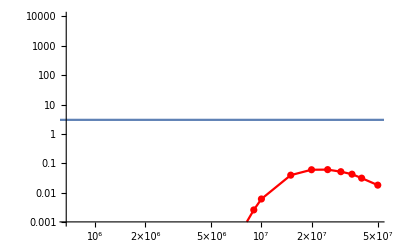

```mathematica
Show[ListLogLogPlot[{falisthigh},PlotStyle-> Red, Mesh-> All,Joined->True,PlotRange->{Automatic,{0.001,10^4}}],LogLogPlot[3,{fa,0.1,10^8}]]
```

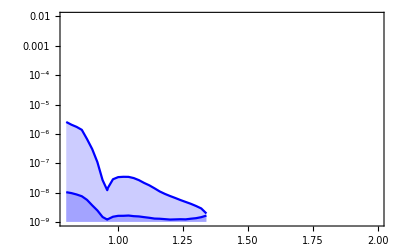

```mathematica
ListLogPlot[{falistmaxhigh,falistminhigh},PlotStyle->Blue,Frame->True,Joined->True,Filling->Bottom,PlotRange->{{0.8,2},{10^-9,10^-2}}]
```

#### Combined constraints from this study

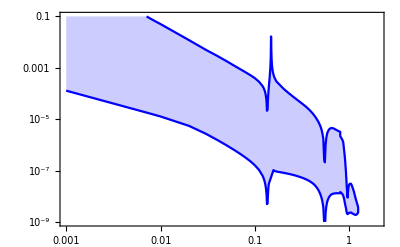

```mathematica
finaldata=Join[falistmin[[6;;Length[falistmin]]],falistminhigh,Reverse[falistmaxhigh],Reverse[falistmax],Reverse[falistmin[[1;;5]]]];
ListLogLogPlot[{finaldata},PlotStyle->Blue,Frame->True,Joined->True,Filling->Top,PlotRange->{{0.001,2},{10^-9,10^-1}}] (*old*)
```

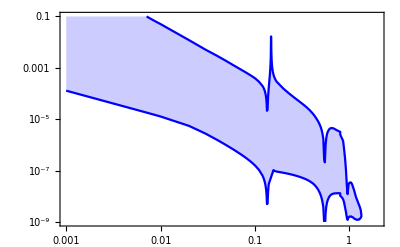

```mathematica
finaldata=Join[falistmin[[6;;Length[falistmin]]],falistminhigh,Reverse[falistmaxhigh],Reverse[falistmax],Reverse[falistmin[[1;;5]]]];
ListLogLogPlot[{finaldata},PlotStyle->Blue,Frame->True,Joined->True,Filling->Top,PlotRange->{{0.001,2},{10^-9,10^-1}}]
```

## Other constraints

#### SN (from 2004.01193)

```mathematica
SNErdata=Import["./SN-Ertas.csv","Data"];
SNErfinal=SNErdata;
SNErfinal[[All,1]]=SNErdata[[All,1]]/10^3;
SNErfinal[[All,2]]=SNErdata[[All,2]]*8/10^3;

SNChFiddata=Import["./SN-Chang-Fiducial.csv","Data"];
SNChFidfinal=SNChFiddata;
SNChFidfinal[[All,1]]=SNChFiddata[[All,1]]/10^3;
SNChFidfinal[[All,2]]=SNChFiddata[[All,2]]*8/10^3;
```

#### Cosmo Updated (from 2002.08370)

```mathematica
mPi=135/1000;
cosmoupdata=Import["./cosmo-updated.csv","Data"];
cosmoupfinal=cosmoupdata;
cosmoupfinal[[All,1]]=cosmoupdata[[All,1]]/10^3;
cosmoupfinal[[All,2]]=cosmoupdata[[All,2]]/(2Pi 1/137 Abs[cgamma[cosmoupfinal[[All,1]],c1,c2,c3]]);
cosmoupfinal=Drop[cosmoupfinal,{Length[cosmoupfinal]-1}]; (*dropping a point where effective cγγ naively becomes zero, in reality it would get smoothed out by the ALP width*) 
cosmoupfinal=Join[{{0.001,0.2},{cosmoupfinal[[1,1]],0.2}},cosmoupfinal]; (*the first two are dummy points, added just for plotting purposes*)
```

#### E787+E949 (from 2004.01193)

```mathematica
E787data=Import["./E787.csv","Data"];
E787final=E787data;
E787final[[All,1]]=E787data[[All,1]]/10^3;
E787final[[All,2]]=E787data[[All,2]]*8/10^3;
```

#### BD (from 1709.00009)

```mathematica
BDdata1=Import["./BD1.csv","Data"];
BDdata2=Import["./BD2.csv","Data"];
mPi=135/1000;

BDdata=Join[BDdata2,BDdata1];
BDfinal=BDdata;
BDfinal[[All,2]]=BDdata[[All,2]]/(2Pi 1/137 Abs[cgamma[BDfinal[[All,1]],c1,c2,c3]]);
```

#### CHARM (from 1811.12522)

```mathematica
charmdata1=Import["./CHARM1.csv"];
charmdata2=Import["./CHARM2.csv"];
charmfinal=Join[charmdata1,Reverse[charmdata2]];
```

#### NA62 (from 2004.01193)

```mathematica
NA62data=Import["./NA62.csv","Data"];
NA62final=NA62data;
NA62final[[All,1]]=NA62data[[All,1]]/10^3;
NA62final[[All,2]]=NA62data[[All,2]]*8/10^3;

NA62data2=Import["./NA62-2.csv","Data"];
NA62final2=NA62data2;
NA62final2[[All,1]]=NA62data2[[All,1]]/10^3;
NA62final2[[All,2]]=NA62data2[[All,2]]*8/10^3;
NA62Fin=Join[NA62final,Reverse[NA62final2]];
```

#### Summary data (from 2005.05170)

```mathematica
summarylowmassdata=Import["./Summary-Data-2005.05170.csv"];
summarylowmassfinal=summarylowmassdata;
summarylowmassfinal[[All,2]]=1/summarylowmassdata[[All,2]]/(4 Pi^2); 
summarylowmassfinal[[All,1]]=summarylowmassdata[[All,1]]/1000;
```

#### Other constraints (based on 1811.03474, taken from 1811.12522)

```mathematica
otherdata=Import["./other-constraints-from-FASER.csv","Data"];
```

#### FASER (from 1811.12522)

```mathematica
faser1=Import["./FASER-1.csv","Data"];
faser2=Import["./FASER-2.csv","Data"];
fasercombined=Join[faser1,Reverse[faser2]];

faser21=Import["./FASER2-1.csv","Data"];
faser22=Import["./FASER2-2.csv","Data"];
faser2combined=Join[faser21,Reverse[faser22]];
```

#### LHC dijet (from 1710.01743)

```mathematica
LHCDJdata=Import["./LHC-dijet.csv"];
LHCDJfinal=LHCDJdata;
LHCDJfinal[[All,2]]=1/LHCDJdata[[All,2]]/(2 Pi^2)/1000*10;
```

#### LHC Diphoton (from 1710.01743)

```mathematica
LHCDPdata=Import["./LHC-DP-Combined.csv"];
LHCDPfinal=LHCDPdata;
LHCDPfinal[[All,2]]=1/LHCDPfinal[[All,2]]/(2 Pi^2)/1000*100; (*The last factor=100 is the rescaling to c3=1, c1=c2=0.1 and the reduced photon branching fraction*)
```

#### HL LHC Projection (from 1710.01743)

```mathematica
HLLHCDPdata=Import["./HL-LHC-DP.csv"];
HLLHCDPfinal=HLLHCDPdata;
HLLHCDPfinal[[All,2]]=1/HLLHCDPfinal[[All,2]]/(2 Pi^2)/1000*(1+5/3*1)/(0.1+5/3*0.1);
```

#### Combined existing constraints

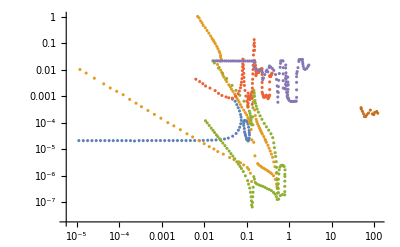

```mathematica
ListLogLogPlot[{E787final,BDfinal,charmfinal,summarylowmassfinal,otherdata,LHCDJfinal}]
```

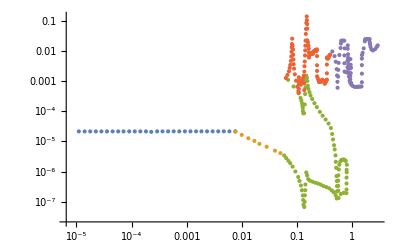

```mathematica
ListLogLogPlot[{E787final[[1;;29]],BDfinal[[19;;26]],charmfinal[[18;;113]],summarylowmassfinal[[13;;Length[summarylowmassfinal]]],otherdata[[40;;Length[otherdata]]]}]
```

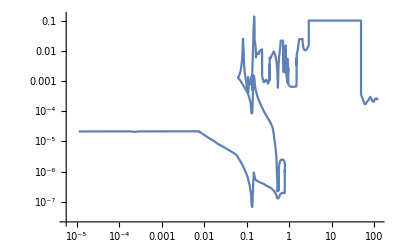

```mathematica
combined=Join[E787final[[1;;29]],BDfinal[[19;;26]],charmfinal[[18;;113]],summarylowmassfinal[[13;;Length[summarylowmassfinal]]],otherdata[[40;;Length[otherdata]]],{{otherdata[[Length[otherdata],1]],0.1}},{{LHCDJfinal[[1,1]],0.1}},LHCDJfinal]; (*a couple of dummy points with 1/f_G=0.1 added just for plotting convenience*)
ListLogLogPlot[combined,Joined->True]
```

#### MATHUSLA (from 1911.00481)

```mathematica
MATHUSLAdata={{0.051986049165234964,0.0013410615350441166},{0.05615116882977519,0.0011972671056295562},{0.06135190756683929,0.0010190062839289548},{0.06574109052394883,0.0009169398217634748},{0.07184726625566747,0.0007479162590887357},{0.07877924376980422,0.0006036018926056707},{0.08427250401696117,0.0005093936915100309},{0.09123131434952401,0.0004089443553025492},{0.10003121900422532,0.0003072402363479036},{0.1081400226613497,0.0002626697714272105},{0.1168236020518344,0.00022647444446013916},{0.12855061346128435,0.00014750914658613517},{0.1318194305229974,0.00010619352849286489},{0.13430835441547956,0.00007786677738783966},{0.13808028578459614,0.00013563644696357706},{0.14082288197818224,0.00023020494636883287},{0.14388626547749933,0.00039825132803679176},{0.14527357055239154,0.0006203817835499996},{0.1455007953816,0.0008497308174158022},{0.15093930890665544,0.00032516733994096607},{0.15684814848249393,0.0002610526457524175},{0.16612386530425693,0.00021932464039737623},{0.17888654845546403,0.00019509259852798657},{0.19476746137915052,0.0001773206451522168},{0.21081136652911742,0.00016709377502316128},{0.23206203656740648,0.00015827123828256198},{0.25050243634573227,0.00015274786618774483},{0.27315772847856146,0.0001418300393958118},{0.29465150184315364,0.00013226831475490682},{0.32217503714869317,0.00011757192787230062},{0.3583086883753024,0.00009853156222049971},{0.394273502913899,0.00007896383170834305},{0.42318761662406645,0.000052002883509156285},{0.44308164264186356,0.00003258686502081917},{0.47220769882573294,0.000020445560966569662},{0.4975094894982974,0.000013171368180059902},{0.5085685190629089,8.824974834469333*^-6},{0.5157724956399816,6.156500966029618*^-6},{0.5249147771904258,3.7790940752122992*^-6},{0.5344995190691871,2.2693090694872123*^-6},{0.5412830043235914,1.2797479596742952*^-6},{0.5469895833091688,7.736282549004089*^-7},{0.5636655574522306,2.243995659694941*^-6},{0.5756117482629969,4.048359774384981*^-6},{0.5880737767680206,6.429229321799808*^-6},{0.6029369974964814,0.000010085233250743535},{0.642745238498445,0.000014772598783853335},{0.7073613167373953,0.00001853413037364141},{0.7867762491886915,0.000021403832591842833},{0.8446229695761769,0.000024428435811159906},{0.8688013696936757,0.000015884339913404145},{0.8927494713934065,9.902137238361037*^-6},{0.9122808777820584,6.559272739815722*^-6},{0.932237068740376,4.113634421758444*^-6},{0.9422361037515662,2.780138286222321*^-6},{0.9461134406175632,1.8956231417578708*^-6},{0.9507694555449362,1.1575622403072976*^-6},{0.9758251264742642,2.7763540165072324*^-6},{1.034662160871887,3.129045642580573*^-6},{1.1257443072808435,2.416734495831251*^-6},{1.2115646746196418,1.7956090036884802*^-6},{1.3071045111900639,1.4556536283031732*^-6},{1.4463599017108961,1.2210564609961398*^-6},{1.608614998436379,1.1020832543801253*^-6},{1.7855122327638107,1.1065565303837093*^-6},{1.9260542251391493,1.1131964470120348*^-6},{2.105977247106503,1.0034185178289134*^-6},{2.3374973089515465,9.155816545795013*^-7},{2.521431965951965,8.598365835968232*^-7},{2.7514100880989814,7.903592091459243*^-7},{2.9679254083649207,7.504240302187265*^-7},{3.2517934570316767,7.012298549841548*^-7},{3.6019906189342876,6.490830035505879*^-7},{3.885424771817947,6.086526575798249*^-7},{4.239844176976012,5.7302153731272*^-7},{4.573499012868558,5.48151892206013*^-7},{4.990682948943958,5.160625457575881*^-7},{5.3834130914700795,4.902313405185819*^-7},{5.874488603174171,4.6476534264795224*^-7},{6.341273001086193,4.438190071210081*^-7},{6.9148083943352,4.185671397825762*^-7},{7.501399743142398,4.004009531004146*^-7},{8.139424402395397,3.8647587022428326*^-7},{8.830057469814603,3.90738100938952*^-7},{8.72681729677511,9.774959356393863*^-7},{8.101237318792263,1.1999347899935407*^-6},{7.336253197428219,1.5286349828597608*^-6},{6.6434633810106485,1.9095216197545745*^-6},{6.016083721337601,2.36975570618923*^-6},{5.458976612083826,2.9035835222238617*^-6},{4.8985761487038575,3.563212183971527*^-6},{4.435966744021444,4.393178957359106*^-6},{3.9805811240682307,5.374437589550066*^-6},{3.611938440981702,6.42099878733036*^-6},{3.2477014442028955,7.728939526602797*^-6},{2.9409719691596585,9.283034575769914*^-6},{2.6897281191819657,0.000010498217808759739},{2.493546693582708,0.000011610530043915159},{2.2626152887197972,0.000013806759566697802},{2.034440359454893,0.00001643890063553777},{1.8385426785984385,0.000018878013144756606},{1.6959430442222256,0.000016732897801108185},{1.5635936438355038,0.000016331684540030387},{1.432312407472916,0.000018942829036593995},{1.3216351052034685,0.000026430499555478746},{1.2300941563895087,0.00004073183856339808},{1.1665622808438887,0.00006486593801902743},{1.1102541758271152,0.0001072799617913539},{1.0539690540383773,0.0001659476593007306},{0.9602264977207403,0.000187624040090508},{0.951756430028416,0.00002978993061621992},{0.9507926728341004,0.00001755023417813856},{0.9506321264016955,0.0001307211967166101},{0.9496855732323125,0.000053204838466532},{0.9486682029048656,0.00007504952951834006},{0.9425274069930035,0.000012007897037266001},{0.9236681274110976,0.0003306024852858426},{0.917243325031361,0.00046703831477071413},{0.914127237552477,0.000728897153557709},{0.9046052962409415,0.0012201147008582046},{0.8951440464506721,0.0017851529439435415},{0.8920898456957065,0.002660046103570343},{0.876614635273472,0.005408355919748018},{0.8522384305284314,0.008939527578351378},{0.8053471673415395,0.013449473355639346},{0.7418100868486464,0.016676517812809825},{0.6877089749775992,0.01882430900232972},{0.6290304397711851,0.016128676141806245},{0.5936521216397767,0.010089184584217856},{0.5769706864204933,0.006502140188853409},{0.5610197760740107,0.003580117735041875},{0.5478914861350653,0.00015435546576991082},{0.5471260160952859,0.0009974511567335702},{0.547080074866204,0.0006675550113672203},{0.5467198237899847,0.00044866570948515064},{0.5466522982909005,0.0003047907531769937},{0.5464296006680749,0.0013644972904153366},{0.5463172012938958,0.00008945644498095216},{0.5413323886771162,0.0022219100157732548},{0.5279911529533059,0.005035367091236525},{0.5169519904596053,0.007847501648624515},{0.5007967376904544,0.012836122679703398},{0.4800105562200787,0.020548966226081804},{0.4517749796872196,0.032983812708956464},{0.42111594751391407,0.04828376917473738},{0.3854393485926413,0.06726437030992719},{0.35278278385137823,0.09168459496836753},{0.3217487983395027,0.12307697748984972},{0.29240514039113763,0.16306985998965906},{0.265737454167084,0.2155873686046263},{0.241500545516301,0.28008820751118924},{0.2198071889367948,0.36016430617409634},{0.19889446819935394,0.4923307181614122},{0.18191100116594297,0.6374011255947585},{0.16709190511991942,0.9035971298344082},{0.13969867731174612,0.6671510084322959},{0.13837254545085456,0.40670239468404296},{0.1368518207693431,0.1930597875315236},{0.13612805736873962,0.10594863618342412},{0.13401020350166742,0.06829924755998222},{0.13283386188699423,0.15796202255928482},{0.13014517227268427,0.2974693875306909},{0.12669369104304368,0.41931307621366465},{0.1205755596551044,0.6443905147304573},{0.11131519046541996,0.9081132542977353}};
MATHUSLAfinal=MATHUSLAdata;
MATHUSLAfinal[[All,1]]=MATHUSLAdata[[All,1]];
MATHUSLAfinal[[All,2]]=MATHUSLAdata[[All,2]]*8/10^3;
```

#### CODEX-b (from 1911.00481)

```mathematica
codexbcalo1=Import["./CODEX-bwcalo-1.csv","Data"];
codexbcalo2=Import["./CODEX-bwcalo-2.csv","Data"];
codexbcombined=Join[codexbcalo1,Reverse[codexbcalo2]];
codexbfinal=codexbcombined;
codexbfinal[[All,1]]=codexbcombined[[All,1]];
codexbfinal[[All,2]]=codexbcombined[[All,2]]*8/10^3;
```

#### Theory parameters

```mathematica
Λmax=1658.047000156266;
Mp=2.4*10^18;
dim=6;
```

### CMS Track Trigger Search (from 1911.12364 )

#### Efficiency factors, m_a,f_a in GeV

```mathematica
faMaPlane3evwPT30={{1,8181},{1.3,44323},{1.5,65725},{1.8,58076},{2,55909},{4,91016},{6,167220},{8,244103},{10,331492},{12,444057},{14,611733},{16,788218},{18,10^6},{20,1.3*10^6},{22,2.18*10^6},{22,2.47*10^6},{20,3*10^6},{18,3.4*10^6},{16,3.7*10^6},{14,3.9*10^6},{12,3.9*10^6},{10,3.78*10^6},{8,3.4*10^6},{6,2.84*10^6},{4,2*10^6},{2,783193},{1.8,651661},{1.5,598502},{1.3,340571},{1,164980}};
faMaPlane10evwPT30={{1,10232},{1.3,56618},{1.5,86419},{1.8,72533},{2,71082},{4,118362},{6,198543},{8,307219},{10,454181},{12,652662},{14,1.16*10^6},{14,1.54*10^6},{12,1.9*10^6},{10,2.1*10^6},{8,2.1*10^6},{6,1.9*10^6},{4,1.43*10^6},{2,541037},{1.8,453630},{1.5,413415},{1.3,198115},{1,112029}};
faMaPlane3evwHT100={{1,10880},{1.3,68957},{1.5,99307},{1.8,78132},{2,76631},{3,91054},{4,128554},(*{5,506851},*){6,211161},{8,328672},{10,505132},{12,740787},{13,1.16*10^6},{13,1.26*10^6},{12,1.5*10^6},{10,1.8*10^6},{8,1.8*10^6},(*{6.3,921178},{6.5,1.1*10^6},{6.3,1.2*10^6},*){6,1.67*10^6},(*{5,1.6*10^6},*){4,1.26*10^6},{3,941794},{2,474137},{1.8,391229},{1.5,360560},{1.3,155171},{1,100209}};
faMaPlane10evwHT100={(*{1,13023},*){1.8,137614},{2,107819},{3,130311},{4,172397},{5,239091},{6,306412},{7,459224},{7.5,601353},{7.5,679669},{7,780808},(*{6.3,921178},{6.5,1.1*10^6},{6.3,1.2*10^6},*){6,884514},{5,888240},{4,789501},{3,605536},{2,287247},{1.8,202213}(*,{1,74655}*)};
```

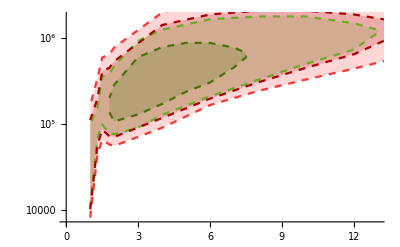

```mathematica
Show[ListLogPlot[faMaPlane3evwHT100,Joined-> True,PlotStyle->{Dashed,Lighter[Green,0.2]},Filling->Bottom],
ListLogPlot[faMaPlane10evwHT100,Joined->True,PlotStyle->{Dashed,Darker[Green]},Filling->Bottom],
ListLogPlot[faMaPlane3evwPT30,Joined->True,PlotStyle->{Dashed,Lighter[Red,0.2]},Filling->Bottom],
ListLogPlot[faMaPlane10evwPT30,Joined->True,PlotStyle->{Dashed,Darker[Red]},Filling->Bottom]]
```

```mathematica
faMaPlane10evwHT100[[All,2]]
```

{137614,107819,130311,172397,239091,306412,459224,601353,679669,780808,884514,888240,789501,605536,287247,202213}

```mathematica
scaledfaMaPlane10evwHT100=faMaPlane10evwHT100;
scaledfaMaPlane10evwHT100[[All,2]]=1/(4 Pi^2 faMaPlane10evwHT100[[All,2]]);
scaledfaMaPlane10evwPT30=faMaPlane10evwPT30;
scaledfaMaPlane10evwPT30[[All,2]]=1/(4 Pi^2 faMaPlane10evwPT30[[All,2]]);
scaledfaMaPlane3evwHT100=faMaPlane3evwHT100;
scaledfaMaPlane3evwHT100[[All,2]]=1/(4 Pi^2 faMaPlane3evwHT100[[All,2]]);
scaledfaMaPlane3evwPT30=faMaPlane3evwPT30;
scaledfaMaPlane3evwPT30[[All,2]]=1/(4 Pi^2 faMaPlane3evwPT30[[All,2]]);
```

## Final Plots

```mathematica
invfGtoinvfa={{1/(4 Pi^2*10^1),"10^1",{0.02,0},{}},{1/(4 Pi^2*10^2),"10^2",{0.02,0},{}},{1/(4 Pi^2*10^3),"10^3",{0.02,0},{}},{1/(4 Pi^2*10^4),"10^4",{0.02,0},{}},{1/(4 Pi^2*10^5),"10^5",{0.02,0},{}},{1/(4 Pi^2*10^6),"10^6",{0.02,0},{}},{1/(4 Pi^2*10^7),"10^7",{0.02,0},{}},{1/(4 Pi^2*10^8),"10^8",{0.02,0},{}},{1/(4 Pi^2*10^9),"10^9",{0.02,0},{}},{1/(4 Pi^2*10^10),"10^10",{0.02,0},{}},{1/(4 Pi^2*10^11),"10^11",{0.02,0},{}}};
For[k=-11,k<0,k++,For[j=2,j<10,j++,AppendTo[invfGtoinvfa,{j*1/(4 Pi^2)*10^k," ",{0.01,0},{}}]]];

invfGtoinvfaMaj={{1/(4 Pi^2*10^-2),"10^-2",{0.02,0},{}},{1/(4 Pi^2*10^-1),"10^-1",{0.02,0},{}},{1/(4 Pi^2*10^0),"1",{0.02,0},{}},{1/(4 Pi^2*10^1),"10^1",{0.02,0},{}},{1/(4 Pi^2*10^2),"10^2",{0.02,0},{}},{1/(4 Pi^2*10^3),"10^3",{0.02,0},{}},{1/(4 Pi^2*10^4),"10^4",{0.02,0},{}},{1/(4 Pi^2*10^5),"10^5",{0.02,0},{}},{1/(4 Pi^2*10^6),"10^6",{0.02,0},{}},{1/(4 Pi^2*10^7),"10^7",{0.02,0},{}},{1/(4 Pi^2*10^8),"10^8",{0.02,0},{}},{1/(4 Pi^2*10^9),"10^9",{0.02,0},{}},{1/(4 Pi^2*10^10),"10^10",{0.02,0},{}},{1/(4 Pi^2*10^11),"10^11",{0.02,0},{}}};
```

#### Current+DUNE

```mathematica
Show[ListLogLogPlot[finaldata,PlotStyle->Red,Frame->True,Joined->True,Filling->1,FrameLabel->{{Style[MaTeX["g_{agg}=1/f_G[\\text{GeV}^{-1}]",Magnification->1.5],FontSize->15,Black],Style[MaTeX["f_a[\\text{GeV}]",Magnification->1.5],FontSize->15,Black]},{Style[MaTeX["m_a[\\text{GeV}]",Magnification->1.5],FontSize->15,Black],None}},ImageSize->600,PlotRange->{{0.001,10^2},{10^-9,10^-2}},FrameTicks->{{LogTicks[10,10^-10,1(*,TickLabelStep->1*),ShowMinorTicks->True],invfGtoinvfa},{LogTicks[10,0.001,10^4],LogTicks[10,0.001,10^4,ShowTickLabels-> False]}},FrameTicksStyle->Directive[Black,15,AbsoluteThickness[0.5]],Epilog->{Style[Text[Style[Framed[MaTeX["\\textbf{Gluon Dominance}",Magnification->1.2],FrameStyle->{Gray,Thickness[1],Background->Opacity[1,White]},RoundingRadius->5],{15,Black},FontFamily->"CMU Serif"],{Log[0.007],Log[10^-8.4]}(*{Log[20],Log[10^-4.3]}*)],20],Style[Text[Style[Rotate["SN1987A",-0.4],{15,Gray},FontFamily->"CMU Serif"],{Log[0.04],Log[10^-7.2]}],20],Style[Text[Style[Rotate["BBN+N_eff",-Pi/2],{15,Gray},FontFamily->"CMU Serif"],{Log[1.7*10^-3],Log[10^-3.7]}],20],Style[Text[Style[Rotate["DUNE ND",-0.8],{15,Red},FontFamily->"CMU Serif"],{Log[0.05],Log[10^-6.4]}],20],Style[Text[Style[Rotate["Existing Constraints",-0.4],{15,Gray},FontFamily->"CMU Serif"],{Log[0.02],Log[10^-4.5]}],20],Style[Text[Style[Rotate["Colored Particles",0.0],{15,Lighter[Gray,0.1]},FontFamily->"CMU Serif"],{Log[10],Log[10^-3.5]}],20],Style[Text[Style[Rotate["H' Quality Problem",0.45],{15,Blue},FontFamily->"CMU Serif"],{Log[20],Log[10^-8.1]}],15],Style[Text[Style[Rotate["PQ Quality Problem",-0.2],{15,Blue},FontFamily->"CMU Serif"],{Log[10^-2.0],Log[10^-7.7]}],20],Style[Text[Style[Rotate["QCD Axion",0.5],{15,Brown},FontFamily->"CMU Serif"],{Log[10^-2.5],Log[10^-2.5]}],10],Style[Text[Style[Rotate["f_a < Λ_QCD'",-0.42],{15,Brown},FontFamily->"CMU Serif"],{Log[23],Log[3*10^-3]}],20]},LabelStyle->{FontFamily->"CMU Serif",FontSize->12}],ListLogLogPlot[SortBy[SNErfinal,Last],PlotStyle->{Gray,Dashed},Filling->Top,Joined->True],ListLogLogPlot[SortBy[SNChFidfinal,Last],PlotStyle->{Gray,Dashed},Filling->Top,Joined->True],ListLogLogPlot[cosmoupfinal,PlotStyle->{Gray,Dashed},Filling->Bottom,Joined->True],ListLogLogPlot[combined,PlotStyle->{Gray},Filling->1,Joined->True],LogLogPlot[{1/(4 Pi^2 Sqrt[0.6]*(alphas[10^6]^-0.4*Λmax)^2/ma),1/(4 Pi^2(ma^(2/(dim-2)) Mp^((dim-4)/(dim-2)))/10^(10/(dim-2))),1/(4 Pi^2 ma),ma/(4 Pi^2 mPi fpi),1/(2000Pi)},{ma,10^-3,10^4},PlotStyle->{None,None,None,None,None},Filling->{1->{Bottom,Directive[Blue,Opacity[0.2]]},2->{Bottom,Directive[Blue,Opacity[0.2]]},3->{Top,Directive[Brown,Opacity[0.2]]},4->{Top,Directive[Brown,Opacity[0.2]]},5->{Top,Directive[Gray,Opacity[0.2]]}}]]
```

-Graphics-

#### ...+Upcoming

```mathematica
Show[ListLogLogPlot[finaldata,PlotStyle->Red,Frame->True,Joined->True,Filling->1,FrameLabel->{{Style[MaTeX["g_{agg}=1/f_G[\\text{GeV}^{-1}]",Magnification->1.5],FontSize->15,Black],Style[MaTeX["f_a[\\text{GeV}]",Magnification->1.5],FontSize->15,Black]},{Style[MaTeX["m_a[\\text{GeV}]",Magnification->1.5],FontSize->15,Black],None}},ImageSize->600,PlotRange->{{0.001,10^2},{10^-9,10^-1.999}},FrameTicks->{{LogTicks[10,10^-10,1,TickLabelStep->1,ShowMinorTicks->True],invfGtoinvfa},{LogTicks[10,0.001,10^4],LogTicks[10,0.001,10^4,ShowTickLabels-> False]}},FrameTicksStyle->Directive[Black,15,AbsoluteThickness[0.5]],Epilog->{Style[Text[Style[Framed[MaTeX["\\textbf{Gluon Dominance}",Magnification->1.2],FrameStyle->{Black,Thickness[1],Background->Opacity[1,White]},RoundingRadius->5],{15,Black},FontFamily->"CMU Serif"],{Log[0.007],Log[10^-8.4]}(*{Log[20],Log[10^-4.3]}*)],20],Style[Text[Style[Rotate["SN1987A",-0.4],{15,Gray},FontFamily->"CMU Serif"],{Log[0.04],Log[10^-7.2]}],20],Style[Text[Style[Rotate["BBN+N_eff",-Pi/2],{15,Gray},FontFamily->"CMU Serif"],{Log[1.7*10^-3],Log[10^-3.7]}],20],Style[Text[Style[Rotate["NA62",0.0],{15,Lighter[Purple,0.4]},FontFamily->"CMU Serif"],{Log[0.007],Log[10^-5.4]}],20],Style[Text[Style[Rotate["FASER",-0.8],{15,Cyan},FontFamily->"CMU Serif"],{Log[1.5],Log[10^-4.6]}],20],Style[Text[Style[Rotate["LHC Track Trigger",-0.65],{15,Darker[Orange,0.2]},FontFamily->"CMU Serif"],{Log[10],Log[10^-6.7]}],20],Style[Text[Style[Rotate["DUNE ND",-0.8],{15,Red},FontFamily->"CMU Serif"],{Log[0.05],Log[10^-6.4]}],20],Style[Text[Style[Rotate["Existing Constraints",-0.4],{15,Gray},FontFamily->"CMU Serif"],{Log[0.02],Log[10^-4.5]}],20],Style[Text[Style[Rotate["Colored Particles",0.0],{15,Lighter[Gray,0.1]},FontFamily->"CMU Serif"],{Log[10],Log[10^-3.5]}],20],Style[Text[Style[Rotate["H' Quality Problem",0.45],{15,Blue},FontFamily->"CMU Serif"],{Log[20],Log[10^-8.3]}],15],Style[Text[Style[Rotate["PQ Quality Problem",-0.2],{15,Blue},FontFamily->"CMU Serif"],{Log[10^-2.0],Log[10^-7.7]}],20],Style[Text[Style[Rotate["QCD Axion",0.5],{15,Brown},FontFamily->"CMU Serif"],{Log[10^-2.5],Log[10^-2.5]}],10],Style[Text[Style[Rotate["f_a < Λ_QCD'",-0.42],{15,Brown},FontFamily->"CMU Serif"],{Log[23],Log[3*10^-3]}],20]},LabelStyle->{FontFamily->"CMU Serif",FontSize->12}],ListLogLogPlot[SortBy[SNErfinal,Last],PlotStyle->{Gray,Dashed},Filling->Top,Joined->True],ListLogLogPlot[SortBy[SNChFidfinal,Last],PlotStyle->{Gray,Dashed},Filling->Top,Joined->True],ListLogLogPlot[cosmoupfinal,PlotStyle->{Gray,Dashed},Filling->Bottom,Joined->True],ListLogLogPlot[NA62Fin(*[[1;;47]]*),PlotStyle->{Lighter[Purple,0.4],DotDashed}(*,Filling->10^-4.7*),Joined->True],ListLogLogPlot[fasercombined,PlotStyle->{Cyan,DotDashed}(*,Filling->Top*),Joined->True],ListLogLogPlot[combined,PlotStyle->{Gray},Filling->1,Joined->True],ListLogLogPlot[scaledfaMaPlane3evwPT30,Joined->True,PlotStyle->{DotDashed,Darker[Orange,0.2]}(*,Filling->Bottom*)],LogLogPlot[{1/(4 Pi^2 Sqrt[0.6]*(alphas[10^6]^-0.4*Λmax)^2/ma),1/(4 Pi^2(ma^(2/(dim-2)) Mp^((dim-4)/(dim-2)))/10^(10/(dim-2))),1/(4 Pi^2 ma),ma/(4 Pi^2 mPi fpi),1/(2000Pi)},{ma,10^-3,10^4},PlotStyle->{None,None,None,None,None},Filling->{1->{Bottom,Directive[Blue,Opacity[0.2]]},2->{Bottom,Directive[Blue,Opacity[0.2]]},3->{Top,Directive[Brown,Opacity[0.2]]},4->{Top,Directive[Brown,Opacity[0.2]]},5->{Top,Directive[Gray,Opacity[0.2]]}} ]]
```

-Graphics-

#### ...+Proposed

```mathematica
Show[ListLogLogPlot[finaldata,PlotStyle->Red,Frame->True,Joined->True,Filling->1,FrameLabel->{{Style[MaTeX["g_{agg}=1/f_G[\\text{GeV}^{-1}]",Magnification->1.5],FontSize->15,Black],Style[MaTeX["f_a[\\text{GeV}]",Magnification->1.5],FontSize->15,Black]},{Style[MaTeX["m_a[\\text{GeV}]",Magnification->1.5],FontSize->15,Black],None}},ImageSize->600,PlotRange->{{0.001,10^2},{10^-9,10^-1.999}},FrameTicks->{{LogTicks[10,10^-10,1,TickLabelStep->1,ShowMinorTicks->True],invfGtoinvfa},{LogTicks[10,0.001,10^4],LogTicks[10,0.001,10^4,ShowTickLabels-> False]}},FrameTicksStyle->Directive[Black,15,AbsoluteThickness[0.5]],Epilog->{Style[Text[Style[Framed[MaTeX["\\textbf{Gluon Dominance}",Magnification->1.2],FrameStyle->{Black,Thickness[1],Background->Opacity[1,White]},RoundingRadius->5],{15,Black},FontFamily->"CMU Serif"],{Log[0.007],Log[10^-8.4]}(*{Log[20],Log[10^-4.3]}*)],20],Style[Text[Style[Rotate["SN1987A",-0.4],{15,Gray},FontFamily->"CMU Serif"],{Log[0.04],Log[10^-7.2]}],20],Style[Text[Style[Rotate["BBN+N_eff",-Pi/2],{15,Gray},FontFamily->"CMU Serif"],{Log[1.7*10^-3],Log[10^-3.7]}],20],Style[Text[Style[Rotate["NA62",0.0],{15,Lighter[Purple,0.4]},FontFamily->"CMU Serif"],{Log[0.007],Log[10^-5.4]}],20],Style[Text[Style[Rotate["FASER",-0.8],{15,Cyan},FontFamily->"CMU Serif"],{Log[1.5],Log[10^-4.6]}],20],Style[Text[Style[Rotate["LHC Track Trigger",-0.65],{15,Darker[Orange,0.2]},FontFamily->"CMU Serif"],{Log[10],Log[10^-6.7]}],20],Style[Text[Style[Rotate["DUNE ND",-0.8],{15,Red},FontFamily->"CMU Serif"],{Log[0.05],Log[10^-6.4]}],20],Style[Text[Style[Rotate["Existing Constraints",-0.4],{15,Gray},FontFamily->"CMU Serif"],{Log[0.02],Log[10^-4.5]}],20],Style[Text[Style[Rotate["Colored Particles",0.0],{15,Lighter[Gray,0.1]},FontFamily->"CMU Serif"],{Log[10],Log[10^-3.5]}],20],Style[Text[Style[Rotate["H' Quality Problem",0.45],{15,Blue},FontFamily->"CMU Serif"],{Log[20],Log[10^-8.3]}],15],Style[Text[Style[Rotate["PQ Quality Problem",-0.2],{15,Blue},FontFamily->"CMU Serif"],{Log[10^-2.0],Log[10^-7.7]}],20],Style[Text[Style[Rotate["QCD Axion",0.5],{15,Brown},FontFamily->"CMU Serif"],{Log[10^-2.5],Log[10^-2.5]}],10],Style[Text[Style[Rotate["f_a < Λ_QCD'",-0.42],{15,Brown},FontFamily->"CMU Serif"],{Log[23],Log[3*10^-3]}],20],Style[Text[Style[Rotate["FASER2",-0.0],{15,Lighter[Pink,0.2]},FontFamily->"CMU Serif"],{Log[30],Log[10^-4.9]}],20],Style[Text[Style[Rotate["CODEX-b",-0.0],{15,Lighter[Magenta,0.5]},FontFamily->"CMU Serif"],{Log[30],Log[10^-5.4]}],20],Style[Text[Style[Rotate["MATHUSLA",-0.0],{15,Lighter[Green,0.6]},FontFamily->"CMU Serif"],{Log[30],Log[10^-5.9]}],20]},LabelStyle->{FontFamily->"CMU Serif",FontSize->12}],ListLogLogPlot[SortBy[SNErfinal,Last],PlotStyle->{Gray,Dashed},Filling->Top,Joined->True],ListLogLogPlot[SortBy[SNChFidfinal,Last],PlotStyle->{Gray,Dashed},Filling->Top,Joined->True],ListLogLogPlot[cosmoupfinal,PlotStyle->{Gray,Dashed},Filling->Bottom,Joined->True],ListLogLogPlot[NA62Fin(*[[1;;47]]*),PlotStyle->{Lighter[Purple,0.4],DotDashed}(*,Filling->10^-4.7*),Joined->True],ListLogLogPlot[fasercombined,PlotStyle->{Cyan,DotDashed}(*,Filling->Top*),Joined->True],ListLogLogPlot[combined,PlotStyle->{Gray},Filling->1,Joined->True],ListLogLogPlot[faser2combined,PlotStyle->{Lighter[Pink,0.2],Dotted}(*,Filling->Top*),Joined->True],ListLogLogPlot[scaledfaMaPlane3evwPT30,Joined->True,PlotStyle->{DotDashed,Darker[Orange,0.2]}(*,Filling->Bottom*)],ListLogLogPlot[codexbfinal,PlotStyle->{Lighter[Magenta,0.5],Dotted}(*,Filling->Top*),Joined->True],ListLogLogPlot[MATHUSLAfinal,PlotStyle->{Lighter[Green,0.6],Dotted}(*,Filling->Top*),Joined->True],LogLogPlot[{1/(4 Pi^2 Sqrt[0.6]*(alphas[10^6]^-0.4*Λmax)^2/ma),1/(4 Pi^2(ma^(2/(dim-2)) Mp^((dim-4)/(dim-2)))/10^(10/(dim-2))),1/(4 Pi^2 ma),ma/(4 Pi^2 mPi fpi),1/(2000Pi)},{ma,10^-3,10^4},PlotStyle->{None,None,None,None,None},Filling->{1->{Bottom,Directive[Blue,Opacity[0.2]]},2->{Bottom,Directive[Blue,Opacity[0.2]]},3->{Top,Directive[Brown,Opacity[0.2]]},4->{Top,Directive[Brown,Opacity[0.2]]},5->{Top,Directive[Gray,Opacity[0.2]]}}]]
```

-Graphics-

#### Theory Plot

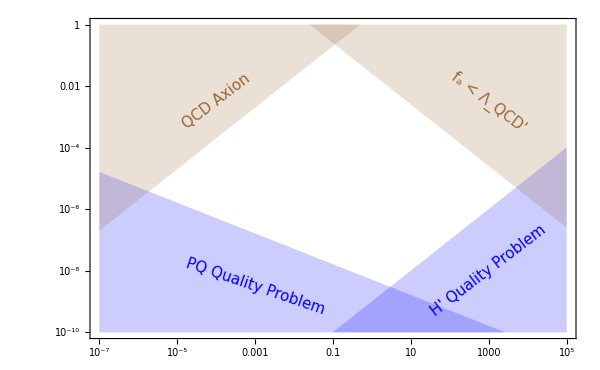

```mathematica
Show[LogLogPlot[{1/(4 Pi^2 Sqrt[0.6]*(alphas[10^6]^-0.4*Λmax)^2/ma),1/(4 Pi^2(ma^(2/(dim-2)) Mp^((dim-4)/(dim-2)))/10^(10/(dim-2))),1/(4 Pi^2 ma),ma/(4 Pi^2 mPi fpi)(*,1/(2000Pi)*)},{ma,10^-7,10^5},PlotStyle->{None,None,None,None,None},Frame-> True,Filling->{1->{Bottom,Directive[Blue,Opacity[0.2]]},2->{Bottom,Directive[Blue,Opacity[0.2]]},3->{Top,Directive[Brown,Opacity[0.2]]},4->{Top,Directive[Brown,Opacity[0.2]]},5->{Top,Directive[Gray,Opacity[0.2]]}},FrameLabel->{{Style[MaTeX["g_{agg}=1/f_G[\\text{GeV}^{-1}]",Magnification->1.5],FontSize->15,Black],Style[MaTeX["f_a[\\text{GeV}]",Magnification->1.5],FontSize->15,Black]},{Style[MaTeX["m_a[\\text{GeV}]",Magnification->1.5],FontSize->15,Black],None}},ImageSize->600,PlotRange->{{10^-7,10^5},{10^-10,1}},FrameTicks->{{LogTicks[10,10^-10,1,TickLabelStep->1,ShowMinorTicks->False],invfGtoinvfaMaj},{LogTicks[10,10^-7,10^5,ShowMinorTicks->False],LogTicks[10,10^-7,10^5,ShowTickLabels-> False,ShowMinorTicks->False]}},FrameTicksStyle->Directive[Black,15,AbsoluteThickness[0.5]],Epilog->{Style[Text[Style[Rotate["H' Quality Problem",0.65],{15,Blue},FontFamily->"CMU Serif"],{Log[10^3],Log[10^-8]}],15],Style[Text[Style[Rotate["PQ Quality Problem",-0.33],{15,Blue},FontFamily->"CMU Serif"],{Log[10^-3.0],Log[10^-8.5]}],20],Style[Text[Style[Rotate["QCD Axion",0.65],{15,Brown},FontFamily->"CMU Serif"],{Log[10^-4],Log[10^-2.5]}],10],Style[Text[Style[Rotate["f_a < Λ_QCD'",-0.65],{15,Brown},FontFamily->"CMU Serif"],{Log[10^3],Log[3*10^-3]}],20]},LabelStyle->{FontFamily->"CMU Serif",FontSize->12}]]
```